```mathematica
Get["G:\\My Drive\\PhD Pisa\\Calculations, Data and Designs\\Wolfram Mathematica\\SuperDataAnalysis.m"]
```

```mathematica
SetWorkingDirectory[]
```

Working directory set to: G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-03-06 Al DB 7\

```mathematica
Needs["ErrorBarPlots`"]
```

## Datasets

```mathematica
AlDB20dev7rotatingBSet
```

Device | Measurement | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 4rows |  |  |  |  | Dataset[{__Association}]

```mathematica
datasetFile=FileNameJoin[{NotebookDirectory[],"AlDB20_dev7_datasets.wl"}]
```

G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\AlDB20_dev7_datasets.wl

```mathematica
Save[datasetFile,AlDB20dev7rotatingBSet]
```

```mathematica
Save[datasetFile,AlDB20IcvB]
```

```mathematica
Save[datasetFile,AlDB20dev7IcvV]
```

```mathematica
Save[datasetFile,AlDB20dev7IrvT]
```

```mathematica
Get[datasetFile];
```

```mathematica
datasetFile
```

G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\AlDB20_dev7_datasets.wl

## Measurements

## IV

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-09 
File name = 2019-09-09 m004

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]}

Number of sweeps detected: 2

s1Length = 202

s1Values = {0.,0.15,0.3,0.45,0.6,0.75,0.9,1.05,1.2,1.35,1.5,1.65,1.8,1.95,2.1,2.25,2.4,2.55,2.7,2.85,3.,3.15,3.3,3.45,3.6,3.75,3.9,4.05,4.2,4.35,4.5,4.65,4.8,4.95,5.1,5.25,5.4,5.55,5.7,5.85,6.,6.15,6.3,6.45,6.6,6.75,6.9,7.05,7.2,7.35,7.5,7.65,7.8,7.95,8.1,8.25,8.4,8.55,8.7,8.85,9.,9.15,9.3,9.45,9.6,9.75,9.9,10.05,10.2,10.35,10.5,10.65,10.8,10.95,11.1,11.25,11.4,11.55,11.7,11.85,12.,12.15,12.3,12.45,12.6,12.75,12.9,13.05,13.2,13.35,13.5,13.65,13.8,13.95,14.1,14.25,14.4,14.55,14.7,14.85,15.,15.,14.85,14.7,14.55,14.4,14.25,14.1,13.95,13.8,13.65,13.5,13.35,13.2,13.05,12.9,12.75,12.6,12.45,12.3,12.15,12.,11.85,11.7,11.55,11.4,11.25,11.1,10.95,10.8,10.65,10.5,10.35,10.2,10.05,9.9,9.75,9.6,9.45,9.3,9.15,9.,8.85,8.7,8.55,8.4,8.25,8.1,7.95,7.8,7.65,7.5,7.35,7.2,7.05,6.9,6.75,6.6,6.45,6.3,6.15,6.,5.85,5.7,5.55,5.4,5.25,5.1,4.95,4.8,4.65,4.5,4.35,4.2,4.05,3.9,3.75,3.6,3.45,3.3,3.15,3.,2.85,2.7,2.55,2.4,2.25,2.1,1.95,1.8,1.65,1.5,1.35,1.2,1.05,0.9,0.75,0.6,0.45,0.3,0.15,0.}

s2Length = 2

s2Values = {0.,10.}

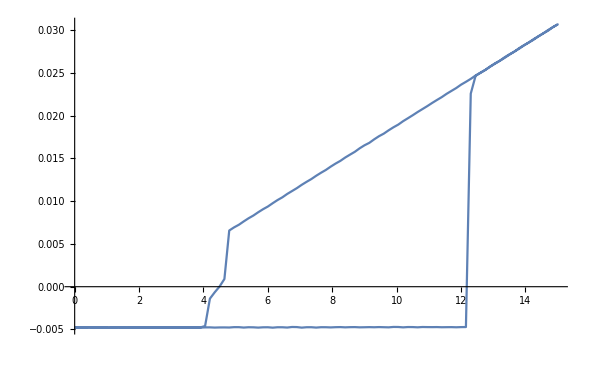

```mathematica
ListLinePlot[Transpose[{S2Split[TakeColumn[1]][[1]],S2Split[TakeColumn[5]][[1]]}]]
```

## Gating

### 2019-09-25 m002 Gating

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m002

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V],Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 3

s1Length = 101

s2Length = 5

s3Length = 6

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.}

s3Values = {0.,4.,8.,12.,16.,20.}

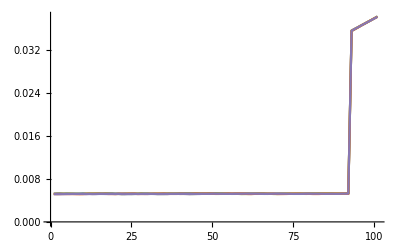
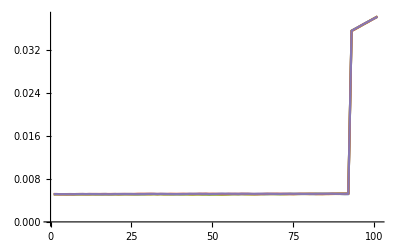
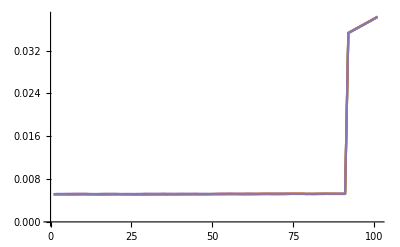
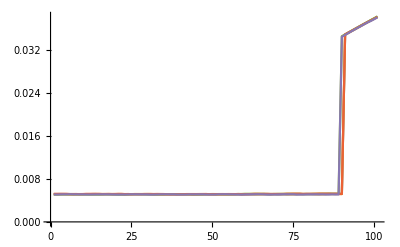
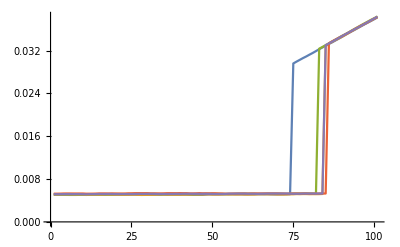
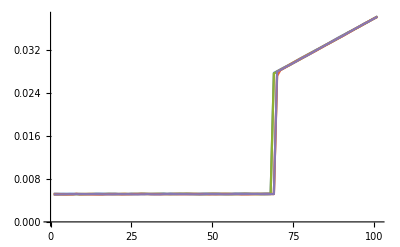

```mathematica
Map[ListLinePlot[#,PlotRange->Full]&,S3S2Split[TakeColumn[5]]]
```

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m002","T"->50,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 6rows |  |  | Dataset[{__Association}]

#### prep

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.001]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,12.74},{0.,12.74},{0.,12.74},{0.,12.74},{0.,12.74}},{{4.,12.74},{4.,12.74},{4.,12.74},{4.,12.74},{4.,12.74}},{{8.,12.6},{8.,12.6},{8.,12.6},{8.,12.6},{8.,12.6}},{{12.,12.46},{12.,12.46},{12.,12.32},{12.,12.46},{12.,12.32}},{{16.,10.22},{16.,11.62},{16.,11.34},{16.,11.76},{16.,11.62}},{{20.,9.38},{20.,9.52},{20.,9.38},{20.,9.52},{20.,9.52}}}

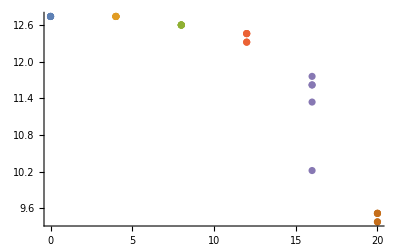

```mathematica
ListPlot[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.001]}]&,S3S2Split[TakeColumn[5]]]]
```

```mathematica
Mean[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.001]}]&,S3S2Split[TakeColumn[5]]]]
```

{{10.,11.69},{10.,11.9467},{10.,11.8533},{10.,11.97},{10.,11.9233}}

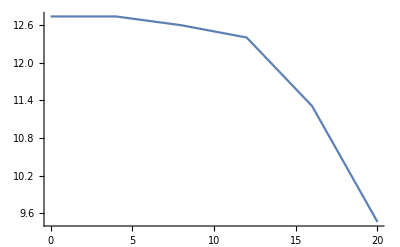

```mathematica
ListLinePlot[Map[Mean,MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.001]}]&,S3S2Split[TakeColumn[5]]]]]
```

#### I_C(V_Gate)

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
5 levels | 1rows |  |  | Dataset[{__Association}]

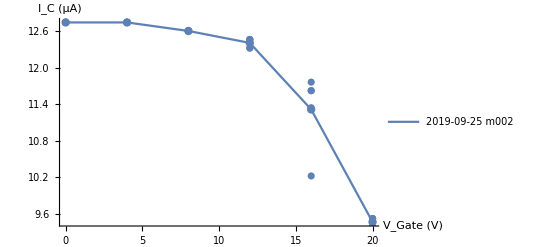

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

#### prep

```mathematica
Flatten[MapIndexed[{$s3Values[[#2]][[1]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}],1]
```

{{0.,-6.93496×10^-11},{0.,-6.7276×10^-11},{0.,-6.22276×10^-11},{0.,-5.8969×10^-11},{0.,-7.20032×10^-11},{4.,9.28816×10^-12},{4.,1.46447×10^-11},{4.,-1.33063×10^-11},{4.,-2.63656×10^-11},{4.,-5.23169×10^-12},{8.,2.73707×10^-12},{8.,-1.65725×10^-11},{8.,-4.08766×10^-11},{8.,-1.69233×10^-11},{8.,-3.68797×10^-11},{12.,2.58518×10^-11},{12.,-1.68273×10^-11},{12.,-3.59865×10^-11},{12.,-2.9754×10^-11},{12.,-4.73311×10^-11},{16.,-3.34667×10^-13},{16.,2.93437×10^-11},{16.,-2.31359×10^-11},{16.,-3.00661×10^-11},{16.,-1.45912×10^-11},{20.,4.90708×10^-11},{20.,-5.55747×10^-12},{20.,3.29487×10^-11},{20.,-3.57448×10^-11},{20.,-2.41413×10^-11}}

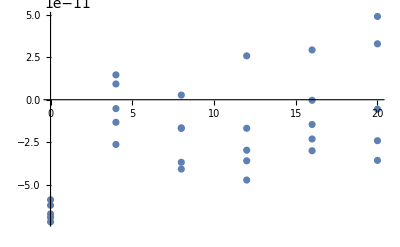

```mathematica
ListPlot[Flatten[MapIndexed[{$s3Values[[#2]][[1]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}],1]]
```

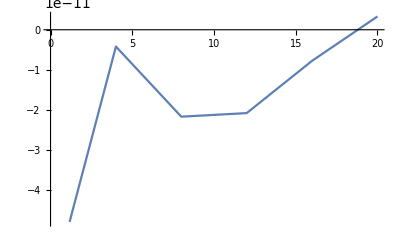

```mathematica
ListLinePlot[Map[Mean,MapIndexed[{$s3Values[[#2]][[1]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}]]]
```

#### Leakage current

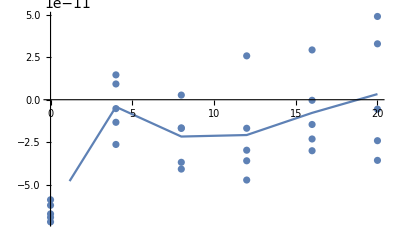

```mathematica
Show[{
ListPlot[Flatten[MapIndexed[{$s3Values[[#2]][[1]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}],1]],
ListLinePlot[Map[Mean,MapIndexed[{$s3Values[[#2]][[1]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}]]]
}]
```

### 2019-09-25 m003 Gating

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m003

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V],Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 7

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {10.,12.,14.,16.,18.,20.,22.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m003","T"->50,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 7rows |  |  | Dataset[{__Association}]

#### Plot

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
5 levels | 1rows |  |  | Dataset[{__Association}]

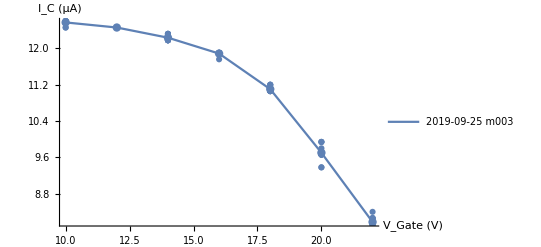

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

#### Leakage current K2400

```mathematica
MapIndexed[{$s3Values[[#2[[1]]]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}]
```

{{{10.,3.05373×10^-12},{10.,-5.03616×10^-12},{10.,-1.56887×10^-11},{10.,-7.06862×10^-12},{10.,4.4061×10^-12},{10.,-3.38464×10^-11},{10.,-6.83894×10^-11},{10.,-1.10984×10^-11},{10.,-1.87929×10^-11},{10.,-1.10446×10^-11}},{{12.,-2.12765×10^-12},{12.,-2.63697×10^-11},{12.,-2.70329×10^-11},{12.,-4.24746×10^-12},{12.,-6.02013×10^-12},{12.,-1.17784×10^-11},{12.,1.56668×10^-11},{12.,-2.12208×10^-11},{12.,-9.0133×10^-12},{12.,-2.97496×10^-11}},{{14.,7.65251×10^-12},{14.,-2.12832×10^-11},{14.,-2.07246×10^-11},{14.,7.99017×10^-12},{14.,-1.8396×10^-11},{14.,-6.97225×10^-12},{14.,-5.77865×10^-11},{14.,-5.02361×10^-11},{14.,-1.51371×10^-11},{14.,3.93843×10^-12}},{{16.,-2.94192×10^-11},{16.,-1.99025×10^-11},{16.,-1.59136×10^-11},{16.,-4.36678×10^-11},{16.,-3.79528×10^-11},{16.,-5.67417×10^-12},{16.,-4.43363×10^-11},{16.,9.09502×10^-12},{16.,-2.78504×10^-11},{16.,-3.30955×10^-11}},{{18.,-4.30998×10^-12},{18.,-4.46492×10^-11},{18.,-4.13575×10^-13},{18.,7.85684×10^-12},{18.,-2.58894×10^-11},{18.,-1.36186×10^-11},{18.,2.95883×10^-13},{18.,2.73118×10^-11},{18.,3.69656×10^-12},{18.,-3.59786×10^-11}},{{20.,3.30844×10^-12},{20.,-1.85376×10^-11},{20.,1.35893×10^-11},{20.,-3.73804×10^-11},{20.,-9.447×10^-12},{20.,-3.06963×10^-11},{20.,-1.51561×10^-12},{20.,-2.41791×10^-11},{20.,-2.48878×10^-11},{20.,-1.6239×10^-11}},{{22.,6.9599×10^-10},{22.,5.61581×10^-10},{22.,2.98706×10^-10},{22.,4.48914×10^-10},{22.,5.20792×10^-10},{22.,5.685×10^-10},{22.,6.76781×10^-10},{22.,6.93791×10^-10},{22.,7.86873×10^-10},{22.,5.66271×10^-10}}}

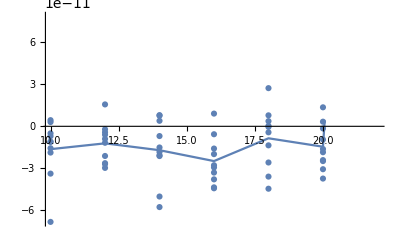

```mathematica
Show[{
ListPlot[Flatten[MapIndexed[{$s3Values[[#2[[1]]]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}],1]],
ListLinePlot[Map[Mean,MapIndexed[{$s3Values[[#2[[1]]]],Mean[#1]}&,S3S2Split[TakeColumn[6]],{2}]]]
}]
```

### 2019-10-22 m016 T = 50 mK, Reference V_Gate curve

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m016

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 402

s2Length = 50

s3Length = 25

s1Values = {-14.,-13.86,-13.72,-13.58,-13.44,-13.3,-13.16,-13.02,-12.88,-12.74,-12.6,-12.46,-12.32,-12.18,-12.04,-11.9,-11.76,-11.62,-11.48,-11.34,-11.2,-11.06,-10.92,-10.78,-10.64,-10.5,-10.36,-10.22,-10.08,-9.94,-9.8,-9.66,-9.52,-9.38,-9.24,-9.1,-8.96,-8.82,-8.68,-8.54,-8.4,-8.26,-8.12,-7.98,-7.84,-7.7,-7.56,-7.42,-7.28,-7.14,-7.,-6.86,-6.72,-6.58,-6.44,-6.3,-6.16,-6.02,-5.88,-5.74,-5.6,-5.46,-5.32,-5.18,-5.04,-4.9,-4.76,-4.62,-4.48,-4.34,-4.2,-4.06,-3.92,-3.78,-3.64,-3.5,-3.36,-3.22,-3.08,-2.94,-2.8,-2.66,-2.52,-2.38,-2.24,-2.1,-1.96,-1.82,-1.68,-1.54,-1.4,-1.26,-1.12,-0.98,-0.84,-0.7,-0.56,-0.42,-0.28,-0.14,1.73195×10^-14,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,1.73195×10^-14,-0.14,-0.28,-0.42,-0.56,-0.7,-0.84,-0.98,-1.12,-1.26,-1.4,-1.54,-1.68,-1.82,-1.96,-2.1,-2.24,-2.38,-2.52,-2.66,-2.8,-2.94,-3.08,-3.22,-3.36,-3.5,-3.64,-3.78,-3.92,-4.06,-4.2,-4.34,-4.48,-4.62,-4.76,-4.9,-5.04,-5.18,-5.32,-5.46,-5.6,-5.74,-5.88,-6.02,-6.16,-6.3,-6.44,-6.58,-6.72,-6.86,-7.,-7.14,-7.28,-7.42,-7.56,-7.7,-7.84,-7.98,-8.12,-8.26,-8.4,-8.54,-8.68,-8.82,-8.96,-9.1,-9.24,-9.38,-9.52,-9.66,-9.8,-9.94,-10.08,-10.22,-10.36,-10.5,-10.64,-10.78,-10.92,-11.06,-11.2,-11.34,-11.48,-11.62,-11.76,-11.9,-12.04,-12.18,-12.32,-12.46,-12.6,-12.74,-12.88,-13.02,-13.16,-13.3,-13.44,-13.58,-13.72,-13.86,-14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.}

s3Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Dataset[{
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m016","T"->50,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]|>
}]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 1rows |  |  | Dataset[{__Association}]

#### Retrapping Dataset for V_Gate = 0 V

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m016","T"->50,"IR"->Transpose[{Table[50,{48}],FindSlopeArray[Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_42 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 11rows |  |  | Dataset[{__Association}]

#### Retrapping for V_Gate = 0 V

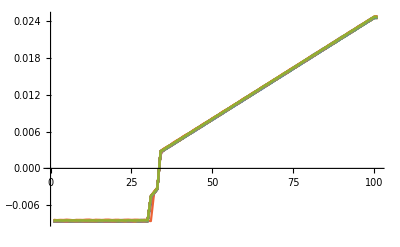

```mathematica
Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

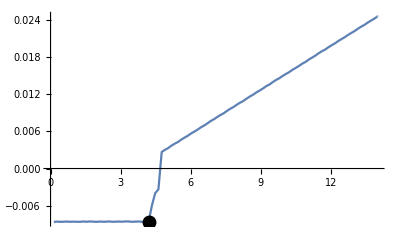
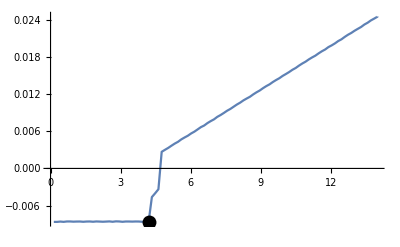
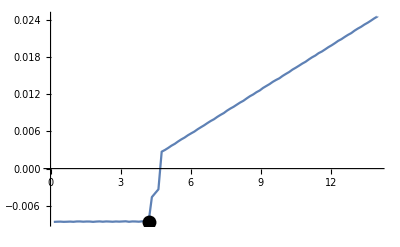
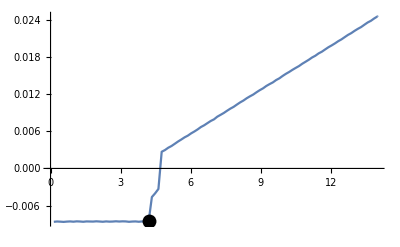
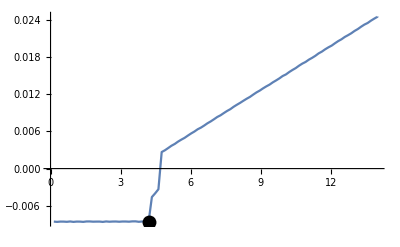
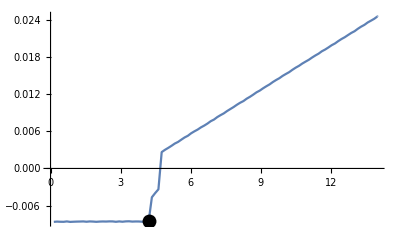
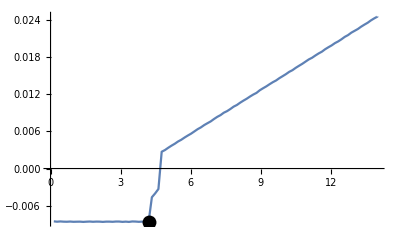
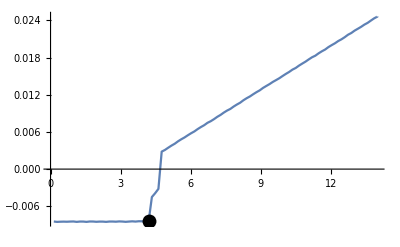
{{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{31,4.34,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-},{30,4.2,-Graphics-}}

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

```mathematica
Transpose[{Table[100,{48}],FindSlopeArray[Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;301]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.34},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2},{100,4.2}}

#### Plots

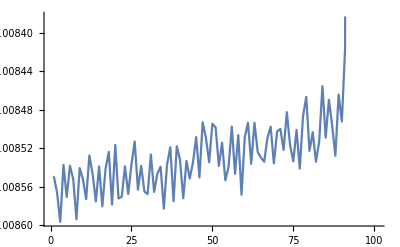

```mathematica
S3S2Split[TakeColumn[5]][[1,1]][[100;;200]]//ListLinePlot
```

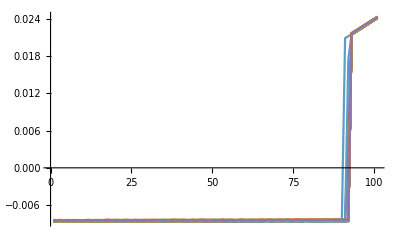

```mathematica
ListLinePlot[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[1]],PlotRange->Full]
```

```mathematica
S3S2Split[TakeColumn[1]][[1,1]]
```

{-14.,-13.86,-13.72,-13.58,-13.44,-13.3,-13.16,-13.02,-12.88,-12.74,-12.6,-12.46,-12.32,-12.18,-12.04,-11.9,-11.76,-11.62,-11.48,-11.34,-11.2,-11.06,-10.92,-10.78,-10.64,-10.5,-10.36,-10.22,-10.08,-9.94,-9.8,-9.66,-9.52,-9.38,-9.24,-9.1,-8.96,-8.82,-8.68,-8.54,-8.4,-8.26,-8.12,-7.98,-7.84,-7.7,-7.56,-7.42,-7.28,-7.14,-7.,-6.86,-6.72,-6.58,-6.44,-6.3,-6.16,-6.02,-5.88,-5.74,-5.6,-5.46,-5.32,-5.18,-5.04,-4.9,-4.76,-4.62,-4.48,-4.34,-4.2,-4.06,-3.92,-3.78,-3.64,-3.5,-3.36,-3.22,-3.08,-2.94,-2.8,-2.66,-2.52,-2.38,-2.24,-2.1,-1.96,-1.82,-1.68,-1.54,-1.4,-1.26,-1.12,-0.98,-0.84,-0.7,-0.56,-0.42,-0.28,-0.14,1.73195×10^-14,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,1.73195×10^-14,-0.14,-0.28,-0.42,-0.56,-0.7,-0.84,-0.98,-1.12,-1.26,-1.4,-1.54,-1.68,-1.82,-1.96,-2.1,-2.24,-2.38,-2.52,-2.66,-2.8,-2.94,-3.08,-3.22,-3.36,-3.5,-3.64,-3.78,-3.92,-4.06,-4.2,-4.34,-4.48,-4.62,-4.76,-4.9,-5.04,-5.18,-5.32,-5.46,-5.6,-5.74,-5.88,-6.02,-6.16,-6.3,-6.44,-6.58,-6.72,-6.86,-7.,-7.14,-7.28,-7.42,-7.56,-7.7,-7.84,-7.98,-8.12,-8.26,-8.4,-8.54,-8.68,-8.82,-8.96,-9.1,-9.24,-9.38,-9.52,-9.66,-9.8,-9.94,-10.08,-10.22,-10.36,-10.5,-10.64,-10.78,-10.92,-11.06,-11.2,-11.34,-11.48,-11.62,-11.76,-11.9,-12.04,-12.18,-12.32,-12.46,-12.6,-12.74,-12.88,-13.02,-13.16,-13.3,-13.44,-13.58,-13.72,-13.86,-14.}

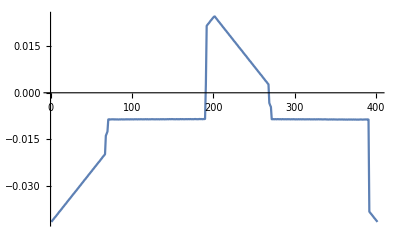
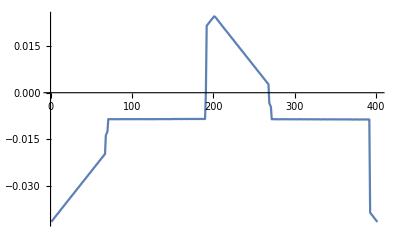
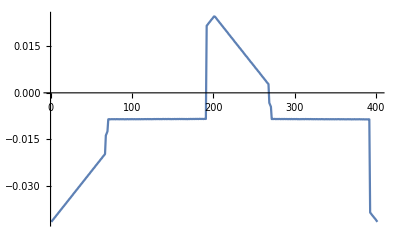
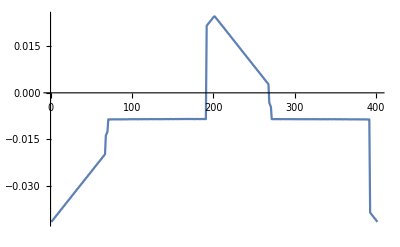
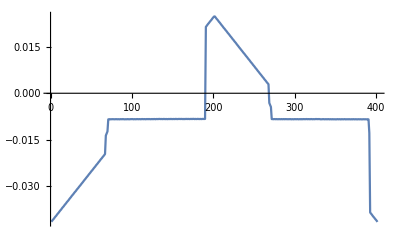
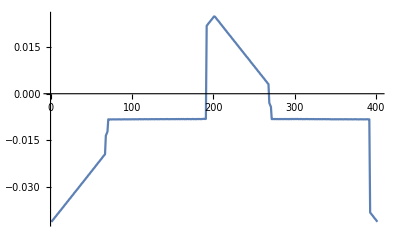
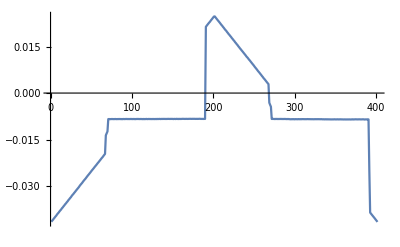
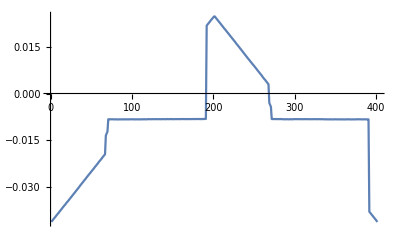

```mathematica
Table[ListLinePlot[S3S2Split[TakeColumn[5]][[i]][[1]]],{i,1,$s3Length}]
```

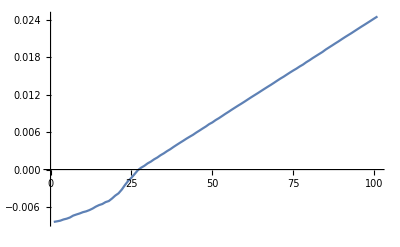

```mathematica
ListLinePlot[S3S2Split[TakeColumn[5]][[-2,1]][[100;;200]]]
```

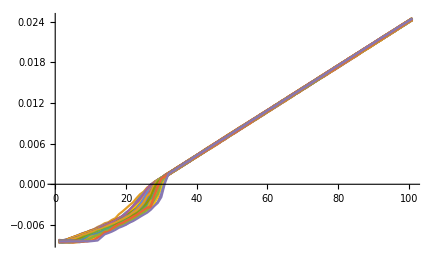

```mathematica
Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-2]]]//ListLinePlot
```

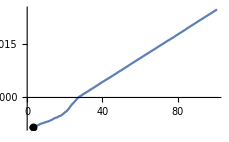
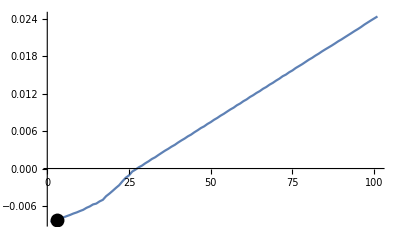
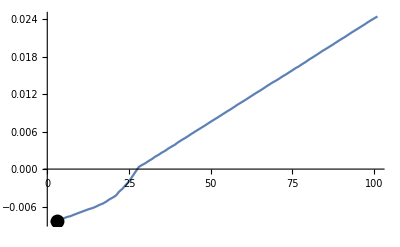
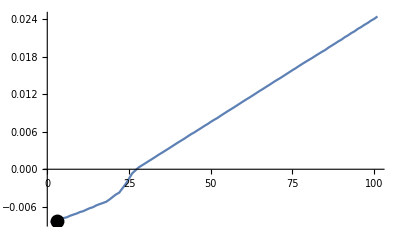
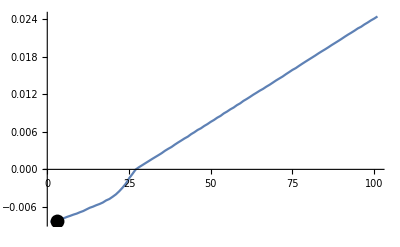
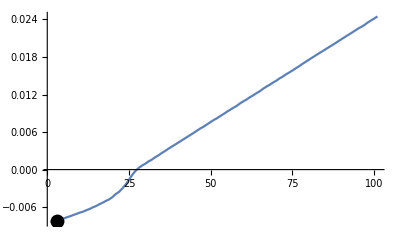
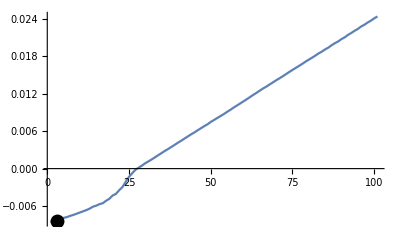
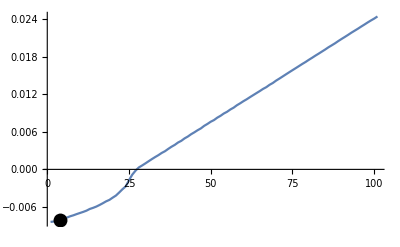
{{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{5,-Graphics-},{4,-Graphics-},{5,-Graphics-},{5,-Graphics-},{6,-Graphics-},{5,-Graphics-},{5,-Graphics-},{7,-Graphics-},{9,-Graphics-},{11,-Graphics-},{9,-Graphics-},{9,-Graphics-},{11,-Graphics-},{9,-Graphics-},{8,-Graphics-},{7,-Graphics-},{8,-Graphics-},{8,-Graphics-},{9,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{7,-Graphics-},{8,-Graphics-},{7,-Graphics-},{7,-Graphics-},{6,-Graphics-},{8,-Graphics-},{7,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{7,-Graphics-},{8,-Graphics-},{7,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{11,-Graphics-},{12,-Graphics-}}

```mathematica
ShowFindSlopeArray[Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-2]]],0.0001]
```

```mathematica
FindSlopeArray[Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-4]]],0.0001,1]//ListPlot
```

-Graphics-

```mathematica
FindSlopeArray[Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-3]]],0.0001,1]//ListPlot
```

-Graphics-

```mathematica
FindSlopeArray[Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-2]]],0.0001,1]//ListPlot
```

-Graphics-

```mathematica
FindSlopeArray[Map[#[[100;;200]]&,S3S2Split[TakeColumn[5]][[-1]]],0.0001,1]//ListPlot
```

-Graphics-

```mathematica
Table[ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],S3S2Split[TakeColumn[5]][[i,1]]}]],{i,{1,15,18,21,24}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],S3S2Split[TakeColumn[5]][[i,1]]-S3S2Split[TakeColumn[5]][[i,1,100]]}],AspectRatio->GoldenRatio],{i,{1,18,21,24}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 1rows |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
ListLinePlot[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[1]],PlotRange->Full]
```

#### Retrapping current dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m016","T"->-50,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[5]]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 12rows |  |  | Dataset[{__Association}]

#### Retrapping plots

```mathematica
ListLinePlot[Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[5]]][[-2]],PlotRange->Full]
```

-Graphics-

```mathematica
Module[{data},
data=MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[5]]]];

Show[{
ListLinePlot[Map[Mean,data],Mesh->All,PlotRange->All],
ListPlot[data,PlotStyle->Blue]}]
]
```

-Graphics-

```mathematica
Module[{dataset=Reverse[AlDB20dev7IcvV[Select[#Measurement == "2019-10-22 m016"&]]],legend},
Print[dataset];
legend={"Switching current","Retrapping current"};
Show[Table[datasetPlot[dataset ,i,legend[[i]],{AxesLabel->{"V_Gate (V)", "I_C (μA)"},PlotRange->{0,13}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == "2019-10-22 m016" &]]},
Print[dataset];

Show[{
dataset= ReplacePart[dataset,{2,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[2,"IC"]]]]]];
ListLinePlot[dataset [2,"IC"],PlotLegends->{"Switching current"},AxesLabel->{"V_Gate (V)" ,"I_C (μA)"},Mesh->All,PlotRange->{{0,25},{0,1.1}}]
,
dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];
ListLinePlot[dataset [1,"IC"],PlotLegends->{"Retrapping current"},Mesh->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotRange->{{0,25},{0,1.1}}]
}]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

-Graphics-

#### Interpolating

```mathematica
ListLinePlot[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[-2]],PlotRange->Full]
```

-Graphics-

```mathematica
{ListLinePlot[Mean[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[-4]]],PlotRange->Full],
ListLinePlot[Mean[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[-3]]],PlotRange->Full],
ListLinePlot[Mean[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[-2]]],PlotRange->Full],
ListLinePlot[Mean[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]][[-1]]],PlotRange->Full]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]]//ListPlot
```

-Graphics-

Deleting the last two points

```mathematica
Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}]//ListPlot
```

-Graphics-

```mathematica
f=Interpolation[Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}],InterpolationOrder->3,Method->"Spline"]
```

InterpolatingFunction[{{0., 22.}}, <>]

```mathematica
Show[{
Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}]//ListPlot,
Plot[f[x],{x,0,22},PlotStyle->Orange]
}]
```

-Graphics-

```mathematica
Plot[f[x],{x,0,23},PlotStyle->Orange]
```

-Graphics-

```mathematica
x/.FindRoot[f[x],{x,20}]
```

22.3836

```mathematica
MovingAverage
```

```mathematica
Module[{data,func},
data=Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}];

func=Interpolation[data,InterpolationOrder->1,Method->"Spline"];
{
Show[{
Plot[func[x],{x,0,25},PlotStyle->Orange],
data//ListPlot
}]
,
Plot[Evaluate[D[func[x],x]],{x,0,25}],
x/.FindRoot[func[x],{x,20}]
}
]
```

{-Graphics-,-Graphics-,22.602}

```mathematica
Module[{data,func},
data=Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}];

func=Interpolation[data,InterpolationOrder->3,Method->"Spline"];
{
Show[{
Plot[func[x],{x,0,25},PlotStyle->Orange],

data//ListPlot
}]
,
Plot[Evaluate[D[func[x],x]],{x,0,20}],
x/.FindRoot[func[x],{x,20}]
}
]
```

{-Graphics-,-Graphics-,22.3836}

```mathematica
Module[{data,func1,func2},
data=Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}];

func1=Interpolation[data,InterpolationOrder->1,Method->"Spline"];
func2=Interpolation[data,InterpolationOrder->3,Method->"Spline"];

Show[{
Plot[func1[x],{x,0,25},PlotStyle->Orange],
Plot[func2[x],{x,0,25},PlotStyle->Purple],
data//ListPlot
}]

]
```

-Graphics-

#### Reference curve

```mathematica
Module[{data,func},
data=Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}];

func=Interpolation[data,InterpolationOrder->1];

Show[{
Plot[func[x],{x,0,25},PlotStyle->Orange],
data//ListPlot
}]

]
```

-Graphics-

```mathematica
refVGate=Module[{data,func},
data=Delete[Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]],{{-1},{-2}}];

func=Interpolation[data,InterpolationOrder->1]
]
```

InterpolatingFunction[{{0., 22.}}, <>]

#### Linear fit

```mathematica
LinearModelFit
```

```mathematica
Module[{data,func},
data=Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]];

{
data//ListPlot,
data[[17;;-3]]//ListPlot
}
]
```

{-Graphics-,-Graphics-}

```mathematica
Module[{data,func},
data=Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]];

func=LinearModelFit[data[[17;;-3]],x,x];
{
x/.FindRoot[func[x],{x,20}],
Show[{
ListPlot[data],
Plot[func[x],{x,15,25}]
}]
}
]
```

{22.8858,-Graphics-}

### 2019-10-22 m018 T = 150 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m018

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 13

s1Values = {0.,0.13,0.26,0.39,0.52,0.65,0.78,0.91,1.04,1.17,1.3,1.43,1.56,1.69,1.82,1.95,2.08,2.21,2.34,2.47,2.6,2.73,2.86,2.99,3.12,3.25,3.38,3.51,3.64,3.77,3.9,4.03,4.16,4.29,4.42,4.55,4.68,4.81,4.94,5.07,5.2,5.33,5.46,5.59,5.72,5.85,5.98,6.11,6.24,6.37,6.5,6.63,6.76,6.89,7.02,7.15,7.28,7.41,7.54,7.67,7.8,7.93,8.06,8.19,8.32,8.45,8.58,8.71,8.84,8.97,9.1,9.23,9.36,9.49,9.62,9.75,9.88,10.01,10.14,10.27,10.4,10.53,10.66,10.79,10.92,11.05,11.18,11.31,11.44,11.57,11.7,11.83,11.96,12.09,12.22,12.35,12.48,12.61,12.74,12.87,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.,22.,24.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m018","T"->150,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Show[{
ListPlot[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001]}]&,S3S2Split[TakeColumn[5]]],AxesLabel->{"V_Gate","I_C"}],
ListLinePlot[Map[Mean,MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001]}]&,S3S2Split[TakeColumn[5]]]]]}]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
5 levels | 1rows |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-22 m020 T = 250 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m020

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 13

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,2.,4.,6.,8.,10.,12.,14.,16.,18.,20.,22.,24.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m020","T"->250,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 3rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Show[{
ListPlot[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001]}]&,S3S2Split[TakeColumn[5]]],AxesLabel->{"V_Gate","I_C"}],
ListLinePlot[Map[Mean,MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001]}]&,S3S2Split[TakeColumn[5]]]]]}]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
5 levels | 1rows |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-22 m022 T = 350 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m022

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 19

s1Values = {0.,0.07,0.14,0.21,0.28,0.35,0.42,0.49,0.56,0.63,0.7,0.77,0.84,0.91,0.98,1.05,1.12,1.19,1.26,1.33,1.4,1.47,1.54,1.61,1.68,1.75,1.82,1.89,1.96,2.03,2.1,2.17,2.24,2.31,2.38,2.45,2.52,2.59,2.66,2.73,2.8,2.87,2.94,3.01,3.08,3.15,3.22,3.29,3.36,3.43,3.5,3.57,3.64,3.71,3.78,3.85,3.92,3.99,4.06,4.13,4.2,4.27,4.34,4.41,4.48,4.55,4.62,4.69,4.76,4.83,4.9,4.97,5.04,5.11,5.18,5.25,5.32,5.39,5.46,5.53,5.6,5.67,5.74,5.81,5.88,5.95,6.02,6.09,6.16,6.23,6.3,6.37,6.44,6.51,6.58,6.65,6.72,6.79,6.86,6.93,7.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,1.33333,2.66667,4.,5.33333,6.66667,8.,9.33333,10.6667,12.,13.3333,14.6667,16.,17.3333,18.6667,20.,21.3333,22.6667,24.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m022","T"->350,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 4rows |  |  | Dataset[{__Association}]

```mathematica
Show[{
ListPlot[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001,1]}]&,S3S2Split[TakeColumn[5]]],AxesLabel->{"V_Gate","I_C"}],
ListLinePlot[Map[Mean,MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001,1]}]&,S3S2Split[TakeColumn[5]]]]]}]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
5 levels | 1rows |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-22 m024 T = 450 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m024

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 19

s1Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,1.33333,2.66667,4.,5.33333,6.66667,8.,9.33333,10.6667,12.,13.3333,14.6667,16.,17.3333,18.6667,20.,21.3333,22.6667,24.}

#### Dataset

```mathematica
AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m024","T"->450,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]|>
,1]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 5rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Show[{
ListPlot[MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001,1]}]&,S3S2Split[TakeColumn[5]]],AxesLabel->{"V_Gate","I_C"}],
ListLinePlot[Map[Mean,MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001,1]}]&,S3S2Split[TakeColumn[5]]]]]}]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement"],{AxesLabel->{"V_Gate (V)", "I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
5 levels | 1rows |  |  | Dataset[{__Association}]

-Graphics-

## Leakage current

### 2019-09-25 m016 V_Gate: 0 - 25 V

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m016

First row of selectedFile: {s1,s2,SWL,HP334xx,[V],Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 1000

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.}

s2Length = 6

s2Values = {0.,5.,10.,15.,20.,25.}

#### HP data

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotRange->Full]
```

-Graphics-

Dropping the first 10 points

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[10]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[10]}]]]&,S2Split[TakeColumn[4]]]*10^-10}][[1,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[10]}]]]&,S2Split[TakeColumn[4]]]*10^-10}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-09-25 m017 V_Gate: 25 - 15 V

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m017

First row of selectedFile: {s1,s2,SWL,HP334xx,[V],Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 500

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.}

s2Length = 11

s2Values = {25.,24.,23.,22.,21.,20.,19.,18.,17.,16.,15.}

#### HP data

Dropping the first 10 points

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[10]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[10]}]]]&,S2Split[TakeColumn[4]]]*10^-10}],AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->{{0,25},Full}]
```

-Graphics-

### 2019-10-02 m045 V_Gate: -30 - 30 V Between devices

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m045

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 4501

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.,3001.,3002.,3003.,3004.,3005.,3006.,3007.,3008.,3009.,3010.,3011.,3012.,3013.,3014.,3015.,3016.,3017.,3018.,3019.,3020.,3021.,3022.,3023.,3024.,3025.,3026.,3027.,3028.,3029.,3030.,3031.,3032.,3033.,3034.,3035.,3036.,3037.,3038.,3039.,3040.,3041.,3042.,3043.,3044.,3045.,3046.,3047.,3048.,3049.,3050.,3051.,3052.,3053.,3054.,3055.,3056.,3057.,3058.,3059.,3060.,3061.,3062.,3063.,3064.,3065.,3066.,3067.,3068.,3069.,3070.,3071.,3072.,3073.,3074.,3075.,3076.,3077.,3078.,3079.,3080.,3081.,3082.,3083.,3084.,3085.,3086.,3087.,3088.,3089.,3090.,3091.,3092.,3093.,3094.,3095.,3096.,3097.,3098.,3099.,3100.,3101.,3102.,3103.,3104.,3105.,3106.,3107.,3108.,3109.,3110.,3111.,3112.,3113.,3114.,3115.,3116.,3117.,3118.,3119.,3120.,3121.,3122.,3123.,3124.,3125.,3126.,3127.,3128.,3129.,3130.,3131.,3132.,3133.,3134.,3135.,3136.,3137.,3138.,3139.,3140.,3141.,3142.,3143.,3144.,3145.,3146.,3147.,3148.,3149.,3150.,3151.,3152.,3153.,3154.,3155.,3156.,3157.,3158.,3159.,3160.,3161.,3162.,3163.,3164.,3165.,3166.,3167.,3168.,3169.,3170.,3171.,3172.,3173.,3174.,3175.,3176.,3177.,3178.,3179.,3180.,3181.,3182.,3183.,3184.,3185.,3186.,3187.,3188.,3189.,3190.,3191.,3192.,3193.,3194.,3195.,3196.,3197.,3198.,3199.,3200.,3201.,3202.,3203.,3204.,3205.,3206.,3207.,3208.,3209.,3210.,3211.,3212.,3213.,3214.,3215.,3216.,3217.,3218.,3219.,3220.,3221.,3222.,3223.,3224.,3225.,3226.,3227.,3228.,3229.,3230.,3231.,3232.,3233.,3234.,3235.,3236.,3237.,3238.,3239.,3240.,3241.,3242.,3243.,3244.,3245.,3246.,3247.,3248.,3249.,3250.,3251.,3252.,3253.,3254.,3255.,3256.,3257.,3258.,3259.,3260.,3261.,3262.,3263.,3264.,3265.,3266.,3267.,3268.,3269.,3270.,3271.,3272.,3273.,3274.,3275.,3276.,3277.,3278.,3279.,3280.,3281.,3282.,3283.,3284.,3285.,3286.,3287.,3288.,3289.,3290.,3291.,3292.,3293.,3294.,3295.,3296.,3297.,3298.,3299.,3300.,3301.,3302.,3303.,3304.,3305.,3306.,3307.,3308.,3309.,3310.,3311.,3312.,3313.,3314.,3315.,3316.,3317.,3318.,3319.,3320.,3321.,3322.,3323.,3324.,3325.,3326.,3327.,3328.,3329.,3330.,3331.,3332.,3333.,3334.,3335.,3336.,3337.,3338.,3339.,3340.,3341.,3342.,3343.,3344.,3345.,3346.,3347.,3348.,3349.,3350.,3351.,3352.,3353.,3354.,3355.,3356.,3357.,3358.,3359.,3360.,3361.,3362.,3363.,3364.,3365.,3366.,3367.,3368.,3369.,3370.,3371.,3372.,3373.,3374.,3375.,3376.,3377.,3378.,3379.,3380.,3381.,3382.,3383.,3384.,3385.,3386.,3387.,3388.,3389.,3390.,3391.,3392.,3393.,3394.,3395.,3396.,3397.,3398.,3399.,3400.,3401.,3402.,3403.,3404.,3405.,3406.,3407.,3408.,3409.,3410.,3411.,3412.,3413.,3414.,3415.,3416.,3417.,3418.,3419.,3420.,3421.,3422.,3423.,3424.,3425.,3426.,3427.,3428.,3429.,3430.,3431.,3432.,3433.,3434.,3435.,3436.,3437.,3438.,3439.,3440.,3441.,3442.,3443.,3444.,3445.,3446.,3447.,3448.,3449.,3450.,3451.,3452.,3453.,3454.,3455.,3456.,3457.,3458.,3459.,3460.,3461.,3462.,3463.,3464.,3465.,3466.,3467.,3468.,3469.,3470.,3471.,3472.,3473.,3474.,3475.,3476.,3477.,3478.,3479.,3480.,3481.,3482.,3483.,3484.,3485.,3486.,3487.,3488.,3489.,3490.,3491.,3492.,3493.,3494.,3495.,3496.,3497.,3498.,3499.,3500.,3501.,3502.,3503.,3504.,3505.,3506.,3507.,3508.,3509.,3510.,3511.,3512.,3513.,3514.,3515.,3516.,3517.,3518.,3519.,3520.,3521.,3522.,3523.,3524.,3525.,3526.,3527.,3528.,3529.,3530.,3531.,3532.,3533.,3534.,3535.,3536.,3537.,3538.,3539.,3540.,3541.,3542.,3543.,3544.,3545.,3546.,3547.,3548.,3549.,3550.,3551.,3552.,3553.,3554.,3555.,3556.,3557.,3558.,3559.,3560.,3561.,3562.,3563.,3564.,3565.,3566.,3567.,3568.,3569.,3570.,3571.,3572.,3573.,3574.,3575.,3576.,3577.,3578.,3579.,3580.,3581.,3582.,3583.,3584.,3585.,3586.,3587.,3588.,3589.,3590.,3591.,3592.,3593.,3594.,3595.,3596.,3597.,3598.,3599.,3600.,3601.,3602.,3603.,3604.,3605.,3606.,3607.,3608.,3609.,3610.,3611.,3612.,3613.,3614.,3615.,3616.,3617.,3618.,3619.,3620.,3621.,3622.,3623.,3624.,3625.,3626.,3627.,3628.,3629.,3630.,3631.,3632.,3633.,3634.,3635.,3636.,3637.,3638.,3639.,3640.,3641.,3642.,3643.,3644.,3645.,3646.,3647.,3648.,3649.,3650.,3651.,3652.,3653.,3654.,3655.,3656.,3657.,3658.,3659.,3660.,3661.,3662.,3663.,3664.,3665.,3666.,3667.,3668.,3669.,3670.,3671.,3672.,3673.,3674.,3675.,3676.,3677.,3678.,3679.,3680.,3681.,3682.,3683.,3684.,3685.,3686.,3687.,3688.,3689.,3690.,3691.,3692.,3693.,3694.,3695.,3696.,3697.,3698.,3699.,3700.,3701.,3702.,3703.,3704.,3705.,3706.,3707.,3708.,3709.,3710.,3711.,3712.,3713.,3714.,3715.,3716.,3717.,3718.,3719.,3720.,3721.,3722.,3723.,3724.,3725.,3726.,3727.,3728.,3729.,3730.,3731.,3732.,3733.,3734.,3735.,3736.,3737.,3738.,3739.,3740.,3741.,3742.,3743.,3744.,3745.,3746.,3747.,3748.,3749.,3750.,3751.,3752.,3753.,3754.,3755.,3756.,3757.,3758.,3759.,3760.,3761.,3762.,3763.,3764.,3765.,3766.,3767.,3768.,3769.,3770.,3771.,3772.,3773.,3774.,3775.,3776.,3777.,3778.,3779.,3780.,3781.,3782.,3783.,3784.,3785.,3786.,3787.,3788.,3789.,3790.,3791.,3792.,3793.,3794.,3795.,3796.,3797.,3798.,3799.,3800.,3801.,3802.,3803.,3804.,3805.,3806.,3807.,3808.,3809.,3810.,3811.,3812.,3813.,3814.,3815.,3816.,3817.,3818.,3819.,3820.,3821.,3822.,3823.,3824.,3825.,3826.,3827.,3828.,3829.,3830.,3831.,3832.,3833.,3834.,3835.,3836.,3837.,3838.,3839.,3840.,3841.,3842.,3843.,3844.,3845.,3846.,3847.,3848.,3849.,3850.,3851.,3852.,3853.,3854.,3855.,3856.,3857.,3858.,3859.,3860.,3861.,3862.,3863.,3864.,3865.,3866.,3867.,3868.,3869.,3870.,3871.,3872.,3873.,3874.,3875.,3876.,3877.,3878.,3879.,3880.,3881.,3882.,3883.,3884.,3885.,3886.,3887.,3888.,3889.,3890.,3891.,3892.,3893.,3894.,3895.,3896.,3897.,3898.,3899.,3900.,3901.,3902.,3903.,3904.,3905.,3906.,3907.,3908.,3909.,3910.,3911.,3912.,3913.,3914.,3915.,3916.,3917.,3918.,3919.,3920.,3921.,3922.,3923.,3924.,3925.,3926.,3927.,3928.,3929.,3930.,3931.,3932.,3933.,3934.,3935.,3936.,3937.,3938.,3939.,3940.,3941.,3942.,3943.,3944.,3945.,3946.,3947.,3948.,3949.,3950.,3951.,3952.,3953.,3954.,3955.,3956.,3957.,3958.,3959.,3960.,3961.,3962.,3963.,3964.,3965.,3966.,3967.,3968.,3969.,3970.,3971.,3972.,3973.,3974.,3975.,3976.,3977.,3978.,3979.,3980.,3981.,3982.,3983.,3984.,3985.,3986.,3987.,3988.,3989.,3990.,3991.,3992.,3993.,3994.,3995.,3996.,3997.,3998.,3999.,4000.,4001.,4002.,4003.,4004.,4005.,4006.,4007.,4008.,4009.,4010.,4011.,4012.,4013.,4014.,4015.,4016.,4017.,4018.,4019.,4020.,4021.,4022.,4023.,4024.,4025.,4026.,4027.,4028.,4029.,4030.,4031.,4032.,4033.,4034.,4035.,4036.,4037.,4038.,4039.,4040.,4041.,4042.,4043.,4044.,4045.,4046.,4047.,4048.,4049.,4050.,4051.,4052.,4053.,4054.,4055.,4056.,4057.,4058.,4059.,4060.,4061.,4062.,4063.,4064.,4065.,4066.,4067.,4068.,4069.,4070.,4071.,4072.,4073.,4074.,4075.,4076.,4077.,4078.,4079.,4080.,4081.,4082.,4083.,4084.,4085.,4086.,4087.,4088.,4089.,4090.,4091.,4092.,4093.,4094.,4095.,4096.,4097.,4098.,4099.,4100.,4101.,4102.,4103.,4104.,4105.,4106.,4107.,4108.,4109.,4110.,4111.,4112.,4113.,4114.,4115.,4116.,4117.,4118.,4119.,4120.,4121.,4122.,4123.,4124.,4125.,4126.,4127.,4128.,4129.,4130.,4131.,4132.,4133.,4134.,4135.,4136.,4137.,4138.,4139.,4140.,4141.,4142.,4143.,4144.,4145.,4146.,4147.,4148.,4149.,4150.,4151.,4152.,4153.,4154.,4155.,4156.,4157.,4158.,4159.,4160.,4161.,4162.,4163.,4164.,4165.,4166.,4167.,4168.,4169.,4170.,4171.,4172.,4173.,4174.,4175.,4176.,4177.,4178.,4179.,4180.,4181.,4182.,4183.,4184.,4185.,4186.,4187.,4188.,4189.,4190.,4191.,4192.,4193.,4194.,4195.,4196.,4197.,4198.,4199.,4200.,4201.,4202.,4203.,4204.,4205.,4206.,4207.,4208.,4209.,4210.,4211.,4212.,4213.,4214.,4215.,4216.,4217.,4218.,4219.,4220.,4221.,4222.,4223.,4224.,4225.,4226.,4227.,4228.,4229.,4230.,4231.,4232.,4233.,4234.,4235.,4236.,4237.,4238.,4239.,4240.,4241.,4242.,4243.,4244.,4245.,4246.,4247.,4248.,4249.,4250.,4251.,4252.,4253.,4254.,4255.,4256.,4257.,4258.,4259.,4260.,4261.,4262.,4263.,4264.,4265.,4266.,4267.,4268.,4269.,4270.,4271.,4272.,4273.,4274.,4275.,4276.,4277.,4278.,4279.,4280.,4281.,4282.,4283.,4284.,4285.,4286.,4287.,4288.,4289.,4290.,4291.,4292.,4293.,4294.,4295.,4296.,4297.,4298.,4299.,4300.,4301.,4302.,4303.,4304.,4305.,4306.,4307.,4308.,4309.,4310.,4311.,4312.,4313.,4314.,4315.,4316.,4317.,4318.,4319.,4320.,4321.,4322.,4323.,4324.,4325.,4326.,4327.,4328.,4329.,4330.,4331.,4332.,4333.,4334.,4335.,4336.,4337.,4338.,4339.,4340.,4341.,4342.,4343.,4344.,4345.,4346.,4347.,4348.,4349.,4350.,4351.,4352.,4353.,4354.,4355.,4356.,4357.,4358.,4359.,4360.,4361.,4362.,4363.,4364.,4365.,4366.,4367.,4368.,4369.,4370.,4371.,4372.,4373.,4374.,4375.,4376.,4377.,4378.,4379.,4380.,4381.,4382.,4383.,4384.,4385.,4386.,4387.,4388.,4389.,4390.,4391.,4392.,4393.,4394.,4395.,4396.,4397.,4398.,4399.,4400.,4401.,4402.,4403.,4404.,4405.,4406.,4407.,4408.,4409.,4410.,4411.,4412.,4413.,4414.,4415.,4416.,4417.,4418.,4419.,4420.,4421.,4422.,4423.,4424.,4425.,4426.,4427.,4428.,4429.,4430.,4431.,4432.,4433.,4434.,4435.,4436.,4437.,4438.,4439.,4440.,4441.,4442.,4443.,4444.,4445.,4446.,4447.,4448.,4449.,4450.,4451.,4452.,4453.,4454.,4455.,4456.,4457.,4458.,4459.,4460.,4461.,4462.,4463.,4464.,4465.,4466.,4467.,4468.,4469.,4470.,4471.,4472.,4473.,4474.,4475.,4476.,4477.,4478.,4479.,4480.,4481.,4482.,4483.,4484.,4485.,4486.,4487.,4488.,4489.,4490.,4491.,4492.,4493.,4494.,4495.,4496.,4497.,4498.,4499.,4500.}

s2Length = 16

s2Values = {-30.,-26.,-22.,-18.,-14.,-10.,-6.,-2.,2.,6.,10.,14.,18.,22.,26.,30.}

#### HP data

Dropping the first 3000 points

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[3000]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[3000]}]]]&,S2Split[TakeColumn[4]]]*10^-10}],AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
```

-Graphics-

#### Offset removed

```mathematica
Module[{offset,data},
offset=Mean[Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[3000]}]]]&,S2Split[TakeColumn[4]]]*10^-10}][[8;;9]]][[2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[3000]}]]]&,S2Split[TakeColumn[4]]]*10^-10}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-10-02 m046 V_Gate: -15 - 15 V Between gate and drain

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m046

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 4501

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.,3001.,3002.,3003.,3004.,3005.,3006.,3007.,3008.,3009.,3010.,3011.,3012.,3013.,3014.,3015.,3016.,3017.,3018.,3019.,3020.,3021.,3022.,3023.,3024.,3025.,3026.,3027.,3028.,3029.,3030.,3031.,3032.,3033.,3034.,3035.,3036.,3037.,3038.,3039.,3040.,3041.,3042.,3043.,3044.,3045.,3046.,3047.,3048.,3049.,3050.,3051.,3052.,3053.,3054.,3055.,3056.,3057.,3058.,3059.,3060.,3061.,3062.,3063.,3064.,3065.,3066.,3067.,3068.,3069.,3070.,3071.,3072.,3073.,3074.,3075.,3076.,3077.,3078.,3079.,3080.,3081.,3082.,3083.,3084.,3085.,3086.,3087.,3088.,3089.,3090.,3091.,3092.,3093.,3094.,3095.,3096.,3097.,3098.,3099.,3100.,3101.,3102.,3103.,3104.,3105.,3106.,3107.,3108.,3109.,3110.,3111.,3112.,3113.,3114.,3115.,3116.,3117.,3118.,3119.,3120.,3121.,3122.,3123.,3124.,3125.,3126.,3127.,3128.,3129.,3130.,3131.,3132.,3133.,3134.,3135.,3136.,3137.,3138.,3139.,3140.,3141.,3142.,3143.,3144.,3145.,3146.,3147.,3148.,3149.,3150.,3151.,3152.,3153.,3154.,3155.,3156.,3157.,3158.,3159.,3160.,3161.,3162.,3163.,3164.,3165.,3166.,3167.,3168.,3169.,3170.,3171.,3172.,3173.,3174.,3175.,3176.,3177.,3178.,3179.,3180.,3181.,3182.,3183.,3184.,3185.,3186.,3187.,3188.,3189.,3190.,3191.,3192.,3193.,3194.,3195.,3196.,3197.,3198.,3199.,3200.,3201.,3202.,3203.,3204.,3205.,3206.,3207.,3208.,3209.,3210.,3211.,3212.,3213.,3214.,3215.,3216.,3217.,3218.,3219.,3220.,3221.,3222.,3223.,3224.,3225.,3226.,3227.,3228.,3229.,3230.,3231.,3232.,3233.,3234.,3235.,3236.,3237.,3238.,3239.,3240.,3241.,3242.,3243.,3244.,3245.,3246.,3247.,3248.,3249.,3250.,3251.,3252.,3253.,3254.,3255.,3256.,3257.,3258.,3259.,3260.,3261.,3262.,3263.,3264.,3265.,3266.,3267.,3268.,3269.,3270.,3271.,3272.,3273.,3274.,3275.,3276.,3277.,3278.,3279.,3280.,3281.,3282.,3283.,3284.,3285.,3286.,3287.,3288.,3289.,3290.,3291.,3292.,3293.,3294.,3295.,3296.,3297.,3298.,3299.,3300.,3301.,3302.,3303.,3304.,3305.,3306.,3307.,3308.,3309.,3310.,3311.,3312.,3313.,3314.,3315.,3316.,3317.,3318.,3319.,3320.,3321.,3322.,3323.,3324.,3325.,3326.,3327.,3328.,3329.,3330.,3331.,3332.,3333.,3334.,3335.,3336.,3337.,3338.,3339.,3340.,3341.,3342.,3343.,3344.,3345.,3346.,3347.,3348.,3349.,3350.,3351.,3352.,3353.,3354.,3355.,3356.,3357.,3358.,3359.,3360.,3361.,3362.,3363.,3364.,3365.,3366.,3367.,3368.,3369.,3370.,3371.,3372.,3373.,3374.,3375.,3376.,3377.,3378.,3379.,3380.,3381.,3382.,3383.,3384.,3385.,3386.,3387.,3388.,3389.,3390.,3391.,3392.,3393.,3394.,3395.,3396.,3397.,3398.,3399.,3400.,3401.,3402.,3403.,3404.,3405.,3406.,3407.,3408.,3409.,3410.,3411.,3412.,3413.,3414.,3415.,3416.,3417.,3418.,3419.,3420.,3421.,3422.,3423.,3424.,3425.,3426.,3427.,3428.,3429.,3430.,3431.,3432.,3433.,3434.,3435.,3436.,3437.,3438.,3439.,3440.,3441.,3442.,3443.,3444.,3445.,3446.,3447.,3448.,3449.,3450.,3451.,3452.,3453.,3454.,3455.,3456.,3457.,3458.,3459.,3460.,3461.,3462.,3463.,3464.,3465.,3466.,3467.,3468.,3469.,3470.,3471.,3472.,3473.,3474.,3475.,3476.,3477.,3478.,3479.,3480.,3481.,3482.,3483.,3484.,3485.,3486.,3487.,3488.,3489.,3490.,3491.,3492.,3493.,3494.,3495.,3496.,3497.,3498.,3499.,3500.,3501.,3502.,3503.,3504.,3505.,3506.,3507.,3508.,3509.,3510.,3511.,3512.,3513.,3514.,3515.,3516.,3517.,3518.,3519.,3520.,3521.,3522.,3523.,3524.,3525.,3526.,3527.,3528.,3529.,3530.,3531.,3532.,3533.,3534.,3535.,3536.,3537.,3538.,3539.,3540.,3541.,3542.,3543.,3544.,3545.,3546.,3547.,3548.,3549.,3550.,3551.,3552.,3553.,3554.,3555.,3556.,3557.,3558.,3559.,3560.,3561.,3562.,3563.,3564.,3565.,3566.,3567.,3568.,3569.,3570.,3571.,3572.,3573.,3574.,3575.,3576.,3577.,3578.,3579.,3580.,3581.,3582.,3583.,3584.,3585.,3586.,3587.,3588.,3589.,3590.,3591.,3592.,3593.,3594.,3595.,3596.,3597.,3598.,3599.,3600.,3601.,3602.,3603.,3604.,3605.,3606.,3607.,3608.,3609.,3610.,3611.,3612.,3613.,3614.,3615.,3616.,3617.,3618.,3619.,3620.,3621.,3622.,3623.,3624.,3625.,3626.,3627.,3628.,3629.,3630.,3631.,3632.,3633.,3634.,3635.,3636.,3637.,3638.,3639.,3640.,3641.,3642.,3643.,3644.,3645.,3646.,3647.,3648.,3649.,3650.,3651.,3652.,3653.,3654.,3655.,3656.,3657.,3658.,3659.,3660.,3661.,3662.,3663.,3664.,3665.,3666.,3667.,3668.,3669.,3670.,3671.,3672.,3673.,3674.,3675.,3676.,3677.,3678.,3679.,3680.,3681.,3682.,3683.,3684.,3685.,3686.,3687.,3688.,3689.,3690.,3691.,3692.,3693.,3694.,3695.,3696.,3697.,3698.,3699.,3700.,3701.,3702.,3703.,3704.,3705.,3706.,3707.,3708.,3709.,3710.,3711.,3712.,3713.,3714.,3715.,3716.,3717.,3718.,3719.,3720.,3721.,3722.,3723.,3724.,3725.,3726.,3727.,3728.,3729.,3730.,3731.,3732.,3733.,3734.,3735.,3736.,3737.,3738.,3739.,3740.,3741.,3742.,3743.,3744.,3745.,3746.,3747.,3748.,3749.,3750.,3751.,3752.,3753.,3754.,3755.,3756.,3757.,3758.,3759.,3760.,3761.,3762.,3763.,3764.,3765.,3766.,3767.,3768.,3769.,3770.,3771.,3772.,3773.,3774.,3775.,3776.,3777.,3778.,3779.,3780.,3781.,3782.,3783.,3784.,3785.,3786.,3787.,3788.,3789.,3790.,3791.,3792.,3793.,3794.,3795.,3796.,3797.,3798.,3799.,3800.,3801.,3802.,3803.,3804.,3805.,3806.,3807.,3808.,3809.,3810.,3811.,3812.,3813.,3814.,3815.,3816.,3817.,3818.,3819.,3820.,3821.,3822.,3823.,3824.,3825.,3826.,3827.,3828.,3829.,3830.,3831.,3832.,3833.,3834.,3835.,3836.,3837.,3838.,3839.,3840.,3841.,3842.,3843.,3844.,3845.,3846.,3847.,3848.,3849.,3850.,3851.,3852.,3853.,3854.,3855.,3856.,3857.,3858.,3859.,3860.,3861.,3862.,3863.,3864.,3865.,3866.,3867.,3868.,3869.,3870.,3871.,3872.,3873.,3874.,3875.,3876.,3877.,3878.,3879.,3880.,3881.,3882.,3883.,3884.,3885.,3886.,3887.,3888.,3889.,3890.,3891.,3892.,3893.,3894.,3895.,3896.,3897.,3898.,3899.,3900.,3901.,3902.,3903.,3904.,3905.,3906.,3907.,3908.,3909.,3910.,3911.,3912.,3913.,3914.,3915.,3916.,3917.,3918.,3919.,3920.,3921.,3922.,3923.,3924.,3925.,3926.,3927.,3928.,3929.,3930.,3931.,3932.,3933.,3934.,3935.,3936.,3937.,3938.,3939.,3940.,3941.,3942.,3943.,3944.,3945.,3946.,3947.,3948.,3949.,3950.,3951.,3952.,3953.,3954.,3955.,3956.,3957.,3958.,3959.,3960.,3961.,3962.,3963.,3964.,3965.,3966.,3967.,3968.,3969.,3970.,3971.,3972.,3973.,3974.,3975.,3976.,3977.,3978.,3979.,3980.,3981.,3982.,3983.,3984.,3985.,3986.,3987.,3988.,3989.,3990.,3991.,3992.,3993.,3994.,3995.,3996.,3997.,3998.,3999.,4000.,4001.,4002.,4003.,4004.,4005.,4006.,4007.,4008.,4009.,4010.,4011.,4012.,4013.,4014.,4015.,4016.,4017.,4018.,4019.,4020.,4021.,4022.,4023.,4024.,4025.,4026.,4027.,4028.,4029.,4030.,4031.,4032.,4033.,4034.,4035.,4036.,4037.,4038.,4039.,4040.,4041.,4042.,4043.,4044.,4045.,4046.,4047.,4048.,4049.,4050.,4051.,4052.,4053.,4054.,4055.,4056.,4057.,4058.,4059.,4060.,4061.,4062.,4063.,4064.,4065.,4066.,4067.,4068.,4069.,4070.,4071.,4072.,4073.,4074.,4075.,4076.,4077.,4078.,4079.,4080.,4081.,4082.,4083.,4084.,4085.,4086.,4087.,4088.,4089.,4090.,4091.,4092.,4093.,4094.,4095.,4096.,4097.,4098.,4099.,4100.,4101.,4102.,4103.,4104.,4105.,4106.,4107.,4108.,4109.,4110.,4111.,4112.,4113.,4114.,4115.,4116.,4117.,4118.,4119.,4120.,4121.,4122.,4123.,4124.,4125.,4126.,4127.,4128.,4129.,4130.,4131.,4132.,4133.,4134.,4135.,4136.,4137.,4138.,4139.,4140.,4141.,4142.,4143.,4144.,4145.,4146.,4147.,4148.,4149.,4150.,4151.,4152.,4153.,4154.,4155.,4156.,4157.,4158.,4159.,4160.,4161.,4162.,4163.,4164.,4165.,4166.,4167.,4168.,4169.,4170.,4171.,4172.,4173.,4174.,4175.,4176.,4177.,4178.,4179.,4180.,4181.,4182.,4183.,4184.,4185.,4186.,4187.,4188.,4189.,4190.,4191.,4192.,4193.,4194.,4195.,4196.,4197.,4198.,4199.,4200.,4201.,4202.,4203.,4204.,4205.,4206.,4207.,4208.,4209.,4210.,4211.,4212.,4213.,4214.,4215.,4216.,4217.,4218.,4219.,4220.,4221.,4222.,4223.,4224.,4225.,4226.,4227.,4228.,4229.,4230.,4231.,4232.,4233.,4234.,4235.,4236.,4237.,4238.,4239.,4240.,4241.,4242.,4243.,4244.,4245.,4246.,4247.,4248.,4249.,4250.,4251.,4252.,4253.,4254.,4255.,4256.,4257.,4258.,4259.,4260.,4261.,4262.,4263.,4264.,4265.,4266.,4267.,4268.,4269.,4270.,4271.,4272.,4273.,4274.,4275.,4276.,4277.,4278.,4279.,4280.,4281.,4282.,4283.,4284.,4285.,4286.,4287.,4288.,4289.,4290.,4291.,4292.,4293.,4294.,4295.,4296.,4297.,4298.,4299.,4300.,4301.,4302.,4303.,4304.,4305.,4306.,4307.,4308.,4309.,4310.,4311.,4312.,4313.,4314.,4315.,4316.,4317.,4318.,4319.,4320.,4321.,4322.,4323.,4324.,4325.,4326.,4327.,4328.,4329.,4330.,4331.,4332.,4333.,4334.,4335.,4336.,4337.,4338.,4339.,4340.,4341.,4342.,4343.,4344.,4345.,4346.,4347.,4348.,4349.,4350.,4351.,4352.,4353.,4354.,4355.,4356.,4357.,4358.,4359.,4360.,4361.,4362.,4363.,4364.,4365.,4366.,4367.,4368.,4369.,4370.,4371.,4372.,4373.,4374.,4375.,4376.,4377.,4378.,4379.,4380.,4381.,4382.,4383.,4384.,4385.,4386.,4387.,4388.,4389.,4390.,4391.,4392.,4393.,4394.,4395.,4396.,4397.,4398.,4399.,4400.,4401.,4402.,4403.,4404.,4405.,4406.,4407.,4408.,4409.,4410.,4411.,4412.,4413.,4414.,4415.,4416.,4417.,4418.,4419.,4420.,4421.,4422.,4423.,4424.,4425.,4426.,4427.,4428.,4429.,4430.,4431.,4432.,4433.,4434.,4435.,4436.,4437.,4438.,4439.,4440.,4441.,4442.,4443.,4444.,4445.,4446.,4447.,4448.,4449.,4450.,4451.,4452.,4453.,4454.,4455.,4456.,4457.,4458.,4459.,4460.,4461.,4462.,4463.,4464.,4465.,4466.,4467.,4468.,4469.,4470.,4471.,4472.,4473.,4474.,4475.,4476.,4477.,4478.,4479.,4480.,4481.,4482.,4483.,4484.,4485.,4486.,4487.,4488.,4489.,4490.,4491.,4492.,4493.,4494.,4495.,4496.,4497.,4498.,4499.,4500.}

s2Length = 11

s2Values = {-15.,-12.,-9.,-6.,-3.,0.,3.,6.,9.,12.,15.}

#### Offset removed

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[3000]}]]]&,S2Split[TakeColumn[4]]]*10^-9}][[6,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[3000]}]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-09-25 m047 V_Gate: -30 - 30 V Between 13 and 14: two unconnected wires of a twisted pair

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m047

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 3001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.}

s2Length = 11

s2Values = {-30.,-24.,-18.,-12.,-6.,0.,6.,12.,18.,24.,30.}

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[10]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[2500]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

#### Offset removed

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[2500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}][[6,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[2500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-09-25 m048 V_Gate: 0 - 30 - 0 V Between 13 and 14: two unconnected wires of a twisted pair

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m048

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 4501

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.,3001.,3002.,3003.,3004.,3005.,3006.,3007.,3008.,3009.,3010.,3011.,3012.,3013.,3014.,3015.,3016.,3017.,3018.,3019.,3020.,3021.,3022.,3023.,3024.,3025.,3026.,3027.,3028.,3029.,3030.,3031.,3032.,3033.,3034.,3035.,3036.,3037.,3038.,3039.,3040.,3041.,3042.,3043.,3044.,3045.,3046.,3047.,3048.,3049.,3050.,3051.,3052.,3053.,3054.,3055.,3056.,3057.,3058.,3059.,3060.,3061.,3062.,3063.,3064.,3065.,3066.,3067.,3068.,3069.,3070.,3071.,3072.,3073.,3074.,3075.,3076.,3077.,3078.,3079.,3080.,3081.,3082.,3083.,3084.,3085.,3086.,3087.,3088.,3089.,3090.,3091.,3092.,3093.,3094.,3095.,3096.,3097.,3098.,3099.,3100.,3101.,3102.,3103.,3104.,3105.,3106.,3107.,3108.,3109.,3110.,3111.,3112.,3113.,3114.,3115.,3116.,3117.,3118.,3119.,3120.,3121.,3122.,3123.,3124.,3125.,3126.,3127.,3128.,3129.,3130.,3131.,3132.,3133.,3134.,3135.,3136.,3137.,3138.,3139.,3140.,3141.,3142.,3143.,3144.,3145.,3146.,3147.,3148.,3149.,3150.,3151.,3152.,3153.,3154.,3155.,3156.,3157.,3158.,3159.,3160.,3161.,3162.,3163.,3164.,3165.,3166.,3167.,3168.,3169.,3170.,3171.,3172.,3173.,3174.,3175.,3176.,3177.,3178.,3179.,3180.,3181.,3182.,3183.,3184.,3185.,3186.,3187.,3188.,3189.,3190.,3191.,3192.,3193.,3194.,3195.,3196.,3197.,3198.,3199.,3200.,3201.,3202.,3203.,3204.,3205.,3206.,3207.,3208.,3209.,3210.,3211.,3212.,3213.,3214.,3215.,3216.,3217.,3218.,3219.,3220.,3221.,3222.,3223.,3224.,3225.,3226.,3227.,3228.,3229.,3230.,3231.,3232.,3233.,3234.,3235.,3236.,3237.,3238.,3239.,3240.,3241.,3242.,3243.,3244.,3245.,3246.,3247.,3248.,3249.,3250.,3251.,3252.,3253.,3254.,3255.,3256.,3257.,3258.,3259.,3260.,3261.,3262.,3263.,3264.,3265.,3266.,3267.,3268.,3269.,3270.,3271.,3272.,3273.,3274.,3275.,3276.,3277.,3278.,3279.,3280.,3281.,3282.,3283.,3284.,3285.,3286.,3287.,3288.,3289.,3290.,3291.,3292.,3293.,3294.,3295.,3296.,3297.,3298.,3299.,3300.,3301.,3302.,3303.,3304.,3305.,3306.,3307.,3308.,3309.,3310.,3311.,3312.,3313.,3314.,3315.,3316.,3317.,3318.,3319.,3320.,3321.,3322.,3323.,3324.,3325.,3326.,3327.,3328.,3329.,3330.,3331.,3332.,3333.,3334.,3335.,3336.,3337.,3338.,3339.,3340.,3341.,3342.,3343.,3344.,3345.,3346.,3347.,3348.,3349.,3350.,3351.,3352.,3353.,3354.,3355.,3356.,3357.,3358.,3359.,3360.,3361.,3362.,3363.,3364.,3365.,3366.,3367.,3368.,3369.,3370.,3371.,3372.,3373.,3374.,3375.,3376.,3377.,3378.,3379.,3380.,3381.,3382.,3383.,3384.,3385.,3386.,3387.,3388.,3389.,3390.,3391.,3392.,3393.,3394.,3395.,3396.,3397.,3398.,3399.,3400.,3401.,3402.,3403.,3404.,3405.,3406.,3407.,3408.,3409.,3410.,3411.,3412.,3413.,3414.,3415.,3416.,3417.,3418.,3419.,3420.,3421.,3422.,3423.,3424.,3425.,3426.,3427.,3428.,3429.,3430.,3431.,3432.,3433.,3434.,3435.,3436.,3437.,3438.,3439.,3440.,3441.,3442.,3443.,3444.,3445.,3446.,3447.,3448.,3449.,3450.,3451.,3452.,3453.,3454.,3455.,3456.,3457.,3458.,3459.,3460.,3461.,3462.,3463.,3464.,3465.,3466.,3467.,3468.,3469.,3470.,3471.,3472.,3473.,3474.,3475.,3476.,3477.,3478.,3479.,3480.,3481.,3482.,3483.,3484.,3485.,3486.,3487.,3488.,3489.,3490.,3491.,3492.,3493.,3494.,3495.,3496.,3497.,3498.,3499.,3500.,3501.,3502.,3503.,3504.,3505.,3506.,3507.,3508.,3509.,3510.,3511.,3512.,3513.,3514.,3515.,3516.,3517.,3518.,3519.,3520.,3521.,3522.,3523.,3524.,3525.,3526.,3527.,3528.,3529.,3530.,3531.,3532.,3533.,3534.,3535.,3536.,3537.,3538.,3539.,3540.,3541.,3542.,3543.,3544.,3545.,3546.,3547.,3548.,3549.,3550.,3551.,3552.,3553.,3554.,3555.,3556.,3557.,3558.,3559.,3560.,3561.,3562.,3563.,3564.,3565.,3566.,3567.,3568.,3569.,3570.,3571.,3572.,3573.,3574.,3575.,3576.,3577.,3578.,3579.,3580.,3581.,3582.,3583.,3584.,3585.,3586.,3587.,3588.,3589.,3590.,3591.,3592.,3593.,3594.,3595.,3596.,3597.,3598.,3599.,3600.,3601.,3602.,3603.,3604.,3605.,3606.,3607.,3608.,3609.,3610.,3611.,3612.,3613.,3614.,3615.,3616.,3617.,3618.,3619.,3620.,3621.,3622.,3623.,3624.,3625.,3626.,3627.,3628.,3629.,3630.,3631.,3632.,3633.,3634.,3635.,3636.,3637.,3638.,3639.,3640.,3641.,3642.,3643.,3644.,3645.,3646.,3647.,3648.,3649.,3650.,3651.,3652.,3653.,3654.,3655.,3656.,3657.,3658.,3659.,3660.,3661.,3662.,3663.,3664.,3665.,3666.,3667.,3668.,3669.,3670.,3671.,3672.,3673.,3674.,3675.,3676.,3677.,3678.,3679.,3680.,3681.,3682.,3683.,3684.,3685.,3686.,3687.,3688.,3689.,3690.,3691.,3692.,3693.,3694.,3695.,3696.,3697.,3698.,3699.,3700.,3701.,3702.,3703.,3704.,3705.,3706.,3707.,3708.,3709.,3710.,3711.,3712.,3713.,3714.,3715.,3716.,3717.,3718.,3719.,3720.,3721.,3722.,3723.,3724.,3725.,3726.,3727.,3728.,3729.,3730.,3731.,3732.,3733.,3734.,3735.,3736.,3737.,3738.,3739.,3740.,3741.,3742.,3743.,3744.,3745.,3746.,3747.,3748.,3749.,3750.,3751.,3752.,3753.,3754.,3755.,3756.,3757.,3758.,3759.,3760.,3761.,3762.,3763.,3764.,3765.,3766.,3767.,3768.,3769.,3770.,3771.,3772.,3773.,3774.,3775.,3776.,3777.,3778.,3779.,3780.,3781.,3782.,3783.,3784.,3785.,3786.,3787.,3788.,3789.,3790.,3791.,3792.,3793.,3794.,3795.,3796.,3797.,3798.,3799.,3800.,3801.,3802.,3803.,3804.,3805.,3806.,3807.,3808.,3809.,3810.,3811.,3812.,3813.,3814.,3815.,3816.,3817.,3818.,3819.,3820.,3821.,3822.,3823.,3824.,3825.,3826.,3827.,3828.,3829.,3830.,3831.,3832.,3833.,3834.,3835.,3836.,3837.,3838.,3839.,3840.,3841.,3842.,3843.,3844.,3845.,3846.,3847.,3848.,3849.,3850.,3851.,3852.,3853.,3854.,3855.,3856.,3857.,3858.,3859.,3860.,3861.,3862.,3863.,3864.,3865.,3866.,3867.,3868.,3869.,3870.,3871.,3872.,3873.,3874.,3875.,3876.,3877.,3878.,3879.,3880.,3881.,3882.,3883.,3884.,3885.,3886.,3887.,3888.,3889.,3890.,3891.,3892.,3893.,3894.,3895.,3896.,3897.,3898.,3899.,3900.,3901.,3902.,3903.,3904.,3905.,3906.,3907.,3908.,3909.,3910.,3911.,3912.,3913.,3914.,3915.,3916.,3917.,3918.,3919.,3920.,3921.,3922.,3923.,3924.,3925.,3926.,3927.,3928.,3929.,3930.,3931.,3932.,3933.,3934.,3935.,3936.,3937.,3938.,3939.,3940.,3941.,3942.,3943.,3944.,3945.,3946.,3947.,3948.,3949.,3950.,3951.,3952.,3953.,3954.,3955.,3956.,3957.,3958.,3959.,3960.,3961.,3962.,3963.,3964.,3965.,3966.,3967.,3968.,3969.,3970.,3971.,3972.,3973.,3974.,3975.,3976.,3977.,3978.,3979.,3980.,3981.,3982.,3983.,3984.,3985.,3986.,3987.,3988.,3989.,3990.,3991.,3992.,3993.,3994.,3995.,3996.,3997.,3998.,3999.,4000.,4001.,4002.,4003.,4004.,4005.,4006.,4007.,4008.,4009.,4010.,4011.,4012.,4013.,4014.,4015.,4016.,4017.,4018.,4019.,4020.,4021.,4022.,4023.,4024.,4025.,4026.,4027.,4028.,4029.,4030.,4031.,4032.,4033.,4034.,4035.,4036.,4037.,4038.,4039.,4040.,4041.,4042.,4043.,4044.,4045.,4046.,4047.,4048.,4049.,4050.,4051.,4052.,4053.,4054.,4055.,4056.,4057.,4058.,4059.,4060.,4061.,4062.,4063.,4064.,4065.,4066.,4067.,4068.,4069.,4070.,4071.,4072.,4073.,4074.,4075.,4076.,4077.,4078.,4079.,4080.,4081.,4082.,4083.,4084.,4085.,4086.,4087.,4088.,4089.,4090.,4091.,4092.,4093.,4094.,4095.,4096.,4097.,4098.,4099.,4100.,4101.,4102.,4103.,4104.,4105.,4106.,4107.,4108.,4109.,4110.,4111.,4112.,4113.,4114.,4115.,4116.,4117.,4118.,4119.,4120.,4121.,4122.,4123.,4124.,4125.,4126.,4127.,4128.,4129.,4130.,4131.,4132.,4133.,4134.,4135.,4136.,4137.,4138.,4139.,4140.,4141.,4142.,4143.,4144.,4145.,4146.,4147.,4148.,4149.,4150.,4151.,4152.,4153.,4154.,4155.,4156.,4157.,4158.,4159.,4160.,4161.,4162.,4163.,4164.,4165.,4166.,4167.,4168.,4169.,4170.,4171.,4172.,4173.,4174.,4175.,4176.,4177.,4178.,4179.,4180.,4181.,4182.,4183.,4184.,4185.,4186.,4187.,4188.,4189.,4190.,4191.,4192.,4193.,4194.,4195.,4196.,4197.,4198.,4199.,4200.,4201.,4202.,4203.,4204.,4205.,4206.,4207.,4208.,4209.,4210.,4211.,4212.,4213.,4214.,4215.,4216.,4217.,4218.,4219.,4220.,4221.,4222.,4223.,4224.,4225.,4226.,4227.,4228.,4229.,4230.,4231.,4232.,4233.,4234.,4235.,4236.,4237.,4238.,4239.,4240.,4241.,4242.,4243.,4244.,4245.,4246.,4247.,4248.,4249.,4250.,4251.,4252.,4253.,4254.,4255.,4256.,4257.,4258.,4259.,4260.,4261.,4262.,4263.,4264.,4265.,4266.,4267.,4268.,4269.,4270.,4271.,4272.,4273.,4274.,4275.,4276.,4277.,4278.,4279.,4280.,4281.,4282.,4283.,4284.,4285.,4286.,4287.,4288.,4289.,4290.,4291.,4292.,4293.,4294.,4295.,4296.,4297.,4298.,4299.,4300.,4301.,4302.,4303.,4304.,4305.,4306.,4307.,4308.,4309.,4310.,4311.,4312.,4313.,4314.,4315.,4316.,4317.,4318.,4319.,4320.,4321.,4322.,4323.,4324.,4325.,4326.,4327.,4328.,4329.,4330.,4331.,4332.,4333.,4334.,4335.,4336.,4337.,4338.,4339.,4340.,4341.,4342.,4343.,4344.,4345.,4346.,4347.,4348.,4349.,4350.,4351.,4352.,4353.,4354.,4355.,4356.,4357.,4358.,4359.,4360.,4361.,4362.,4363.,4364.,4365.,4366.,4367.,4368.,4369.,4370.,4371.,4372.,4373.,4374.,4375.,4376.,4377.,4378.,4379.,4380.,4381.,4382.,4383.,4384.,4385.,4386.,4387.,4388.,4389.,4390.,4391.,4392.,4393.,4394.,4395.,4396.,4397.,4398.,4399.,4400.,4401.,4402.,4403.,4404.,4405.,4406.,4407.,4408.,4409.,4410.,4411.,4412.,4413.,4414.,4415.,4416.,4417.,4418.,4419.,4420.,4421.,4422.,4423.,4424.,4425.,4426.,4427.,4428.,4429.,4430.,4431.,4432.,4433.,4434.,4435.,4436.,4437.,4438.,4439.,4440.,4441.,4442.,4443.,4444.,4445.,4446.,4447.,4448.,4449.,4450.,4451.,4452.,4453.,4454.,4455.,4456.,4457.,4458.,4459.,4460.,4461.,4462.,4463.,4464.,4465.,4466.,4467.,4468.,4469.,4470.,4471.,4472.,4473.,4474.,4475.,4476.,4477.,4478.,4479.,4480.,4481.,4482.,4483.,4484.,4485.,4486.,4487.,4488.,4489.,4490.,4491.,4492.,4493.,4494.,4495.,4496.,4497.,4498.,4499.,4500.}

s2Length = 22

s2Values = {0.,3.,6.,9.,12.,15.,18.,21.,24.,27.,30.,30.,27.,24.,21.,18.,15.,12.,9.,6.,3.,0.}

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[10]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[3500]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Map[MovingAverage[Differences[MovingAverage[#,100]],100]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

#### Offset removed

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[2500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}][[1,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[2500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

#### How many points must be taken?

```mathematica
Table[
Module[{offset,data,x=i*500},
offset=Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}][[1,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
],{i,0,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Partition[Transpose[{$s2Values,Map[Mean[#[[1;;10]]]&,S2Split[TakeColumn[4]]]*10^-9}],Length[Transpose[{$s2Values,Map[Mean[#[[1;;10]]]&,S2Split[TakeColumn[4]]]*10^-9}]]/2]
```

{{{0.,1.81628×10^-9},{3.,1.8133×10^-9},{6.,1.81308×10^-9},{9.,1.813×10^-9},{12.,1.81285×10^-9},{15.,1.81267×10^-9},{18.,1.81273×10^-9},{21.,1.81264×10^-9},{24.,1.81251×10^-9},{27.,1.81235×10^-9},{30.,1.81234×10^-9}},{{30.,1.81289×10^-9},{27.,1.81359×10^-9},{24.,1.81364×10^-9},{21.,1.81375×10^-9},{18.,1.81391×10^-9},{15.,1.81402×10^-9},{12.,1.81408×10^-9},{9.,1.81415×10^-9},{6.,1.8142×10^-9},{3.,1.81436×10^-9},{0.,1.81451×10^-9}}}

```mathematica
Table[
Module[{offset,data,x=i*500},
data=Partition[Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}],Length[Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}]]/2];
data={data[[1]],Reverse[data[[2]]]};
data=Transpose[{Transpose[data[[1]]][[1]],Transpose[data[[1]]-data[[2]]][[2]]}];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
],{i,0,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{offset,data,x=1*500},
data=Partition[Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}],Length[Transpose[{$s2Values,Map[Mean[#[[1+x;;500+x]]]&,S2Split[TakeColumn[4]]]*10^-9}]]/2];
data={data[[1]],Reverse[data[[2]]]};
data=Transpose[{Transpose[data[[1]]][[1]],Transpose[data[[1]]-data[[2]]][[2]]}];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-09-25 m049 V_Gate: 0 - 70 V Between 13 and 14: two unconnected wires of a twisted pair

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m049

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 2

s1Length = 4001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.,3001.,3002.,3003.,3004.,3005.,3006.,3007.,3008.,3009.,3010.,3011.,3012.,3013.,3014.,3015.,3016.,3017.,3018.,3019.,3020.,3021.,3022.,3023.,3024.,3025.,3026.,3027.,3028.,3029.,3030.,3031.,3032.,3033.,3034.,3035.,3036.,3037.,3038.,3039.,3040.,3041.,3042.,3043.,3044.,3045.,3046.,3047.,3048.,3049.,3050.,3051.,3052.,3053.,3054.,3055.,3056.,3057.,3058.,3059.,3060.,3061.,3062.,3063.,3064.,3065.,3066.,3067.,3068.,3069.,3070.,3071.,3072.,3073.,3074.,3075.,3076.,3077.,3078.,3079.,3080.,3081.,3082.,3083.,3084.,3085.,3086.,3087.,3088.,3089.,3090.,3091.,3092.,3093.,3094.,3095.,3096.,3097.,3098.,3099.,3100.,3101.,3102.,3103.,3104.,3105.,3106.,3107.,3108.,3109.,3110.,3111.,3112.,3113.,3114.,3115.,3116.,3117.,3118.,3119.,3120.,3121.,3122.,3123.,3124.,3125.,3126.,3127.,3128.,3129.,3130.,3131.,3132.,3133.,3134.,3135.,3136.,3137.,3138.,3139.,3140.,3141.,3142.,3143.,3144.,3145.,3146.,3147.,3148.,3149.,3150.,3151.,3152.,3153.,3154.,3155.,3156.,3157.,3158.,3159.,3160.,3161.,3162.,3163.,3164.,3165.,3166.,3167.,3168.,3169.,3170.,3171.,3172.,3173.,3174.,3175.,3176.,3177.,3178.,3179.,3180.,3181.,3182.,3183.,3184.,3185.,3186.,3187.,3188.,3189.,3190.,3191.,3192.,3193.,3194.,3195.,3196.,3197.,3198.,3199.,3200.,3201.,3202.,3203.,3204.,3205.,3206.,3207.,3208.,3209.,3210.,3211.,3212.,3213.,3214.,3215.,3216.,3217.,3218.,3219.,3220.,3221.,3222.,3223.,3224.,3225.,3226.,3227.,3228.,3229.,3230.,3231.,3232.,3233.,3234.,3235.,3236.,3237.,3238.,3239.,3240.,3241.,3242.,3243.,3244.,3245.,3246.,3247.,3248.,3249.,3250.,3251.,3252.,3253.,3254.,3255.,3256.,3257.,3258.,3259.,3260.,3261.,3262.,3263.,3264.,3265.,3266.,3267.,3268.,3269.,3270.,3271.,3272.,3273.,3274.,3275.,3276.,3277.,3278.,3279.,3280.,3281.,3282.,3283.,3284.,3285.,3286.,3287.,3288.,3289.,3290.,3291.,3292.,3293.,3294.,3295.,3296.,3297.,3298.,3299.,3300.,3301.,3302.,3303.,3304.,3305.,3306.,3307.,3308.,3309.,3310.,3311.,3312.,3313.,3314.,3315.,3316.,3317.,3318.,3319.,3320.,3321.,3322.,3323.,3324.,3325.,3326.,3327.,3328.,3329.,3330.,3331.,3332.,3333.,3334.,3335.,3336.,3337.,3338.,3339.,3340.,3341.,3342.,3343.,3344.,3345.,3346.,3347.,3348.,3349.,3350.,3351.,3352.,3353.,3354.,3355.,3356.,3357.,3358.,3359.,3360.,3361.,3362.,3363.,3364.,3365.,3366.,3367.,3368.,3369.,3370.,3371.,3372.,3373.,3374.,3375.,3376.,3377.,3378.,3379.,3380.,3381.,3382.,3383.,3384.,3385.,3386.,3387.,3388.,3389.,3390.,3391.,3392.,3393.,3394.,3395.,3396.,3397.,3398.,3399.,3400.,3401.,3402.,3403.,3404.,3405.,3406.,3407.,3408.,3409.,3410.,3411.,3412.,3413.,3414.,3415.,3416.,3417.,3418.,3419.,3420.,3421.,3422.,3423.,3424.,3425.,3426.,3427.,3428.,3429.,3430.,3431.,3432.,3433.,3434.,3435.,3436.,3437.,3438.,3439.,3440.,3441.,3442.,3443.,3444.,3445.,3446.,3447.,3448.,3449.,3450.,3451.,3452.,3453.,3454.,3455.,3456.,3457.,3458.,3459.,3460.,3461.,3462.,3463.,3464.,3465.,3466.,3467.,3468.,3469.,3470.,3471.,3472.,3473.,3474.,3475.,3476.,3477.,3478.,3479.,3480.,3481.,3482.,3483.,3484.,3485.,3486.,3487.,3488.,3489.,3490.,3491.,3492.,3493.,3494.,3495.,3496.,3497.,3498.,3499.,3500.,3501.,3502.,3503.,3504.,3505.,3506.,3507.,3508.,3509.,3510.,3511.,3512.,3513.,3514.,3515.,3516.,3517.,3518.,3519.,3520.,3521.,3522.,3523.,3524.,3525.,3526.,3527.,3528.,3529.,3530.,3531.,3532.,3533.,3534.,3535.,3536.,3537.,3538.,3539.,3540.,3541.,3542.,3543.,3544.,3545.,3546.,3547.,3548.,3549.,3550.,3551.,3552.,3553.,3554.,3555.,3556.,3557.,3558.,3559.,3560.,3561.,3562.,3563.,3564.,3565.,3566.,3567.,3568.,3569.,3570.,3571.,3572.,3573.,3574.,3575.,3576.,3577.,3578.,3579.,3580.,3581.,3582.,3583.,3584.,3585.,3586.,3587.,3588.,3589.,3590.,3591.,3592.,3593.,3594.,3595.,3596.,3597.,3598.,3599.,3600.,3601.,3602.,3603.,3604.,3605.,3606.,3607.,3608.,3609.,3610.,3611.,3612.,3613.,3614.,3615.,3616.,3617.,3618.,3619.,3620.,3621.,3622.,3623.,3624.,3625.,3626.,3627.,3628.,3629.,3630.,3631.,3632.,3633.,3634.,3635.,3636.,3637.,3638.,3639.,3640.,3641.,3642.,3643.,3644.,3645.,3646.,3647.,3648.,3649.,3650.,3651.,3652.,3653.,3654.,3655.,3656.,3657.,3658.,3659.,3660.,3661.,3662.,3663.,3664.,3665.,3666.,3667.,3668.,3669.,3670.,3671.,3672.,3673.,3674.,3675.,3676.,3677.,3678.,3679.,3680.,3681.,3682.,3683.,3684.,3685.,3686.,3687.,3688.,3689.,3690.,3691.,3692.,3693.,3694.,3695.,3696.,3697.,3698.,3699.,3700.,3701.,3702.,3703.,3704.,3705.,3706.,3707.,3708.,3709.,3710.,3711.,3712.,3713.,3714.,3715.,3716.,3717.,3718.,3719.,3720.,3721.,3722.,3723.,3724.,3725.,3726.,3727.,3728.,3729.,3730.,3731.,3732.,3733.,3734.,3735.,3736.,3737.,3738.,3739.,3740.,3741.,3742.,3743.,3744.,3745.,3746.,3747.,3748.,3749.,3750.,3751.,3752.,3753.,3754.,3755.,3756.,3757.,3758.,3759.,3760.,3761.,3762.,3763.,3764.,3765.,3766.,3767.,3768.,3769.,3770.,3771.,3772.,3773.,3774.,3775.,3776.,3777.,3778.,3779.,3780.,3781.,3782.,3783.,3784.,3785.,3786.,3787.,3788.,3789.,3790.,3791.,3792.,3793.,3794.,3795.,3796.,3797.,3798.,3799.,3800.,3801.,3802.,3803.,3804.,3805.,3806.,3807.,3808.,3809.,3810.,3811.,3812.,3813.,3814.,3815.,3816.,3817.,3818.,3819.,3820.,3821.,3822.,3823.,3824.,3825.,3826.,3827.,3828.,3829.,3830.,3831.,3832.,3833.,3834.,3835.,3836.,3837.,3838.,3839.,3840.,3841.,3842.,3843.,3844.,3845.,3846.,3847.,3848.,3849.,3850.,3851.,3852.,3853.,3854.,3855.,3856.,3857.,3858.,3859.,3860.,3861.,3862.,3863.,3864.,3865.,3866.,3867.,3868.,3869.,3870.,3871.,3872.,3873.,3874.,3875.,3876.,3877.,3878.,3879.,3880.,3881.,3882.,3883.,3884.,3885.,3886.,3887.,3888.,3889.,3890.,3891.,3892.,3893.,3894.,3895.,3896.,3897.,3898.,3899.,3900.,3901.,3902.,3903.,3904.,3905.,3906.,3907.,3908.,3909.,3910.,3911.,3912.,3913.,3914.,3915.,3916.,3917.,3918.,3919.,3920.,3921.,3922.,3923.,3924.,3925.,3926.,3927.,3928.,3929.,3930.,3931.,3932.,3933.,3934.,3935.,3936.,3937.,3938.,3939.,3940.,3941.,3942.,3943.,3944.,3945.,3946.,3947.,3948.,3949.,3950.,3951.,3952.,3953.,3954.,3955.,3956.,3957.,3958.,3959.,3960.,3961.,3962.,3963.,3964.,3965.,3966.,3967.,3968.,3969.,3970.,3971.,3972.,3973.,3974.,3975.,3976.,3977.,3978.,3979.,3980.,3981.,3982.,3983.,3984.,3985.,3986.,3987.,3988.,3989.,3990.,3991.,3992.,3993.,3994.,3995.,3996.,3997.,3998.,3999.,4000.}

s2Length = 11

s2Values = {0.,7.,14.,21.,28.,35.,42.,49.,56.,63.,70.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[1500]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

#### Offset removed

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[1500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}][[1,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[1500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

### 2019-09-25 m058 V_Gate: 70 - 0 V Between 16 and 23: two random unconnected wires

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m058

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 5001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.,2001.,2002.,2003.,2004.,2005.,2006.,2007.,2008.,2009.,2010.,2011.,2012.,2013.,2014.,2015.,2016.,2017.,2018.,2019.,2020.,2021.,2022.,2023.,2024.,2025.,2026.,2027.,2028.,2029.,2030.,2031.,2032.,2033.,2034.,2035.,2036.,2037.,2038.,2039.,2040.,2041.,2042.,2043.,2044.,2045.,2046.,2047.,2048.,2049.,2050.,2051.,2052.,2053.,2054.,2055.,2056.,2057.,2058.,2059.,2060.,2061.,2062.,2063.,2064.,2065.,2066.,2067.,2068.,2069.,2070.,2071.,2072.,2073.,2074.,2075.,2076.,2077.,2078.,2079.,2080.,2081.,2082.,2083.,2084.,2085.,2086.,2087.,2088.,2089.,2090.,2091.,2092.,2093.,2094.,2095.,2096.,2097.,2098.,2099.,2100.,2101.,2102.,2103.,2104.,2105.,2106.,2107.,2108.,2109.,2110.,2111.,2112.,2113.,2114.,2115.,2116.,2117.,2118.,2119.,2120.,2121.,2122.,2123.,2124.,2125.,2126.,2127.,2128.,2129.,2130.,2131.,2132.,2133.,2134.,2135.,2136.,2137.,2138.,2139.,2140.,2141.,2142.,2143.,2144.,2145.,2146.,2147.,2148.,2149.,2150.,2151.,2152.,2153.,2154.,2155.,2156.,2157.,2158.,2159.,2160.,2161.,2162.,2163.,2164.,2165.,2166.,2167.,2168.,2169.,2170.,2171.,2172.,2173.,2174.,2175.,2176.,2177.,2178.,2179.,2180.,2181.,2182.,2183.,2184.,2185.,2186.,2187.,2188.,2189.,2190.,2191.,2192.,2193.,2194.,2195.,2196.,2197.,2198.,2199.,2200.,2201.,2202.,2203.,2204.,2205.,2206.,2207.,2208.,2209.,2210.,2211.,2212.,2213.,2214.,2215.,2216.,2217.,2218.,2219.,2220.,2221.,2222.,2223.,2224.,2225.,2226.,2227.,2228.,2229.,2230.,2231.,2232.,2233.,2234.,2235.,2236.,2237.,2238.,2239.,2240.,2241.,2242.,2243.,2244.,2245.,2246.,2247.,2248.,2249.,2250.,2251.,2252.,2253.,2254.,2255.,2256.,2257.,2258.,2259.,2260.,2261.,2262.,2263.,2264.,2265.,2266.,2267.,2268.,2269.,2270.,2271.,2272.,2273.,2274.,2275.,2276.,2277.,2278.,2279.,2280.,2281.,2282.,2283.,2284.,2285.,2286.,2287.,2288.,2289.,2290.,2291.,2292.,2293.,2294.,2295.,2296.,2297.,2298.,2299.,2300.,2301.,2302.,2303.,2304.,2305.,2306.,2307.,2308.,2309.,2310.,2311.,2312.,2313.,2314.,2315.,2316.,2317.,2318.,2319.,2320.,2321.,2322.,2323.,2324.,2325.,2326.,2327.,2328.,2329.,2330.,2331.,2332.,2333.,2334.,2335.,2336.,2337.,2338.,2339.,2340.,2341.,2342.,2343.,2344.,2345.,2346.,2347.,2348.,2349.,2350.,2351.,2352.,2353.,2354.,2355.,2356.,2357.,2358.,2359.,2360.,2361.,2362.,2363.,2364.,2365.,2366.,2367.,2368.,2369.,2370.,2371.,2372.,2373.,2374.,2375.,2376.,2377.,2378.,2379.,2380.,2381.,2382.,2383.,2384.,2385.,2386.,2387.,2388.,2389.,2390.,2391.,2392.,2393.,2394.,2395.,2396.,2397.,2398.,2399.,2400.,2401.,2402.,2403.,2404.,2405.,2406.,2407.,2408.,2409.,2410.,2411.,2412.,2413.,2414.,2415.,2416.,2417.,2418.,2419.,2420.,2421.,2422.,2423.,2424.,2425.,2426.,2427.,2428.,2429.,2430.,2431.,2432.,2433.,2434.,2435.,2436.,2437.,2438.,2439.,2440.,2441.,2442.,2443.,2444.,2445.,2446.,2447.,2448.,2449.,2450.,2451.,2452.,2453.,2454.,2455.,2456.,2457.,2458.,2459.,2460.,2461.,2462.,2463.,2464.,2465.,2466.,2467.,2468.,2469.,2470.,2471.,2472.,2473.,2474.,2475.,2476.,2477.,2478.,2479.,2480.,2481.,2482.,2483.,2484.,2485.,2486.,2487.,2488.,2489.,2490.,2491.,2492.,2493.,2494.,2495.,2496.,2497.,2498.,2499.,2500.,2501.,2502.,2503.,2504.,2505.,2506.,2507.,2508.,2509.,2510.,2511.,2512.,2513.,2514.,2515.,2516.,2517.,2518.,2519.,2520.,2521.,2522.,2523.,2524.,2525.,2526.,2527.,2528.,2529.,2530.,2531.,2532.,2533.,2534.,2535.,2536.,2537.,2538.,2539.,2540.,2541.,2542.,2543.,2544.,2545.,2546.,2547.,2548.,2549.,2550.,2551.,2552.,2553.,2554.,2555.,2556.,2557.,2558.,2559.,2560.,2561.,2562.,2563.,2564.,2565.,2566.,2567.,2568.,2569.,2570.,2571.,2572.,2573.,2574.,2575.,2576.,2577.,2578.,2579.,2580.,2581.,2582.,2583.,2584.,2585.,2586.,2587.,2588.,2589.,2590.,2591.,2592.,2593.,2594.,2595.,2596.,2597.,2598.,2599.,2600.,2601.,2602.,2603.,2604.,2605.,2606.,2607.,2608.,2609.,2610.,2611.,2612.,2613.,2614.,2615.,2616.,2617.,2618.,2619.,2620.,2621.,2622.,2623.,2624.,2625.,2626.,2627.,2628.,2629.,2630.,2631.,2632.,2633.,2634.,2635.,2636.,2637.,2638.,2639.,2640.,2641.,2642.,2643.,2644.,2645.,2646.,2647.,2648.,2649.,2650.,2651.,2652.,2653.,2654.,2655.,2656.,2657.,2658.,2659.,2660.,2661.,2662.,2663.,2664.,2665.,2666.,2667.,2668.,2669.,2670.,2671.,2672.,2673.,2674.,2675.,2676.,2677.,2678.,2679.,2680.,2681.,2682.,2683.,2684.,2685.,2686.,2687.,2688.,2689.,2690.,2691.,2692.,2693.,2694.,2695.,2696.,2697.,2698.,2699.,2700.,2701.,2702.,2703.,2704.,2705.,2706.,2707.,2708.,2709.,2710.,2711.,2712.,2713.,2714.,2715.,2716.,2717.,2718.,2719.,2720.,2721.,2722.,2723.,2724.,2725.,2726.,2727.,2728.,2729.,2730.,2731.,2732.,2733.,2734.,2735.,2736.,2737.,2738.,2739.,2740.,2741.,2742.,2743.,2744.,2745.,2746.,2747.,2748.,2749.,2750.,2751.,2752.,2753.,2754.,2755.,2756.,2757.,2758.,2759.,2760.,2761.,2762.,2763.,2764.,2765.,2766.,2767.,2768.,2769.,2770.,2771.,2772.,2773.,2774.,2775.,2776.,2777.,2778.,2779.,2780.,2781.,2782.,2783.,2784.,2785.,2786.,2787.,2788.,2789.,2790.,2791.,2792.,2793.,2794.,2795.,2796.,2797.,2798.,2799.,2800.,2801.,2802.,2803.,2804.,2805.,2806.,2807.,2808.,2809.,2810.,2811.,2812.,2813.,2814.,2815.,2816.,2817.,2818.,2819.,2820.,2821.,2822.,2823.,2824.,2825.,2826.,2827.,2828.,2829.,2830.,2831.,2832.,2833.,2834.,2835.,2836.,2837.,2838.,2839.,2840.,2841.,2842.,2843.,2844.,2845.,2846.,2847.,2848.,2849.,2850.,2851.,2852.,2853.,2854.,2855.,2856.,2857.,2858.,2859.,2860.,2861.,2862.,2863.,2864.,2865.,2866.,2867.,2868.,2869.,2870.,2871.,2872.,2873.,2874.,2875.,2876.,2877.,2878.,2879.,2880.,2881.,2882.,2883.,2884.,2885.,2886.,2887.,2888.,2889.,2890.,2891.,2892.,2893.,2894.,2895.,2896.,2897.,2898.,2899.,2900.,2901.,2902.,2903.,2904.,2905.,2906.,2907.,2908.,2909.,2910.,2911.,2912.,2913.,2914.,2915.,2916.,2917.,2918.,2919.,2920.,2921.,2922.,2923.,2924.,2925.,2926.,2927.,2928.,2929.,2930.,2931.,2932.,2933.,2934.,2935.,2936.,2937.,2938.,2939.,2940.,2941.,2942.,2943.,2944.,2945.,2946.,2947.,2948.,2949.,2950.,2951.,2952.,2953.,2954.,2955.,2956.,2957.,2958.,2959.,2960.,2961.,2962.,2963.,2964.,2965.,2966.,2967.,2968.,2969.,2970.,2971.,2972.,2973.,2974.,2975.,2976.,2977.,2978.,2979.,2980.,2981.,2982.,2983.,2984.,2985.,2986.,2987.,2988.,2989.,2990.,2991.,2992.,2993.,2994.,2995.,2996.,2997.,2998.,2999.,3000.,3001.,3002.,3003.,3004.,3005.,3006.,3007.,3008.,3009.,3010.,3011.,3012.,3013.,3014.,3015.,3016.,3017.,3018.,3019.,3020.,3021.,3022.,3023.,3024.,3025.,3026.,3027.,3028.,3029.,3030.,3031.,3032.,3033.,3034.,3035.,3036.,3037.,3038.,3039.,3040.,3041.,3042.,3043.,3044.,3045.,3046.,3047.,3048.,3049.,3050.,3051.,3052.,3053.,3054.,3055.,3056.,3057.,3058.,3059.,3060.,3061.,3062.,3063.,3064.,3065.,3066.,3067.,3068.,3069.,3070.,3071.,3072.,3073.,3074.,3075.,3076.,3077.,3078.,3079.,3080.,3081.,3082.,3083.,3084.,3085.,3086.,3087.,3088.,3089.,3090.,3091.,3092.,3093.,3094.,3095.,3096.,3097.,3098.,3099.,3100.,3101.,3102.,3103.,3104.,3105.,3106.,3107.,3108.,3109.,3110.,3111.,3112.,3113.,3114.,3115.,3116.,3117.,3118.,3119.,3120.,3121.,3122.,3123.,3124.,3125.,3126.,3127.,3128.,3129.,3130.,3131.,3132.,3133.,3134.,3135.,3136.,3137.,3138.,3139.,3140.,3141.,3142.,3143.,3144.,3145.,3146.,3147.,3148.,3149.,3150.,3151.,3152.,3153.,3154.,3155.,3156.,3157.,3158.,3159.,3160.,3161.,3162.,3163.,3164.,3165.,3166.,3167.,3168.,3169.,3170.,3171.,3172.,3173.,3174.,3175.,3176.,3177.,3178.,3179.,3180.,3181.,3182.,3183.,3184.,3185.,3186.,3187.,3188.,3189.,3190.,3191.,3192.,3193.,3194.,3195.,3196.,3197.,3198.,3199.,3200.,3201.,3202.,3203.,3204.,3205.,3206.,3207.,3208.,3209.,3210.,3211.,3212.,3213.,3214.,3215.,3216.,3217.,3218.,3219.,3220.,3221.,3222.,3223.,3224.,3225.,3226.,3227.,3228.,3229.,3230.,3231.,3232.,3233.,3234.,3235.,3236.,3237.,3238.,3239.,3240.,3241.,3242.,3243.,3244.,3245.,3246.,3247.,3248.,3249.,3250.,3251.,3252.,3253.,3254.,3255.,3256.,3257.,3258.,3259.,3260.,3261.,3262.,3263.,3264.,3265.,3266.,3267.,3268.,3269.,3270.,3271.,3272.,3273.,3274.,3275.,3276.,3277.,3278.,3279.,3280.,3281.,3282.,3283.,3284.,3285.,3286.,3287.,3288.,3289.,3290.,3291.,3292.,3293.,3294.,3295.,3296.,3297.,3298.,3299.,3300.,3301.,3302.,3303.,3304.,3305.,3306.,3307.,3308.,3309.,3310.,3311.,3312.,3313.,3314.,3315.,3316.,3317.,3318.,3319.,3320.,3321.,3322.,3323.,3324.,3325.,3326.,3327.,3328.,3329.,3330.,3331.,3332.,3333.,3334.,3335.,3336.,3337.,3338.,3339.,3340.,3341.,3342.,3343.,3344.,3345.,3346.,3347.,3348.,3349.,3350.,3351.,3352.,3353.,3354.,3355.,3356.,3357.,3358.,3359.,3360.,3361.,3362.,3363.,3364.,3365.,3366.,3367.,3368.,3369.,3370.,3371.,3372.,3373.,3374.,3375.,3376.,3377.,3378.,3379.,3380.,3381.,3382.,3383.,3384.,3385.,3386.,3387.,3388.,3389.,3390.,3391.,3392.,3393.,3394.,3395.,3396.,3397.,3398.,3399.,3400.,3401.,3402.,3403.,3404.,3405.,3406.,3407.,3408.,3409.,3410.,3411.,3412.,3413.,3414.,3415.,3416.,3417.,3418.,3419.,3420.,3421.,3422.,3423.,3424.,3425.,3426.,3427.,3428.,3429.,3430.,3431.,3432.,3433.,3434.,3435.,3436.,3437.,3438.,3439.,3440.,3441.,3442.,3443.,3444.,3445.,3446.,3447.,3448.,3449.,3450.,3451.,3452.,3453.,3454.,3455.,3456.,3457.,3458.,3459.,3460.,3461.,3462.,3463.,3464.,3465.,3466.,3467.,3468.,3469.,3470.,3471.,3472.,3473.,3474.,3475.,3476.,3477.,3478.,3479.,3480.,3481.,3482.,3483.,3484.,3485.,3486.,3487.,3488.,3489.,3490.,3491.,3492.,3493.,3494.,3495.,3496.,3497.,3498.,3499.,3500.,3501.,3502.,3503.,3504.,3505.,3506.,3507.,3508.,3509.,3510.,3511.,3512.,3513.,3514.,3515.,3516.,3517.,3518.,3519.,3520.,3521.,3522.,3523.,3524.,3525.,3526.,3527.,3528.,3529.,3530.,3531.,3532.,3533.,3534.,3535.,3536.,3537.,3538.,3539.,3540.,3541.,3542.,3543.,3544.,3545.,3546.,3547.,3548.,3549.,3550.,3551.,3552.,3553.,3554.,3555.,3556.,3557.,3558.,3559.,3560.,3561.,3562.,3563.,3564.,3565.,3566.,3567.,3568.,3569.,3570.,3571.,3572.,3573.,3574.,3575.,3576.,3577.,3578.,3579.,3580.,3581.,3582.,3583.,3584.,3585.,3586.,3587.,3588.,3589.,3590.,3591.,3592.,3593.,3594.,3595.,3596.,3597.,3598.,3599.,3600.,3601.,3602.,3603.,3604.,3605.,3606.,3607.,3608.,3609.,3610.,3611.,3612.,3613.,3614.,3615.,3616.,3617.,3618.,3619.,3620.,3621.,3622.,3623.,3624.,3625.,3626.,3627.,3628.,3629.,3630.,3631.,3632.,3633.,3634.,3635.,3636.,3637.,3638.,3639.,3640.,3641.,3642.,3643.,3644.,3645.,3646.,3647.,3648.,3649.,3650.,3651.,3652.,3653.,3654.,3655.,3656.,3657.,3658.,3659.,3660.,3661.,3662.,3663.,3664.,3665.,3666.,3667.,3668.,3669.,3670.,3671.,3672.,3673.,3674.,3675.,3676.,3677.,3678.,3679.,3680.,3681.,3682.,3683.,3684.,3685.,3686.,3687.,3688.,3689.,3690.,3691.,3692.,3693.,3694.,3695.,3696.,3697.,3698.,3699.,3700.,3701.,3702.,3703.,3704.,3705.,3706.,3707.,3708.,3709.,3710.,3711.,3712.,3713.,3714.,3715.,3716.,3717.,3718.,3719.,3720.,3721.,3722.,3723.,3724.,3725.,3726.,3727.,3728.,3729.,3730.,3731.,3732.,3733.,3734.,3735.,3736.,3737.,3738.,3739.,3740.,3741.,3742.,3743.,3744.,3745.,3746.,3747.,3748.,3749.,3750.,3751.,3752.,3753.,3754.,3755.,3756.,3757.,3758.,3759.,3760.,3761.,3762.,3763.,3764.,3765.,3766.,3767.,3768.,3769.,3770.,3771.,3772.,3773.,3774.,3775.,3776.,3777.,3778.,3779.,3780.,3781.,3782.,3783.,3784.,3785.,3786.,3787.,3788.,3789.,3790.,3791.,3792.,3793.,3794.,3795.,3796.,3797.,3798.,3799.,3800.,3801.,3802.,3803.,3804.,3805.,3806.,3807.,3808.,3809.,3810.,3811.,3812.,3813.,3814.,3815.,3816.,3817.,3818.,3819.,3820.,3821.,3822.,3823.,3824.,3825.,3826.,3827.,3828.,3829.,3830.,3831.,3832.,3833.,3834.,3835.,3836.,3837.,3838.,3839.,3840.,3841.,3842.,3843.,3844.,3845.,3846.,3847.,3848.,3849.,3850.,3851.,3852.,3853.,3854.,3855.,3856.,3857.,3858.,3859.,3860.,3861.,3862.,3863.,3864.,3865.,3866.,3867.,3868.,3869.,3870.,3871.,3872.,3873.,3874.,3875.,3876.,3877.,3878.,3879.,3880.,3881.,3882.,3883.,3884.,3885.,3886.,3887.,3888.,3889.,3890.,3891.,3892.,3893.,3894.,3895.,3896.,3897.,3898.,3899.,3900.,3901.,3902.,3903.,3904.,3905.,3906.,3907.,3908.,3909.,3910.,3911.,3912.,3913.,3914.,3915.,3916.,3917.,3918.,3919.,3920.,3921.,3922.,3923.,3924.,3925.,3926.,3927.,3928.,3929.,3930.,3931.,3932.,3933.,3934.,3935.,3936.,3937.,3938.,3939.,3940.,3941.,3942.,3943.,3944.,3945.,3946.,3947.,3948.,3949.,3950.,3951.,3952.,3953.,3954.,3955.,3956.,3957.,3958.,3959.,3960.,3961.,3962.,3963.,3964.,3965.,3966.,3967.,3968.,3969.,3970.,3971.,3972.,3973.,3974.,3975.,3976.,3977.,3978.,3979.,3980.,3981.,3982.,3983.,3984.,3985.,3986.,3987.,3988.,3989.,3990.,3991.,3992.,3993.,3994.,3995.,3996.,3997.,3998.,3999.,4000.,4001.,4002.,4003.,4004.,4005.,4006.,4007.,4008.,4009.,4010.,4011.,4012.,4013.,4014.,4015.,4016.,4017.,4018.,4019.,4020.,4021.,4022.,4023.,4024.,4025.,4026.,4027.,4028.,4029.,4030.,4031.,4032.,4033.,4034.,4035.,4036.,4037.,4038.,4039.,4040.,4041.,4042.,4043.,4044.,4045.,4046.,4047.,4048.,4049.,4050.,4051.,4052.,4053.,4054.,4055.,4056.,4057.,4058.,4059.,4060.,4061.,4062.,4063.,4064.,4065.,4066.,4067.,4068.,4069.,4070.,4071.,4072.,4073.,4074.,4075.,4076.,4077.,4078.,4079.,4080.,4081.,4082.,4083.,4084.,4085.,4086.,4087.,4088.,4089.,4090.,4091.,4092.,4093.,4094.,4095.,4096.,4097.,4098.,4099.,4100.,4101.,4102.,4103.,4104.,4105.,4106.,4107.,4108.,4109.,4110.,4111.,4112.,4113.,4114.,4115.,4116.,4117.,4118.,4119.,4120.,4121.,4122.,4123.,4124.,4125.,4126.,4127.,4128.,4129.,4130.,4131.,4132.,4133.,4134.,4135.,4136.,4137.,4138.,4139.,4140.,4141.,4142.,4143.,4144.,4145.,4146.,4147.,4148.,4149.,4150.,4151.,4152.,4153.,4154.,4155.,4156.,4157.,4158.,4159.,4160.,4161.,4162.,4163.,4164.,4165.,4166.,4167.,4168.,4169.,4170.,4171.,4172.,4173.,4174.,4175.,4176.,4177.,4178.,4179.,4180.,4181.,4182.,4183.,4184.,4185.,4186.,4187.,4188.,4189.,4190.,4191.,4192.,4193.,4194.,4195.,4196.,4197.,4198.,4199.,4200.,4201.,4202.,4203.,4204.,4205.,4206.,4207.,4208.,4209.,4210.,4211.,4212.,4213.,4214.,4215.,4216.,4217.,4218.,4219.,4220.,4221.,4222.,4223.,4224.,4225.,4226.,4227.,4228.,4229.,4230.,4231.,4232.,4233.,4234.,4235.,4236.,4237.,4238.,4239.,4240.,4241.,4242.,4243.,4244.,4245.,4246.,4247.,4248.,4249.,4250.,4251.,4252.,4253.,4254.,4255.,4256.,4257.,4258.,4259.,4260.,4261.,4262.,4263.,4264.,4265.,4266.,4267.,4268.,4269.,4270.,4271.,4272.,4273.,4274.,4275.,4276.,4277.,4278.,4279.,4280.,4281.,4282.,4283.,4284.,4285.,4286.,4287.,4288.,4289.,4290.,4291.,4292.,4293.,4294.,4295.,4296.,4297.,4298.,4299.,4300.,4301.,4302.,4303.,4304.,4305.,4306.,4307.,4308.,4309.,4310.,4311.,4312.,4313.,4314.,4315.,4316.,4317.,4318.,4319.,4320.,4321.,4322.,4323.,4324.,4325.,4326.,4327.,4328.,4329.,4330.,4331.,4332.,4333.,4334.,4335.,4336.,4337.,4338.,4339.,4340.,4341.,4342.,4343.,4344.,4345.,4346.,4347.,4348.,4349.,4350.,4351.,4352.,4353.,4354.,4355.,4356.,4357.,4358.,4359.,4360.,4361.,4362.,4363.,4364.,4365.,4366.,4367.,4368.,4369.,4370.,4371.,4372.,4373.,4374.,4375.,4376.,4377.,4378.,4379.,4380.,4381.,4382.,4383.,4384.,4385.,4386.,4387.,4388.,4389.,4390.,4391.,4392.,4393.,4394.,4395.,4396.,4397.,4398.,4399.,4400.,4401.,4402.,4403.,4404.,4405.,4406.,4407.,4408.,4409.,4410.,4411.,4412.,4413.,4414.,4415.,4416.,4417.,4418.,4419.,4420.,4421.,4422.,4423.,4424.,4425.,4426.,4427.,4428.,4429.,4430.,4431.,4432.,4433.,4434.,4435.,4436.,4437.,4438.,4439.,4440.,4441.,4442.,4443.,4444.,4445.,4446.,4447.,4448.,4449.,4450.,4451.,4452.,4453.,4454.,4455.,4456.,4457.,4458.,4459.,4460.,4461.,4462.,4463.,4464.,4465.,4466.,4467.,4468.,4469.,4470.,4471.,4472.,4473.,4474.,4475.,4476.,4477.,4478.,4479.,4480.,4481.,4482.,4483.,4484.,4485.,4486.,4487.,4488.,4489.,4490.,4491.,4492.,4493.,4494.,4495.,4496.,4497.,4498.,4499.,4500.,4501.,4502.,4503.,4504.,4505.,4506.,4507.,4508.,4509.,4510.,4511.,4512.,4513.,4514.,4515.,4516.,4517.,4518.,4519.,4520.,4521.,4522.,4523.,4524.,4525.,4526.,4527.,4528.,4529.,4530.,4531.,4532.,4533.,4534.,4535.,4536.,4537.,4538.,4539.,4540.,4541.,4542.,4543.,4544.,4545.,4546.,4547.,4548.,4549.,4550.,4551.,4552.,4553.,4554.,4555.,4556.,4557.,4558.,4559.,4560.,4561.,4562.,4563.,4564.,4565.,4566.,4567.,4568.,4569.,4570.,4571.,4572.,4573.,4574.,4575.,4576.,4577.,4578.,4579.,4580.,4581.,4582.,4583.,4584.,4585.,4586.,4587.,4588.,4589.,4590.,4591.,4592.,4593.,4594.,4595.,4596.,4597.,4598.,4599.,4600.,4601.,4602.,4603.,4604.,4605.,4606.,4607.,4608.,4609.,4610.,4611.,4612.,4613.,4614.,4615.,4616.,4617.,4618.,4619.,4620.,4621.,4622.,4623.,4624.,4625.,4626.,4627.,4628.,4629.,4630.,4631.,4632.,4633.,4634.,4635.,4636.,4637.,4638.,4639.,4640.,4641.,4642.,4643.,4644.,4645.,4646.,4647.,4648.,4649.,4650.,4651.,4652.,4653.,4654.,4655.,4656.,4657.,4658.,4659.,4660.,4661.,4662.,4663.,4664.,4665.,4666.,4667.,4668.,4669.,4670.,4671.,4672.,4673.,4674.,4675.,4676.,4677.,4678.,4679.,4680.,4681.,4682.,4683.,4684.,4685.,4686.,4687.,4688.,4689.,4690.,4691.,4692.,4693.,4694.,4695.,4696.,4697.,4698.,4699.,4700.,4701.,4702.,4703.,4704.,4705.,4706.,4707.,4708.,4709.,4710.,4711.,4712.,4713.,4714.,4715.,4716.,4717.,4718.,4719.,4720.,4721.,4722.,4723.,4724.,4725.,4726.,4727.,4728.,4729.,4730.,4731.,4732.,4733.,4734.,4735.,4736.,4737.,4738.,4739.,4740.,4741.,4742.,4743.,4744.,4745.,4746.,4747.,4748.,4749.,4750.,4751.,4752.,4753.,4754.,4755.,4756.,4757.,4758.,4759.,4760.,4761.,4762.,4763.,4764.,4765.,4766.,4767.,4768.,4769.,4770.,4771.,4772.,4773.,4774.,4775.,4776.,4777.,4778.,4779.,4780.,4781.,4782.,4783.,4784.,4785.,4786.,4787.,4788.,4789.,4790.,4791.,4792.,4793.,4794.,4795.,4796.,4797.,4798.,4799.,4800.,4801.,4802.,4803.,4804.,4805.,4806.,4807.,4808.,4809.,4810.,4811.,4812.,4813.,4814.,4815.,4816.,4817.,4818.,4819.,4820.,4821.,4822.,4823.,4824.,4825.,4826.,4827.,4828.,4829.,4830.,4831.,4832.,4833.,4834.,4835.,4836.,4837.,4838.,4839.,4840.,4841.,4842.,4843.,4844.,4845.,4846.,4847.,4848.,4849.,4850.,4851.,4852.,4853.,4854.,4855.,4856.,4857.,4858.,4859.,4860.,4861.,4862.,4863.,4864.,4865.,4866.,4867.,4868.,4869.,4870.,4871.,4872.,4873.,4874.,4875.,4876.,4877.,4878.,4879.,4880.,4881.,4882.,4883.,4884.,4885.,4886.,4887.,4888.,4889.,4890.,4891.,4892.,4893.,4894.,4895.,4896.,4897.,4898.,4899.,4900.,4901.,4902.,4903.,4904.,4905.,4906.,4907.,4908.,4909.,4910.,4911.,4912.,4913.,4914.,4915.,4916.,4917.,4918.,4919.,4920.,4921.,4922.,4923.,4924.,4925.,4926.,4927.,4928.,4929.,4930.,4931.,4932.,4933.,4934.,4935.,4936.,4937.,4938.,4939.,4940.,4941.,4942.,4943.,4944.,4945.,4946.,4947.,4948.,4949.,4950.,4951.,4952.,4953.,4954.,4955.,4956.,4957.,4958.,4959.,4960.,4961.,4962.,4963.,4964.,4965.,4966.,4967.,4968.,4969.,4970.,4971.,4972.,4973.,4974.,4975.,4976.,4977.,4978.,4979.,4980.,4981.,4982.,4983.,4984.,4985.,4986.,4987.,4988.,4989.,4990.,4991.,4992.,4993.,4994.,4995.,4996.,4997.,4998.,4999.,5000.}

s2Length = 21

s2Values = {70.,66.5,63.,59.5,56.,52.5,49.,45.5,42.,38.5,35.,31.5,28.,24.5,21.,17.5,14.,10.5,7.,3.5,0.}

```mathematica
ListLinePlot[S2Split[TakeColumn[4]],PlotRange->Full]
```

-Graphics-

```mathematica
ListLinePlot[Map[Delete[#,Table[{i},{i,Range[1500]}]]&,S2Split[TakeColumn[4]]],PlotRange->Full]
```

-Graphics-

#### Offset removed

```mathematica
Module[{offset,data},
offset=Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[1500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}][[-1,2]];
data=Map[{#[[1]],#[[2]]-offset}&,Transpose[{$s2Values,Map[Mean[Delete[#,Table[{i},{i,Range[1500]}]]]&,S2Split[TakeColumn[4]]]*10^-9}]];
ListLinePlot[data,AxesLabel->{"V_Gate (V)","I (A)"},PlotRange->Full]
]
```

-Graphics-

## Picowatt measurements

### 2019-10-22 m002 R (T)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m002

First row of selectedFile: {s1,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 1

s1Length = 1278

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.}

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[3]*1000,TakeColumn[4]*100}],Table[{i},{i,50}]],AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[3]*1000,TakeColumn[4]*100}],Table[{i},{i,50}]],PlotTheme->"Detailed",AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[3]*1000,TakeColumn[4]*100}],Table[{i},{i,50}]],PlotTheme->"Scientific",FrameLabel->{"T (mK)","R (Ω)"},PlotStyle->ColorData[97,"ColorList"][[1]],PlotRange->{{50,750},Automatic}]
```

-Graphics-

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[3]*1000,TakeColumn[4]*100}],Table[{i},{i,50}]],PlotTheme->"Paper",FrameLabel->{"T (mK)","R (Ω)"},PlotStyle->ColorData[97,"ColorList"][[1]],PlotRange->{{50,750},{-1,25}},PlotMarkers->{Automatic,Medium},GridLines->{{0}}]
```

-Graphics-

### 2019-10-22 m006 R (T), B_Z = 200 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m006

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 31

s2Values = {200.,195.,190.,185.,180.,175.,170.,165.,160.,155.,150.,145.,140.,135.,130.,125.,120.,115.,110.,105.,100.,95.,90.,85.,80.,75.,70.,65.,60.,55.,50.}

Column 4 is temperature, 5 is the HP (Ω / 100)

```mathematica
ListPlot[Transpose[{TakeColumn[4]*1000,TakeColumn[5]*100}],AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
Cases[TakeColumn[4],First@TakeColumn[4]]
```

{0.207564,0.207564,0.207564,0.207564,0.207564,0.207564,0.207564,0.207564,0.207564,0.207564,0.207564}

```mathematica
Cases[Transpose[{TakeColumn[4],TakeColumn[5]}],{First[TakeColumn[4]],_}]
```

{{0.207564,0.241303},{0.207564,0.241299},{0.207564,0.241311},{0.207564,0.241331},{0.207564,0.241342},{0.207564,0.241373},{0.207564,0.241385},{0.207564,0.241396},{0.207564,0.241423},{0.207564,0.241446},{0.207564,0.241453}}

```mathematica
Module[{table},
table=Table[
Mean[Cases[Transpose[{TakeColumn[4]*1000,TakeColumn[5]*100}],{i,_}]]
,{i,DeleteDuplicates[TakeColumn[4]]*1000}];

ListPlot[table,AxesLabel->{"T (mK)","R (Ω)"}]
]
```

-Graphics-

```mathematica
table=Table[
Mean[Cases[Transpose[{TakeColumn[4]*1000,TakeColumn[5]*100}],{i,_}]]
,{i,DeleteDuplicates[TakeColumn[4]]*1000}];
```

```mathematica
Table[MovingAverage[table,i]//ListPlot,{i,1,401,25}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MovingAverage[table,200]//ListPlot
```

-Graphics-

### 2019-10-22 m007 R (V_Gate) T = 50 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m007

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 1001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.}

s2Length = 6

s2Values = {0.,4.,8.,12.,16.,20.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m008 R (V_Gate) T = 50 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m008

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 6

s2Values = {20.,16.,12.,8.,4.,0.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m009 R (V_Gate) T = 50 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m009

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 11

s2Values = {20.,18.,16.,14.,12.,10.,8.,6.,4.,2.,0.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m010 R (V_Gate) T = 50 mK, B = 0

Picowatt was at zero during this measurement :<

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m010

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 6

s2Values = {0.,4.,8.,12.,16.,20.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m011 R (V_Gate) T = 50 mK, B = 0

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m011

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 3

s2Values = {0.,10.,20.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}][[1;;2]],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m012 R (V_Gate) T = 50 mK, B_Z = 20 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m012

First row of selectedFile: {s1,s2,SWL,Temp,[K]0,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 2001

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.,101.,102.,103.,104.,105.,106.,107.,108.,109.,110.,111.,112.,113.,114.,115.,116.,117.,118.,119.,120.,121.,122.,123.,124.,125.,126.,127.,128.,129.,130.,131.,132.,133.,134.,135.,136.,137.,138.,139.,140.,141.,142.,143.,144.,145.,146.,147.,148.,149.,150.,151.,152.,153.,154.,155.,156.,157.,158.,159.,160.,161.,162.,163.,164.,165.,166.,167.,168.,169.,170.,171.,172.,173.,174.,175.,176.,177.,178.,179.,180.,181.,182.,183.,184.,185.,186.,187.,188.,189.,190.,191.,192.,193.,194.,195.,196.,197.,198.,199.,200.,201.,202.,203.,204.,205.,206.,207.,208.,209.,210.,211.,212.,213.,214.,215.,216.,217.,218.,219.,220.,221.,222.,223.,224.,225.,226.,227.,228.,229.,230.,231.,232.,233.,234.,235.,236.,237.,238.,239.,240.,241.,242.,243.,244.,245.,246.,247.,248.,249.,250.,251.,252.,253.,254.,255.,256.,257.,258.,259.,260.,261.,262.,263.,264.,265.,266.,267.,268.,269.,270.,271.,272.,273.,274.,275.,276.,277.,278.,279.,280.,281.,282.,283.,284.,285.,286.,287.,288.,289.,290.,291.,292.,293.,294.,295.,296.,297.,298.,299.,300.,301.,302.,303.,304.,305.,306.,307.,308.,309.,310.,311.,312.,313.,314.,315.,316.,317.,318.,319.,320.,321.,322.,323.,324.,325.,326.,327.,328.,329.,330.,331.,332.,333.,334.,335.,336.,337.,338.,339.,340.,341.,342.,343.,344.,345.,346.,347.,348.,349.,350.,351.,352.,353.,354.,355.,356.,357.,358.,359.,360.,361.,362.,363.,364.,365.,366.,367.,368.,369.,370.,371.,372.,373.,374.,375.,376.,377.,378.,379.,380.,381.,382.,383.,384.,385.,386.,387.,388.,389.,390.,391.,392.,393.,394.,395.,396.,397.,398.,399.,400.,401.,402.,403.,404.,405.,406.,407.,408.,409.,410.,411.,412.,413.,414.,415.,416.,417.,418.,419.,420.,421.,422.,423.,424.,425.,426.,427.,428.,429.,430.,431.,432.,433.,434.,435.,436.,437.,438.,439.,440.,441.,442.,443.,444.,445.,446.,447.,448.,449.,450.,451.,452.,453.,454.,455.,456.,457.,458.,459.,460.,461.,462.,463.,464.,465.,466.,467.,468.,469.,470.,471.,472.,473.,474.,475.,476.,477.,478.,479.,480.,481.,482.,483.,484.,485.,486.,487.,488.,489.,490.,491.,492.,493.,494.,495.,496.,497.,498.,499.,500.,501.,502.,503.,504.,505.,506.,507.,508.,509.,510.,511.,512.,513.,514.,515.,516.,517.,518.,519.,520.,521.,522.,523.,524.,525.,526.,527.,528.,529.,530.,531.,532.,533.,534.,535.,536.,537.,538.,539.,540.,541.,542.,543.,544.,545.,546.,547.,548.,549.,550.,551.,552.,553.,554.,555.,556.,557.,558.,559.,560.,561.,562.,563.,564.,565.,566.,567.,568.,569.,570.,571.,572.,573.,574.,575.,576.,577.,578.,579.,580.,581.,582.,583.,584.,585.,586.,587.,588.,589.,590.,591.,592.,593.,594.,595.,596.,597.,598.,599.,600.,601.,602.,603.,604.,605.,606.,607.,608.,609.,610.,611.,612.,613.,614.,615.,616.,617.,618.,619.,620.,621.,622.,623.,624.,625.,626.,627.,628.,629.,630.,631.,632.,633.,634.,635.,636.,637.,638.,639.,640.,641.,642.,643.,644.,645.,646.,647.,648.,649.,650.,651.,652.,653.,654.,655.,656.,657.,658.,659.,660.,661.,662.,663.,664.,665.,666.,667.,668.,669.,670.,671.,672.,673.,674.,675.,676.,677.,678.,679.,680.,681.,682.,683.,684.,685.,686.,687.,688.,689.,690.,691.,692.,693.,694.,695.,696.,697.,698.,699.,700.,701.,702.,703.,704.,705.,706.,707.,708.,709.,710.,711.,712.,713.,714.,715.,716.,717.,718.,719.,720.,721.,722.,723.,724.,725.,726.,727.,728.,729.,730.,731.,732.,733.,734.,735.,736.,737.,738.,739.,740.,741.,742.,743.,744.,745.,746.,747.,748.,749.,750.,751.,752.,753.,754.,755.,756.,757.,758.,759.,760.,761.,762.,763.,764.,765.,766.,767.,768.,769.,770.,771.,772.,773.,774.,775.,776.,777.,778.,779.,780.,781.,782.,783.,784.,785.,786.,787.,788.,789.,790.,791.,792.,793.,794.,795.,796.,797.,798.,799.,800.,801.,802.,803.,804.,805.,806.,807.,808.,809.,810.,811.,812.,813.,814.,815.,816.,817.,818.,819.,820.,821.,822.,823.,824.,825.,826.,827.,828.,829.,830.,831.,832.,833.,834.,835.,836.,837.,838.,839.,840.,841.,842.,843.,844.,845.,846.,847.,848.,849.,850.,851.,852.,853.,854.,855.,856.,857.,858.,859.,860.,861.,862.,863.,864.,865.,866.,867.,868.,869.,870.,871.,872.,873.,874.,875.,876.,877.,878.,879.,880.,881.,882.,883.,884.,885.,886.,887.,888.,889.,890.,891.,892.,893.,894.,895.,896.,897.,898.,899.,900.,901.,902.,903.,904.,905.,906.,907.,908.,909.,910.,911.,912.,913.,914.,915.,916.,917.,918.,919.,920.,921.,922.,923.,924.,925.,926.,927.,928.,929.,930.,931.,932.,933.,934.,935.,936.,937.,938.,939.,940.,941.,942.,943.,944.,945.,946.,947.,948.,949.,950.,951.,952.,953.,954.,955.,956.,957.,958.,959.,960.,961.,962.,963.,964.,965.,966.,967.,968.,969.,970.,971.,972.,973.,974.,975.,976.,977.,978.,979.,980.,981.,982.,983.,984.,985.,986.,987.,988.,989.,990.,991.,992.,993.,994.,995.,996.,997.,998.,999.,1000.,1001.,1002.,1003.,1004.,1005.,1006.,1007.,1008.,1009.,1010.,1011.,1012.,1013.,1014.,1015.,1016.,1017.,1018.,1019.,1020.,1021.,1022.,1023.,1024.,1025.,1026.,1027.,1028.,1029.,1030.,1031.,1032.,1033.,1034.,1035.,1036.,1037.,1038.,1039.,1040.,1041.,1042.,1043.,1044.,1045.,1046.,1047.,1048.,1049.,1050.,1051.,1052.,1053.,1054.,1055.,1056.,1057.,1058.,1059.,1060.,1061.,1062.,1063.,1064.,1065.,1066.,1067.,1068.,1069.,1070.,1071.,1072.,1073.,1074.,1075.,1076.,1077.,1078.,1079.,1080.,1081.,1082.,1083.,1084.,1085.,1086.,1087.,1088.,1089.,1090.,1091.,1092.,1093.,1094.,1095.,1096.,1097.,1098.,1099.,1100.,1101.,1102.,1103.,1104.,1105.,1106.,1107.,1108.,1109.,1110.,1111.,1112.,1113.,1114.,1115.,1116.,1117.,1118.,1119.,1120.,1121.,1122.,1123.,1124.,1125.,1126.,1127.,1128.,1129.,1130.,1131.,1132.,1133.,1134.,1135.,1136.,1137.,1138.,1139.,1140.,1141.,1142.,1143.,1144.,1145.,1146.,1147.,1148.,1149.,1150.,1151.,1152.,1153.,1154.,1155.,1156.,1157.,1158.,1159.,1160.,1161.,1162.,1163.,1164.,1165.,1166.,1167.,1168.,1169.,1170.,1171.,1172.,1173.,1174.,1175.,1176.,1177.,1178.,1179.,1180.,1181.,1182.,1183.,1184.,1185.,1186.,1187.,1188.,1189.,1190.,1191.,1192.,1193.,1194.,1195.,1196.,1197.,1198.,1199.,1200.,1201.,1202.,1203.,1204.,1205.,1206.,1207.,1208.,1209.,1210.,1211.,1212.,1213.,1214.,1215.,1216.,1217.,1218.,1219.,1220.,1221.,1222.,1223.,1224.,1225.,1226.,1227.,1228.,1229.,1230.,1231.,1232.,1233.,1234.,1235.,1236.,1237.,1238.,1239.,1240.,1241.,1242.,1243.,1244.,1245.,1246.,1247.,1248.,1249.,1250.,1251.,1252.,1253.,1254.,1255.,1256.,1257.,1258.,1259.,1260.,1261.,1262.,1263.,1264.,1265.,1266.,1267.,1268.,1269.,1270.,1271.,1272.,1273.,1274.,1275.,1276.,1277.,1278.,1279.,1280.,1281.,1282.,1283.,1284.,1285.,1286.,1287.,1288.,1289.,1290.,1291.,1292.,1293.,1294.,1295.,1296.,1297.,1298.,1299.,1300.,1301.,1302.,1303.,1304.,1305.,1306.,1307.,1308.,1309.,1310.,1311.,1312.,1313.,1314.,1315.,1316.,1317.,1318.,1319.,1320.,1321.,1322.,1323.,1324.,1325.,1326.,1327.,1328.,1329.,1330.,1331.,1332.,1333.,1334.,1335.,1336.,1337.,1338.,1339.,1340.,1341.,1342.,1343.,1344.,1345.,1346.,1347.,1348.,1349.,1350.,1351.,1352.,1353.,1354.,1355.,1356.,1357.,1358.,1359.,1360.,1361.,1362.,1363.,1364.,1365.,1366.,1367.,1368.,1369.,1370.,1371.,1372.,1373.,1374.,1375.,1376.,1377.,1378.,1379.,1380.,1381.,1382.,1383.,1384.,1385.,1386.,1387.,1388.,1389.,1390.,1391.,1392.,1393.,1394.,1395.,1396.,1397.,1398.,1399.,1400.,1401.,1402.,1403.,1404.,1405.,1406.,1407.,1408.,1409.,1410.,1411.,1412.,1413.,1414.,1415.,1416.,1417.,1418.,1419.,1420.,1421.,1422.,1423.,1424.,1425.,1426.,1427.,1428.,1429.,1430.,1431.,1432.,1433.,1434.,1435.,1436.,1437.,1438.,1439.,1440.,1441.,1442.,1443.,1444.,1445.,1446.,1447.,1448.,1449.,1450.,1451.,1452.,1453.,1454.,1455.,1456.,1457.,1458.,1459.,1460.,1461.,1462.,1463.,1464.,1465.,1466.,1467.,1468.,1469.,1470.,1471.,1472.,1473.,1474.,1475.,1476.,1477.,1478.,1479.,1480.,1481.,1482.,1483.,1484.,1485.,1486.,1487.,1488.,1489.,1490.,1491.,1492.,1493.,1494.,1495.,1496.,1497.,1498.,1499.,1500.,1501.,1502.,1503.,1504.,1505.,1506.,1507.,1508.,1509.,1510.,1511.,1512.,1513.,1514.,1515.,1516.,1517.,1518.,1519.,1520.,1521.,1522.,1523.,1524.,1525.,1526.,1527.,1528.,1529.,1530.,1531.,1532.,1533.,1534.,1535.,1536.,1537.,1538.,1539.,1540.,1541.,1542.,1543.,1544.,1545.,1546.,1547.,1548.,1549.,1550.,1551.,1552.,1553.,1554.,1555.,1556.,1557.,1558.,1559.,1560.,1561.,1562.,1563.,1564.,1565.,1566.,1567.,1568.,1569.,1570.,1571.,1572.,1573.,1574.,1575.,1576.,1577.,1578.,1579.,1580.,1581.,1582.,1583.,1584.,1585.,1586.,1587.,1588.,1589.,1590.,1591.,1592.,1593.,1594.,1595.,1596.,1597.,1598.,1599.,1600.,1601.,1602.,1603.,1604.,1605.,1606.,1607.,1608.,1609.,1610.,1611.,1612.,1613.,1614.,1615.,1616.,1617.,1618.,1619.,1620.,1621.,1622.,1623.,1624.,1625.,1626.,1627.,1628.,1629.,1630.,1631.,1632.,1633.,1634.,1635.,1636.,1637.,1638.,1639.,1640.,1641.,1642.,1643.,1644.,1645.,1646.,1647.,1648.,1649.,1650.,1651.,1652.,1653.,1654.,1655.,1656.,1657.,1658.,1659.,1660.,1661.,1662.,1663.,1664.,1665.,1666.,1667.,1668.,1669.,1670.,1671.,1672.,1673.,1674.,1675.,1676.,1677.,1678.,1679.,1680.,1681.,1682.,1683.,1684.,1685.,1686.,1687.,1688.,1689.,1690.,1691.,1692.,1693.,1694.,1695.,1696.,1697.,1698.,1699.,1700.,1701.,1702.,1703.,1704.,1705.,1706.,1707.,1708.,1709.,1710.,1711.,1712.,1713.,1714.,1715.,1716.,1717.,1718.,1719.,1720.,1721.,1722.,1723.,1724.,1725.,1726.,1727.,1728.,1729.,1730.,1731.,1732.,1733.,1734.,1735.,1736.,1737.,1738.,1739.,1740.,1741.,1742.,1743.,1744.,1745.,1746.,1747.,1748.,1749.,1750.,1751.,1752.,1753.,1754.,1755.,1756.,1757.,1758.,1759.,1760.,1761.,1762.,1763.,1764.,1765.,1766.,1767.,1768.,1769.,1770.,1771.,1772.,1773.,1774.,1775.,1776.,1777.,1778.,1779.,1780.,1781.,1782.,1783.,1784.,1785.,1786.,1787.,1788.,1789.,1790.,1791.,1792.,1793.,1794.,1795.,1796.,1797.,1798.,1799.,1800.,1801.,1802.,1803.,1804.,1805.,1806.,1807.,1808.,1809.,1810.,1811.,1812.,1813.,1814.,1815.,1816.,1817.,1818.,1819.,1820.,1821.,1822.,1823.,1824.,1825.,1826.,1827.,1828.,1829.,1830.,1831.,1832.,1833.,1834.,1835.,1836.,1837.,1838.,1839.,1840.,1841.,1842.,1843.,1844.,1845.,1846.,1847.,1848.,1849.,1850.,1851.,1852.,1853.,1854.,1855.,1856.,1857.,1858.,1859.,1860.,1861.,1862.,1863.,1864.,1865.,1866.,1867.,1868.,1869.,1870.,1871.,1872.,1873.,1874.,1875.,1876.,1877.,1878.,1879.,1880.,1881.,1882.,1883.,1884.,1885.,1886.,1887.,1888.,1889.,1890.,1891.,1892.,1893.,1894.,1895.,1896.,1897.,1898.,1899.,1900.,1901.,1902.,1903.,1904.,1905.,1906.,1907.,1908.,1909.,1910.,1911.,1912.,1913.,1914.,1915.,1916.,1917.,1918.,1919.,1920.,1921.,1922.,1923.,1924.,1925.,1926.,1927.,1928.,1929.,1930.,1931.,1932.,1933.,1934.,1935.,1936.,1937.,1938.,1939.,1940.,1941.,1942.,1943.,1944.,1945.,1946.,1947.,1948.,1949.,1950.,1951.,1952.,1953.,1954.,1955.,1956.,1957.,1958.,1959.,1960.,1961.,1962.,1963.,1964.,1965.,1966.,1967.,1968.,1969.,1970.,1971.,1972.,1973.,1974.,1975.,1976.,1977.,1978.,1979.,1980.,1981.,1982.,1983.,1984.,1985.,1986.,1987.,1988.,1989.,1990.,1991.,1992.,1993.,1994.,1995.,1996.,1997.,1998.,1999.,2000.}

s2Length = 5

s2Values = {0.,-5.,-10.,-15.,-20.}

```mathematica
ListPlot[Transpose[{$s2Values,100*Map[Mean,S2Split[TakeColumn[5]]]}],AxesLabel->{"V_Gate (V)","R (Ω)"}]
```

-Graphics-

### 2019-10-22 m025 R (T)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m025

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Temp,[K]0}

Number of sweeps detected: 2

s1Length = 101

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.}

s2Length = 101

s2Values = {150.,156.,162.,168.,174.,180.,186.,192.,198.,204.,210.,216.,222.,228.,234.,240.,246.,252.,258.,264.,270.,276.,282.,288.,294.,300.,306.,312.,318.,324.,330.,336.,342.,348.,354.,360.,366.,372.,378.,384.,390.,396.,402.,408.,414.,420.,426.,432.,438.,444.,450.,456.,462.,468.,474.,480.,486.,492.,498.,504.,510.,516.,522.,528.,534.,540.,546.,552.,558.,564.,570.,576.,582.,588.,594.,600.,606.,612.,618.,624.,630.,636.,642.,648.,654.,660.,666.,672.,678.,684.,690.,696.,702.,708.,714.,720.,726.,732.,738.,744.,750.}

```mathematica
Map[Last,S2Split[TakeColumn[4]]]
```

{-0.0736564,-0.0726952,-0.0732487,-0.0715468,-0.0718384,-0.0728071,-0.0729038,-0.0722302,-0.0721272,-0.072974,-0.0727339,-0.0711072,-0.073034,-0.0746272,-0.0735021,-0.0728748,-0.0737368,-0.0759157,-0.0728036,-0.0743132,-0.0732372,-0.0725959,-0.0707537,-0.0727661,-0.0727343,-0.0710615,-0.0749714,-0.0713289,-0.0736175,-0.0714231,-0.0721903,-0.0727536,-0.0725582,-0.0726445,-0.0731121,-0.0720846,-0.0725332,-0.070622,-0.0727702,-0.0717265,-0.0735397,-0.072578,-0.0727458,-0.0738507,-0.073533,-0.0728154,-0.0732504,-0.0744324,-0.074087,-0.0726044,-0.0727535,-0.0725093,-0.0715615,-0.0723114,-0.0722002,-0.0729008,-0.0729836,-0.0744925,-0.0734402,-0.0733767,-0.0704595,-0.154488,-0.219702,-0.21962,-0.212772,-0.223353,-0.219384,-0.210408,-0.221624,-0.219585,-0.211125,-0.221567,-0.216263,-0.20871,-0.220457,-0.224206,-0.211791,-0.21471,-0.225852,-0.220479,-0.218458,-0.220013,-0.225843,-0.248684,-0.280135,-0.313497,-0.313105,-0.31456,-0.314531,-0.313312,-0.313785,-0.313579,-0.314762,-0.316151,-0.312721,-0.315133,-0.313952,-0.315684,-0.314358,-0.314516,-0.315446}

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[5]*1000,TakeColumn[4]*-100}],Table[{i},{i,50}]],AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
ListPlot[Delete[Transpose[{Map[Last,S2Split[TakeColumn[5]]]*1000,Map[Last,S2Split[TakeColumn[4]]]*-100}],Table[{i},{i,50}]],AxesLabel->{"T (mK)","R (Ω)"},PlotRange->Full]
```

-Graphics-

### 2019-10-22 m026 R (T)

```mathematica
Unprotect[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];
Clear[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];
Protect[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];

Unprotect[$loadedFile,$loadedFilePath,$data,$loadedFileName];

$loadedFilePath = SystemDialogInput["FileOpen",$workingDirectory];
$loadedFile =Import[$loadedFilePath, "Table"];
$loadedFileName = FileBaseName[FileNameTake[$loadedFilePath]] ;

Print["Directory = ",SetDirectory[DirectoryName[$loadedFilePath]]," \nFile name = ",$loadedFileName];
Print["First row of selectedFile: ",$loadedFile[[1]]];

$data=Delete[$loadedFile,1];

Protect[$loadedFile,$loadedFilePath,$data,$loadedFileName];
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m026

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Temp,[K]0}

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[5]*1000,TakeColumn[4]*-100}],Table[{i},{i,50}]],AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
TakeColumn[5]//Length
```

546

```mathematica
TakeColumn[5]//DeleteDuplicates//Length
```

353

```mathematica
Cases[Transpose[{TakeColumn[5]*1000,TakeColumn[4]*100}],{i,_}]
```

```mathematica
Module[{table},
table=Table[
Mean[Cases[Transpose[{TakeColumn[5]*1000,TakeColumn[4]*-100}],{i,_}]]
,{i,DeleteDuplicates[TakeColumn[5]]*1000}];
Print[table//Length];
ListPlot[table,AxesLabel->{"T (mK)","R (Ω)"}]
]
```

353

-Graphics-

### 2019-10-22 m029 R(T)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m029

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Temp,[K]0,Temp,Ch6,[K]}

Number of sweeps detected: 2

s1Length = 101

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.}

s2Length = 31

s2Values = {675.,670.,665.,660.,655.,650.,645.,640.,635.,630.,625.,620.,615.,610.,605.,600.,595.,590.,585.,580.,575.,570.,565.,560.,555.,550.,545.,540.,535.,530.,525.}

```mathematica
ListPlot[Delete[Transpose[{TakeColumn[5]*1000,TakeColumn[4]*-100}],Table[{i},{i,50}]],AxesLabel->{"T (mK)","R (Ω)"}]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Map[Mean,S2Split[TakeColumn[5]*1000]],Map[Mean,S2Split[TakeColumn[4]*-100]]-Mean[S2Split[TakeColumn[4]*-100][[-1]]]}],FrameLabel->{"T (mK)","R (Ω)"},PlotRange->{{540,660},{-1,25}},GridLines->{{0}},PlotTheme->"Paper"]
```

-Graphics-

```mathematica
Module[{fit,data=Transpose[{Map[Mean,S2Split[TakeColumn[5]*1000]],Map[Mean,S2Split[TakeColumn[4]*-100]]}]},
fit=Fit[data, {1,x,x^2,x^3,x^4},x];
Show[{ListPlot[Transpose[{Map[Mean,S2Split[TakeColumn[5]*1000]],Map[Mean,S2Split[TakeColumn[4]*-100]]}],AxesLabel->{"T (mK)","R (Ω)"}],Plot[fit,{x,540,660}]}]
]
```

-Graphics-

## B_x B_z correction

### 2019-09-20 m006 B_X: 300 - 350 - 400 mT (useless)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m007

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 11

s4Length = 3

s1Values = {10.,10.03,10.06,10.09,10.12,10.15,10.18,10.21,10.24,10.27,10.3,10.33,10.36,10.39,10.42,10.45,10.48,10.51,10.54,10.57,10.6,10.63,10.66,10.69,10.72,10.75,10.78,10.81,10.84,10.87,10.9,10.93,10.96,10.99,11.02,11.05,11.08,11.11,11.14,11.17,11.2,11.23,11.26,11.29,11.32,11.35,11.38,11.41,11.44,11.47,11.5,11.53,11.56,11.59,11.62,11.65,11.68,11.71,11.74,11.77,11.8,11.83,11.86,11.89,11.92,11.95,11.98,12.01,12.04,12.07,12.1,12.13,12.16,12.19,12.22,12.25,12.28,12.31,12.34,12.37,12.4,12.43,12.46,12.49,12.52,12.55,12.58,12.61,12.64,12.67,12.7,12.73,12.76,12.79,12.82,12.85,12.88,12.91,12.94,12.97,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,-2.71051×10^-20,0.0001,0.0002,0.0003,0.0004,0.0005}

s4Values = {0.3,0.35,0.4}

```mathematica
ListLinePlot[S4S3S2Split[TakeColumn[6]][[3,1]],PlotRange->Full]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[1,2]],0.0001, 3]
```

{{60,11.77,-Graphics-},{59,11.74,-Graphics-},{59,11.74,-Graphics-},{60,11.77,-Graphics-},{60,11.77,-Graphics-},{59,11.74,-Graphics-},{59,11.74,-Graphics-},{59,11.74,-Graphics-},{60,11.77,-Graphics-},{58,11.71,-Graphics-}}

```mathematica
Map[ListPlot[Transpose[{$s3Values*1000,Map[Mean[Delete[FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#,0.0001, 3],1]]&,#]}],AxesLabel->{"B_Z (mT)","I_C (μA)"}]&,S4S3S2Split[TakeColumn[6]]]
```

{-Graphics-,-Graphics-,-Graphics-}

### 2019-09-20 m008 B_X: -300 - -350 - -400 mT (useless)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m008

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 11

s4Length = 3

s1Values = {9.5,9.53,9.56,9.59,9.62,9.65,9.68,9.71,9.74,9.77,9.8,9.83,9.86,9.89,9.92,9.95,9.98,10.01,10.04,10.07,10.1,10.13,10.16,10.19,10.22,10.25,10.28,10.31,10.34,10.37,10.4,10.43,10.46,10.49,10.52,10.55,10.58,10.61,10.64,10.67,10.7,10.73,10.76,10.79,10.82,10.85,10.88,10.91,10.94,10.97,11.,11.03,11.06,11.09,11.12,11.15,11.18,11.21,11.24,11.27,11.3,11.33,11.36,11.39,11.42,11.45,11.48,11.51,11.54,11.57,11.6,11.63,11.66,11.69,11.72,11.75,11.78,11.81,11.84,11.87,11.9,11.93,11.96,11.99,12.02,12.05,12.08,12.11,12.14,12.17,12.2,12.23,12.26,12.29,12.32,12.35,12.38,12.41,12.44,12.47,12.5}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,-2.71051×10^-20,0.0001,0.0002,0.0003,0.0004,0.0005}

s4Values = {-0.3,-0.35,-0.4}

Due to the incorrect usage of V_yoko = sign(s1 - x)*s1 the current is negative for some part of the sweep, which however only affects the -400 mT sweep

```mathematica
ListLinePlot[S4S3S2Split[TakeColumn[6]][[3,1]],PlotRange->Full]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,2]],0.0001, 3]
```

{{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-}}

```mathematica
Map[ListPlot[Transpose[{$s3Values*1000,Map[Mean[Delete[FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#,0.0001, 3],1]]&,#]}],AxesLabel->{"B_Z (mT)","I_C (μA)"}]&,S4S3S2Split[TakeColumn[6]]]
```

{-Graphics-,-Graphics-,-Graphics-}

### 2019-09-20 m013 B_X: 400 mT (useless)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m013

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]}

Number of sweeps detected: 3

s1Length = 101

s2Length = 20

s3Length = 11

s1Values = {9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {-0.001,-0.0008,-0.0006,-0.0004,-0.0002,-5.42101×10^-20,0.0002,0.0004,0.0006,0.0008,0.001}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,2]],0.0001, 3]
```

{{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-}}

```mathematica
ListPlot[Transpose[{$s3Values*1000,Map[Mean[Delete[FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#,0.0001, 3],1]]&,S3S2Split[TakeColumn[5]]]}],AxesLabel->{"B_Z (mT)","I_C (μA)"}]
```

-Graphics-

### 2019-09-20 m014 B_X: 300 -350 -400 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m014

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 21

s4Length = 3

s1Values = {9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0015,-0.0014,-0.0013,-0.0012,-0.0011,-0.001,-0.0009,-0.0008,-0.0007,-0.0006,-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,4.06576×10^-19,0.0001,0.0002,0.0003,0.0004,0.0005}

s4Values = {0.4,0.35,0.3}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,2]],0.0001, 3]
```

{{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-}}

#### Accounting for the correction

B_z = s4*-0.00935302

```mathematica
Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]
Map[{#[[1]],#[[2]]+#[[1]]*-0.00935302}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]]
Module[{data, lm},
{
data = Map[{#[[1]],#[[2]]+#[[1]]*-0.00935302}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False],
Show[ListPlot[data,PlotRange->{{0,600},{0,-6}}],Plot[lm[x],{x,0,600}],Frame->True]
}
]
```

{{-0.616382,10.4771,-Graphics-},{-0.739235,11.1803,-Graphics-},{-0.682082,11.7198,-Graphics-}}

{{400.,-4.35759},{350.,-4.01279},{300.,-3.48799}}

{FittedModel[-0.0112588 x],-Graphics-}

## B_y B_z correction

### 2019-09-20 m011 B_Y: 400 - 500 - 600 mT (useless)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m011

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 11

s4Length = 3

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.,6.125,6.25,6.375,6.5,6.625,6.75,6.875,7.,7.125,7.25,7.375,7.5,7.625,7.75,7.875,8.,8.125,8.25,8.375,8.5,8.625,8.75,8.875,9.,9.125,9.25,9.375,9.5,9.625,9.75,9.875,10.,10.125,10.25,10.375,10.5,10.625,10.75,10.875,11.,11.125,11.25,11.375,11.5,11.625,11.75,11.875,12.,12.125,12.25,12.375,12.5}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.001,-0.0008,-0.0006,-0.0004,-0.0002,-5.42101×10^-20,0.0002,0.0004,0.0006,0.0008,0.001}

s4Values = {0.4,0.5,0.6}

Due to the incorrect usage of V_yoko = sign(s1 - x)*s1 the current is negative for some part of the sweep, which however only affects the -400 mT sweep

```mathematica
ListLinePlot[S4S3S2Split[TakeColumn[6]][[3,1]],PlotRange->Full]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,2]],0.0001, 3]
```

{{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-}}

```mathematica
Map[ListPlot[Transpose[{$s3Values*1000,Map[Mean[Delete[FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#,0.0001, 3],1]]&,#]}],AxesLabel->{"B_Z (mT)","I_C (μA)"}]&,S4S3S2Split[TakeColumn[6]]]
```

{-Graphics-,-Graphics-,-Graphics-}

### 2019-09-20 m015 B_X: 300 -350 -400 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m015

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 21

s4Length = 3

s1Values = {9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0015,-0.0014,-0.0013,-0.0012,-0.0011,-0.001,-0.0009,-0.0008,-0.0007,-0.0006,-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,4.06576×10^-19,0.0001,0.0002,0.0003,0.0004,0.0005}

s4Values = {0.3,0.35,0.4}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,2]],0.0001, 3]
```

{{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-},{17,9.98,-Graphics-}}

#### Accounting for the correction

B_z = s4*-0.00644448

```mathematica
Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]
Map[{#[[1]],#[[2]]+#[[1]]*-0.00644448}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]]
Module[{data, lm},
{
data = Map[{#[[1]],#[[2]]+#[[1]]*0.00644448}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False],
Show[ListPlot[data,PlotRange->{{0,600},{0,6}}],Plot[lm[x],{x,0,600}],Frame->True]
}
]
```

{{-0.136749,11.4668,-Graphics-},{-0.0826951,10.8299,-Graphics-},{-0.0435003,10.0703,-Graphics-}}

{{300.,-2.94265},{350.,-3.35625},{400.,-3.78471}}

{FittedModel[0.00620993 x],-Graphics-}

### Al DB 20 Dev 7 correction: B_z = B_x* -0.0112588 + B_y* 0.00620993

## Checking B_x and B_y corrections

### 2019-10-02 m008 B_X: 300 -350 -400 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m008

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 21

s4Length = 3

s1Values = {9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.,12.04,12.08,12.12,12.16,12.2,12.24,12.28,12.32,12.36,12.4,12.44,12.48,12.52,12.56,12.6,12.64,12.68,12.72,12.76,12.8,12.84,12.88,12.92,12.96,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0012,-0.0011,-0.001,-0.0009,-0.0008,-0.0007,-0.0006,-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,4.06576×10^-19,0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008}

s4Values = {0.3,0.35,0.4}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,-1]],0.0001, 1]
```

{{34,10.32,-Graphics-},{34,10.32,-Graphics-},{35,10.36,-Graphics-},{35,10.36,-Graphics-},{34,10.32,-Graphics-},{33,10.28,-Graphics-},{35,10.36,-Graphics-},{34,10.32,-Graphics-},{34,10.32,-Graphics-},{35,10.36,-Graphics-}}

#### Accounting for the correction

B_z = s4*-0.0112588

```mathematica
Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]
Map[{#[[1]],#[[2]]+#[[1]]*-0.0112588}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]]
Module[{data, lm},
{
data = Map[{#[[1]],#[[2]]+#[[1]]*-0.0112588}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False],
Show[ListPlot[data,PlotRange->{{0,600},{0,-6}}],Plot[lm[x],{x,0,600}],Frame->True]
}
]
```

{{0.311773,11.529,-Graphics-},{0.2157,11.0652,-Graphics-},{0.187032,10.4277,-Graphics-}}

{{300.,-3.06587},{350.,-3.72488},{400.,-4.31649}}

{FittedModel[-0.0106042 x],-Graphics-}

### 2019-10-02 m010 B_Y: 600 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m010

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 21

s1Values = {4.,4.04,4.08,4.12,4.16,4.2,4.24,4.28,4.32,4.36,4.4,4.44,4.48,4.52,4.56,4.6,4.64,4.68,4.72,4.76,4.8,4.84,4.88,4.92,4.96,5.,5.04,5.08,5.12,5.16,5.2,5.24,5.28,5.32,5.36,5.4,5.44,5.48,5.52,5.56,5.6,5.64,5.68,5.72,5.76,5.8,5.84,5.88,5.92,5.96,6.,6.04,6.08,6.12,6.16,6.2,6.24,6.28,6.32,6.36,6.4,6.44,6.48,6.52,6.56,6.6,6.64,6.68,6.72,6.76,6.8,6.84,6.88,6.92,6.96,7.,7.04,7.08,7.12,7.16,7.2,7.24,7.28,7.32,7.36,7.4,7.44,7.48,7.52,7.56,7.6,7.64,7.68,7.72,7.76,7.8,7.84,7.88,7.92,7.96,8.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0012,-0.0011,-0.001,-0.0009,-0.0008,-0.0007,-0.0006,-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,4.06576×10^-19,0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,-1]],0.0001, 1]
```

{{34,10.32,-Graphics-},{34,10.32,-Graphics-},{35,10.36,-Graphics-},{35,10.36,-Graphics-},{34,10.32,-Graphics-},{33,10.28,-Graphics-},{35,10.36,-Graphics-},{34,10.32,-Graphics-},{34,10.32,-Graphics-},{35,10.36,-Graphics-}}

#### Accounting for the correction

B_z = s4*0.00620993

```mathematica
findMax[S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]]]
{600,findMax[S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]]][[1]]}
Module[{data, lm},
{
data = Map[{#[[1]],#[[2]]+#[[1]]*0.00620993}&,{{600,findMax[S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]]][[1]]}}];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False],
Show[ListPlot[data,PlotRange->{{0,600},{0,6}}],Plot[lm[x],{x,0,600}],Frame->True]
}
]
```

{0.0748356,5.79121,-Graphics-}

{600,0.0748356}

{FittedModel[0.00633466 x],-Graphics-}

### 2019-10-02 m011 B_Y: 300 -350 -400 mT

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m011

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 21

s4Length = 3

s1Values = {5.,5.07,5.14,5.21,5.28,5.35,5.42,5.49,5.56,5.63,5.7,5.77,5.84,5.91,5.98,6.05,6.12,6.19,6.26,6.33,6.4,6.47,6.54,6.61,6.68,6.75,6.82,6.89,6.96,7.03,7.1,7.17,7.24,7.31,7.38,7.45,7.52,7.59,7.66,7.73,7.8,7.87,7.94,8.01,8.08,8.15,8.22,8.29,8.36,8.43,8.5,8.57,8.64,8.71,8.78,8.85,8.92,8.99,9.06,9.13,9.2,9.27,9.34,9.41,9.48,9.55,9.62,9.69,9.76,9.83,9.9,9.97,10.04,10.11,10.18,10.25,10.32,10.39,10.46,10.53,10.6,10.67,10.74,10.81,10.88,10.95,11.02,11.09,11.16,11.23,11.3,11.37,11.44,11.51,11.58,11.65,11.72,11.79,11.86,11.93,12.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-0.0012,-0.0011,-0.001,-0.0009,-0.0008,-0.0007,-0.0006,-0.0005,-0.0004,-0.0003,-0.0002,-0.0001,4.06576×10^-19,0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008}

s4Values = {0.4,0.5,0.6}

```mathematica
ShowFindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],S4S3S2Split[TakeColumn[6]][[3,-1]],0.0001, 1]
```

{{9,5.56,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-},{8,5.49,-Graphics-}}

#### Accounting for the correction

B_z = s4*-0.00620993

```mathematica
Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]
Map[{#[[1]],#[[2]]+#[[1]]*0.00620993}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]]
Module[{data, lm},
{
data = Map[{#[[1]],#[[2]]+#[[1]]*0.00620993}&,Transpose[{$s4Values*1000,Transpose[Map[findMax[S4S3S2Split[TakeColumn[1]][[1]],#]&,S4S3S2Split[TakeColumn[6]]]][[1]]}]];
lm=LinearModelFit[data,x,x,IncludeConstantBasis->False],
Show[ListPlot[data,PlotRange->{{0,600},{0,6}}],Plot[lm[x],{x,0,600}],Frame->True]
}
]
```

{{0.328237,10.0568,-Graphics-},{0.149858,8.17933,-Graphics-},{0.0893594,5.6314,-Graphics-}}

{{400.,2.81221},{500.,3.25482},{600.,3.81532}}

{FittedModel[0.00654738 x],-Graphics-}

### Final correction: B_Z = -0.0106042 * B_X+ 0.00654738 * B_Y

## Rotating B uncorrected

### 2019-09-25 m004 + m005

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m004 + m005

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 22

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.}

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,10},{-10,360}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[Map[Mean,S3S2Split[TakeColumn[5]]],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
Transpose[{Mean[S3S2Split[TakeColumn[1]][[1]]],Mean[S3S2Split[TakeColumn[3]][[1]]],Mean[S3S2Split[TakeColumn[5]][[1]]]}]
```

{{0.,-10.,-0.00652498},{0.1,-10.,-0.00795413},{0.2,-10.,-0.00795429},{0.3,-10.,-0.00795215},{0.4,-10.,-0.00795339},{0.5,-10.,-0.00795847},{0.6,-10.,-0.00795441},{0.7,-10.,-0.00795097},{0.8,-10.,-0.00794898},{0.9,-10.,-0.00795172},{1.,-10.,-0.0079528},{1.1,-10.,-0.00794962},{1.2,-10.,-0.00795019},{1.3,-10.,-0.00795188},{1.4,-10.,-0.00795177},{1.5,-10.,-0.00794964},{1.6,-10.,-0.00795252},{1.7,-10.,-0.00795107},{1.8,-10.,-0.00794779},{1.9,-10.,-0.00794765},{2.,-10.,-0.00794873},{2.1,-10.,-0.00795174},{2.2,-10.,-0.00794754},{2.3,-10.,-0.00794322},{2.4,-10.,-0.00794924},{2.5,-10.,-0.00794511},{2.6,-10.,-0.00794072},{2.7,-10.,-0.00794249},{2.8,-10.,-0.00794291},{2.9,-10.,-0.00794294},{3.,-10.,-0.00794721},{3.1,-10.,-0.00794449},{3.2,-10.,-0.00794099},{3.3,-10.,-0.00794315},{3.4,-10.,-0.00794447},{3.5,-10.,-0.00794164},{3.6,-10.,-0.00793898},{3.7,-10.,-0.00793996},{3.8,-10.,-0.00793706},{3.9,-10.,-0.00793725},{4.,-10.,-0.00794222},{4.1,-10.,-0.00794329},{4.2,-10.,-0.00793295},{4.3,-10.,-0.00793284},{4.4,-10.,-0.00793887},{4.5,-10.,-0.00793892},{4.6,-10.,-0.00793827},{4.7,-10.,-0.00793777},{4.8,-10.,-0.00794077},{4.9,-10.,-0.00793977},{5.,-10.,-0.00793228},{5.1,-10.,-0.00793342},{5.2,-10.,-0.00793695},{5.3,-10.,-0.00793829},{5.4,-10.,-0.00793684},{5.5,-10.,-0.00793628},{5.6,-10.,-0.00793156},{5.7,-10.,-0.00793326},{5.8,-10.,-0.00793208},{5.9,-10.,-0.00793364},{6.,-10.,-0.00793235},{6.1,-10.,-0.00793051},{6.2,-10.,-0.00793217},{6.3,-10.,-0.00793611},{6.4,-10.,-0.00793109},{6.5,-10.,-0.00792853},{6.6,-10.,-0.00793022},{6.7,-10.,-0.00792456},{6.8,-10.,-0.00792778},{6.9,-10.,-0.00792556},{7.,-10.,-0.00792279},{7.1,-10.,-0.00792202},{7.2,-10.,-0.00792237},{7.3,-10.,-0.00792352},{7.4,-10.,-0.00792172},{7.5,-10.,-0.00792138},{7.6,-10.,-0.00791953},{7.7,-10.,-0.00791947},{7.8,-10.,-0.00792257},{7.9,-10.,-0.007919},{8.,-10.,-0.0079201},{8.1,-10.,-0.00791605},{8.2,-10.,-0.00733408},{8.3,-10.,-0.0072649},{8.4,-10.,1/30 (-0.22981+NaN)},{8.5,-10.,1/30 (-0.210661+NaN)},{8.6,-10.,1/30 (0.25449+2 NaN)},{8.7,-10.,1/30 (0.0617162+25 NaN)},{8.8,-10.,NaN},{8.9,-10.,NaN},{9.,-10.,NaN},{9.1,-10.,NaN},{9.2,-10.,NaN},{9.3,-10.,NaN},{9.4,-10.,NaN},{9.5,-10.,NaN},{9.6,-10.,NaN},{9.7,-10.,NaN},{9.8,-10.,NaN},{9.9,-10.,NaN},{10.,-10.,NaN}}

```mathematica
Flatten[{Transpose[{Mean[S3S2Split[TakeColumn[1]][[1]]],Mean[S3S2Split[TakeColumn[3]][[1]]],Mean[S3S2Split[TakeColumn[5]][[1]]]}],
Transpose[{Mean[S3S2Split[TakeColumn[1]][[2]]],Mean[S3S2Split[TakeColumn[3]][[2]]],Mean[S3S2Split[TakeColumn[5]][[2]]]}]},1]
```

{{0.,-10.,-0.00652498},{0.1,-10.,-0.00795413},{0.2,-10.,-0.00795429},{0.3,-10.,-0.00795215},{0.4,-10.,-0.00795339},{0.5,-10.,-0.00795847},{0.6,-10.,-0.00795441},{0.7,-10.,-0.00795097},{0.8,-10.,-0.00794898},{0.9,-10.,-0.00795172},{1.,-10.,-0.0079528},{1.1,-10.,-0.00794962},{1.2,-10.,-0.00795019},{1.3,-10.,-0.00795188},{1.4,-10.,-0.00795177},{1.5,-10.,-0.00794964},{1.6,-10.,-0.00795252},{1.7,-10.,-0.00795107},{1.8,-10.,-0.00794779},{1.9,-10.,-0.00794765},{2.,-10.,-0.00794873},{2.1,-10.,-0.00795174},{2.2,-10.,-0.00794754},{2.3,-10.,-0.00794322},{2.4,-10.,-0.00794924},{2.5,-10.,-0.00794511},{2.6,-10.,-0.00794072},{2.7,-10.,-0.00794249},{2.8,-10.,-0.00794291},{2.9,-10.,-0.00794294},{3.,-10.,-0.00794721},{3.1,-10.,-0.00794449},{3.2,-10.,-0.00794099},{3.3,-10.,-0.00794315},{3.4,-10.,-0.00794447},{3.5,-10.,-0.00794164},{3.6,-10.,-0.00793898},{3.7,-10.,-0.00793996},{3.8,-10.,-0.00793706},{3.9,-10.,-0.00793725},{4.,-10.,-0.00794222},{4.1,-10.,-0.00794329},{4.2,-10.,-0.00793295},{4.3,-10.,-0.00793284},{4.4,-10.,-0.00793887},{4.5,-10.,-0.00793892},{4.6,-10.,-0.00793827},{4.7,-10.,-0.00793777},{4.8,-10.,-0.00794077},{4.9,-10.,-0.00793977},{5.,-10.,-0.00793228},{5.1,-10.,-0.00793342},{5.2,-10.,-0.00793695},{5.3,-10.,-0.00793829},{5.4,-10.,-0.00793684},{5.5,-10.,-0.00793628},{5.6,-10.,-0.00793156},{5.7,-10.,-0.00793326},{5.8,-10.,-0.00793208},{5.9,-10.,-0.00793364},{6.,-10.,-0.00793235},{6.1,-10.,-0.00793051},{6.2,-10.,-0.00793217},{6.3,-10.,-0.00793611},{6.4,-10.,-0.00793109},{6.5,-10.,-0.00792853},{6.6,-10.,-0.00793022},{6.7,-10.,-0.00792456},{6.8,-10.,-0.00792778},{6.9,-10.,-0.00792556},{7.,-10.,-0.00792279},{7.1,-10.,-0.00792202},{7.2,-10.,-0.00792237},{7.3,-10.,-0.00792352},{7.4,-10.,-0.00792172},{7.5,-10.,-0.00792138},{7.6,-10.,-0.00791953},{7.7,-10.,-0.00791947},{7.8,-10.,-0.00792257},{7.9,-10.,-0.007919},{8.,-10.,-0.0079201},{8.1,-10.,-0.00791605},{8.2,-10.,-0.00733408},{8.3,-10.,-0.0072649},{8.4,-10.,1/30 (-0.22981+NaN)},{8.5,-10.,1/30 (-0.210661+NaN)},{8.6,-10.,1/30 (0.25449+2 NaN)},{8.7,-10.,1/30 (0.0617162+25 NaN)},{8.8,-10.,NaN},{8.9,-10.,NaN},{9.,-10.,NaN},{9.1,-10.,NaN},{9.2,-10.,NaN},{9.3,-10.,NaN},{9.4,-10.,NaN},{9.5,-10.,NaN},{9.6,-10.,NaN},{9.7,-10.,NaN},{9.8,-10.,NaN},{9.9,-10.,NaN},{10.,-10.,NaN},{0.,0.,-0.00704244},{0.1,0.,-0.0080277},{0.2,0.,-0.00802234},{0.3,0.,-0.00802653},{0.4,0.,-0.00803046},{0.5,0.,-0.00802428},{0.6,0.,-0.00802182},{0.7,0.,-0.00802468},{0.8,0.,-0.00802723},{0.9,0.,-0.00802661},{1.,0.,-0.00802539},{1.1,0.,-0.00802148},{1.2,0.,-0.00802981},{1.3,0.,-0.00802161},{1.4,0.,-0.00802139},{1.5,0.,-0.00801986},{1.6,0.,-0.00802471},{1.7,0.,-0.00801853},{1.8,0.,-0.0080186},{1.9,0.,-0.00802297},{2.,0.,-0.00801929},{2.1,0.,-0.00802393},{2.2,0.,-0.00801884},{2.3,0.,-0.00801921},{2.4,0.,-0.00802294},{2.5,0.,-0.00802072},{2.6,0.,-0.00801907},{2.7,0.,-0.00801503},{2.8,0.,-0.00801599},{2.9,0.,-0.00801804},{3.,0.,-0.00801608},{3.1,0.,-0.00800843},{3.2,0.,-0.00801316},{3.3,0.,-0.00801848},{3.4,0.,-0.00801903},{3.5,0.,-0.00801207},{3.6,0.,-0.00800994},{3.7,0.,-0.00801265},{3.8,0.,-0.00801431},{3.9,0.,-0.00801072},{4.,0.,-0.00800407},{4.1,0.,-0.00800861},{4.2,0.,-0.00801013},{4.3,0.,-0.00800362},{4.4,0.,-0.00800815},{4.5,0.,-0.00800625},{4.6,0.,-0.00800512},{4.7,0.,-0.00800722},{4.8,0.,-0.0080034},{4.9,0.,-0.00800215},{5.,0.,-0.00800873},{5.1,0.,-0.00800418},{5.2,0.,-0.00799816},{5.3,0.,-0.00799971},{5.4,0.,-0.00800575},{5.5,0.,-0.0080042},{5.6,0.,-0.00799799},{5.7,0.,-0.00800022},{5.8,0.,-0.00800416},{5.9,0.,-0.00800169},{6.,0.,-0.00799953},{6.1,0.,-0.00799638},{6.2,0.,-0.00799714},{6.3,0.,-0.00799769},{6.4,0.,-0.00799532},{6.5,0.,-0.00799197},{6.6,0.,-0.00799504},{6.7,0.,-0.00799621},{6.8,0.,-0.00799286},{6.9,0.,-0.00799033},{7.,0.,-0.00799259},{7.1,0.,-0.00799272},{7.2,0.,-0.00799161},{7.3,0.,-0.00798862},{7.4,0.,-0.00798648},{7.5,0.,-0.00798526},{7.6,0.,-0.00798653},{7.7,0.,-0.00798772},{7.8,0.,-0.00798772},{7.9,0.,-0.00798531},{8.,0.,-0.00798438},{8.1,0.,-0.00798183},{8.2,0.,-0.00798323},{8.3,0.,-0.00798053},{8.4,0.,-0.00798279},{8.5,0.,-0.00798296},{8.6,0.,-0.00798215},{8.7,0.,-0.0075706},{8.8,0.,0.00593103},{8.9,0.,1/30 (0.104651+20 NaN)},{9.,0.,1/30 (0.0124023+29 NaN)},{9.1,0.,NaN},{9.2,0.,NaN},{9.3,0.,NaN},{9.4,0.,NaN},{9.5,0.,NaN},{9.6,0.,NaN},{9.7,0.,NaN},{9.8,0.,NaN},{9.9,0.,NaN},{10.,0.,NaN}}

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,10},{-10,360}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[MapThread[Transpose[{Mean[#1],Mean[#2],Mean[#3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[3]],S3S2Split[TakeColumn[5]]}],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S3S2Split[TakeColumn[1]][[1]],S3S2Split[TakeColumn[5]][[7]],0.0001, 3]
```

{{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-}}

```mathematica
MapThread[Transpose[{Mean[Transpose[#3]],FindSlopeArray[#1,#2,0.0001, 3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]],S3S2Split[TakeColumn[3]]}]//ListPlot
```

-Graphics-

### 2019-09-25 m012 Rotating B uncorrected + gating

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m012

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V],Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 20

s3Length = 22

s4Length = 4

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.}

s4Values = {0.,8.,16.,24.}

#### Dataset

```mathematica
AlDB20dev7rotatingBSet=Dataset[{
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m012","T"->50,"B"->400,"Corrected"->False,"VGate"->0,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#1,0.0001, 3]}]&,S4S3S2Split[TakeColumn[6]][[1]]]|>
}]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
AlDB20dev7rotatingBSet=Insert[AlDB20dev7rotatingBSet,<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m012","T"->50,"B"->400,"Corrected"->False,"VGate"->8,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#1,0.0001, 3]}]&,S4S3S2Split[TakeColumn[6]][[2]]]|>,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
AlDB20dev7rotatingBSet=Insert[AlDB20dev7rotatingBSet,<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m012","T"->50,"B"->400,"Corrected"->False,"VGate"->16,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#1,0.0001, 3]}]&,S4S3S2Split[TakeColumn[6]][[3]]]|>,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
AlDB20dev7rotatingBSet=Insert[AlDB20dev7rotatingBSet,<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m012","T"->50,"B"->400,"Corrected"->False,"VGate"->24,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S4S3S2Split[TakeColumn[1]][[1,1]],#1,0.0001, 3]}]&,S4S3S2Split[TakeColumn[6]][[4]]]|>,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 4rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Module[{options ,plotlabels},
plotlabels =Map["B_(in - plane) = 400 mT, V_Gate = "<>ToString[#]<>" V" &,$s4Values];

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,14},{-10,200}},PlotRangePadding->None,PlotRange->Full};

MapIndexed[ListDensityPlot[Map[Mean,#],options,PlotLabel->plotlabels[[#2]][[1]]]&,S4S3S2Split[TakeColumn[6]]]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#Corrected==False&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{0,11}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 4rows |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#Corrected==False&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlotNormalized[dataset ,i,{PlotRange->{0,1.1}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 4rows |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-09-25 m018

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m018

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 22

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.}

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,10},{-10,360}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[Map[Mean,S3S2Split[TakeColumn[5]]],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
Transpose[{Mean[S3S2Split[TakeColumn[1]][[1]]],Mean[S3S2Split[TakeColumn[3]][[1]]],Mean[S3S2Split[TakeColumn[5]][[1]]]}]
```

{{0.,-10.,-0.00652498},{0.1,-10.,-0.00795413},{0.2,-10.,-0.00795429},{0.3,-10.,-0.00795215},{0.4,-10.,-0.00795339},{0.5,-10.,-0.00795847},{0.6,-10.,-0.00795441},{0.7,-10.,-0.00795097},{0.8,-10.,-0.00794898},{0.9,-10.,-0.00795172},{1.,-10.,-0.0079528},{1.1,-10.,-0.00794962},{1.2,-10.,-0.00795019},{1.3,-10.,-0.00795188},{1.4,-10.,-0.00795177},{1.5,-10.,-0.00794964},{1.6,-10.,-0.00795252},{1.7,-10.,-0.00795107},{1.8,-10.,-0.00794779},{1.9,-10.,-0.00794765},{2.,-10.,-0.00794873},{2.1,-10.,-0.00795174},{2.2,-10.,-0.00794754},{2.3,-10.,-0.00794322},{2.4,-10.,-0.00794924},{2.5,-10.,-0.00794511},{2.6,-10.,-0.00794072},{2.7,-10.,-0.00794249},{2.8,-10.,-0.00794291},{2.9,-10.,-0.00794294},{3.,-10.,-0.00794721},{3.1,-10.,-0.00794449},{3.2,-10.,-0.00794099},{3.3,-10.,-0.00794315},{3.4,-10.,-0.00794447},{3.5,-10.,-0.00794164},{3.6,-10.,-0.00793898},{3.7,-10.,-0.00793996},{3.8,-10.,-0.00793706},{3.9,-10.,-0.00793725},{4.,-10.,-0.00794222},{4.1,-10.,-0.00794329},{4.2,-10.,-0.00793295},{4.3,-10.,-0.00793284},{4.4,-10.,-0.00793887},{4.5,-10.,-0.00793892},{4.6,-10.,-0.00793827},{4.7,-10.,-0.00793777},{4.8,-10.,-0.00794077},{4.9,-10.,-0.00793977},{5.,-10.,-0.00793228},{5.1,-10.,-0.00793342},{5.2,-10.,-0.00793695},{5.3,-10.,-0.00793829},{5.4,-10.,-0.00793684},{5.5,-10.,-0.00793628},{5.6,-10.,-0.00793156},{5.7,-10.,-0.00793326},{5.8,-10.,-0.00793208},{5.9,-10.,-0.00793364},{6.,-10.,-0.00793235},{6.1,-10.,-0.00793051},{6.2,-10.,-0.00793217},{6.3,-10.,-0.00793611},{6.4,-10.,-0.00793109},{6.5,-10.,-0.00792853},{6.6,-10.,-0.00793022},{6.7,-10.,-0.00792456},{6.8,-10.,-0.00792778},{6.9,-10.,-0.00792556},{7.,-10.,-0.00792279},{7.1,-10.,-0.00792202},{7.2,-10.,-0.00792237},{7.3,-10.,-0.00792352},{7.4,-10.,-0.00792172},{7.5,-10.,-0.00792138},{7.6,-10.,-0.00791953},{7.7,-10.,-0.00791947},{7.8,-10.,-0.00792257},{7.9,-10.,-0.007919},{8.,-10.,-0.0079201},{8.1,-10.,-0.00791605},{8.2,-10.,-0.00733408},{8.3,-10.,-0.0072649},{8.4,-10.,1/30 (-0.22981+NaN)},{8.5,-10.,1/30 (-0.210661+NaN)},{8.6,-10.,1/30 (0.25449+2 NaN)},{8.7,-10.,1/30 (0.0617162+25 NaN)},{8.8,-10.,NaN},{8.9,-10.,NaN},{9.,-10.,NaN},{9.1,-10.,NaN},{9.2,-10.,NaN},{9.3,-10.,NaN},{9.4,-10.,NaN},{9.5,-10.,NaN},{9.6,-10.,NaN},{9.7,-10.,NaN},{9.8,-10.,NaN},{9.9,-10.,NaN},{10.,-10.,NaN}}

```mathematica
Flatten[{Transpose[{Mean[S3S2Split[TakeColumn[1]][[1]]],Mean[S3S2Split[TakeColumn[3]][[1]]],Mean[S3S2Split[TakeColumn[5]][[1]]]}],
Transpose[{Mean[S3S2Split[TakeColumn[1]][[2]]],Mean[S3S2Split[TakeColumn[3]][[2]]],Mean[S3S2Split[TakeColumn[5]][[2]]]}]},1]
```

{{0.,-10.,-0.00652498},{0.1,-10.,-0.00795413},{0.2,-10.,-0.00795429},{0.3,-10.,-0.00795215},{0.4,-10.,-0.00795339},{0.5,-10.,-0.00795847},{0.6,-10.,-0.00795441},{0.7,-10.,-0.00795097},{0.8,-10.,-0.00794898},{0.9,-10.,-0.00795172},{1.,-10.,-0.0079528},{1.1,-10.,-0.00794962},{1.2,-10.,-0.00795019},{1.3,-10.,-0.00795188},{1.4,-10.,-0.00795177},{1.5,-10.,-0.00794964},{1.6,-10.,-0.00795252},{1.7,-10.,-0.00795107},{1.8,-10.,-0.00794779},{1.9,-10.,-0.00794765},{2.,-10.,-0.00794873},{2.1,-10.,-0.00795174},{2.2,-10.,-0.00794754},{2.3,-10.,-0.00794322},{2.4,-10.,-0.00794924},{2.5,-10.,-0.00794511},{2.6,-10.,-0.00794072},{2.7,-10.,-0.00794249},{2.8,-10.,-0.00794291},{2.9,-10.,-0.00794294},{3.,-10.,-0.00794721},{3.1,-10.,-0.00794449},{3.2,-10.,-0.00794099},{3.3,-10.,-0.00794315},{3.4,-10.,-0.00794447},{3.5,-10.,-0.00794164},{3.6,-10.,-0.00793898},{3.7,-10.,-0.00793996},{3.8,-10.,-0.00793706},{3.9,-10.,-0.00793725},{4.,-10.,-0.00794222},{4.1,-10.,-0.00794329},{4.2,-10.,-0.00793295},{4.3,-10.,-0.00793284},{4.4,-10.,-0.00793887},{4.5,-10.,-0.00793892},{4.6,-10.,-0.00793827},{4.7,-10.,-0.00793777},{4.8,-10.,-0.00794077},{4.9,-10.,-0.00793977},{5.,-10.,-0.00793228},{5.1,-10.,-0.00793342},{5.2,-10.,-0.00793695},{5.3,-10.,-0.00793829},{5.4,-10.,-0.00793684},{5.5,-10.,-0.00793628},{5.6,-10.,-0.00793156},{5.7,-10.,-0.00793326},{5.8,-10.,-0.00793208},{5.9,-10.,-0.00793364},{6.,-10.,-0.00793235},{6.1,-10.,-0.00793051},{6.2,-10.,-0.00793217},{6.3,-10.,-0.00793611},{6.4,-10.,-0.00793109},{6.5,-10.,-0.00792853},{6.6,-10.,-0.00793022},{6.7,-10.,-0.00792456},{6.8,-10.,-0.00792778},{6.9,-10.,-0.00792556},{7.,-10.,-0.00792279},{7.1,-10.,-0.00792202},{7.2,-10.,-0.00792237},{7.3,-10.,-0.00792352},{7.4,-10.,-0.00792172},{7.5,-10.,-0.00792138},{7.6,-10.,-0.00791953},{7.7,-10.,-0.00791947},{7.8,-10.,-0.00792257},{7.9,-10.,-0.007919},{8.,-10.,-0.0079201},{8.1,-10.,-0.00791605},{8.2,-10.,-0.00733408},{8.3,-10.,-0.0072649},{8.4,-10.,1/30 (-0.22981+NaN)},{8.5,-10.,1/30 (-0.210661+NaN)},{8.6,-10.,1/30 (0.25449+2 NaN)},{8.7,-10.,1/30 (0.0617162+25 NaN)},{8.8,-10.,NaN},{8.9,-10.,NaN},{9.,-10.,NaN},{9.1,-10.,NaN},{9.2,-10.,NaN},{9.3,-10.,NaN},{9.4,-10.,NaN},{9.5,-10.,NaN},{9.6,-10.,NaN},{9.7,-10.,NaN},{9.8,-10.,NaN},{9.9,-10.,NaN},{10.,-10.,NaN},{0.,0.,-0.00704244},{0.1,0.,-0.0080277},{0.2,0.,-0.00802234},{0.3,0.,-0.00802653},{0.4,0.,-0.00803046},{0.5,0.,-0.00802428},{0.6,0.,-0.00802182},{0.7,0.,-0.00802468},{0.8,0.,-0.00802723},{0.9,0.,-0.00802661},{1.,0.,-0.00802539},{1.1,0.,-0.00802148},{1.2,0.,-0.00802981},{1.3,0.,-0.00802161},{1.4,0.,-0.00802139},{1.5,0.,-0.00801986},{1.6,0.,-0.00802471},{1.7,0.,-0.00801853},{1.8,0.,-0.0080186},{1.9,0.,-0.00802297},{2.,0.,-0.00801929},{2.1,0.,-0.00802393},{2.2,0.,-0.00801884},{2.3,0.,-0.00801921},{2.4,0.,-0.00802294},{2.5,0.,-0.00802072},{2.6,0.,-0.00801907},{2.7,0.,-0.00801503},{2.8,0.,-0.00801599},{2.9,0.,-0.00801804},{3.,0.,-0.00801608},{3.1,0.,-0.00800843},{3.2,0.,-0.00801316},{3.3,0.,-0.00801848},{3.4,0.,-0.00801903},{3.5,0.,-0.00801207},{3.6,0.,-0.00800994},{3.7,0.,-0.00801265},{3.8,0.,-0.00801431},{3.9,0.,-0.00801072},{4.,0.,-0.00800407},{4.1,0.,-0.00800861},{4.2,0.,-0.00801013},{4.3,0.,-0.00800362},{4.4,0.,-0.00800815},{4.5,0.,-0.00800625},{4.6,0.,-0.00800512},{4.7,0.,-0.00800722},{4.8,0.,-0.0080034},{4.9,0.,-0.00800215},{5.,0.,-0.00800873},{5.1,0.,-0.00800418},{5.2,0.,-0.00799816},{5.3,0.,-0.00799971},{5.4,0.,-0.00800575},{5.5,0.,-0.0080042},{5.6,0.,-0.00799799},{5.7,0.,-0.00800022},{5.8,0.,-0.00800416},{5.9,0.,-0.00800169},{6.,0.,-0.00799953},{6.1,0.,-0.00799638},{6.2,0.,-0.00799714},{6.3,0.,-0.00799769},{6.4,0.,-0.00799532},{6.5,0.,-0.00799197},{6.6,0.,-0.00799504},{6.7,0.,-0.00799621},{6.8,0.,-0.00799286},{6.9,0.,-0.00799033},{7.,0.,-0.00799259},{7.1,0.,-0.00799272},{7.2,0.,-0.00799161},{7.3,0.,-0.00798862},{7.4,0.,-0.00798648},{7.5,0.,-0.00798526},{7.6,0.,-0.00798653},{7.7,0.,-0.00798772},{7.8,0.,-0.00798772},{7.9,0.,-0.00798531},{8.,0.,-0.00798438},{8.1,0.,-0.00798183},{8.2,0.,-0.00798323},{8.3,0.,-0.00798053},{8.4,0.,-0.00798279},{8.5,0.,-0.00798296},{8.6,0.,-0.00798215},{8.7,0.,-0.0075706},{8.8,0.,0.00593103},{8.9,0.,1/30 (0.104651+20 NaN)},{9.,0.,1/30 (0.0124023+29 NaN)},{9.1,0.,NaN},{9.2,0.,NaN},{9.3,0.,NaN},{9.4,0.,NaN},{9.5,0.,NaN},{9.6,0.,NaN},{9.7,0.,NaN},{9.8,0.,NaN},{9.9,0.,NaN},{10.,0.,NaN}}

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,10},{-10,360}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[MapThread[Transpose[{Mean[#1],Mean[#2],Mean[#3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[3]],S3S2Split[TakeColumn[5]]}],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S3S2Split[TakeColumn[1]][[1]],S3S2Split[TakeColumn[5]][[7]],0.0001, 3]
```

{{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-}}

```mathematica
MapThread[Transpose[{Mean[Transpose[#3]],FindSlopeArray[#1,#2,0.0001, 3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]],S3S2Split[TakeColumn[3]]}]//ListPlot
```

-Graphics-

### 2019-10-02 m002, T = 150 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m002

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 22

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-30.,-20.,-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.}

#### Dataset

```mathematica
AlDB20dev7rotatingBSet=Insert[AlDB20dev7rotatingBSet,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m002","T"->150,"B"->400,"Corrected"->False,"VGate"->0,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001, 3]}]&,S3S2Split[TakeColumn[5]]]|>
,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m002 | 150 | 400 | False | 0 | { {⋯_10},⋯_21 }
5 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,14},{-30,180}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[Map[Mean,S3S2Split[TakeColumn[5]]],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S3S2Split[TakeColumn[1]][[1]],S3S2Split[TakeColumn[5]][[7]],0.0001, 3]
```

{{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-}}

```mathematica
MapThread[Transpose[{Mean[Transpose[#3]],FindSlopeArray[#1,#2,0.0001, 3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]],S3S2Split[TakeColumn[3]]}]//ListPlot
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#Measurement == "2019-10-02 m002"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m002 | 150 | 400 | False | 0 | { {⋯_10},⋯_21 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m017 Rotating B uncorrected + gating

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m017

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 40

s1Values = {0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.,4.08,4.16,4.24,4.32,4.4,4.48,4.56,4.64,4.72,4.8,4.88,4.96,5.04,5.12,5.2,5.28,5.36,5.44,5.52,5.6,5.68,5.76,5.84,5.92,6.,6.08,6.16,6.24,6.32,6.4,6.48,6.56,6.64,6.72,6.8,6.88,6.96,7.04,7.12,7.2,7.28,7.36,7.44,7.52,7.6,7.68,7.76,7.84,7.92,8.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {-30.,-20.,-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.,210.,220.,230.,240.,250.,260.,270.,280.,290.,300.,310.,320.,330.,340.,350.,360.}

#### Dataset

```mathematica
AlDB20dev7rotatingBSet = Insert[AlDB20dev7rotatingBSet,<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m017","T"->50,"B"->400,"Corrected"->False,"VGate"->18,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001, 3]}]&,S3S2Split[TakeColumn[5]]]|>
,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m002 | 150 | 400 | False | 0 | { {⋯_10},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m017 | 50 | 400 | False | 18 | { {⋯_30},⋯_39 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Module[{options ,plotlabels},

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,14},{-10,200}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[Map[Mean,S3S2Split[TakeColumn[5]]],options,PlotLabel->"B = 400 mT, V_Gate = 18 V, Uncorrected"]
]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#Measurement == "2019-10-02 m017"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m017 | 50 | 400 | False | 18 | { {⋯_30},⋯_39 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## Rotating B corrected

### 2019-09-25 m019, corrected V_Gate = 0 V

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-09-25 
File name = 2019-09-25 m019

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 22

s1Values = {8.,8.04,8.08,8.12,8.16,8.2,8.24,8.28,8.32,8.36,8.4,8.44,8.48,8.52,8.56,8.6,8.64,8.68,8.72,8.76,8.8,8.84,8.88,8.92,8.96,9.,9.04,9.08,9.12,9.16,9.2,9.24,9.28,9.32,9.36,9.4,9.44,9.48,9.52,9.56,9.6,9.64,9.68,9.72,9.76,9.8,9.84,9.88,9.92,9.96,10.,10.04,10.08,10.12,10.16,10.2,10.24,10.28,10.32,10.36,10.4,10.44,10.48,10.52,10.56,10.6,10.64,10.68,10.72,10.76,10.8,10.84,10.88,10.92,10.96,11.,11.04,11.08,11.12,11.16,11.2,11.24,11.28,11.32,11.36,11.4,11.44,11.48,11.52,11.56,11.6,11.64,11.68,11.72,11.76,11.8,11.84,11.88,11.92,11.96,12.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {-10.,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.}

#### Dataset

```mathematica
AlDB20dev7rotatingBSet=Insert[AlDB20dev7rotatingBSet,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-09-25 m019","T"->50,"B"->400,"Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length],FindSlopeArray[S3S2Split[TakeColumn[1]][[1]],#1,0.0001, 3]}]&,S3S2Split[TakeColumn[5]]]|>
,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
5 levels | 5rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

```mathematica
Module[{options ,plotlabels},
plotlabels ="B_(in - plane) = 400 mT" ;

options = {PlotLegends->Automatic,InterpolationOrder->0,FrameLabel->{"I (μA)"},DataRange->{{0,10},{-10,200}},PlotRangePadding->None,PlotRange->Full};

ListDensityPlot[Map[Mean,S3S2Split[TakeColumn[5]]],options,PlotLabel->plotlabels]
]
```

-Graphics-

```mathematica
ShowFindSlopeArray[S3S2Split[TakeColumn[1]][[1]],S3S2Split[TakeColumn[5]][[7]],0.0001, 3]
```

{{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-},{73,7.2,-Graphics-}}

```mathematica
MapThread[Transpose[{Mean[Transpose[#3]],FindSlopeArray[#1,#2,0.0001, 3]}]&,{S3S2Split[TakeColumn[1]],S3S2Split[TakeColumn[5]],S3S2Split[TakeColumn[3]]}]//ListPlot
```

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#Measurement == "2019-09-25 m019"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Z, V_Gate), T = 50 mK

### 2019-10-02 m004 (T = 150mK V_Gate = 0 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m004

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 35

s1Values = {0.,0.13,0.26,0.39,0.52,0.65,0.78,0.91,1.04,1.17,1.3,1.43,1.56,1.69,1.82,1.95,2.08,2.21,2.34,2.47,2.6,2.73,2.86,2.99,3.12,3.25,3.38,3.51,3.64,3.77,3.9,4.03,4.16,4.29,4.42,4.55,4.68,4.81,4.94,5.07,5.2,5.33,5.46,5.59,5.72,5.85,5.98,6.11,6.24,6.37,6.5,6.63,6.76,6.89,7.02,7.15,7.28,7.41,7.54,7.67,7.8,7.93,8.06,8.19,8.32,8.45,8.58,8.71,8.84,8.97,9.1,9.23,9.36,9.49,9.62,9.75,9.88,10.01,10.14,10.27,10.4,10.53,10.66,10.79,10.92,11.05,11.18,11.31,11.44,11.57,11.7,11.83,11.96,12.09,12.22,12.35,12.48,12.61,12.74,12.87,13.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017}

#### Dataset

```mathematica
AlDB20IcvB = Dataset[{
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m004","T"->150,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>}]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0 | { {⋯_8},⋯_34 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[-1]],{{1},{2}}],0.00003, 3]
```

{{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-},{3,0.26,-Graphics-}}

```mathematica
ListPlot[Transpose[{$s3Values*1000,Map[Mean[FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]]&,S3S2Split[TakeColumn[5]]]}],AxesLabel->{"B (mT)","I_C (μA)"},PlotLegends->{"B_Z"},PlotStyle->Orange,PlotLabel->"I_C(B)"]
```

-Graphics-

### 2019-10-02 m005 (T = 50 mK, V_Gate = 0 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m005

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 35

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m005","T"->50,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0 | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0 | { {⋯_8},⋯_34 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[16]],{{1},{2}}],0.0005, 1]
```

{{66,9.1,-Graphics-},{66,9.1,-Graphics-},{65,8.96,-Graphics-},{67,9.24,-Graphics-},{66,9.1,-Graphics-},{66,9.1,-Graphics-},{68,9.38,-Graphics-},{67,9.24,-Graphics-}}

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[16]],{{1},{2}}],0.0001, 1]
```

{{66,9.1,-Graphics-},{66,9.1,-Graphics-},{65,8.96,-Graphics-},{67,9.24,-Graphics-},{66,9.1,-Graphics-},{66,9.1,-Graphics-},{68,9.38,-Graphics-},{66,9.1,-Graphics-}}

```mathematica
ListPlot[Transpose[{$s3Values*1000,Map[Mean[FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]]&,S3S2Split[TakeColumn[5]]]}],AxesLabel->{"B (mT)","I_C (μA)"},PlotLegends->{"B_Z"},PlotStyle->Orange,PlotLabel->"I_C(B)"]
```

-Graphics-

### 2019-10-02 m006 (T = 50 mK, V_Gate = 5, 10, 15 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m006

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 10

s3Length = 18

s4Length = 3

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,2.11111,4.22222,6.33333,8.44444,10.5556,12.6667,14.7778,16.8889,19.}

s3Values = {0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017}

s4Values = {5.,10.,15.}

#### Dataset

```mathematica
Module[{s4Value=1},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m006","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=2},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m006","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
5 levels | 4rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=3},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m006","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
5 levels | 5rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.6},{0.,12.6},{0.,12.6},{0.,12.6},{0.,12.6},{0.,12.6},{0.,12.6},{0.,12.6}},{{1.,12.6},{1.,12.6},{1.,12.46},{1.,12.6},{1.,12.6},{1.,12.6},{1.,12.6},{1.,12.6}},{{2.,12.32},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18}},{{3.,11.9},{3.,11.76},{3.,11.76},{3.,11.9},{3.,11.9},{3.,11.9},{3.,11.76},{3.,11.9}},{{4.,11.48},{4.,11.34},{4.,11.48},{4.,11.48},{4.,11.34},{4.,11.34},{4.,11.34},{4.,11.34}},{{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.92}},{{6.,10.36},{6.,10.36},{6.,10.36},{6.,10.5},{6.,10.36},{6.,10.36},{6.,10.22},{6.,10.36}},{{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.52},{7.,9.66}},{{8.,8.12},{8.,7.84},{8.,8.26},{8.,7.84},{8.,8.12},{8.,8.26},{8.,7.84},{8.,8.12}},{{9.,6.44},{9.,6.44},{9.,6.44},{9.,6.44},{9.,6.44},{9.,6.44},{9.,6.44},{9.,6.44}},{{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32}},{{11.,4.34},{11.,4.34},{11.,4.34},{11.,4.34},{11.,4.34},{11.,4.34},{11.,4.34},{11.,4.34}},{{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22}},{{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24}},{{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4}},{{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84}},{{16.,0.56},{16.,0.56},{16.,0.56},{16.,0.56},{16.,0.56},{16.,0.56},{16.,0.56},{16.,0.56}},{{17.,0.42},{17.,0.42},{17.,0.42},{17.,0.42},{17.,0.42},{17.,0.42},{17.,0.42},{17.,0.42}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{s4Value=3},
ListPlot[Transpose[{$s3Values*1000,Map[Mean[FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]}],AxesLabel->{"B (mT)","I_C (μA)"},PlotLegends->{"B_Z"},PlotStyle->Orange,PlotLabel->"I_C(B)"]
]
```

-Graphics-

```mathematica
AlDB20IcvB[Select[#T==50&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
5 levels | 4rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==50&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
5 levels | 4rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m007 (T = 50 mK, V_Gate = 17 - 25 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m007

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 20

s3Length = 18

s4Length = 5

s1Values = {0.,0.12,0.24,0.36,0.48,0.6,0.72,0.84,0.96,1.08,1.2,1.32,1.44,1.56,1.68,1.8,1.92,2.04,2.16,2.28,2.4,2.52,2.64,2.76,2.88,3.,3.12,3.24,3.36,3.48,3.6,3.72,3.84,3.96,4.08,4.2,4.32,4.44,4.56,4.68,4.8,4.92,5.04,5.16,5.28,5.4,5.52,5.64,5.76,5.88,6.,6.12,6.24,6.36,6.48,6.6,6.72,6.84,6.96,7.08,7.2,7.32,7.44,7.56,7.68,7.8,7.92,8.04,8.16,8.28,8.4,8.52,8.64,8.76,8.88,9.,9.12,9.24,9.36,9.48,9.6,9.72,9.84,9.96,10.08,10.2,10.32,10.44,10.56,10.68,10.8,10.92,11.04,11.16,11.28,11.4,11.52,11.64,11.76,11.88,12.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017}

s4Values = {17.,19.,21.,23.,25.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,10.44},{0.,10.44},{0.,10.44},{0.,10.32},{0.,10.32},{0.,10.32},{0.,10.44},{0.,10.32},{0.,10.44},{0.,10.32},{0.,10.2},{0.,10.32},{0.,10.08},{0.,10.44},{0.,10.32},{0.,10.2},{0.,10.44},{0.,10.32}},{{1.,10.44},{1.,10.44},{1.,10.32},{1.,10.44},{1.,10.44},{1.,10.44},{1.,10.44},{1.,10.2},{1.,10.44},{1.,10.44},{1.,10.44},{1.,10.44},{1.,10.44},{1.,10.32},{1.,10.32},{1.,10.44},{1.,10.32},{1.,10.44}},{{2.,10.08},{2.,10.2},{2.,10.32},{2.,10.2},{2.,10.32},{2.,10.2},{2.,10.2},{2.,10.32},{2.,10.32},{2.,10.32},{2.,10.08},{2.,10.32},{2.,10.2},{2.,10.2},{2.,10.32},{2.,10.08},{2.,10.2},{2.,10.2}},{{3.,10.08},{3.,10.08},{3.,10.08},{3.,10.08},{3.,9.96},{3.,10.08},{3.,10.08},{3.,9.96},{3.,10.2},{3.,10.08},{3.,10.08},{3.,10.08},{3.,10.08},{3.,10.08},{3.,10.08},{3.,9.96},{3.,10.2},{3.,10.08}},{{4.,9.96},{4.,9.84},{4.,9.72},{4.,9.84},{4.,9.84},{4.,9.84},{4.,9.72},{4.,9.72},{4.,9.84},{4.,9.72},{4.,9.72},{4.,9.84},{4.,9.72},{4.,9.84},{4.,9.84},{4.,9.72},{4.,9.84},{4.,9.72}},{{5.,9.6},{5.,9.48},{5.,9.48},{5.,9.48},{5.,9.48},{5.,9.48},{5.,9.6},{5.,9.36},{5.,9.48},{5.,9.48},{5.,9.36},{5.,9.6},{5.,9.48},{5.,9.48},{5.,9.36},{5.,9.36},{5.,9.48},{5.,9.6}},{{6.,9.},{6.,9.12},{6.,9.12},{6.,9.12},{6.,9.},{6.,9.},{6.,9.24},{6.,9.},{6.,9.24},{6.,9.12},{6.,9.12},{6.,9.12},{6.,9.12},{6.,9.},{6.,9.},{6.,9.},{6.,9.12},{6.,9.12}},{{7.,8.64},{7.,8.64},{7.,8.52},{7.,8.52},{7.,8.52},{7.,8.52},{7.,8.52},{7.,8.52},{7.,8.52},{7.,8.64},{7.,8.4},{7.,8.4},{7.,8.4},{7.,8.64},{7.,8.52},{7.,8.4},{7.,8.52},{7.,8.52}},{{8.,7.68},{8.,7.8},{8.,7.68},{8.,7.8},{8.,7.68},{8.,7.68},{8.,7.92},{8.,7.92},{8.,7.56},{8.,7.68},{8.,7.92},{8.,7.92},{8.,7.68},{8.,7.68},{8.,7.68},{8.,7.56},{8.,7.68},{8.,7.8}},{{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36},{9.,6.36}},{{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28},{10.,5.28}},{{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2}},{{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12},{12.,3.12}},{{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16},{13.,2.16}},{{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32},{14.,1.32}},{{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84},{15.,0.84}},{{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6},{16.,0.6}},{{17.,0},{17.,0},{17.,0},{17.,0},{17.,0},{17.,0},{17.,0},{17.,0},{17.,0.48},{17.,0},{17.,0},{17.,0.48},{17.,0},{17.,0},{17.,0.48},{17.,0.48},{17.,0},{17.,0.48}}}

```mathematica
Module[{s4Value=1},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m007","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
5 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=2},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m007","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=3},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m007","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=4},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m007","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{s4Value=5},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m007","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,-1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 10rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[4,5]],{{1},{2}}],0.0001, 1]
```

{{27,3.12,-Graphics-},{26,3.,-Graphics-},{29,3.36,-Graphics-},{27,3.12,-Graphics-},{27,3.12,-Graphics-},{28,3.24,-Graphics-},{28,3.24,-Graphics-},{27,3.12,-Graphics-},{28,3.24,-Graphics-},{28,3.24,-Graphics-},{26,3.,-Graphics-},{28,3.24,-Graphics-},{28,3.24,-Graphics-},{29,3.36,-Graphics-},{29,3.36,-Graphics-},{28,3.24,-Graphics-},{29,3.36,-Graphics-},{28,3.24,-Graphics-}}

```mathematica
Module[{s4Value=3},
ListPlot[Transpose[{$s3Values*1000,Map[Mean[FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]}],AxesLabel->{"B (mT)","I_C (μA)"},PlotLegends->{"B_Z"},PlotStyle->Orange,PlotLabel->"I_C(B)"]
]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==50&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Checking gate effectiveness at B_Z = 0 mT -> Compared to m003 the gate effectiveness is improved significantly!

```mathematica
AlDB20IcvB[Select[#T==50&]][All,"IC"]
```

{ { {⋯_8},⋯_34 },⋯_8 }
4 levels | 9rowsDataset[{__List}]

```mathematica
Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&]][All,"IC"]]]][[2]]
```

{12.4775,12.6,12.3375,11.6025,10.34,8.27333,6.02,3.78,3.20667}

```mathematica
Transpose[{{0,5,10,15,17,19,21,23,25},Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&]][All,"IC"]]]][[2]]}]
```

{{0,12.4775},{5,12.6},{10,12.3375},{15,11.6025},{17,10.34},{19,8.27333},{21,6.02},{23,3.78},{25,3.20667}}

```mathematica
ListLinePlot[Transpose[{{0,5,10,15,17,19,21,23,25},Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&]][All,"IC"]]]][[2]]}],Mesh->All]
```

```mathematica
-Graphics--Graphics-
```

Comparison between this measurement and m003 (smaller upper curve)

```mathematica
Show[{-Graphics-,-Graphics-}]
```

-Graphics-

### 2019-10-22 m015 (T = 50 mK, V_Gate = 19 - 22 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m015

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 51

s2Length = 30

s3Length = 18

s4Length = 7

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017}

s4Values = {19.,19.5,20.,20.5,21.,21.5,22.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,3.7},{0.,3.8},{0.,3.6},{0.,3.8},{0.,3.7},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.7},{0.,3.7},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,4.1},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,3.9},{0.,4.},{0.,4.},{0.,3.8},{0.,3.9},{0.,4.},{0.,4.},{0.,4.1},{0.,4.1},{0.,3.9},{0.,3.8}},{{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.8},{40.,4.},{40.,3.8},{40.,3.9},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.},{40.,4.},{40.,4.},{40.,4.},{40.,3.9},{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,3.9},{40.,0.4},{40.,3.8},{40.,3.8},{40.,1.7},{40.,3.9},{40.,3.8},{40.,4.}},{{80.,3.6},{80.,3.8},{80.,3.9},{80.,3.7},{80.,3.8},{80.,3.7},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.8},{80.,3.9},{80.,3.8},{80.,3.9},{80.,4.},{80.,4.},{80.,3.8},{80.,4.},{80.,4.},{80.,4.},{80.,3.8},{80.,3.9},{80.,4.1},{80.,4.},{80.,4.},{80.,3.9},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.6},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.9},{80.,3.9}},{{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.7},{120.,3.9},{120.,3.8},{120.,4.},{120.,3.9},{120.,4.},{120.,3.9},{120.,4.},{120.,3.8},{120.,4.},{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.},{120.,3.9},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.1},{120.,4.},{120.,4.},{120.,3.9},{120.,2.5},{120.,0.3},{120.,3.9},{120.,4.1},{120.,4.2},{120.,4.1},{120.,4.1},{120.,4.2}},{{160.,4.1},{160.,4.3},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.1},{160.,4.1},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.},{160.,4.2},{160.,4.}},{{200.,4.},{200.,4.1},{200.,4.},{200.,4.},{200.,4.},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.2},{200.,4.},{200.,4.2},{200.,4.1},{200.,3.9},{200.,3.9},{200.,3.9},{200.,0.3},{200.,4.},{200.,4.3},{200.,3.6},{200.,4.2},{200.,4.1},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.3},{200.,4.3},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.4},{200.,4.4},{200.,4.4}},{{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.},{240.,4.},{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.},{240.,4.2},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.1}},{{280.,3.9},{280.,3.8},{280.,3.9},{280.,4.1},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.8},{280.,4.},{280.,3.9},{280.,4.},{280.,3.8},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.7},{280.,3.7},{280.,3.7},{280.,3.8},{280.,3.8},{280.,3.8}},{{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.3},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.6},{320.,3.6},{320.,3.5},{320.,3.7},{320.,3.6},{320.,3.4},{320.,3.6},{320.,2.2},{320.,3.},{320.,3.4},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.4}},{{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3}},{{400.,2.9},{400.,2.8},{400.,2.8},{400.,2.9},{400.,2.8},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.6},{400.,2.9},{400.,3.},{400.,2.8},{400.,2.8},{400.,2.8},{400.,2.9}},{{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.7},{440.,2.7},{440.,2.5},{440.,2.7},{440.,2.7},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.5},{440.,2.5},{440.,2.5},{440.,2.4},{440.,2.5}},{{480.,2.1},{480.,2.1},{480.,2.},{480.,2.},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.2},{480.,2.3}},{{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8}},{{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.4}},{{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.1},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.}},{{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6}},{{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.4},{680.,0.3}},{{720.,0.1},{720.,0.},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.2},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.}},{{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.}},{{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.}}}

```mathematica
Module[{s4Value=7},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m015","T"->50,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00025, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
⋮_95 |  |  |  |  |  | 
5 levels | 111rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[4,4]],{{1},{2}}],0.00025, 1]
```

{{30,4.06,-Graphics-},{29,3.92,-Graphics-},{30,4.06,-Graphics-},{30,4.06,-Graphics-},{31,4.2,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-},{30,4.06,-Graphics-},{31,4.2,-Graphics-},{30,4.06,-Graphics-},{31,4.2,-Graphics-},{30,4.06,-Graphics-},{29,3.92,-Graphics-},{30,4.06,-Graphics-},{30,4.06,-Graphics-},{30,4.06,-Graphics-},{30,4.06,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-},{30,4.06,-Graphics-},{30,4.06,-Graphics-},{29,3.92,-Graphics-},{30,4.06,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-},{29,3.92,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{PlotRange->{{0,16.5},{0,6.5}},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Y, V_Gate), T = 50 mK

### 2019-10-02 m012 (T = 50 mK, V_Gate = 0 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m012

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 10

s3Length = 11

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.088,0.176,0.264,0.352,0.44,0.528,0.616,0.704,0.792,0.88}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m012","T"->50,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,-1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
5 levels | 11rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[-2]],{{1},{2}}],0.0001, 1]
```

{{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-},{3,0.28,-Graphics-}}

```mathematica
ListPlot[Transpose[{$s3Values*1000,Map[Mean[FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]]&,S3S2Split[TakeColumn[5]]]}],AxesLabel->{"B (mT)","I_C (μA)"},PlotLegends->{"B_Y"},PlotStyle->Orange,PlotLabel->"I_C(B)"]
```

-Graphics-

### 2019-10-02 m014 (T = 50 mK, V_Gate = 10 - 22 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m014

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 20

s3Length = 11

s4Length = 7

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.088,0.176,0.264,0.352,0.44,0.528,0.616,0.704,0.792,0.88}

s4Values = {10.,12.,14.,16.,18.,20.,22.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=7},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m014","T"->50,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
⋮_2 |  |  |  |  |  | 
5 levels | 18rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== "2019-10-02 m014"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Checking gate effectiveness at B_Y = 0 mT -> Compared to m003 the gate effectiveness is still improving!

```mathematica
AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"IC"]
```

{ { {⋯_8},⋯_10 },⋯_7 }
4 levels | 8rowsDataset[{__List}]

```mathematica
AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"VGate"]//Normal
```

{0,10.,12.,14.,16.,18.,20.,22.}

```mathematica
Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"IC"]]]][[2]]
```

{12.88,12.3511,11.7989,10.3989,8.38444,5.91889,3.28222,3.11111}

```mathematica
Transpose[{Normal[AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"VGate"]],Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"IC"]]]][[2]]}]
```

{{0,12.88},{10.,12.3511},{12.,11.7989},{14.,10.3989},{16.,8.38444},{18.,5.91889},{20.,3.28222},{22.,3.11111}}

```mathematica
ListLinePlot[Transpose[{Normal[AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"VGate"]],Transpose[Normal[Map[Mean[#[[1]]]&,AlDB20IcvB[Select[#T==50&&#B=="y"&]][All,"IC"]]]][[2]]}],Mesh->All]
```

-Graphics-

Comparison between this measurement and m003 (smaller upper curve)

```mathematica
Show[{-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

### 2019-10-02 m018 (T = 50 mK, V_Gate = 16 - 22 V) High resolution

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m018

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 21

s4Length = 7

s1Values = {0.,0.09,0.18,0.27,0.36,0.45,0.54,0.63,0.72,0.81,0.9,0.99,1.08,1.17,1.26,1.35,1.44,1.53,1.62,1.71,1.8,1.89,1.98,2.07,2.16,2.25,2.34,2.43,2.52,2.61,2.7,2.79,2.88,2.97,3.06,3.15,3.24,3.33,3.42,3.51,3.6,3.69,3.78,3.87,3.96,4.05,4.14,4.23,4.32,4.41,4.5,4.59,4.68,4.77,4.86,4.95,5.04,5.13,5.22,5.31,5.4,5.49,5.58,5.67,5.76,5.85,5.94,6.03,6.12,6.21,6.3,6.39,6.48,6.57,6.66,6.75,6.84,6.93,7.02,7.11,7.2,7.29,7.38,7.47,7.56,7.65,7.74,7.83,7.92,8.01,8.1,8.19,8.28,8.37,8.46,8.55,8.64,8.73,8.82,8.91,9.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765,0.81,0.855,0.9}

s4Values = {16.,17.,18.,19.,20.,21.,22.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,8.55},{0.,8.64},{0.,8.64},{0.,8.55},{0.,8.64},{0.,8.55},{0.,8.55},{0.,8.64},{0.,8.64},{0.,8.64},{0.,8.55},{0.,8.55},{0.,8.64},{0.,8.64},{0.,8.64},{0.,8.55},{0.,8.55},{0.,8.55},{0.,8.46},{0.,8.55},{0.,8.55},{0.,8.64},{0.,8.46},{0.,8.64},{0.,8.55},{0.,8.64},{0.,8.46},{0.,8.55}},{{45.,8.46},{45.,8.73},{45.,8.55},{45.,8.28},{45.,8.73},{45.,8.64},{45.,8.64},{45.,8.73},{45.,8.64},{45.,8.73},{45.,8.73},{45.,8.64},{45.,8.64},{45.,8.64},{45.,8.55},{45.,8.73},{45.,8.73},{45.,8.82},{45.,8.73},{45.,8.64},{45.,8.82},{45.,8.82},{45.,8.73},{45.,8.64},{45.,8.82},{45.,8.64},{45.,8.73},{45.,8.82}},{{90.,8.55},{90.,8.55},{90.,8.64},{90.,8.55},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.55},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.55},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.55},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.64},{90.,8.82},{90.,8.64},{90.,8.73},{90.,8.64},{90.,8.73}},{{135.,8.46},{135.,8.55},{135.,8.46},{135.,8.64},{135.,8.64},{135.,8.19},{135.,8.46},{135.,8.55},{135.,8.55},{135.,8.46},{135.,8.55},{135.,8.46},{135.,8.55},{135.,8.55},{135.,8.55},{135.,8.64},{135.,8.46},{135.,8.64},{135.,8.55},{135.,8.46},{135.,8.64},{135.,8.64},{135.,8.64},{135.,8.64},{135.,8.64},{135.,8.64},{135.,8.64},{135.,8.55}},{{180.,8.28},{180.,8.37},{180.,8.46},{180.,8.46},{180.,8.37},{180.,8.37},{180.,8.46},{180.,8.37},{180.,8.46},{180.,8.46},{180.,8.1},{180.,8.46},{180.,8.46},{180.,8.46},{180.,8.55},{180.,8.46},{180.,8.28},{180.,8.46},{180.,8.28},{180.,8.37},{180.,8.46},{180.,8.28},{180.,8.46},{180.,8.37},{180.,8.46},{180.,8.28},{180.,8.37},{180.,8.46}},{{225.,8.1},{225.,8.19},{225.,7.83},{225.,8.1},{225.,8.01},{225.,8.1},{225.,8.1},{225.,8.19},{225.,8.28},{225.,8.01},{225.,8.19},{225.,8.19},{225.,8.19},{225.,8.19},{225.,8.19},{225.,8.1},{225.,8.1},{225.,7.92},{225.,8.1},{225.,8.1},{225.,8.19},{225.,8.01},{225.,8.19},{225.,8.1},{225.,8.1},{225.,8.1},{225.,8.1},{225.,8.19}},{{270.,7.83},{270.,7.83},{270.,7.74},{270.,7.74},{270.,7.83},{270.,7.83},{270.,7.83},{270.,7.74},{270.,7.83},{270.,7.83},{270.,7.83},{270.,7.92},{270.,7.83},{270.,7.65},{270.,7.74},{270.,7.74},{270.,7.74},{270.,7.92},{270.,7.83},{270.,7.83},{270.,7.83},{270.,7.92},{270.,7.83},{270.,7.83},{270.,7.74},{270.,7.83},{270.,7.92},{270.,7.92}},{{315.,7.38},{315.,7.47},{315.,7.29},{315.,7.29},{315.,7.47},{315.,7.56},{315.,7.47},{315.,7.29},{315.,7.38},{315.,7.47},{315.,7.38},{315.,7.38},{315.,7.47},{315.,7.29},{315.,7.38},{315.,7.38},{315.,7.38},{315.,7.47},{315.,7.47},{315.,7.38},{315.,7.47},{315.,7.47},{315.,7.38},{315.,7.47},{315.,7.38},{315.,7.47},{315.,7.47},{315.,7.38}},{{360.,6.93},{360.,7.02},{360.,6.84},{360.,6.93},{360.,6.84},{360.,6.93},{360.,6.84},{360.,6.93},{360.,6.93},{360.,6.93},{360.,7.02},{360.,7.02},{360.,7.02},{360.,7.02},{360.,6.93},{360.,6.93},{360.,6.93},{360.,7.02},{360.,7.02},{360.,6.93},{360.,6.93},{360.,6.93},{360.,7.02},{360.,6.93},{360.,6.93},{360.,7.02},{360.,7.02},{360.,7.02}},{{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.39},{405.,6.48},{405.,6.48},{405.,6.48},{405.,6.48},{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.48},{405.,6.48},{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.3},{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.48},{405.,6.39},{405.,6.39},{405.,6.48},{405.,6.48}},{{450.,5.76},{450.,5.67},{450.,5.85},{450.,5.85},{450.,5.76},{450.,5.76},{450.,5.76},{450.,5.85},{450.,5.76},{450.,5.76},{450.,5.85},{450.,5.76},{450.,5.85},{450.,5.94},{450.,5.94},{450.,5.85},{450.,5.76},{450.,5.85},{450.,5.85},{450.,5.85},{450.,5.85},{450.,5.76},{450.,5.85},{450.,5.85},{450.,5.85},{450.,5.85},{450.,5.76},{450.,5.85}},{{495.,5.13},{495.,5.13},{495.,5.22},{495.,5.13},{495.,5.13},{495.,5.13},{495.,5.13},{495.,5.13},{495.,5.13},{495.,5.22},{495.,5.13},{495.,5.22},{495.,5.13},{495.,5.13},{495.,5.04},{495.,5.13},{495.,5.13},{495.,5.22},{495.,5.13},{495.,5.13},{495.,5.13},{495.,5.04},{495.,5.13},{495.,5.13},{495.,5.22},{495.,5.22},{495.,5.22},{495.,5.13}},{{540.,4.5},{540.,4.5},{540.,4.59},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.41},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.59},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.41},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.5},{540.,4.59},{540.,4.59},{540.,4.5},{540.,4.59}},{{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.69},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.69},{585.,3.69},{585.,3.69},{585.,3.78},{585.,3.69},{585.,3.78},{585.,3.78},{585.,3.69},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78},{585.,3.78}},{{630.,2.97},{630.,2.97},{630.,2.97},{630.,2.97},{630.,2.97},{630.,2.97},{630.,3.06},{630.,2.97},{630.,2.97},{630.,3.06},{630.,3.06},{630.,3.06},{630.,3.06},{630.,2.97},{630.,2.97},{630.,3.06},{630.,3.06},{630.,2.97},{630.,3.06},{630.,2.97},{630.,2.97},{630.,3.06},{630.,2.97},{630.,2.97},{630.,3.06},{630.,2.97},{630.,3.06},{630.,2.97}},{{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.07},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16},{675.,2.16}},{{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26},{720.,1.26}},{{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35},{765.,1.35}},{{810.,0.72},{810.,0.72},{810.,0},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0},{810.,0.63},{810.,0},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.63},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72},{810.,0.72}},{{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0},{855.,0}},{{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0},{900.,0}}}

```mathematica
Module[{s4Value=7},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m018","T"->50,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
⋮_9 |  |  |  |  |  | 
5 levels | 25rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == "2019-10-02 m018"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m019 (T = 50 mK, V_Gate = 20 - 16 V) High resolution, negative B_Y

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m019

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 21

s4Length = 3

s1Values = {0.,0.09,0.18,0.27,0.36,0.45,0.54,0.63,0.72,0.81,0.9,0.99,1.08,1.17,1.26,1.35,1.44,1.53,1.62,1.71,1.8,1.89,1.98,2.07,2.16,2.25,2.34,2.43,2.52,2.61,2.7,2.79,2.88,2.97,3.06,3.15,3.24,3.33,3.42,3.51,3.6,3.69,3.78,3.87,3.96,4.05,4.14,4.23,4.32,4.41,4.5,4.59,4.68,4.77,4.86,4.95,5.04,5.13,5.22,5.31,5.4,5.49,5.58,5.67,5.76,5.85,5.94,6.03,6.12,6.21,6.3,6.39,6.48,6.57,6.66,6.75,6.84,6.93,7.02,7.11,7.2,7.29,7.38,7.47,7.56,7.65,7.74,7.83,7.92,8.01,8.1,8.19,8.28,8.37,8.46,8.55,8.64,8.73,8.82,8.91,9.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,-0.045,-0.09,-0.135,-0.18,-0.225,-0.27,-0.315,-0.36,-0.405,-0.45,-0.495,-0.54,-0.585,-0.63,-0.675,-0.72,-0.765,-0.81,-0.855,-0.9}

s4Values = {20.,18.,16.}

Note: for some values of low B and low V_Gate the device did not switch

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.59},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.59},{0.,4.41},{0.,4.41},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.59},{0.,4.5},{0.,4.32},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.41}},{{-45.,4.5},{-45.,4.5},{-45.,4.32},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.59},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.32},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.41},{-45.,4.41},{-45.,4.59},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.41}},{{-90.,4.41},{-90.,4.41},{-90.,4.32},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.5},{-90.,4.32},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.5},{-90.,4.32},{-90.,4.41},{-90.,4.23},{-90.,4.41},{-90.,4.32},{-90.,4.32},{-90.,4.41},{-90.,4.32},{-90.,4.32},{-90.,4.32},{-90.,4.41},{-90.,4.59},{-90.,4.41},{-90.,4.41}},{{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.14},{-135.,4.32},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.14},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.32},{-135.,4.14},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.14},{-135.,4.32}},{{-180.,3.96},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.14},{-180.,4.05},{-180.,3.96},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.23},{-180.,4.05},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05}},{{-225.,3.96},{-225.,3.96},{-225.,3.87},{-225.,3.96},{-225.,4.05},{-225.,3.87},{-225.,3.96},{-225.,3.87},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.87},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.96},{-225.,3.87},{-225.,3.78},{-225.,3.87},{-225.,3.87},{-225.,3.96},{-225.,3.78},{-225.,3.96},{-225.,3.78},{-225.,3.87},{-225.,3.96},{-225.,3.87}},{{-270.,3.69},{-270.,3.51},{-270.,3.51},{-270.,3.51},{-270.,3.6},{-270.,3.51},{-270.,3.51},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.78},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.69},{-270.,3.69},{-270.,3.69},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.6},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.69},{-270.,3.78}},{{-315.,3.33},{-315.,3.24},{-315.,3.24},{-315.,3.42},{-315.,3.42},{-315.,3.33},{-315.,3.33},{-315.,3.24},{-315.,3.33},{-315.,3.42},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.33},{-315.,3.33},{-315.,3.33},{-315.,3.33},{-315.,3.24},{-315.,3.24},{-315.,3.15},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.15},{-315.,3.15},{-315.,3.15}},{{-360.,2.88},{-360.,2.7},{-360.,2.88},{-360.,2.7},{-360.,2.79},{-360.,2.88},{-360.,2.88},{-360.,2.79},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.97},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.79},{-360.,2.79},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.88},{-360.,2.88},{-360.,2.79},{-360.,2.88},{-360.,2.7},{-360.,2.88},{-360.,2.88},{-360.,2.88}},{{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.52},{-405.,2.61},{-405.,2.52},{-405.,2.52},{-405.,2.52},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43}},{{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.25},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.25},{-450.,2.25}},{{-495.,1.8},{-495.,1.71},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8}},{{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,2.7},{-540.,1.44},{-540.,1.44},{-540.,1.35},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44}},{{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34}},{{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98}},{{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.62},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.62},{-675.,1.62},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.44},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.44},{-675.,1.53}},{{-720.,0.99},{-720.,0.99},{-720.,1.08},{-720.,1.08},{-720.,0.99},{-720.,1.08},{-720.,0.99},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08}},{{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0}},{{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0}},{{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0}},{{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0}}}

```mathematica
Module[{s4Value=3},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m019","T"->50,"B"->"-y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
⋮_12 |  |  |  |  |  | 
5 levels | 28rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == "2019-10-02 m019"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{0,9}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m021 (T = 50 mK, V_Gate = -18 - -16 V) High resolution, negative B_Y

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m021

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 21

s4Length = 3

s1Values = {0.,0.11,0.22,0.33,0.44,0.55,0.66,0.77,0.88,0.99,1.1,1.21,1.32,1.43,1.54,1.65,1.76,1.87,1.98,2.09,2.2,2.31,2.42,2.53,2.64,2.75,2.86,2.97,3.08,3.19,3.3,3.41,3.52,3.63,3.74,3.85,3.96,4.07,4.18,4.29,4.4,4.51,4.62,4.73,4.84,4.95,5.06,5.17,5.28,5.39,5.5,5.61,5.72,5.83,5.94,6.05,6.16,6.27,6.38,6.49,6.6,6.71,6.82,6.93,7.04,7.15,7.26,7.37,7.48,7.59,7.7,7.81,7.92,8.03,8.14,8.25,8.36,8.47,8.58,8.69,8.8,8.91,9.02,9.13,9.24,9.35,9.46,9.57,9.68,9.79,9.9,10.01,10.12,10.23,10.34,10.45,10.56,10.67,10.78,10.89,11.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,-0.045,-0.09,-0.135,-0.18,-0.225,-0.27,-0.315,-0.36,-0.405,-0.45,-0.495,-0.54,-0.585,-0.63,-0.675,-0.72,-0.765,-0.81,-0.855,-0.9}

s4Values = {-18.,-16.,-14.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.59},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.59},{0.,4.41},{0.,4.41},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.59},{0.,4.5},{0.,4.32},{0.,4.5},{0.,4.5},{0.,4.5},{0.,4.41},{0.,4.41}},{{-45.,4.5},{-45.,4.5},{-45.,4.32},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.59},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.32},{-45.,4.5},{-45.,4.41},{-45.,4.5},{-45.,4.41},{-45.,4.41},{-45.,4.59},{-45.,4.5},{-45.,4.5},{-45.,4.5},{-45.,4.41}},{{-90.,4.41},{-90.,4.41},{-90.,4.32},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.5},{-90.,4.32},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.41},{-90.,4.5},{-90.,4.32},{-90.,4.41},{-90.,4.23},{-90.,4.41},{-90.,4.32},{-90.,4.32},{-90.,4.41},{-90.,4.32},{-90.,4.32},{-90.,4.32},{-90.,4.41},{-90.,4.59},{-90.,4.41},{-90.,4.41}},{{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.14},{-135.,4.32},{-135.,4.32},{-135.,4.23},{-135.,4.23},{-135.,4.14},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.32},{-135.,4.14},{-135.,4.23},{-135.,4.32},{-135.,4.23},{-135.,4.14},{-135.,4.32}},{{-180.,3.96},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.14},{-180.,4.05},{-180.,3.96},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,4.23},{-180.,4.05},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05},{-180.,3.96},{-180.,4.05},{-180.,4.05},{-180.,4.05}},{{-225.,3.96},{-225.,3.96},{-225.,3.87},{-225.,3.96},{-225.,4.05},{-225.,3.87},{-225.,3.96},{-225.,3.87},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.87},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.78},{-225.,3.96},{-225.,3.87},{-225.,3.78},{-225.,3.87},{-225.,3.87},{-225.,3.96},{-225.,3.78},{-225.,3.96},{-225.,3.78},{-225.,3.87},{-225.,3.96},{-225.,3.87}},{{-270.,3.69},{-270.,3.51},{-270.,3.51},{-270.,3.51},{-270.,3.6},{-270.,3.51},{-270.,3.51},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.78},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.69},{-270.,3.69},{-270.,3.69},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.6},{-270.,3.6},{-270.,3.6},{-270.,3.6},{-270.,3.69},{-270.,3.69},{-270.,3.78}},{{-315.,3.33},{-315.,3.24},{-315.,3.24},{-315.,3.42},{-315.,3.42},{-315.,3.33},{-315.,3.33},{-315.,3.24},{-315.,3.33},{-315.,3.42},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.33},{-315.,3.33},{-315.,3.33},{-315.,3.33},{-315.,3.24},{-315.,3.24},{-315.,3.15},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.24},{-315.,3.15},{-315.,3.15},{-315.,3.15}},{{-360.,2.88},{-360.,2.7},{-360.,2.88},{-360.,2.7},{-360.,2.79},{-360.,2.88},{-360.,2.88},{-360.,2.79},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.97},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.79},{-360.,2.79},{-360.,2.88},{-360.,2.79},{-360.,2.79},{-360.,2.88},{-360.,2.88},{-360.,2.79},{-360.,2.88},{-360.,2.7},{-360.,2.88},{-360.,2.88},{-360.,2.88}},{{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.52},{-405.,2.61},{-405.,2.52},{-405.,2.52},{-405.,2.52},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.43},{-405.,2.52},{-405.,2.43},{-405.,2.43}},{{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.16},{-450.,2.16},{-450.,2.25},{-450.,2.25},{-450.,2.16},{-450.,2.25},{-450.,2.16},{-450.,2.25},{-450.,2.25}},{{-495.,1.8},{-495.,1.71},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8},{-495.,1.8}},{{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,2.7},{-540.,1.44},{-540.,1.44},{-540.,1.35},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44},{-540.,1.44}},{{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,1.08},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34},{-585.,2.34}},{{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98},{-630.,1.98}},{{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.62},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.62},{-675.,1.62},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.44},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.53},{-675.,1.44},{-675.,1.53}},{{-720.,0.99},{-720.,0.99},{-720.,1.08},{-720.,1.08},{-720.,0.99},{-720.,1.08},{-720.,0.99},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08},{-720.,1.08}},{{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0},{-765.,0}},{{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0},{-810.,0}},{{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0},{-855.,0}},{{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0},{-900.,0}}}

```mathematica
Module[{s4Value=3},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m021","T"->50,"B"->"-y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
⋮_15 |  |  |  |  |  | 
5 levels | 31rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == "2019-10-02 m021"&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{0,10}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m022 (T = 50 mK, V_Gate = 0 V), Negative B_(Y,)bilateral IV, Retrapping current analysis

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m022

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 30

s3Length = 21

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,-0.045,-0.09,-0.135,-0.18,-0.225,-0.27,-0.315,-0.36,-0.405,-0.45,-0.495,-0.54,-0.585,-0.63,-0.675,-0.72,-0.765,-0.81,-0.855,-0.9}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m022","T"->50,"B"->"-y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
⋮_16 |  |  |  |  |  | 
5 levels | 32rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[-3]],{{1},{2}}],0.0005, 1]
```

{{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-},{7,0.84,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping current

```mathematica
S3S2Split[TakeColumn[5]][[1,1]]//Length
```

202

```mathematica
ListLinePlot[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]][[-1]],PlotRange->Full]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)
Do[
dataset= ReplacePart[dataset,{i,"IC"}->Abs[Normal[dataset[i,"IC"]]]];
,{i,1,Length[dataset]}];

Show[Table[datasetPlot[dataset ,i,"Switching current",{AxesLabel->{"B_Y (mT)" ,"I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

Show[{
ListLinePlot[Map[Mean,data],Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}],
ListPlot[data,PlotStyle->ColorData[97,"ColorList"][[2]]]}]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)

dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];

ListLinePlot[dataset [1,"IC"],PlotLegends->{"Switching current"},AxesLabel->{"B_Y (mT)" ,"I_C (μA)"},Mesh->All]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

data=NormalizeYData[Map[Mean,data]];
ListLinePlot[data,Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}]
]
}]
```

-Graphics-

### 2019-10-22 m013 (T = 50 mK, V_Gate = 19 - 23 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m013

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 51

s2Length = 40

s3Length = 21

s4Length = 9

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.}

s3Values = {0.,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72,0.76,0.8}

s4Values = {19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,3.7},{0.,3.8},{0.,3.6},{0.,3.8},{0.,3.7},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.7},{0.,3.7},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,4.1},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,3.9},{0.,4.},{0.,4.},{0.,3.8},{0.,3.9},{0.,4.},{0.,4.},{0.,4.1},{0.,4.1},{0.,3.9},{0.,3.8}},{{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.8},{40.,4.},{40.,3.8},{40.,3.9},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.},{40.,4.},{40.,4.},{40.,4.},{40.,3.9},{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,3.9},{40.,0.4},{40.,3.8},{40.,3.8},{40.,1.7},{40.,3.9},{40.,3.8},{40.,4.}},{{80.,3.6},{80.,3.8},{80.,3.9},{80.,3.7},{80.,3.8},{80.,3.7},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.8},{80.,3.9},{80.,3.8},{80.,3.9},{80.,4.},{80.,4.},{80.,3.8},{80.,4.},{80.,4.},{80.,4.},{80.,3.8},{80.,3.9},{80.,4.1},{80.,4.},{80.,4.},{80.,3.9},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.6},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.9},{80.,3.9}},{{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.7},{120.,3.9},{120.,3.8},{120.,4.},{120.,3.9},{120.,4.},{120.,3.9},{120.,4.},{120.,3.8},{120.,4.},{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.},{120.,3.9},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.1},{120.,4.},{120.,4.},{120.,3.9},{120.,2.5},{120.,0.3},{120.,3.9},{120.,4.1},{120.,4.2},{120.,4.1},{120.,4.1},{120.,4.2}},{{160.,4.1},{160.,4.3},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.1},{160.,4.1},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.},{160.,4.2},{160.,4.}},{{200.,4.},{200.,4.1},{200.,4.},{200.,4.},{200.,4.},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.2},{200.,4.},{200.,4.2},{200.,4.1},{200.,3.9},{200.,3.9},{200.,3.9},{200.,0.3},{200.,4.},{200.,4.3},{200.,3.6},{200.,4.2},{200.,4.1},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.3},{200.,4.3},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.4},{200.,4.4},{200.,4.4}},{{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.},{240.,4.},{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.},{240.,4.2},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.1}},{{280.,3.9},{280.,3.8},{280.,3.9},{280.,4.1},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.8},{280.,4.},{280.,3.9},{280.,4.},{280.,3.8},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.7},{280.,3.7},{280.,3.7},{280.,3.8},{280.,3.8},{280.,3.8}},{{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.3},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.6},{320.,3.6},{320.,3.5},{320.,3.7},{320.,3.6},{320.,3.4},{320.,3.6},{320.,2.2},{320.,3.},{320.,3.4},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.4}},{{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3}},{{400.,2.9},{400.,2.8},{400.,2.8},{400.,2.9},{400.,2.8},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.6},{400.,2.9},{400.,3.},{400.,2.8},{400.,2.8},{400.,2.8},{400.,2.9}},{{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.7},{440.,2.7},{440.,2.5},{440.,2.7},{440.,2.7},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.5},{440.,2.5},{440.,2.5},{440.,2.4},{440.,2.5}},{{480.,2.1},{480.,2.1},{480.,2.},{480.,2.},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.2},{480.,2.3}},{{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8}},{{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.4}},{{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.1},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.}},{{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6}},{{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.4},{680.,0.3}},{{720.,0.1},{720.,0.},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.2},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.}},{{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.}},{{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.}}}

```mathematica
Module[{s4Value=9},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m013","T"->50,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 12. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 14. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 16. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 18. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
⋮_85 |  |  |  |  |  | 
5 levels | 101rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[1,1]],{{1},{2}}],0.0001, 1]
```

{{38,3.7,-Graphics-},{39,3.8,-Graphics-},{37,3.6,-Graphics-},{39,3.8,-Graphics-},{38,3.7,-Graphics-},{40,3.9,-Graphics-},{39,3.8,-Graphics-},{39,3.8,-Graphics-},{38,3.7,-Graphics-},{38,3.7,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{42,4.1,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{39,3.8,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{40,3.9,-Graphics-},{41,4.,-Graphics-},{41,4.,-Graphics-},{39,3.8,-Graphics-},{40,3.9,-Graphics-},{41,4.,-Graphics-},{41,4.,-Graphics-},{42,4.1,-Graphics-},{42,4.1,-Graphics-},{40,3.9,-Graphics-},{39,3.8,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{PlotRange->{{0,800},{0,5}},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
$s3Values[[18]]*1000
```

680.

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[1,18]],{{1},{2}}],0.0002, 2]
```

{{5,0.4,-Graphics-},{5,0.4,-Graphics-},{5,0.4,-Graphics-},{5,0.4,-Graphics-},{15,1.4,-Graphics-},{15,1.4,-Graphics-},{5,0.4,-Graphics-},{14,1.3,-Graphics-},{6,0.5,-Graphics-},{15,1.4,-Graphics-},{5,0.4,-Graphics-},{5,0.4,-Graphics-},{5,0.4,-Graphics-},{14,1.3,-Graphics-},{15,1.4,-Graphics-},{14,1.3,-Graphics-},{15,1.4,-Graphics-},{14,1.3,-Graphics-},{5,0.4,-Graphics-},{15,1.4,-Graphics-},{5,0.4,-Graphics-},{15,1.4,-Graphics-},{6,0.5,-Graphics-},{15,1.4,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{5,0.4,-Graphics-},{5,0.4,-Graphics-},{6,0.5,-Graphics-},{5,0.4,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{6,0.5,-Graphics-},{15,1.4,-Graphics-}}

#### Different thresholds with a moving avereage of 1, 2 and 3 points

```mathematica
Module[{s4Value=1,data},
Print["s4Value = " <> ToString[s4Value]];

Table[
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],threshold, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data],PlotLabel->"Threshold = " <> ToString[threshold]],
ListPlot[data]}]
,{threshold,{0.0001,0.00015,0.0002,0.00025}}]
]
```

s4Value = 1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{s4Value=1,data},
Print["s4Value = " <> ToString[s4Value]];

Table[
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],threshold, 2]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data],PlotLabel->"Threshold = " <> ToString[threshold]],
ListPlot[data]}]
,{threshold,{0.0001,0.00015,0.0002,0.00025}}]
]
```

s4Value = 1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{s4Value=1,data},
Print["s4Value = " <> ToString[s4Value]];

Table[
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],threshold,3]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data],PlotLabel->"Threshold = " <> ToString[threshold]],
ListPlot[data]}]
,{threshold,{0.0001,0.00015,0.0002,0.00025}}]
]
```

s4Value = 1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{s4Value=1,data},
Print["s4Value = " <> ToString[s4Value]];


ListLinePlot[Transpose[{$s3Values,FindSlopeArray[Map[Mean,S4S3S2Split[TakeColumn[1]][[s4Value]]],Map[Mean,S4S3S2Split[TakeColumn[6]][[s4Value]]],0.0001,1]}]]

]
```

s4Value = 1

-Graphics-

```mathematica
$loadedFileName
```

2019-10-22 m013

### 2019-10-22 m014 (T = 50 mK, V_Gate = 23.5 - 24.5 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m014

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 51

s2Length = 30

s3Length = 19

s4Length = 3

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.04,0.08,0.12,0.16,0.2,0.24,0.28,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.68,0.72}

s4Values = {23.5,24.,24.5}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,3.7},{0.,3.8},{0.,3.6},{0.,3.8},{0.,3.7},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.7},{0.,3.7},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,4.1},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.8},{0.,3.9},{0.,3.9},{0.,3.8},{0.,3.9},{0.,3.9},{0.,4.},{0.,4.},{0.,3.8},{0.,3.9},{0.,4.},{0.,4.},{0.,4.1},{0.,4.1},{0.,3.9},{0.,3.8}},{{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.8},{40.,4.},{40.,3.8},{40.,3.9},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.1},{40.,3.9},{40.,4.},{40.,4.},{40.,4.},{40.,4.},{40.,3.9},{40.,3.9},{40.,3.8},{40.,3.9},{40.,4.},{40.,3.9},{40.,3.9},{40.,0.4},{40.,3.8},{40.,3.8},{40.,1.7},{40.,3.9},{40.,3.8},{40.,4.}},{{80.,3.6},{80.,3.8},{80.,3.9},{80.,3.7},{80.,3.8},{80.,3.7},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.8},{80.,3.9},{80.,3.8},{80.,3.9},{80.,4.},{80.,4.},{80.,3.8},{80.,4.},{80.,4.},{80.,4.},{80.,3.8},{80.,3.9},{80.,4.1},{80.,4.},{80.,4.},{80.,3.9},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.8},{80.,3.7},{80.,3.8},{80.,3.6},{80.,3.9},{80.,4.},{80.,3.9},{80.,3.9},{80.,3.9}},{{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.7},{120.,3.9},{120.,3.8},{120.,4.},{120.,3.9},{120.,4.},{120.,3.9},{120.,4.},{120.,3.8},{120.,4.},{120.,3.9},{120.,3.9},{120.,3.8},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.},{120.,3.9},{120.,3.9},{120.,4.},{120.,4.},{120.,4.},{120.,4.1},{120.,4.},{120.,4.},{120.,3.9},{120.,2.5},{120.,0.3},{120.,3.9},{120.,4.1},{120.,4.2},{120.,4.1},{120.,4.1},{120.,4.2}},{{160.,4.1},{160.,4.3},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.1},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.1},{160.,4.1},{160.,3.9},{160.,4.},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.1},{160.,4.2},{160.,4.2},{160.,4.},{160.,4.2},{160.,4.}},{{200.,4.},{200.,4.1},{200.,4.},{200.,4.},{200.,4.},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.1},{200.,4.},{200.,4.1},{200.,4.1},{200.,4.2},{200.,4.},{200.,4.2},{200.,4.1},{200.,3.9},{200.,3.9},{200.,3.9},{200.,0.3},{200.,4.},{200.,4.3},{200.,3.6},{200.,4.2},{200.,4.1},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.3},{200.,4.3},{200.,4.2},{200.,4.2},{200.,4.3},{200.,4.4},{200.,4.4},{200.,4.4}},{{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.},{240.,4.},{240.,4.1},{240.,4.1},{240.,3.9},{240.,4.1},{240.,3.9},{240.,4.1},{240.,4.1},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.},{240.,4.2},{240.,4.},{240.,4.1},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.2},{240.,4.1},{240.,4.1}},{{280.,3.9},{280.,3.8},{280.,3.9},{280.,4.1},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.8},{280.,3.9},{280.,3.8},{280.,4.},{280.,3.9},{280.,4.},{280.,3.8},{280.,4.},{280.,3.9},{280.,3.9},{280.,3.8},{280.,3.9},{280.,3.8},{280.,3.7},{280.,3.7},{280.,3.7},{280.,3.8},{280.,3.8},{280.,3.8}},{{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.3},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.5},{320.,3.6},{320.,3.6},{320.,3.6},{320.,3.5},{320.,3.7},{320.,3.6},{320.,3.4},{320.,3.6},{320.,2.2},{320.,3.},{320.,3.4},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.5},{320.,3.4},{320.,3.5},{320.,3.4}},{{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.1},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.3},{360.,3.3},{360.,3.2},{360.,3.3},{360.,3.2},{360.,3.3}},{{400.,2.9},{400.,2.8},{400.,2.8},{400.,2.9},{400.,2.8},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,3.},{400.,2.9},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.9},{400.,2.9},{400.,2.8},{400.,2.6},{400.,2.9},{400.,3.},{400.,2.8},{400.,2.8},{400.,2.8},{400.,2.9}},{{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.7},{440.,2.7},{440.,2.5},{440.,2.7},{440.,2.7},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.6},{440.,2.5},{440.,2.5},{440.,2.6},{440.,2.6},{440.,2.5},{440.,2.4},{440.,2.5},{440.,2.5},{440.,2.5},{440.,2.4},{440.,2.5}},{{480.,2.1},{480.,2.1},{480.,2.},{480.,2.},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.},{480.,2.1},{480.,2.2},{480.,2.1},{480.,2.1},{480.,2.1},{480.,2.2},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.3},{480.,2.2},{480.,2.2},{480.,2.3}},{{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.9},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8},{520.,1.7},{520.,1.8},{520.,1.9},{520.,1.9},{520.,1.8},{520.,1.8}},{{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.5},{560.,1.5},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.4},{560.,1.5},{560.,1.4},{560.,1.5},{560.,1.4}},{{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.1},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.},{600.,1.1},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,1.},{600.,0.9},{600.,1.}},{{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.5},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.5},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.7},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6},{640.,0.6}},{{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.2},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.3},{680.,0.3},{680.,0.3},{680.,0.4},{680.,0.4},{680.,0.3}},{{720.,0.1},{720.,0.},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.2},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.},{720.,0.1},{720.,0.1},{720.,0.1},{720.,0.}},{{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.},{760.,0.1},{760.,0.}},{{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.},{800.,0.}}}

```mathematica
Module[{s4Value=3},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m014","T"->50,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 12. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 14. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 16. | { {⋯_28},⋯_17 }
⋮_88 |  |  |  |  |  | 
5 levels | 104rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[2]]][[1;;5]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[2,2]],{{1},{2}}],0.0002, 2]
```

{{17,1.6,-Graphics-},{15,1.4,-Graphics-},{15,1.4,-Graphics-},{15,1.4,-Graphics-},{15,1.4,-Graphics-},{12,1.1,-Graphics-},{12,1.1,-Graphics-},{13,1.2,-Graphics-},{13,1.2,-Graphics-},{12,1.1,-Graphics-},{13,1.2,-Graphics-},{11,1.,-Graphics-},{9,0.8,-Graphics-},{15,1.4,-Graphics-},{17,1.6,-Graphics-},{12,1.1,-Graphics-},{11,1.,-Graphics-},{14,1.3,-Graphics-},{17,1.6,-Graphics-},{17,1.6,-Graphics-},{18,1.7,-Graphics-},{15,1.4,-Graphics-},{13,1.2,-Graphics-},{13,1.2,-Graphics-},{13,1.2,-Graphics-},{13,1.2,-Graphics-},{14,1.3,-Graphics-},{14,1.3,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{PlotRange->{{0,800},{0,5}},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{s4Value=2,data},
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data]],
ListPlot[data]}]
]
```

-Graphics-

```mathematica
Module[{s4Value=2,data},
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0002, 2]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data]],
ListPlot[data]}]
]
```

-Graphics-

#### Averaging the IVs before using findslope

```mathematica
Module[{s4Value=2,data},
Print["s4Value = " <> ToString[s4Value]];


ListLinePlot[Transpose[{$s3Values,FindSlopeArray[Map[Mean,S4S3S2Split[TakeColumn[1]][[s4Value]]],Map[Mean,S4S3S2Split[TakeColumn[6]][[s4Value]]],0.0001,1]}]]

]
```

s4Value = 2

-Graphics-

#### Using the mode

```mathematica
Module[{s4Value=2,data},
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];



Show[{
ListLinePlot[Transpose[{Transpose[Map[Mean[#]&,data]][[1]],Map[Mean[Commonest[Transpose[#][[2]]]]&,data]}]],
ListPlot[data]}]
]
```

-Graphics-

## I_C (B_Y, V_Gate), T = 250 mK

### 2019-10-02 m071 (T = 250 mK, V_Gate = 14 - 0 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m071

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 17

s4Length = 8

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

s4Values = {14.,12.,10.,8.,6.,4.,2.,0.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=8},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m071","T"->250,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
⋮_34 |  |  |  |  |  | 
5 levels | 50rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== $loadedFileName&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m072 (T = 250 mK, V_Gate = 15 - 18 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m072

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 17

s4Length = 4

s1Values = {0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.,4.08,4.16,4.24,4.32,4.4,4.48,4.56,4.64,4.72,4.8,4.88,4.96,5.04,5.12,5.2,5.28,5.36,5.44,5.52,5.6,5.68,5.76,5.84,5.92,6.,6.08,6.16,6.24,6.32,6.4,6.48,6.56,6.64,6.72,6.8,6.88,6.96,7.04,7.12,7.2,7.28,7.36,7.44,7.52,7.6,7.68,7.76,7.84,7.92,8.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

s4Values = {15.,16.,17.,18.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=4},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m072","T"->250,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
⋮_38 |  |  |  |  |  | 
5 levels | 54rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== $loadedFileName&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
5 levels | 4rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m073 (T = 250 mK, V_Gate = 19 - 20 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m073

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 17

s4Length = 2

s1Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

s4Values = {19.,20.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=2},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m073","T"->250,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
⋮_40 |  |  |  |  |  | 
5 levels | 56rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Map[ListLinePlot[Mean[Delete[#,{{1},{2}}]]]&,S4S3S2Split[TakeColumn[6]][[2]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$s3Values
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== $loadedFileName&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-15 m003

```mathematica
Unprotect[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];
Clear[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];
Protect[$s1Length,$s2Length,$s2Values,$s3Length,$s3Values,$s4Length,$s4Values];

Unprotect[$loadedFile,$loadedFilePath,$data,$loadedFileName];

$loadedFilePath = SystemDialogInput["FileOpen",$workingDirectory];
$loadedFile =Import[$loadedFilePath, "Table"];
$loadedFileName = FileBaseName[FileNameTake[$loadedFilePath]] ;

Print["Directory = ",SetDirectory[DirectoryName[$loadedFilePath]]," \nFile name = ",$loadedFileName];
Print["First row of selectedFile: ",$loadedFile[[1]]];

$data=Delete[$loadedFile,1];


Protect[$loadedFile,$loadedFilePath,$data,$loadedFileName];
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-15 
File name = 2019-10-15 m003

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22,Chan,A,meas,[A]_GPIB0::29::INSTR}

```mathematica
Partition[Transpose[Map[If[Length[#]==7,Delete[#,-1],#]&,$data]][[6]],51]
```

{{-0.038715,-0.0387293,-0.0387278,-0.0387376,-0.0387371,-0.0387233,-0.0387237,-0.0387364,-0.0387421,-0.0387449,-0.0387418,-0.0387238,-0.0387356,-0.0387282,-0.0387246,-0.0387221,-0.0387276,-0.0387347,-0.0387263,-0.0387265,-0.0387263,-0.0387303,-0.0387313,-0.0387125,-0.03872,-0.0387247,-0.0387165,-0.0387196,-0.0387288,-0.0387219,-0.0387298,-0.0387123,-0.0387227,-0.0387149,-0.0387184,-0.0387098,-0.0387222,-0.0387161,-0.0387294,-0.0387221,-0.0387187,-0.0375808,-0.0338438,-0.0334512,-0.0330545,-0.032599,-0.0319189,-0.0302494,-0.0276239,NaN,NaN},548,{-0.0390857,-0.0388384,-0.0386051,45,NaN,NaN,NaN}}
 |  |  |  |

```mathematica
Partition[Transpose[Map[If[Length[#]==7,Delete[#,-1],#]&,$data]][[6]],51]//ListLinePlot
```

-Graphics-

```mathematica
Partition[Partition[Transpose[Map[If[Length[#]==7,Delete[#,-1],#]&,$data]][[6]],51],50][[1]]//ListLinePlot
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,Partition[Partition[Transpose[Map[If[Length[#]==7,Delete[#,-1],#]&,$data]][[6]],51],50]]]
```

-Graphics-

## I_C (B_Z, V_Gate), T = 250 mK

### 2019-10-02 m078 (T = 250 mK, V_Gate = 20 - 10 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m078

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 26

s4Length = 6

s1Values = {0.,0.09,0.18,0.27,0.36,0.45,0.54,0.63,0.72,0.81,0.9,0.99,1.08,1.17,1.26,1.35,1.44,1.53,1.62,1.71,1.8,1.89,1.98,2.07,2.16,2.25,2.34,2.43,2.52,2.61,2.7,2.79,2.88,2.97,3.06,3.15,3.24,3.33,3.42,3.51,3.6,3.69,3.78,3.87,3.96,4.05,4.14,4.23,4.32,4.41,4.5,4.59,4.68,4.77,4.86,4.95,5.04,5.13,5.22,5.31,5.4,5.49,5.58,5.67,5.76,5.85,5.94,6.03,6.12,6.21,6.3,6.39,6.48,6.57,6.66,6.75,6.84,6.93,7.02,7.11,7.2,7.29,7.38,7.47,7.56,7.65,7.74,7.83,7.92,8.01,8.1,8.19,8.28,8.37,8.46,8.55,8.64,8.73,8.82,8.91,9.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125}

s4Values = {20.,18.,16.,14.,12.,10.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=6},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m078","T"->250,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
⋮_69 |  |  |  |  |  | 
5 levels | 85rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values],PlotRange->Full]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 250 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
5 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m079 (T = 250 mK, V_Gate = 5 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m079

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 101

s2Length = 30

s3Length = 26

s1Values = {0.,0.09,0.18,0.27,0.36,0.45,0.54,0.63,0.72,0.81,0.9,0.99,1.08,1.17,1.26,1.35,1.44,1.53,1.62,1.71,1.8,1.89,1.98,2.07,2.16,2.25,2.34,2.43,2.52,2.61,2.7,2.79,2.88,2.97,3.06,3.15,3.24,3.33,3.42,3.51,3.6,3.69,3.78,3.87,3.96,4.05,4.14,4.23,4.32,4.41,4.5,4.59,4.68,4.77,4.86,4.95,5.04,5.13,5.22,5.31,5.4,5.49,5.58,5.67,5.76,5.85,5.94,6.03,6.12,6.21,6.3,6.39,6.48,6.57,6.66,6.75,6.84,6.93,7.02,7.11,7.2,7.29,7.38,7.47,7.56,7.65,7.74,7.83,7.92,8.01,8.1,8.19,8.28,8.37,8.46,8.55,8.64,8.73,8.82,8.91,9.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m079","T"->250,"B"->"z","Corrected"->True,"VGate"->5,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
⋮_70 |  |  |  |  |  | 
5 levels | 86rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 250 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Y, V_Gate), T = 350 mK

### 2019-10-02 m074 (T = 350 mK, V_Gate = 20 - 10 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m074

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 17

s4Length = 11

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

s4Values = {20.,19.,18.,17.,16.,15.,14.,13.,12.,11.,10.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=11},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m074","T"->350,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
⋮_51 |  |  |  |  |  | 
5 levels | 67rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== $loadedFileName&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 11rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m075 (T = 350 mK, V_Gate = 8 - 4 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m075

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 17

s4Length = 2

s1Values = {0.,0.07,0.14,0.21,0.28,0.35,0.42,0.49,0.56,0.63,0.7,0.77,0.84,0.91,0.98,1.05,1.12,1.19,1.26,1.33,1.4,1.47,1.54,1.61,1.68,1.75,1.82,1.89,1.96,2.03,2.1,2.17,2.24,2.31,2.38,2.45,2.52,2.59,2.66,2.73,2.8,2.87,2.94,3.01,3.08,3.15,3.22,3.29,3.36,3.43,3.5,3.57,3.64,3.71,3.78,3.85,3.92,3.99,4.06,4.13,4.2,4.27,4.34,4.41,4.48,4.55,4.62,4.69,4.76,4.83,4.9,4.97,5.04,5.11,5.18,5.25,5.32,5.39,5.46,5.53,5.6,5.67,5.74,5.81,5.88,5.95,6.02,6.09,6.16,6.23,6.3,6.37,6.44,6.51,6.58,6.65,6.72,6.79,6.86,6.93,7.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8}

s4Values = {8.,4.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=2},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m075","T"->350,"B"->"y","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
⋮_53 |  |  |  |  |  | 
5 levels | 69rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement== $loadedFileName&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Z, V_Gate), T = 350 mK

### 2019-10-02 m077 (T = 350 mK, V_Gate = 20 - 10 V)

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m077

First row of selectedFile: {s1,s2,s3,s4,SWL,HP334xx,[V]-22}

Number of sweeps detected: 4

s1Length = 101

s2Length = 30

s3Length = 18

s4Length = 6

s1Values = {0.,0.06,0.12,0.18,0.24,0.3,0.36,0.42,0.48,0.54,0.6,0.66,0.72,0.78,0.84,0.9,0.96,1.02,1.08,1.14,1.2,1.26,1.32,1.38,1.44,1.5,1.56,1.62,1.68,1.74,1.8,1.86,1.92,1.98,2.04,2.1,2.16,2.22,2.28,2.34,2.4,2.46,2.52,2.58,2.64,2.7,2.76,2.82,2.88,2.94,3.,3.06,3.12,3.18,3.24,3.3,3.36,3.42,3.48,3.54,3.6,3.66,3.72,3.78,3.84,3.9,3.96,4.02,4.08,4.14,4.2,4.26,4.32,4.38,4.44,4.5,4.56,4.62,4.68,4.74,4.8,4.86,4.92,4.98,5.04,5.1,5.16,5.22,5.28,5.34,5.4,5.46,5.52,5.58,5.64,5.7,5.76,5.82,5.88,5.94,6.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085}

s4Values = {20.,18.,16.,14.,12.,10.}

#### Dataset

```mathematica
Module[{s4Value=1},
MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0005, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
]
```

{{{0.,12.18},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.32},{0.,12.32},{0.,12.46},{0.,12.32},{0.,12.46},{0.,12.46},{0.,12.32},{0.,12.32}},{{88.,11.9},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,12.04},{88.,11.9},{88.,12.04},{88.,12.18},{88.,12.18},{88.,12.04}},{{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.62},{176.,11.48},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.62},{176.,11.62},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76},{176.,11.76}},{{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.92},{264.,10.78},{264.,10.92},{264.,10.92},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.2},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06},{264.,11.06}},{{352.,9.94},{352.,9.8},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,9.94},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,9.94},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08},{352.,10.08}},{{440.,8.4},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.54},{440.,8.68},{440.,8.54},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.68},{440.,8.54}},{{528.,6.72},{528.,6.72},{528.,6.86},{528.,6.72},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,6.86},{528.,7.},{528.,6.86},{528.,7.},{528.,7.},{528.,6.86},{528.,7.}},{{616.,4.62},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.62},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76},{616.,4.76}},{{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38},{704.,2.38}},{{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12},{792.,1.12}},{{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0},{880.,0}}}

```mathematica
Module[{s4Value=6},
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m077","T"->350,"B"->"z","Corrected"->True,"VGate"->$s4Values[[s4Value]],"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]]
|>,1]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 12. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 14. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 16. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 18. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
⋮_76 |  |  |  |  |  | 
5 levels | 92rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S4S3S2Split[TakeColumn[6]][[1]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S4S3S2Split[TakeColumn[6]][[-2]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = "<> ToString["VGate"]<>" V"],{AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 350 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 12. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 14. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 16. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 18. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 20. | { {⋯_28},⋯_17 }
5 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Y) for T: 100 - 550 mK (extracted I_R (T) from this set)

### 2019-10-02 m024 T = 100 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m024

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 20

s3Length = 21

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765,0.81,0.855,0.9}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m024","T"->100,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00015, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
⋮_95 |  |  |  |  |  | 
5 levels | 111rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Retrapping dataset

```mathematica
AlDB20dev7IrvT=Dataset[{
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m024","T"->100,"IR"->Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>
}]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 1rows |  |  | Dataset[{__Association}]

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[1]],{{1},{2}}],0.0015, 1]
```

{{90,12.46,-Graphics-},{91,12.6,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{90,12.46,-Graphics-},{89,12.32,-Graphics-},{90,12.46,-Graphics-},{89,12.32,-Graphics-},{89,12.32,-Graphics-},{89,12.32,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
FindSlopeArray[Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]
```

```mathematica
Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{27,3.92,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{15,2.24,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,3.92},{100,4.06},{100,3.92},{100,3.92},{100,3.92},{100,4.06},{100,3.92},{100,2.24},{100,4.06},{100,3.92},{100,4.06},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,4.06},{100,3.92},{100,3.92}}

### 2019-10-02 m026 T = 150 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m026

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 402

s2Length = 20

s3Length = 41

s1Values = {0.,0.06,0.12,0.18,0.24,0.3,0.36,0.42,0.48,0.54,0.6,0.66,0.72,0.78,0.84,0.9,0.96,1.02,1.08,1.14,1.2,1.26,1.32,1.38,1.44,1.5,1.56,1.62,1.68,1.74,1.8,1.86,1.92,1.98,2.04,2.1,2.16,2.22,2.28,2.34,2.4,2.46,2.52,2.58,2.64,2.7,2.76,2.82,2.88,2.94,3.,3.06,3.12,3.18,3.24,3.3,3.36,3.42,3.48,3.54,3.6,3.66,3.72,3.78,3.84,3.9,3.96,4.02,4.08,4.14,4.2,4.26,4.32,4.38,4.44,4.5,4.56,4.62,4.68,4.74,4.8,4.86,4.92,4.98,5.04,5.1,5.16,5.22,5.28,5.34,5.4,5.46,5.52,5.58,5.64,5.7,5.76,5.82,5.88,5.94,6.,6.06,6.12,6.18,6.24,6.3,6.36,6.42,6.48,6.54,6.6,6.66,6.72,6.78,6.84,6.9,6.96,7.02,7.08,7.14,7.2,7.26,7.32,7.38,7.44,7.5,7.56,7.62,7.68,7.74,7.8,7.86,7.92,7.98,8.04,8.1,8.16,8.22,8.28,8.34,8.4,8.46,8.52,8.58,8.64,8.7,8.76,8.82,8.88,8.94,9.,9.06,9.12,9.18,9.24,9.3,9.36,9.42,9.48,9.54,9.6,9.66,9.72,9.78,9.84,9.9,9.96,10.02,10.08,10.14,10.2,10.26,10.32,10.38,10.44,10.5,10.56,10.62,10.68,10.74,10.8,10.86,10.92,10.98,11.04,11.1,11.16,11.22,11.28,11.34,11.4,11.46,11.52,11.58,11.64,11.7,11.76,11.82,11.88,11.94,12.,12.,11.94,11.88,11.82,11.76,11.7,11.64,11.58,11.52,11.46,11.4,11.34,11.28,11.22,11.16,11.1,11.04,10.98,10.92,10.86,10.8,10.74,10.68,10.62,10.56,10.5,10.44,10.38,10.32,10.26,10.2,10.14,10.08,10.02,9.96,9.9,9.84,9.78,9.72,9.66,9.6,9.54,9.48,9.42,9.36,9.3,9.24,9.18,9.12,9.06,9.,8.94,8.88,8.82,8.76,8.7,8.64,8.58,8.52,8.46,8.4,8.34,8.28,8.22,8.16,8.1,8.04,7.98,7.92,7.86,7.8,7.74,7.68,7.62,7.56,7.5,7.44,7.38,7.32,7.26,7.2,7.14,7.08,7.02,6.96,6.9,6.84,6.78,6.72,6.66,6.6,6.54,6.48,6.42,6.36,6.3,6.24,6.18,6.12,6.06,6.,5.94,5.88,5.82,5.76,5.7,5.64,5.58,5.52,5.46,5.4,5.34,5.28,5.22,5.16,5.1,5.04,4.98,4.92,4.86,4.8,4.74,4.68,4.62,4.56,4.5,4.44,4.38,4.32,4.26,4.2,4.14,4.08,4.02,3.96,3.9,3.84,3.78,3.72,3.66,3.6,3.54,3.48,3.42,3.36,3.3,3.24,3.18,3.12,3.06,3.,2.94,2.88,2.82,2.76,2.7,2.64,2.58,2.52,2.46,2.4,2.34,2.28,2.22,2.16,2.1,2.04,1.98,1.92,1.86,1.8,1.74,1.68,1.62,1.56,1.5,1.44,1.38,1.32,1.26,1.2,1.14,1.08,1.02,0.96,0.9,0.84,0.78,0.72,0.66,0.6,0.54,0.48,0.42,0.36,0.3,0.24,0.18,0.12,0.06,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0225,0.045,0.0675,0.09,0.1125,0.135,0.1575,0.18,0.2025,0.225,0.2475,0.27,0.2925,0.315,0.3375,0.36,0.3825,0.405,0.4275,0.45,0.4725,0.495,0.5175,0.54,0.5625,0.585,0.6075,0.63,0.6525,0.675,0.6975,0.72,0.7425,0.765,0.7875,0.81,0.8325,0.855,0.8775,0.9}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m026","T"->150,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
⋮_95 |  |  |  |  |  | 
5 levels | 111rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m026","T"->150,"IR"->Transpose[{Table[150,{18}],FindSlopeArray[Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 2rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]][[32;;38]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values][[32;;38]],PlotRange->{{0,40},{1.8,1.81}}]
```

-Graphics-

```mathematica
ListPlot[Differences[Mean[Delete[S3S2Split[TakeColumn[5]][[-10]],{{1},{2}}]]]]
```

-Graphics-

```mathematica
ListPlot[Differences[MovingAverage[Mean[Delete[S3S2Split[TakeColumn[5]][[-1]],{{1},{2}}]],1]]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[4]],{{1},{2}}],0.0001, 2]
```

{{185,11.04,-Graphics-},{185,11.04,-Graphics-},{185,11.04,-Graphics-},{185,11.04,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{69,4.08,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{187,11.16,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{186,11.1,-Graphics-},{187,11.16,-Graphics-},{187,11.16,-Graphics-},{187,11.16,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{68,4.14,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{68,4.14,-Graphics-},{67,4.08,-Graphics-},{68,4.14,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{68,4.14,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-},{67,4.08,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;400]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,4.14},{100,4.08},{100,4.08},{100,4.08},{100,4.08},{100,4.14},{100,4.08},{100,4.14},{100,4.08},{100,4.08},{100,4.14},{100,4.08},{100,4.08},{100,4.08},{100,4.08},{100,4.08},{100,4.08},{100,4.08}}

### 2019-10-02 m028 T = 200 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m028

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 162

s2Length = 10

s3Length = 19

s1Values = {0.,0.1375,0.275,0.4125,0.55,0.6875,0.825,0.9625,1.1,1.2375,1.375,1.5125,1.65,1.7875,1.925,2.0625,2.2,2.3375,2.475,2.6125,2.75,2.8875,3.025,3.1625,3.3,3.4375,3.575,3.7125,3.85,3.9875,4.125,4.2625,4.4,4.5375,4.675,4.8125,4.95,5.0875,5.225,5.3625,5.5,5.6375,5.775,5.9125,6.05,6.1875,6.325,6.4625,6.6,6.7375,6.875,7.0125,7.15,7.2875,7.425,7.5625,7.7,7.8375,7.975,8.1125,8.25,8.3875,8.525,8.6625,8.8,8.9375,9.075,9.2125,9.35,9.4875,9.625,9.7625,9.9,10.0375,10.175,10.3125,10.45,10.5875,10.725,10.8625,11.,11.,10.8625,10.725,10.5875,10.45,10.3125,10.175,10.0375,9.9,9.7625,9.625,9.4875,9.35,9.2125,9.075,8.9375,8.8,8.6625,8.525,8.3875,8.25,8.1125,7.975,7.8375,7.7,7.5625,7.425,7.2875,7.15,7.0125,6.875,6.7375,6.6,6.4625,6.325,6.1875,6.05,5.9125,5.775,5.6375,5.5,5.3625,5.225,5.0875,4.95,4.8125,4.675,4.5375,4.4,4.2625,4.125,3.9875,3.85,3.7125,3.575,3.4375,3.3,3.1625,3.025,2.8875,2.75,2.6125,2.475,2.3375,2.2,2.0625,1.925,1.7875,1.65,1.5125,1.375,1.2375,1.1,0.9625,0.825,0.6875,0.55,0.4125,0.275,0.1375,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765,0.81}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m028","T"->200,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
⋮_19 |  |  |  |  |  | 
5 levels | 35rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m028","T"->200,"IR"->Transpose[{Table[200,{8}],FindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 3rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{31,4.125,-Graphics-},{30,3.9875,-Graphics-},{31,4.125,-Graphics-},{31,4.125,-Graphics-},{31,4.125,-Graphics-},{31,4.125,-Graphics-},{30,3.9875,-Graphics-},{30,3.9875,-Graphics-}}

```mathematica
Transpose[{Table[100,{8}],FindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,4.125},{100,3.9875},{100,4.125},{100,4.125},{100,4.125},{100,4.125},{100,3.9875},{100,3.9875}}

### 2019-10-02 m030 T = 250 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m030

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 162

s2Length = 10

s3Length = 19

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.,6.125,6.25,6.375,6.5,6.625,6.75,6.875,7.,7.125,7.25,7.375,7.5,7.625,7.75,7.875,8.,8.125,8.25,8.375,8.5,8.625,8.75,8.875,9.,9.125,9.25,9.375,9.5,9.625,9.75,9.875,10.,10.,9.875,9.75,9.625,9.5,9.375,9.25,9.125,9.,8.875,8.75,8.625,8.5,8.375,8.25,8.125,8.,7.875,7.75,7.625,7.5,7.375,7.25,7.125,7.,6.875,6.75,6.625,6.5,6.375,6.25,6.125,6.,5.875,5.75,5.625,5.5,5.375,5.25,5.125,5.,4.875,4.75,4.625,4.5,4.375,4.25,4.125,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.,0.875,0.75,0.625,0.5,0.375,0.25,0.125,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765,0.81}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m030","T"->250,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
⋮_20 |  |  |  |  |  | 
5 levels | 36rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m030","T"->250,"IR"->Transpose[{Table[250,{8}],FindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 4rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{55,6.75,-Graphics-},{56,6.875,-Graphics-},{56,6.875,-Graphics-},{56,6.875,-Graphics-},{57,7.,-Graphics-},{58,7.125,-Graphics-},{58,7.125,-Graphics-},{58,7.125,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{32,3.875,-Graphics-},{32,3.875,-Graphics-},{32,3.875,-Graphics-},{33,4.,-Graphics-},{32,3.875,-Graphics-},{32,3.875,-Graphics-},{32,3.875,-Graphics-},{33,4.,-Graphics-}}

```mathematica
Transpose[{Table[100,{8}],FindSlopeArray[Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[81;;162]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,4.125},{100,3.9875},{100,4.125},{100,4.125},{100,4.125},{100,4.125},{100,3.9875},{100,3.9875}}

### 2019-10-02 m032 T = 300 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m032

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 18

s1Values = {0.,0.16,0.32,0.48,0.64,0.8,0.96,1.12,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.72,2.88,3.04,3.2,3.36,3.52,3.68,3.84,4.,4.16,4.32,4.48,4.64,4.8,4.96,5.12,5.28,5.44,5.6,5.76,5.92,6.08,6.24,6.4,6.56,6.72,6.88,7.04,7.2,7.36,7.52,7.68,7.84,8.,8.,7.84,7.68,7.52,7.36,7.2,7.04,6.88,6.72,6.56,6.4,6.24,6.08,5.92,5.76,5.6,5.44,5.28,5.12,4.96,4.8,4.64,4.48,4.32,4.16,4.,3.84,3.68,3.52,3.36,3.2,3.04,2.88,2.72,2.56,2.4,2.24,2.08,1.92,1.76,1.6,1.44,1.28,1.12,0.96,0.8,0.64,0.48,0.32,0.16,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m032","T"->300,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
⋮_21 |  |  |  |  |  | 
5 levels | 37rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m032","T"->300,"IR"->Transpose[{Table[300,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 5rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{24,3.68,-Graphics-},{24,3.68,-Graphics-},{24,3.68,-Graphics-},{23,3.52,-Graphics-},{23,3.52,-Graphics-},{23,3.52,-Graphics-},{24,3.68,-Graphics-},{24,3.68,-Graphics-},{23,3.52,-Graphics-},{24,3.68,-Graphics-},{23,3.52,-Graphics-},{23,3.52,-Graphics-},{23,3.52,-Graphics-},{24,3.68,-Graphics-},{23,3.52,-Graphics-},{23,3.52,-Graphics-},{24,3.68,-Graphics-},{24,3.68,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,3.68},{100,3.68},{100,3.68},{100,3.52},{100,3.52},{100,3.52},{100,3.68},{100,3.68},{100,3.52},{100,3.68},{100,3.52},{100,3.52},{100,3.52},{100,3.68},{100,3.52},{100,3.52},{100,3.68},{100,3.68}}

### 2019-10-02 m034 T = 350 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m034

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 17

s1Values = {0.,0.15,0.3,0.45,0.6,0.75,0.9,1.05,1.2,1.35,1.5,1.65,1.8,1.95,2.1,2.25,2.4,2.55,2.7,2.85,3.,3.15,3.3,3.45,3.6,3.75,3.9,4.05,4.2,4.35,4.5,4.65,4.8,4.95,5.1,5.25,5.4,5.55,5.7,5.85,6.,6.,5.85,5.7,5.55,5.4,5.25,5.1,4.95,4.8,4.65,4.5,4.35,4.2,4.05,3.9,3.75,3.6,3.45,3.3,3.15,3.,2.85,2.7,2.55,2.4,2.25,2.1,1.95,1.8,1.65,1.5,1.35,1.2,1.05,0.9,0.75,0.6,0.45,0.3,0.15,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m034","T"->350,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
⋮_22 |  |  |  |  |  | 
5 levels | 38rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m034","T"->350,"IR"->Transpose[{Table[350,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 6rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{23,3.3,-Graphics-},{24,3.45,-Graphics-},{24,3.45,-Graphics-},{24,3.45,-Graphics-},{25,3.6,-Graphics-},{25,3.6,-Graphics-},{25,3.6,-Graphics-},{25,3.6,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{26,3.75,-Graphics-},{27,3.9,-Graphics-},{27,3.9,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{21,3.15,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{21,3.15,-Graphics-},{22,3.3,-Graphics-},{21,3.15,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-},{22,3.3,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,3.3},{100,3.3},{100,3.3},{100,3.3},{100,3.3},{100,3.3},{100,3.15},{100,3.3},{100,3.3},{100,3.15},{100,3.3},{100,3.15},{100,3.3},{100,3.3},{100,3.3},{100,3.3},{100,3.3},{100,3.3}}

### 2019-10-02 m036 T = 400 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m036

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 15

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.,4.875,4.75,4.625,4.5,4.375,4.25,4.125,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.,0.875,0.75,0.625,0.5,0.375,0.25,0.125,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0464286,0.0928571,0.139286,0.185714,0.232143,0.278571,0.325,0.371429,0.417857,0.464286,0.510714,0.557143,0.603571,0.65}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m036","T"->400,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
⋮_23 |  |  |  |  |  | 
5 levels | 39rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m036","T"->400,"IR"->Transpose[{Table[400,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 7rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-},{20,2.5,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;81]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5},{100,2.5}}

### 2019-10-02 m038 T = 450 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m038

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 402

s2Length = 20

s3Length = 14

s1Values = {0.,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.,1.025,1.05,1.075,1.1,1.125,1.15,1.175,1.2,1.225,1.25,1.275,1.3,1.325,1.35,1.375,1.4,1.425,1.45,1.475,1.5,1.525,1.55,1.575,1.6,1.625,1.65,1.675,1.7,1.725,1.75,1.775,1.8,1.825,1.85,1.875,1.9,1.925,1.95,1.975,2.,2.025,2.05,2.075,2.1,2.125,2.15,2.175,2.2,2.225,2.25,2.275,2.3,2.325,2.35,2.375,2.4,2.425,2.45,2.475,2.5,2.525,2.55,2.575,2.6,2.625,2.65,2.675,2.7,2.725,2.75,2.775,2.8,2.825,2.85,2.875,2.9,2.925,2.95,2.975,3.,3.025,3.05,3.075,3.1,3.125,3.15,3.175,3.2,3.225,3.25,3.275,3.3,3.325,3.35,3.375,3.4,3.425,3.45,3.475,3.5,3.525,3.55,3.575,3.6,3.625,3.65,3.675,3.7,3.725,3.75,3.775,3.8,3.825,3.85,3.875,3.9,3.925,3.95,3.975,4.,4.025,4.05,4.075,4.1,4.125,4.15,4.175,4.2,4.225,4.25,4.275,4.3,4.325,4.35,4.375,4.4,4.425,4.45,4.475,4.5,4.525,4.55,4.575,4.6,4.625,4.65,4.675,4.7,4.725,4.75,4.775,4.8,4.825,4.85,4.875,4.9,4.925,4.95,4.975,5.,5.,4.975,4.95,4.925,4.9,4.875,4.85,4.825,4.8,4.775,4.75,4.725,4.7,4.675,4.65,4.625,4.6,4.575,4.55,4.525,4.5,4.475,4.45,4.425,4.4,4.375,4.35,4.325,4.3,4.275,4.25,4.225,4.2,4.175,4.15,4.125,4.1,4.075,4.05,4.025,4.,3.975,3.95,3.925,3.9,3.875,3.85,3.825,3.8,3.775,3.75,3.725,3.7,3.675,3.65,3.625,3.6,3.575,3.55,3.525,3.5,3.475,3.45,3.425,3.4,3.375,3.35,3.325,3.3,3.275,3.25,3.225,3.2,3.175,3.15,3.125,3.1,3.075,3.05,3.025,3.,2.975,2.95,2.925,2.9,2.875,2.85,2.825,2.8,2.775,2.75,2.725,2.7,2.675,2.65,2.625,2.6,2.575,2.55,2.525,2.5,2.475,2.45,2.425,2.4,2.375,2.35,2.325,2.3,2.275,2.25,2.225,2.2,2.175,2.15,2.125,2.1,2.075,2.05,2.025,2.,1.975,1.95,1.925,1.9,1.875,1.85,1.825,1.8,1.775,1.75,1.725,1.7,1.675,1.65,1.625,1.6,1.575,1.55,1.525,1.5,1.475,1.45,1.425,1.4,1.375,1.35,1.325,1.3,1.275,1.25,1.225,1.2,1.175,1.15,1.125,1.1,1.075,1.05,1.025,1.,0.975,0.95,0.925,0.9,0.875,0.85,0.825,0.8,0.775,0.75,0.725,0.7,0.675,0.65,0.625,0.6,0.575,0.55,0.525,0.5,0.475,0.45,0.425,0.4,0.375,0.35,0.325,0.3,0.275,0.25,0.225,0.2,0.175,0.15,0.125,0.1,0.075,0.05,0.025,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m038","T"->450,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00005, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
⋮_25 |  |  |  |  |  | 
5 levels | 41rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m038","T"->450,"IR"->Transpose[{Table[450,{18}],FindSlopeArray[Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 8rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.00005, 1]
```

{{35,0.85,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{34,0.825,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{52,1.275,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{52,1.275,-Graphics-},{52,1.275,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{50,1.225,-Graphics-},{50,1.225,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{51,1.25,-Graphics-},{50,1.225,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[201;;402]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,1.275},{100,1.25},{100,1.25},{100,1.25},{100,1.275},{100,1.275},{100,1.25},{100,1.25},{100,1.25},{100,1.25},{100,1.225},{100,1.225},{100,1.25},{100,1.25},{100,1.25},{100,1.25},{100,1.25},{100,1.225}}

### 2019-10-02 m040 T = 500 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m040

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 13

s1Values = {0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.,4.,3.92,3.84,3.76,3.68,3.6,3.52,3.44,3.36,3.28,3.2,3.12,3.04,2.96,2.88,2.8,2.72,2.64,2.56,2.48,2.4,2.32,2.24,2.16,2.08,2.,1.92,1.84,1.76,1.68,1.6,1.52,1.44,1.36,1.28,1.2,1.12,1.04,0.96,0.88,0.8,0.72,0.64,0.56,0.48,0.4,0.32,0.24,0.16,0.08,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m040","T"->500,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00005, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
⋮_25 |  |  |  |  |  | 
5 levels | 41rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m040","T"->500,"IR"->Transpose[{Table[500,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 9rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.00005, 1]
```

{{35,0.85,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{34,0.825,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-},{5,0.32,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32},{100,0.32}}

### 2019-10-02 m042 T = 550 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m042

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 6

s1Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.5,2.45,2.4,2.35,2.3,2.25,2.2,2.15,2.1,2.05,2.,1.95,1.9,1.85,1.8,1.75,1.7,1.65,1.6,1.55,1.5,1.45,1.4,1.35,1.3,1.25,1.2,1.15,1.1,1.05,1.,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m042","T"->550,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00005, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
⋮_26 |  |  |  |  |  | 
5 levels | 42rows |  |  |  |  |  | Dataset[{__Association}]

#### Retrapping Dataset

```mathematica
AlDB20dev7IrvT = Insert[AlDB20dev7IrvT,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m042","T"->550,"IR"->Transpose[{Table[550,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.00005, 1]}]|>,1]
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 10rows |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.00005, 1]
```

{{35,0.85,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{34,0.825,-Graphics-},{38,0.925,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{36,0.875,-Graphics-},{37,0.9,-Graphics-},{37,0.9,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping

```mathematica
Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.00005, 1]
```

{{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[51;;102]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.00005, 1]}]
```

{{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.},{100,0.}}

### 2019-10-02 m044 T = 600 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m044

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22}

Number of sweeps detected: 2

s1Length = 102

s1Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.5,2.45,2.4,2.35,2.3,2.25,2.2,2.15,2.1,2.05,2.,1.95,1.9,1.85,1.8,1.75,1.7,1.65,1.6,1.55,1.5,1.45,1.4,1.35,1.3,1.25,1.2,1.15,1.1,1.05,1.,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05,0.}

s2Length = 20

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

#### Dataset

```mathematica
AlDB20IcvB=  Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m038","T"->450,"B"->"y","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00005, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
⋮_25 |  |  |  |  |  | 
5 levels | 41rows |  |  |  |  |  | Dataset[{__Association}]

#### Plots

```mathematica
ListLinePlot[Mean[Delete[S2Split[TakeColumn[4]],{{1},{2}}]]]
```

-Graphics-

```mathematica
AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]]
```

## I_C (B_Z) for T: 100 - 550 mK

### 2019-10-02 m025 T = 100 mK, Retrapping current analysis

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m025

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 20

s3Length = 37

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017,0.0175,0.018}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m025","T"->100,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
⋮_54 |  |  |  |  |  | 
5 levels | 70rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### Retrapping for all B

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)
Do[
dataset= ReplacePart[dataset,{i,"IC"}->Abs[Normal[dataset[i,"IC"]]]];
,{i,1,Length[dataset]}];

Show[Table[datasetPlot[dataset ,i,"Switching current",{AxesLabel->{"B_Z (mT)" ,"I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

Show[{
ListLinePlot[Map[Mean,data],Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}],
ListPlot[data,PlotStyle->ColorData[97,"ColorList"][[2]]]}]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)

dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];

ListLinePlot[dataset [1,"IC"],PlotLegends->{"Switching current"},AxesLabel->{"B_Z (mT)" ,"I_C (μA)"},Mesh->All]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

data=NormalizeYData[Map[Mean,data]];
ListLinePlot[data,Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}]
]
}]
```

-Graphics-

#### Retrapping for B = 0

```mathematica
FindSlopeArray[Map[Map[Reverse[Part[#,202;;300]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]
```

```mathematica
Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}]//ListLinePlot
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]
```

{{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-},{28,4.06,-Graphics-},{27,3.92,-Graphics-},{27,3.92,-Graphics-}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]
```

{{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,3.92},{100,4.06},{100,3.92},{100,3.92}}

```mathematica
Transpose[{Table[100,{18}],FindSlopeArray[Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[1]][[1]]],{{1},{2}}],Delete[Map[Reverse[#[[101;;200]]]&,S3S2Split[TakeColumn[5]][[1]]],{{1},{2}}],0.0001, 1]}]//Mean
```

{100,3.92778}

### 2019-10-02 m027 T = 150 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m027

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 10

s3Length = 37

s1Values = {0.,0.12,0.24,0.36,0.48,0.6,0.72,0.84,0.96,1.08,1.2,1.32,1.44,1.56,1.68,1.8,1.92,2.04,2.16,2.28,2.4,2.52,2.64,2.76,2.88,3.,3.12,3.24,3.36,3.48,3.6,3.72,3.84,3.96,4.08,4.2,4.32,4.44,4.56,4.68,4.8,4.92,5.04,5.16,5.28,5.4,5.52,5.64,5.76,5.88,6.,6.12,6.24,6.36,6.48,6.6,6.72,6.84,6.96,7.08,7.2,7.32,7.44,7.56,7.68,7.8,7.92,8.04,8.16,8.28,8.4,8.52,8.64,8.76,8.88,9.,9.12,9.24,9.36,9.48,9.6,9.72,9.84,9.96,10.08,10.2,10.32,10.44,10.56,10.68,10.8,10.92,11.04,11.16,11.28,11.4,11.52,11.64,11.76,11.88,12.,12.,11.88,11.76,11.64,11.52,11.4,11.28,11.16,11.04,10.92,10.8,10.68,10.56,10.44,10.32,10.2,10.08,9.96,9.84,9.72,9.6,9.48,9.36,9.24,9.12,9.,8.88,8.76,8.64,8.52,8.4,8.28,8.16,8.04,7.92,7.8,7.68,7.56,7.44,7.32,7.2,7.08,6.96,6.84,6.72,6.6,6.48,6.36,6.24,6.12,6.,5.88,5.76,5.64,5.52,5.4,5.28,5.16,5.04,4.92,4.8,4.68,4.56,4.44,4.32,4.2,4.08,3.96,3.84,3.72,3.6,3.48,3.36,3.24,3.12,3.,2.88,2.76,2.64,2.52,2.4,2.28,2.16,2.04,1.92,1.8,1.68,1.56,1.44,1.32,1.2,1.08,0.96,0.84,0.72,0.6,0.48,0.36,0.24,0.12,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017,0.0175,0.018}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m027","T"->150,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
⋮_55 |  |  |  |  |  | 
5 levels | 71rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m029 T = 200 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m029

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 162

s2Length = 10

s3Length = 33

s1Values = {0.,0.1375,0.275,0.4125,0.55,0.6875,0.825,0.9625,1.1,1.2375,1.375,1.5125,1.65,1.7875,1.925,2.0625,2.2,2.3375,2.475,2.6125,2.75,2.8875,3.025,3.1625,3.3,3.4375,3.575,3.7125,3.85,3.9875,4.125,4.2625,4.4,4.5375,4.675,4.8125,4.95,5.0875,5.225,5.3625,5.5,5.6375,5.775,5.9125,6.05,6.1875,6.325,6.4625,6.6,6.7375,6.875,7.0125,7.15,7.2875,7.425,7.5625,7.7,7.8375,7.975,8.1125,8.25,8.3875,8.525,8.6625,8.8,8.9375,9.075,9.2125,9.35,9.4875,9.625,9.7625,9.9,10.0375,10.175,10.3125,10.45,10.5875,10.725,10.8625,11.,11.,10.8625,10.725,10.5875,10.45,10.3125,10.175,10.0375,9.9,9.7625,9.625,9.4875,9.35,9.2125,9.075,8.9375,8.8,8.6625,8.525,8.3875,8.25,8.1125,7.975,7.8375,7.7,7.5625,7.425,7.2875,7.15,7.0125,6.875,6.7375,6.6,6.4625,6.325,6.1875,6.05,5.9125,5.775,5.6375,5.5,5.3625,5.225,5.0875,4.95,4.8125,4.675,4.5375,4.4,4.2625,4.125,3.9875,3.85,3.7125,3.575,3.4375,3.3,3.1625,3.025,2.8875,2.75,2.6125,2.475,2.3375,2.2,2.0625,1.925,1.7875,1.65,1.5125,1.375,1.2375,1.1,0.9625,0.825,0.6875,0.55,0.4125,0.275,0.1375,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m029","T"->200,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
⋮_56 |  |  |  |  |  | 
5 levels | 72rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m031 T = 250 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m031

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 142

s2Length = 10

s3Length = 30

s1Values = {0.,0.128571,0.257143,0.385714,0.514286,0.642857,0.771429,0.9,1.02857,1.15714,1.28571,1.41429,1.54286,1.67143,1.8,1.92857,2.05714,2.18571,2.31429,2.44286,2.57143,2.7,2.82857,2.95714,3.08571,3.21429,3.34286,3.47143,3.6,3.72857,3.85714,3.98571,4.11429,4.24286,4.37143,4.5,4.62857,4.75714,4.88571,5.01429,5.14286,5.27143,5.4,5.52857,5.65714,5.78571,5.91429,6.04286,6.17143,6.3,6.42857,6.55714,6.68571,6.81429,6.94286,7.07143,7.2,7.32857,7.45714,7.58571,7.71429,7.84286,7.97143,8.1,8.22857,8.35714,8.48571,8.61429,8.74286,8.87143,9.,9.,8.87143,8.74286,8.61429,8.48571,8.35714,8.22857,8.1,7.97143,7.84286,7.71429,7.58571,7.45714,7.32857,7.2,7.07143,6.94286,6.81429,6.68571,6.55714,6.42857,6.3,6.17143,6.04286,5.91429,5.78571,5.65714,5.52857,5.4,5.27143,5.14286,5.01429,4.88571,4.75714,4.62857,4.5,4.37143,4.24286,4.11429,3.98571,3.85714,3.72857,3.6,3.47143,3.34286,3.21429,3.08571,2.95714,2.82857,2.7,2.57143,2.44286,2.31429,2.18571,2.05714,1.92857,1.8,1.67143,1.54286,1.41429,1.28571,1.15714,1.02857,0.9,0.771429,0.642857,0.514286,0.385714,0.257143,0.128571,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m031","T"->250,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
⋮_57 |  |  |  |  |  | 
5 levels | 73rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m033 T = 300 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m033

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 26

s1Values = {0.,0.16,0.32,0.48,0.64,0.8,0.96,1.12,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.72,2.88,3.04,3.2,3.36,3.52,3.68,3.84,4.,4.16,4.32,4.48,4.64,4.8,4.96,5.12,5.28,5.44,5.6,5.76,5.92,6.08,6.24,6.4,6.56,6.72,6.88,7.04,7.2,7.36,7.52,7.68,7.84,8.,8.,7.84,7.68,7.52,7.36,7.2,7.04,6.88,6.72,6.56,6.4,6.24,6.08,5.92,5.76,5.6,5.44,5.28,5.12,4.96,4.8,4.64,4.48,4.32,4.16,4.,3.84,3.68,3.52,3.36,3.2,3.04,2.88,2.72,2.56,2.4,2.24,2.08,1.92,1.76,1.6,1.44,1.28,1.12,0.96,0.8,0.64,0.48,0.32,0.16,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m033","T"->300,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
⋮_58 |  |  |  |  |  | 
5 levels | 74rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m035 T = 350 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m035

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 21

s1Values = {0.,0.15,0.3,0.45,0.6,0.75,0.9,1.05,1.2,1.35,1.5,1.65,1.8,1.95,2.1,2.25,2.4,2.55,2.7,2.85,3.,3.15,3.3,3.45,3.6,3.75,3.9,4.05,4.2,4.35,4.5,4.65,4.8,4.95,5.1,5.25,5.4,5.55,5.7,5.85,6.,6.,5.85,5.7,5.55,5.4,5.25,5.1,4.95,4.8,4.65,4.5,4.35,4.2,4.05,3.9,3.75,3.6,3.45,3.3,3.15,3.,2.85,2.7,2.55,2.4,2.25,2.1,1.95,1.8,1.65,1.5,1.35,1.2,1.05,0.9,0.75,0.6,0.45,0.3,0.15,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m035","T"->350,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
⋮_59 |  |  |  |  |  | 
5 levels | 75rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m037 T = 400 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m037

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 18

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.,4.875,4.75,4.625,4.5,4.375,4.25,4.125,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.,0.875,0.75,0.625,0.5,0.375,0.25,0.125,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m037","T"->400,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
⋮_60 |  |  |  |  |  | 
5 levels | 76rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m039 T = 450 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m039

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 13

s1Values = {0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.,4.9,4.8,4.7,4.6,4.5,4.4,4.3,4.2,4.1,4.,3.9,3.8,3.7,3.6,3.5,3.4,3.3,3.2,3.1,3.,2.9,2.8,2.7,2.6,2.5,2.4,2.3,2.2,2.1,2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m039","T"->450,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
⋮_61 |  |  |  |  |  | 
5 levels | 77rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m041 T = 500 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m041

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 9

s1Values = {0.,0.08,0.16,0.24,0.32,0.4,0.48,0.56,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.36,1.44,1.52,1.6,1.68,1.76,1.84,1.92,2.,2.08,2.16,2.24,2.32,2.4,2.48,2.56,2.64,2.72,2.8,2.88,2.96,3.04,3.12,3.2,3.28,3.36,3.44,3.52,3.6,3.68,3.76,3.84,3.92,4.,4.,3.92,3.84,3.76,3.68,3.6,3.52,3.44,3.36,3.28,3.2,3.12,3.04,2.96,2.88,2.8,2.72,2.64,2.56,2.48,2.4,2.32,2.24,2.16,2.08,2.,1.92,1.84,1.76,1.68,1.6,1.52,1.44,1.36,1.28,1.2,1.12,1.04,0.96,0.88,0.8,0.72,0.64,0.56,0.48,0.4,0.32,0.24,0.16,0.08,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m041","T"->500,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.0001, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
⋮_62 |  |  |  |  |  | 
5 levels | 78rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[5]],{{1},{2}}],0.0001, 1]
```

{{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{81,11.2,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{82,11.34,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-},{83,11.48,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### 2019-10-02 m043 T = 550 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m043

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 102

s2Length = 20

s3Length = 6

s1Values = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.5,2.45,2.4,2.35,2.3,2.25,2.2,2.15,2.1,2.05,2.,1.95,1.9,1.85,1.8,1.75,1.7,1.65,1.6,1.55,1.5,1.45,1.4,1.35,1.3,1.25,1.2,1.15,1.1,1.05,1.,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025}

#### Dataset

```mathematica
AlDB20IcvB = Insert[AlDB20IcvB,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m043","T"->550,"B"->"z","Corrected"->True,"VGate"->0,"IC"->MapIndexed[Transpose[{1000*Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00005, 1]}]&,S3S2Split[TakeColumn[5]]]
|>,1]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
⋮_95 |  |  |  |  |  | 
5 levels | 111rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
MapIndexed[Transpose[{Table[$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00003, 3]}]&,S3S2Split[TakeColumn[5]]]
```

{{{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.18},{0.,11.31},{0.,11.18},{0.,11.18}},{{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18},{0.0005,11.18}},{{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05},{0.001,11.05}},{{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.92},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79},{0.0015,10.79}},{{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66},{0.002,10.66}},{{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4},{0.0025,10.4}},{{0.003,10.14},{0.003,10.14},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.27},{0.003,10.14},{0.003,10.27}},{{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,9.88},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01},{0.0035,10.01}},{{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62},{0.004,9.62}},{{0.0045,9.36},{0.0045,9.49},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36},{0.0045,9.49},{0.0045,9.36}},{{0.005,9.1},{0.005,9.1},{0.005,9.23},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1},{0.005,9.1}},{{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84},{0.0055,8.84}},{{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.58},{0.006,8.45},{0.006,8.45},{0.006,8.58},{0.006,8.58}},{{0.0065,8.06},{0.0065,8.06},{0.0065,8.19},{0.0065,8.19},{0.0065,8.19},{0.0065,8.06},{0.0065,8.06},{0.0065,8.06}},{{0.007,7.54},{0.007,7.54},{0.007,7.54},{0.007,7.67},{0.007,7.67},{0.007,7.54},{0.007,7.67},{0.007,7.54}},{{0.0075,7.02},{0.0075,6.89},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,7.02},{0.0075,6.89},{0.0075,6.89}},{{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37},{0.008,6.37}},{{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72},{0.0085,5.72}},{{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2},{0.009,5.2}},{{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68},{0.0095,4.68}},{{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03},{0.01,4.03}},{{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.38},{0.0105,3.51},{0.0105,3.51},{0.0105,3.51}},{{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86},{0.011,2.86}},{{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34},{0.0115,2.34}},{{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82},{0.012,1.82}},{{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43},{0.0125,1.43}},{{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,0.91},{0.013,1.04},{0.013,1.04},{0.013,1.04},{0.013,1.04}},{{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65},{0.0135,0.65}},{{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39},{0.014,0.39}},{{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39},{0.0145,0.39}},{{0.015,0.26},{0.015,0.26},{0.015,0.39},{0.015,0.26},{0.015,0.39},{0.015,0.39},{0.015,0.26},{0.015,0.39}},{{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26},{0.0155,0.26}},{{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26},{0.016,0.26}},{{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26},{0.0165,0.26}},{{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26},{0.017,0.26}}}

#### Plots

Without and with deleting the first two IVs

```mathematica
ListLinePlot[Map[Mean[#]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[1]],{{1},{2}}],0.00005, 1]
```

{{2,0.05,-Graphics-},{2,0.05,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{1,0.,-Graphics-},{2,0.05,-Graphics-},{2,0.05,-Graphics-},{2,0.05,-Graphics-},{1,0.,-Graphics-},{2,0.05,-Graphics-},{1,0.,-Graphics-}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = "<> ToString["T"]<>" mK"],{AxesLabel->{"B_Y (mT)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## Misc

### Investigating switching instability in “2019-10-22 m015” for V_Gate = 19 V -> findslope threshold was too low :/

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&&#VGate ==19&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,7},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Map[ListLinePlot[Delete[#,{{1},{2}}],PlotRange->Full]&,S4S3S2Split[TakeColumn[6]][[1,7]]]
```

```mathematica
ListLinePlot[Map[Delete[#,{{1},{2}}]&,S4S3S2Split[TakeColumn[6]][[1,7]]],PlotRange->Full]
ListLinePlot[Map[Delete[#,{{1},{2}}]&,S4S3S2Split[TakeColumn[6]][[1,8]]],PlotRange->Full]
ListLinePlot[Map[Delete[#,{{1},{2}}]&,S4S3S2Split[TakeColumn[6]][[1,9]]],PlotRange->Full]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[S4S3S2Split[TakeColumn[6]][[1,8]],{{1},{2}}],0.00025, 1]
```

{{38,5.18,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{38,5.18,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{37,5.04,-Graphics-},{38,5.18,-Graphics-},{37,5.04,-Graphics-}}

```mathematica
Module[{s4Value=1,data},
data= MapIndexed[Transpose[{Table[1000*$s3Values[[#2[[1]]]],$s2Length-2],FindSlopeArray[Delete[S4S3S2Split[TakeColumn[1]][[1,1]],{{1},{2}}],Delete[#,{{1},{2}}],0.00025, 1]}]&,S4S3S2Split[TakeColumn[6]][[s4Value]]];

Show[{
ListLinePlot[Map[Mean,data]],
ListPlot[data]}]
]
```

-Graphics-

### Normalizing gate effectiveness by I_C0

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,"I_C (B = 0) / I_C0: " <> ToString[Round[Mean[Normal[dataset[i,"IC"]][[1]]][[2]]/IC0,0.01]],{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]]},
(*Print[dataset];*)
Mean[Normal[dataset[1,"IC"]][[1]]][[2]]/IC0
]
```

0.649398

### I_C0 (T = 50 mK)

```mathematica
IC0=Mean[Normal[AlDB20dev7IcvV[Select[#Measurement=="2019-09-25 m002"&]][1,"IC"]][[1]]][[2]]
```

12.74

### I_C0 (T = 250 mK)

```mathematica
8.49
```

### I_C0 (T = 350 mK)

```mathematica
4.63
```

### Normalizing gate effectiveness by refVGate

Prodecure: 
-Find I_C (0)
-FindRoot refVgate == I_C(0) -> V_(Gate, Corrected)

```mathematica
refVGate
```

InterpolatingFunction[{{0., 22.}}, <>]

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]],I0},
(*Print[dataset];*)
Do[
I0=Map[Mean,Normal[dataset[1,"IC"]]][[1]][[2]];
x/.FindRoot[refVGate[x]==I0,{x,16}]

,{i,1,Length[dataset]}]

]
```

16.9855

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&&#VGate == 19&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,"V_Gate = " <>ToString[Round[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1]][[2]]],.1]]<>" V",{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Plot[refVGate[x],{x,0,23}]
```

-Graphics-

```mathematica
findRefVGate[I0_]:=x/.FindRoot[refVGate[x]==I0,{x,16}]
```

## Plots

## I_C (T)

### From Bz + T measurements

```mathematica
AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3]},
ListLinePlot[
Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
,Mesh->All,AxesLabel->{"T (mK)","I_C (μA)"},PlotLabel->"I_C (T)"]

]
```

-Graphics-

#### Values

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3]},

Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
]
```

{{50,12.4775},{100,12.5144},{150,11.505},{200,10.2266},{250,8.48571},{300,6.71111},{350,4.625},{400,2.75},{450,1.19444},{500,0.346667},{550,0.175}}

### From By + T measurements

```mathematica
AlDB20IcvB[Select[#B=="y"&&#VGate==0&]][SortBy[#T&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="y"&&#VGate==0&]][SortBy[#T&]],6]},
ListLinePlot[
Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
,Mesh->All,AxesLabel->{"T (mK)","I_C (μA)"}]

]
```

-Graphics-

### Together

```mathematica
Show[{
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3]},
ListLinePlot[
Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
,Mesh->All,AxesLabel->{"T (mK)","I_C (μA)"}]],
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="y"&&#VGate==0&]][SortBy[#T&]],6]},
ListLinePlot[
Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
,Mesh->All,AxesLabel->{"T (mK)","I_C (μA)"}]]
}]
```

-Graphics-

## I_C (V_Gate)

```mathematica
Module[{dataset=AlDB20dev7IcvV[SortBy[#T&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
5 levels | 5rows |  |  | Dataset[{__Association}]

-Graphics-

#### Trying interpolation

```mathematica
Module[{dataset=AlDB20dev7IcvV[SortBy[#T&]],f},
(*Print[ListPlot[Map[Mean,dataset[3,"IC"]]]];*)
Show[Table[
f=Interpolation[Normal[Map[Mean,dataset[i,"IC"]]],Method->"Spline"];
Show[{ListPlot[Map[Mean,dataset[i,"IC"]]],
Plot[f[x],{x,0,24}]
}]
,{i,1,Length[dataset ]}]]
]
```

-Graphics-

### Normalized by I_C (0) (without T = 150 mK)

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]],2],TList = {50, 250,350,450}},

Show[
Table[
ListLinePlot[NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]],Mesh->True,AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotStyle->ColorData[97,"ColorList"][[i]],PlotLegends->{"T = "<>ToString[TList[[i]]]<>" mK"},PlotTheme->"Paper",GridLines->{{0}},PlotRange->{{0,25},{0,1.1}},FrameLabel->{"V_Gate (V)","I_C (I_C0)"}]
,{i,1,Length[dataset]}]
]

]
```

-Graphics-

### Gate effectiveness over time

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#T==50&]][SortBy[#Measurement&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["Measurement = " <>ToString["Measurement"]],{PlotRange->{{0,26},{0,14}},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"Gate effectiveness at different times. T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m013 + m014 | 50 | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 8rows |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_y, T)

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"V_Gate = 0 V, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0. | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0. | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0. | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Z, T)

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"V_Gate = 0 V, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Density plot

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],int,d},

(*Map[Mean,Normal[dataset[1,"IC"]]]*)
d=Flatten[Table[
Map[Join[{dataset[i,"T"]},Mean[#]]&,Normal[dataset[i,"IC"]]]
,{i,1,Length[dataset]}],1];

ListDensityPlot[d,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic,PlotRangePadding->None,FrameLabel->{"T (mK)","B_Z (mT)"},PlotLabel->"I_C (B_Z, T)"]
]
```

-Graphics-

### Derivative

#### Prep

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],int,d},

int=Interpolation[Map[Mean,Normal[dataset[1,"IC"]]],Method->"Spline"];
Print[Plot[int[x],{x,0,17}]];
d =D[int[x],x];
Print[Plot[d,{x,0,17}]];
]
```

-Graphics-

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],int,d},

Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[1,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[1,"IC"]]]][[2]]]}]//ListLinePlot
]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],int,d},

Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[1,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[1,"IC"]]]][[2]]]}]//Length
]
```

34

#### Plot

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],d},


(*Transpose[{Table[dataset[i,"T"],Length[Map[Mean,Normal[dataset[i,"IC"]]]]-1],MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]*)

d=Table[ListLinePlot[
Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}],PlotRange->Full]
,{i,1,Length[dataset]}]


]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],d},


(*Transpose[{Table[dataset[i,"T"],Length[Map[Mean,Normal[dataset[i,"IC"]]]]-1],MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]*)

d=Table[
Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]
,{i,1,Length[dataset]}];

d//ListLinePlot
]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],d},


(*Transpose[{Table[dataset[i,"T"],Length[Map[Mean,Normal[dataset[i,"IC"]]]]-1],MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]*)

d=Flatten[Table[
Transpose[{Table[dataset[i,"T"],Length[Map[Mean,Normal[dataset[i,"IC"]]]]-1],MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]
,{i,1,Length[dataset]}],1];

ListDensityPlot[d,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic,PlotRangePadding->None,FrameLabel->{"T (mK)","B_Z (mT)"},PlotLabel->"Differences of I_C (B_Z, T)"]
]
```

-Graphics-

## I_C (B_Z) / I_C(B_Y) Normalized

#### Bz

```mathematica
AlDB20IcvB[Select[#VGate==0&&#B=="z"&&#T==50&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
ListLinePlot[NormalizeData[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&&#T==50&]][1,"IC"]]]],Mesh->True]
```

-Graphics-

#### By

```mathematica
AlDB20IcvB[Select[#VGate==0&&#B=="y"&&#T==50&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
ListLinePlot[NormalizeData[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="y"&&#T==50&]][1,"IC"]]]],Mesh->True]
```

-Graphics-

#### Together

```mathematica
ListLinePlot[{NormalizeData[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="y"&&#T==50&]][1,"IC"]]]],NormalizeData[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&&#T==50&]][1,"IC"]]]]},AxesLabel->{"B / B_C",""}]
```

-Graphics-

## Critical B_Z (T)

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data},
Print[database];
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{database =  AlDB20IcvB[Select[#B=="z"&]],databasePart,data, VGateList={0,10,12,14,16,18,20}},
(*Print[database];*)
Show[Table[

databasePart=database[Select[#VGate==VGateList[[j]]&]];
(*Print[databasePart];*)

data=Table[{databasePart[i,#T&],Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[databasePart]}];

ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full,PlotStyle->ColorData[97,"ColorList"][[j]],PlotLegends->{"V_Gate = "<>ToString[VGateList[[j]]]},PlotRange->{0,18}]
,{j,1,Length[VGateList]}]]]
```

-Graphics-

#### Prep for zero gate V

```mathematica
AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]//Normal
```

{{{0.,12.46},{0.,12.46},{0.,12.46},{0.,12.6},{0.,12.46},{0.,12.46},{0.,12.46},{0.,12.46}},{{0.5,12.6},{0.5,12.6},{0.5,12.6},{0.5,12.6},{0.5,12.6},{0.5,12.6},{0.5,12.6},{0.5,12.6}},{{1.,12.46},{1.,12.46},{1.,12.46},{1.,12.46},{1.,12.46},{1.,12.46},{1.,12.46},{1.,12.46}},{{1.5,12.32},{1.5,12.32},{1.5,12.32},{1.5,12.32},{1.5,12.32},{1.5,12.32},{1.5,12.32},{1.5,12.32}},{{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18},{2.,12.18}},{{2.5,12.04},{2.5,12.04},{2.5,12.04},{2.5,12.04},{2.5,12.04},{2.5,12.04},{2.5,12.04},{2.5,12.04}},{{3.,11.76},{3.,11.76},{3.,11.76},{3.,11.76},{3.,11.76},{3.,11.76},{3.,11.76},{3.,11.76}},{{3.5,11.62},{3.5,11.62},{3.5,11.62},{3.5,11.62},{3.5,11.62},{3.5,11.62},{3.5,11.62},{3.5,11.62}},{{4.,11.48},{4.,11.34},{4.,11.34},{4.,11.34},{4.,11.34},{4.,11.34},{4.,11.48},{4.,11.34}},{{4.5,11.06},{4.5,11.06},{4.5,11.06},{4.5,11.06},{4.5,11.06},{4.5,11.06},{4.5,11.06},{4.5,11.06}},{{5.,10.78},{5.,10.92},{5.,10.92},{5.,10.92},{5.,10.78},{5.,10.92},{5.,10.78},{5.,10.78}},{{5.5,10.64},{5.5,10.5},{5.5,10.64},{5.5,10.64},{5.5,10.64},{5.5,10.64},{5.5,10.5},{5.5,10.5}},{{6.,10.36},{6.,10.36},{6.,10.22},{6.,10.36},{6.,10.36},{6.,10.22},{6.,10.36},{6.,10.22}},{{6.5,9.94},{6.5,9.94},{6.5,9.94},{6.5,10.08},{6.5,9.94},{6.5,9.94},{6.5,9.94},{6.5,9.94}},{{7.,9.66},{7.,9.66},{7.,9.52},{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.66},{7.,9.66}},{{7.5,9.1},{7.5,9.1},{7.5,8.96},{7.5,9.24},{7.5,9.1},{7.5,9.1},{7.5,9.38},{7.5,9.1}},{{8.,7.84},{8.,7.7},{8.,8.26},{8.,7.84},{8.,7.7},{8.,7.7},{8.,7.84},{8.,8.12}},{{8.5,7.},{8.5,7.},{8.5,7.},{8.5,7.},{8.5,7.14},{8.5,7.},{8.5,7.},{8.5,7.14}},{{9.,6.3},{9.,6.3},{9.,6.3},{9.,6.3},{9.,6.44},{9.,6.3},{9.,6.3},{9.,6.3}},{{9.5,5.74},{9.5,5.74},{9.5,5.74},{9.5,5.74},{9.5,5.74},{9.5,5.74},{9.5,5.74},{9.5,5.74}},{{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32},{10.,5.32}},{{10.5,4.76},{10.5,4.76},{10.5,4.76},{10.5,4.76},{10.5,4.76},{10.5,4.76},{10.5,4.76},{10.5,4.76}},{{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2},{11.,4.2}},{{11.5,3.64},{11.5,3.64},{11.5,3.64},{11.5,3.64},{11.5,3.64},{11.5,3.64},{11.5,3.64},{11.5,3.64}},{{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22},{12.,3.22}},{{12.5,2.66},{12.5,2.66},{12.5,2.66},{12.5,2.66},{12.5,2.66},{12.5,2.66},{12.5,2.66},{12.5,2.66}},{{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24},{13.,2.24}},{{13.5,1.68},{13.5,1.68},{13.5,1.82},{13.5,1.82},{13.5,1.82},{13.5,1.82},{13.5,1.82},{13.5,1.82}},{{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4},{14.,1.4}},{{14.5,0.98},{14.5,0.98},{14.5,0.98},{14.5,0.98},{14.5,0.98},{14.5,1.12},{14.5,1.12},{14.5,0.98}},{{15.,0.7},{15.,0.7},{15.,0.7},{15.,0.7},{15.,0.7},{15.,0.7},{15.,0.7},{15.,0.7}},{{15.5,0.42},{15.5,0.42},{15.5,0.42},{15.5,0.42},{15.5,0.42},{15.5,0.42},{15.5,0.42},{15.5,0.42}},{{16.,0.28},{16.,0.28},{16.,0.28},{16.,0.28},{16.,0.28},{16.,0.14},{16.,0.28},{16.,0.28}},{{16.5,0.14},{16.5,0.14},{16.5,0.14},{16.5,0.14},{16.5,0.14},{16.5,0.14},{16.5,0.14},{16.5,0.14}},{{17.,0.14},{17.,0.14},{17.,0.14},{17.,0.14},{17.,0.14},{17.,0.14},{17.,0.14},{17.,0.14}}}

What is the minimum value of (the average of) these curves?

```mathematica
Table[Min[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][i,#IC&]]]][[2]]],{i,1,12}]
```

{0.14,0.,0.08125,0.,0.,0.,0.,0.,0.,0.,0.,0.0111111}

Threshold: 0.15
Find the first B value for which the IC is below 0.15

```mathematica
SelectFirst[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[2]],#<0.15&]
```

0.14

```mathematica
Flatten[Position[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[2]],#<0.15&]]][[1]]
```

34

Collecting the critical B values

```mathematica
Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[1]]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.}

```mathematica
Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]][1,#IC&]]]][[2]],#<0.15&]]][[1]]]]
```

16.5

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]]},
Table[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]],{i,1,Length[database]}]
]
```

{16.5,16.,15.,15.,13.5,12.,10.,8.,6.,3.5,1.,0.5}

Combining them with the proper T

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full]
]
```

#### Prep for nonzero gate V

```mathematica
AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data},
Print[database];
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"V_Gate = "<>ToString[0]}]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==10&&#B=="z"&]][SortBy[#T&]],data},
Print[database];
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"V_Gate = "<>ToString[10]}]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
5 levels | 3rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{database =  AlDB20IcvB[Select[#B=="z"&&#T==250||#B=="z"&&#T==350&]],databasePart,data, VGateList={10,12,14,16,18,20}},
(*Print[database];*)
Show[Table[

databasePart=database[Select[#VGate==VGateList[[j]]&]];
(*Print[databasePart];*)

data=Table[{databasePart[i,#T&],Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[databasePart[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[databasePart]}];

ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Z (mT)"},Mesh->Full,PlotStyle->ColorData[97,"ColorList"][[j]],PlotLegends->{"V_Gate = "<>ToString[VGateList[[j]]]},PlotRange->{6,12.5}]
,{j,1,Length[VGateList]}]]]
```

-Graphics-

## Critical B_Y (T)

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data},
Print[database];
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
ListLinePlot[data,AxesLabel->{"T (mK)","Critical field B_Y (mT)"},Mesh->Full]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0 | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0 | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0 | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0 | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0 | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0 | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0 | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0 | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0 | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0 | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0 | { {⋯_18},⋯_5 }
5 levels | 11rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Z, V_Gate), T = 50 mK

### 2019-10-02 m005 - m007

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="z"&&#T==50&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Density plot

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]][SortBy[#VGate&]],d},

d=Flatten[Table[
Map[Join[{dataset[i,"VGate"]},Mean[#]]&,Normal[dataset[i,"IC"]]]
,{i,1,Length[dataset]}],1];

ListDensityPlot[d,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic,PlotRangePadding->None,FrameLabel->{"V_Gate (V)","B_Z (mT)"},PlotLabel->"I_C (B_Z, V_Gate), T = 50 mK"]
]
```

-Graphics-

### Derivative

#### Plot

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]][SortBy[#VGate&]]},

Table[ListLinePlot[
Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}],PlotRange->Full]
,{i,1,Length[dataset]}]


]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]][SortBy[#VGate&]],d},

d=Table[
Transpose[{MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]
,{i,1,Length[dataset]}];

d//ListLinePlot
]
```

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]][SortBy[#VGate&]],d},

d=Flatten[Table[
Transpose[{Table[dataset[i,"VGate"],Length[Map[Mean,Normal[dataset[i,"IC"]]]]-1],MovingAverage[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[1]],2],Differences[Transpose[Map[Mean,Normal[dataset[i,"IC"]]]][[2]]]}]
,{i,1,Length[dataset]}],1];

ListDensityPlot[d,InterpolationOrder->0,PlotRange->All,PlotLegends->Automatic,PlotRangePadding->None,FrameLabel->{"V_Gate (V)","B_Z (mT)"},PlotLabel->"Differences of I_C (V_Gate, T), T = 50 mK"]
]
```

-Graphics-

### 2019-10-22 m015

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,7},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Critical field as a function of Vgate

#### All

```mathematica
Show[{
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],data},
(*Print[database];*)

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"First set"}]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],data},
(*Print[database];*)

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotRange->{{0,26},{0,18}},PlotLegends->{"Second set"},PlotStyle->Orange]
]
}]
```

-Graphics-

#### First set

```mathematica
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],data},
Print[database];

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{" V_GAte(V)","Critical field B_Z (mT)"},Mesh->Full]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### High V_Gate

```mathematica
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],data},
Print[database];

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{" V_GAte(V)","Critical field B_Z (mT)"},Mesh->Full]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Normalizing gate effectiveness

```mathematica
Show[{
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],data},
(*Print[database];*)

data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"First set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0}]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],data},
(*Print[database];*)

data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"Second set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->Orange]
]
}]
```

-Graphics-

#### First set

```mathematica
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],data},
(*Print[database];*)

data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"First set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0}]
]
```

-Graphics-

## I_C (B_Z, V_Gate), T = 250 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,10},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 250 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m079 | 250 | z | True | 5. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 10. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 12. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 14. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 16. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 18. | { {⋯_28},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m078 | 250 | z | True | 20. | { {⋯_28},⋯_25 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Z, V_Gate), T = 350 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{{0,9},{0,5}},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"T = 350 mK"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 10. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 12. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 14. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 16. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 18. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m077 | 350 | z | True | 20. | { {⋯_28},⋯_17 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## Critical B_Z all T

```mathematica
Show[{
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"First set T = 50 mK"},PlotRange->{{0,26},{0,18}}],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"Second set T = 50 mK"},PlotStyle->ColorData[97,"ColorList"][[2]]],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"T = 250 mK"},PlotStyle->ColorData[97,"ColorList"][[3]]],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"T = 350 mK"},PlotStyle->ColorData[97,"ColorList"][[4]]]
}]
```

-Graphics-

#### Rescaled by refVGate

```mathematica
FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]]]
```

{{0,16.5},{5.,17.},{10.,17.},{15.,17.},{17.,17.},{19.,17.},{21.,15.},{23.,13.},{25.,4.}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
```

{{0,16.5},{5.,17.},{8.70161,17.},{13.0256,17.},{14.8842,17.},{16.9855,17.},{18.7355,15.},{20.1626,13.},{22.1595,4.}}

```mathematica
FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]]]
```

{{22.,9.},{21.5,10.},{21.,12.},{20.5,14.},{20.,15.},{19.5,16.},{19.,16.}}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
```

{{21.5916,9.},{20.9103,10.},{20.2819,12.},{19.9326,14.},{19.4877,15.},{19.1799,16.},{18.7422,16.}}

```mathematica
Show[
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{0,23},{0,18}},PlotLegends->{"T = 50 mK"}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotStyle->Orange]
]
]
```

-Graphics-

```mathematica
Show[
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{0,23},{0,18}},PlotLegends->{"T = 50 mK"}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]]
]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},PlotLegends->{"T = 250 mK"},PlotStyle->ColorData[97,"ColorList"][[2]]]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Z (mT)"},PlotLegends->{"T = 350 mK"},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
```

-Graphics-

#### Rescaled by I_C0

```mathematica
Show[{
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]]],AxesLabel->{" I_C (B = 0) / I_C0","Critical field B_Z (mT)"},Mesh->Full,PlotLegends->{"First set T = 50 mK"},PlotRange->{{0,1},{0,18}},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0}],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]]],Mesh->Full,PlotLegends->{"Second set T = 50 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[2]]],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]],8.49],Mesh->Full,PlotLegends->{"T = 250 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[3]]],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]],4.63],Mesh->Full,PlotLegends->{"T = 350 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[4]]]
}]
```

-Graphics-

## I_C (B) rotating

### Rotating B uncorrected 50 vs 150 mK

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#Corrected==False&&#VGate==0&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{5,11}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m002 | 150 | 400 | False | 0 | { {⋯_10},⋯_21 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Uncorrected gating

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#T==50&&#Corrected==False&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{0,11}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m017 | 50 | 400 | False | 18 | { {⋯_30},⋯_39 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 5rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#T==50&&#Corrected==False&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlotNormalized[dataset ,i,{PlotRange->{0.4,1.1}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 8 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 16 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-10-02 m017 | 50 | 400 | False | 18 | { {⋯_30},⋯_39 }
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 24 | { {⋯_20},⋯_21 }
5 levels | 5rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Corrected

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#T==50&&#Corrected==True&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
5 levels | 1rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Corrected vs uncorrected

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#T==50&&#VGate==0&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlot[dataset ,i,{PlotRange->{8,11}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7rotatingBSet[Select[#B==400&&#T==50&&#VGate==0&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[ICPlotNormalized[dataset ,i,{PlotRange->{0.7,1.1}}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-09-25 m012 | 50 | 400 | False | 0 | { {⋯_20},⋯_21 }
Al DB 20 dev 7 | 2019-09-25 m019 | 50 | 400 | True | 0 | { {⋯_10},⋯_21 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_y , V_Gate), T = 50 mK

### First set: 2019-10-02 m014

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m014"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Second set: 2019-10-02 m018

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m018"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Third set: 2019-10-22 m013 + m014

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,5},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

Some lines removed for clarity

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]],{{2},{4},{6},{8}}]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,5},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]],{{2},{4},{6},{8}}]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{{500,810},{-0.05,0.5}},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### All

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="y"&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
5 levels | 15rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="y"&&#T==50&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
⋮_11 |  |  |  |  |  | 
5 levels | 27rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Critical B as a function of Vgate

#### All for 50 mK

```mathematica
Show[{
Module[{database = AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]],data},
(*Print[database];*)

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"First set"},PlotRange->{{0,26},{0,900}}]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],data},
(*Print[database];*)

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,Mesh->Full,PlotLegends->{"Second set"},PlotStyle->Orange]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]],data},
(*Print[database];*)

data=Table[{database[i,#VGate&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

ListLinePlot[data,Mesh->Full,PlotLegends->{"Third set"},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
}]
```

-Graphics-

### Critical B rescaled by refVGate

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{0,23},{0,900}},PlotLegends->{"T = 50 mK"}]
]
```

-Graphics-

```mathematica
Show[
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{0,23},{0,900}},PlotLegends->{"T = 50 mK"}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotStyle->Orange]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]][[-4;;-1]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotStyle->Purple]
]
]
```

-Graphics-

### Critical B as a function of normalized gate effectiveness

```mathematica
Show[{
Module[{database = AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]],data},
data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"First set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0}]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],data},
data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"Second set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->Orange]
]
,
Module[{database = AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]],data},
data=Table[{
Round[Mean[Normal[database[i,"IC"]][[1]]][[2]]/IC0,0.01],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]
},{i,1,Length[database]}];

ListLinePlot[data,AxesLabel->{"I_C (B = 0) / I_C0","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"Third set"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
}]
```

-Graphics-

### Comparing positive and negative B_y (V_Gate= 0 V)

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==50&&#B!="z"&&#VGate == 0 &]][SortBy[#Measurement&]]},
Print[dataset];
dataset = ReplacePart[dataset,{2,"IC"}->Abs[Normal[dataset[2,"IC"]]]];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK, B direction: "<>ToString["B"]],{AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"V_Gate = 0 V"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m022 | 50 | -y | True | 0. | { {⋯_28},⋯_20 }
5 levels | 2rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

### Comparing positive and negative V_Gate (negative B_Y)

```mathematica
Module[{dataset=AlDB20IcvB[Select[#B=="-y"&&#VGate≠0&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,10},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 50 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m021 | 50 | -y | True | -14. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m019 | 50 | -y | True | 20. | { {⋯_28},⋯_20 }
5 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Y, V_Gate), T = 250 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==250&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,10},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 250 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0. | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 15rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],{{1},{3},{4},{5},{6},{8}}]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,10},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 250 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],{{1},{3},{4},{5},{6},{8}}]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{{600,850},{0,1}},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 250 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## I_C (B_Y, V_Gate), T = 350 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==350&]][SortBy[#VGate&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,5},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 350 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 11. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 14rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]],{{3},{4},{5},{6},{8}}]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,5},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"T = 350 mK, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0. | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m075 | 350 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 13. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m074 | 350 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

## Critical B_Y (V_Gate), All T

### Critical field as a function of Vgate

#### All

```mathematica
Show[{
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"First set T = 50 mK"},PlotRange->{{0,26},{0,900}}],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]]],AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"Second set T = 50 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[2]]],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"Third set T = 50 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[3]]],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"T = 250 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[4]]],
ListLinePlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]],AxesLabel->{" V_Gate(V)","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"T = 350 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[5]]]
}]
```

-Graphics-

### Normalizing gate effectiveness by refVGate

```mathematica
Show[
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{0,23},{0,900}},PlotLegends->{"T = 50 mK"}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}](*,PlotStyle->Orange*)]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]][[-4;;-1]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}](*,PlotStyle->Purple*)]
],
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]]],PlotLegends->{"T = 250 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[2]]],
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]],PlotLegends->{"T = 350 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
```

-Graphics-

### Normalizing gate effectiveness by I_C0

```mathematica
Show[{
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]][SortBy[#VGate&]]],AxesLabel->{" I_C (B = 0) / I_C0","Critical field B_Y (mT)"},Mesh->Full,PlotLegends->{"First set T = 50 mK"},PlotRange->{{0,1},{0,900}},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0}],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]]],Mesh->Full,PlotLegends->{"Second set T = 50 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[2]]],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]],Mesh->Full,PlotLegends->{"Third set T = 50 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[3]]],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],8.49],Mesh->Full,PlotLegends->{"T = 250 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[4]]],
ListLinePlot[FindCriticalBvVNormalized[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]],4.63],Mesh->Full,PlotLegends->{"T = 350 mK"},ScalingFunctions->{"Reverse",Identity},AxesOrigin->{-1,0},PlotStyle->ColorData[97,"ColorList"][[5]]]
}]
```

-Graphics-

## V_Gate for several values of B_Z, T = 50 mK

### 2019-10-02 m005 - m007

#### Prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 9rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 0. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 0.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 1. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 1.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 2. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 2.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 3. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 3.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 4. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 4.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 5. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 5.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 6. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 6.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 7. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 7.5 | z | { {⋯_8} }
⋮_19 |  |  |  |  | 
5 levels | 35rows |  |  |  |  | Dataset[{__Association}]

#### Dataset

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]]},
Print[dataset[[1]]];


AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m005 - m007","T"->50,"IC"->Normal[dataset[1,"IC"]]|>
,1]
]
```

Device | Al DB 20 dev 7
Measurement | 2019-10-02 m005
T | 50
B | 0.
BDirection | z
IC | { {⋯_8},⋯_8 }
4 levels | 6rows | Dataset[<|"Device" -> _, "Measurement" -> _, "T" -> _, "B" -> _, "BDirection" -> _, "IC" -> _|>]

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 8rows |  |  | Dataset[{__Association}]

#### Plots 2019-10-02 m005 - m007

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]]},
Print[dataset];
datasetPlot[dataset ,1,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}]
]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 0. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 0.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 1. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 1.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 2. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 2.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 3. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 3.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 4. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 4.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 5. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 5.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 6. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 6.5 | z | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 7. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 7.5 | z | { {⋯_8} }
⋮_19 |  |  |  |  | 
5 levels | 35rows |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

#### Normalized I_C

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]],data},
(*Print[dataset];*)
data=Table[
NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[Mod[#2,15]]],PlotLegends->{"B_Z = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C / I_C (V_Gate = 0)"},PlotLabel->"B_Z dependence, T = 50 mK m005 - m007. Normalized"]&,data]]
]
```

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

#### Critical V_Gate

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 0. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 1. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 2. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 3. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 4. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 5. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 6. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 7. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 8. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 9. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 10. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 11. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 12. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 13. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 14. | z | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | 15. | z | { {⋯_8},⋯_8 }
⋮_2 |  |  |  |  | 
5 levels | 18rows |  |  |  |  | Dataset[{__Association}]

Value of the last point of every curve

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]]},
(*Print[dataset];*)
Table[
Map[Mean,Normal[dataset[i,"IC"]]][[-1]]
,{i,1,Length[dataset]}]
]
```

{{25.,0.753333},{25.,0.213333},{25.,0.22},{25.,0.153333},{25.,0.0466667},{25.,0.00666667},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.},{25.,0.}}

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Z (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,18},{0,26}},PlotLabel->"Critical V_Gate versus B_Z"]

]
```

-Graphics-

#### Critical V_Gate for all T

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]][Select[Round[#B]==#B&]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Z (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,18},{0,26}},PlotLabel->"Critical V_Gate versus B_Z"]

]
```

### 2019-10-22 m015

#### Dataset 2019-10-22 m015

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]]},
Print[dataset[[1]]];

AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m015","T"->50,"IC"->Normal[dataset[1,"IC"]]|>
,1]
]
```

Device | Al DB 20 dev 7
Measurement | 2019-10-22 m015
T | 50
B | 0.
BDirection | z
IC | { {⋯_28},⋯_6 }
4 levels | 6rows | Dataset[<|"Device" -> _, "Measurement" -> _, "T" -> _, "B" -> _, "BDirection" -> _, "IC" -> _|>]

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 9rows |  |  | Dataset[{__Association}]

#### Plots 2019-10-22 m015

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]]},
Print[dataset];
datasetPlot[dataset ,1,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,7},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, 2019-10-22 m015"}]
]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 0. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 1. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 2. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 3. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 4. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 5. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 6. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 7. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 8. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 9. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 10. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 11. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 12. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 13. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 14. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 15. | z | { {⋯_28},⋯_6 }
⋮_2 |  |  |  |  | 
5 levels | 18rows |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,7},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, 2019-10-22 m015"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 0. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 1. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 2. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 3. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 4. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 5. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 6. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 7. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 8. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 9. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 10. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 11. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 12. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 13. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 14. | z | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | 15. | z | { {⋯_28},⋯_6 }
⋮_2 |  |  |  |  | 
5 levels | 18rows |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

#### Normalized

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]],data},
(*Print[dataset];*)
data=Table[
NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[Mod[#2,15]]],PlotLegends->{"B_Z = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C / I_C (V_Gate = 0)"},PlotLabel->"B_Z dependence, T = 50 mK m015. Normalized"]&,data]]
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics-

## V_Gate for several values of B_Z, T = 250 mK

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]][Select[#B==Round[#B]&]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,9},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 250 mK"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

## V_Gate for several values of B_Z, T = 350 mK

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]][Select[#B==Round[#B]&]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,5},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 350 mK"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

## V_Gate for several values of B_Y, T = 50 mK

### 2018-10-02 m012 + m014, V_Gate effect at B = 0

#### prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]][Select[#B==0&]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 0. | y | { {⋯_18},⋯_7 }
5 levels | 1rows |  |  |  |  | Dataset[{__Association}]

#### Dataset

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m014"&]]][Select[#B==0&]]},
Print[dataset[[1]]];

AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m014","T"->50,"IC"->Normal[dataset[1,"IC"]]|>
,1]
]
```

Device | Al DB 20 dev 7
Measurement | 2019-10-02 m014
T | 50
B | 0.
BDirection | y
IC | { {⋯_18},⋯_6 }
4 levels | 6rows | Dataset[<|"Device" -> _, "Measurement" -> _, "T" -> _, "B" -> _, "BDirection" -> _, "IC" -> _|>]

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 13rows |  |  | Dataset[{__Association}]

#### Plot

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 0. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 88. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 176. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 264. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 352. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 440. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 528. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 616. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 704. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 792. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 880. | y | { {⋯_18},⋯_7 }
5 levels | 11rows |  |  |  |  | Dataset[{__Association}]

{{0,12.88},{0,12.6},{0,12.11},{0,11.3575},{0,10.22},{0,8.68},{0,6.895},{0,4.76},{0,2.38},{0,0.28},{0,0.14}}

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]][Select[#B==0&]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

### m012 + m014

#### prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 22. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 0. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 88. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 176. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 264. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 352. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 440. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 528. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 616. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 704. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 792. | y | { {⋯_18},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | 880. | y | { {⋯_18},⋯_7 }
5 levels | 11rows |  |  |  |  | Dataset[{__Association}]

#### Plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

#### Zoomed plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{{10,22.5},{0,3}},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

#### Normalized

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},
(*Print[dataset];*)
data=Table[
NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[#2]],PlotLegends->{"B_Y = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C / I_C (V_Gate = 0)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014. Normalized"]&,data]]
]
```

-Graphics-

### m018 (higher resolution)

#### Dataset

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]][Select[#B==0&]]},
Print[dataset];

AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-02 m018","T"->50,"IC"->Normal[dataset[1,"IC"]]|>
,1]
]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 0. | y | { {⋯_28},⋯_6 }
5 levels | 1rows |  |  |  |  | Dataset[{__Association}]

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 11rows |  |  | Dataset[{__Association}]

#### prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
5 levels | 7rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 0. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 45. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 90. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 135. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 180. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 225. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 270. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 315. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 360. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 405. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 450. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 495. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 540. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 585. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 630. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 675. | y | { {⋯_28},⋯_6 }
⋮_5 |  |  |  |  | 
5 levels | 21rows |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#B=="z"&&#T==50&]]],plot},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK, m005 - m007"}],{i,1,Length[dataset ]}]]
]
```

#### Plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,10},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m015"}],{i,1,Length[dataset ]}]]
]
```

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

#### Normalized

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]],data},
(*Print[dataset];*)
data=Table[
NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[Mod[#2,15]]],PlotLegends->{"B_Y = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C / I_C (V_Gate = 0)"},PlotLabel->"B_Y dependence, T = 50 mK m018. Normalized"]&,data]]
]
```

-Graphics-

### m012 + m018 (higher resolution)

#### prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m018"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 21. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 22. | { {⋯_28},⋯_20 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m018"&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 0. | y | { {⋯_8},⋯_7 }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 88. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 176. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 264. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 352. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 440. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 528. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 616. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 704. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 792. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | 880. | y | { {⋯_8} }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 45. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 90. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 135. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 180. | y | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | 225. | y | { {⋯_28},⋯_6 }
⋮_15 |  |  |  |  | 
5 levels | 31rows |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#B=="z"&&#T==50&]]],plot},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK, m005 - m007"}],{i,1,Length[dataset ]}]]
]
```

#### Plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m018"&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

### m012 + m030 (at 250 mK)

#### prep

```mathematica
AlDB20IcvB[Select[#T==250&&#B=="y"&&#Measurement!="2019-10-02 m030"&]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 0. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 2. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 4. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 6. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 8. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 10. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 12. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | y | True | 14. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 15. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 16. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 17. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m072 | 250 | y | True | 18. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 19. | { {⋯_28},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m073 | 250 | y | True | 20. | { {⋯_28},⋯_16 }
5 levels | 14rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#T==250&&#B=="y"&&#Measurement!="2019-10-02 m030"&]][SortBy[#VGate&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 0. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 50. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 100. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 150. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 200. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 250. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 300. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 350. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 400. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 450. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 500. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 550. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 600. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 650. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 700. | y | { {⋯_28},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m071 | 250 | 750. | y | { {⋯_28},⋯_13 }
⋮_1 |  |  |  |  | 
5 levels | 17rows |  |  |  |  | Dataset[{__Association}]

#### Gate effect at 250 mK B = 0

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#T==250&&#B=="y"&&#Measurement!="2019-10-02 m030"&]][SortBy[#VGate&]]][Select[#B==0&]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,10},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 250 mK, m071 - m073"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

#### Plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#T==250&&#B=="y"&&#Measurement!="2019-10-02 m030"&]][SortBy[#VGate&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,10},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 250 mK, m071 - m073"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

#### Normalized

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#T==250&&#B=="y"&&#Measurement!="2019-10-02 m030"&]][SortBy[#VGate&]]],data},
(*Print[dataset];*)
data=Table[
NormalizeYData[Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[Mod[#2,15]]],PlotLegends->{"B_Y = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C / I_C (V_Gate = 0)"},PlotLabel->"B_Y dependence, T = 250 mK. Normalized"]&,data]]
]
```

-Graphics-

### 2019-10-22 m013 + m014 (high resolution high voltage)

#### Dataset

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]]},
Print[dataset];

AlDB20dev7IcvV=Insert[AlDB20dev7IcvV,
<|"Device"->"Al DB 20 dev 7","Measurement"->"2019-10-22 m013 + m014","T"->50,"IC"->Normal[dataset[1,"IC"]]|>
,1]
]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 0. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 40. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 80. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 120. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 160. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 200. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 240. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 280. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 320. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 360. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 400. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 440. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 480. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 520. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 560. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 600. | y | { {⋯_38},⋯_11 }
⋮_5 |  |  |  |  | 
5 levels | 21rows |  |  |  |  | Dataset[{__Association}]

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m013 + m014 | 50 | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | { {⋯_18},⋯_6 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | { {⋯_28},⋯_6 }
Al DB 20 dev 7 | 2019-10-02 m005 - m007 | 50 | { {⋯_8},⋯_8 }
Al DB 20 dev 7 | 2019-09-25 m003 | 50 | { {⋯_10},⋯_6 }
Al DB 20 dev 7 | 2019-09-25 m002 | 50 | { {⋯_5},⋯_5 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m018 | 150 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 12rows |  |  | Dataset[{__Association}]

#### prep

```mathematica
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 21.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 22.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 23. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 23.5 | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24. | { {⋯_28},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m014 | 50 | y | True | 24.5 | { {⋯_28},⋯_18 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]]
```

Device | Measurement | T | B | BDirection | IC
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 0. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 40. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 80. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 120. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 160. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 200. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 240. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 280. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 320. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 360. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 400. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 440. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 480. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 520. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 560. | y | { {⋯_38},⋯_11 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | 600. | y | { {⋯_38},⋯_11 }
⋮_5 |  |  |  |  | 
5 levels | 21rows |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#B=="z"&&#T==50&]]],plot},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Z = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK, m005 - m007"}],{i,1,Length[dataset ]}]]
]
```

#### Plot

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][SortBy[#VGate&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,5},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m015"}],{i,1,Length[dataset ]}]]
]
```

```mathematica
Module[{gridsize=6},
ReplacePart[plot,{2,1,1}->Flatten[Map[Flatten,Partition[plot[[2,1,1]],gridsize,gridsize,{1,1},{}]],{2}]]
]
```

-Graphics-

## Critical V_Gate (B_Y)

#### Critical V_Gate 2019-10-02 m012 + m014

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]},
(*Print[dataset];*)
Table[
Map[Mean,Normal[dataset[i,"IC"]]][[-1]]
,{i,1,Length[dataset]}]
]
```

{{0,12.88},{0,12.6},{0,12.11},{0,11.3575},{0,10.22},{0,8.68},{0,6.895},{0,4.76},{0,2.38},{0,0.28},{0,0.14}}

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[1]][[Flatten[Position[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Y (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,950},{0,26}},PlotLabel->"Critical V_Gate versus B_Y"]

]
```

-Graphics-

#### Critical V_Gate 2019-10-02 m018

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]],data},
Map[Mean,Normal[dataset[1,#IC&]]]
]
```

{{22.,1.69071},{21.,2.52321},{20.,3.65786},{19.,5.06893},{18.,6.22286},{17.,7.47321},{16.,8.57893}}

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]],data},
Reverse[Map[Mean,Normal[dataset[1,#IC&]]]]
]
```

{{16.,8.57893},{17.,7.47321},{18.,6.22286},{19.,5.06893},{20.,3.65786},{21.,2.52321},{22.,1.69071}}

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[1]][[Flatten[Position[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Y (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,950},{0,26}},PlotLabel->"Critical V_Gate versus B_Y"]

]
```

-Graphics-

#### Critical V_Gate 2019-10-02 m012 + m014 + m018

```mathematica
Show[{
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[1]][[Flatten[Position[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Y (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,950},{0,26}},PlotLabel->"Critical V_Gate versus B_Y",PlotLegends->{"Second set"}]
]
,
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m018"&]]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[1]][[Flatten[Position[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Y (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,950},{0,26}},PlotLabel->"Critical V_Gate versus B_Y",PlotStyle->Orange,PlotLegends->{"Third set"}]
]
}]
```

-Graphics-

#### Using linear extrapolation

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]]},
(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["B_Y = " <>ToString["B"]<>" mT"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"},PlotLabel->"B_Y dependence, T = 50 mK, m012 + m014"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

linear extrapolation up untill 440 mT

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},
(*Print[dataset];*)
data=Table[
Reverse[Map[Mean,Normal[dataset[i,"IC"]]]][[4;;8]]
,{i,1,Length[dataset]}][[1;;6]];

Show[MapIndexed[ListLinePlot[#1,PlotStyle->ColorData[97,"ColorList"][[Mod[#2,15]]],PlotLegends->{"B_Z = "<>ToString[Normal[dataset[#2,"B"]][[1]]]<>" mT"},AxesLabel->{"V_Gate (V)","I_C μA"},PlotLabel->"B_Z dependence, T = 50 mK m015. Normalized",Mesh->All,PlotRange->{0,13}]&,data]]
]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},

data=Table[
If[NumberQ[SelectFirst[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],#<0.1&]],
{dataset[i,#B&],
Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[1]][[Flatten[Position[Transpose[Reverse[Map[Mean,Normal[dataset[i,#IC&]]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.1&]]][[1]]]]
}
]
,{i,1,Length[dataset]}];
data=DeleteCases[data,Null];
ListLinePlot[data,Mesh->All, AxesLabel->{"B_Y (mT)","V_(Gate,  C) (V)"},PlotRange->{{0,950},{0,26}},PlotLabel->"Critical V_Gate versus B_Y"]

]
,
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]]],data},
(*Print[dataset];*)
data=Table[
Reverse[Map[Mean,Normal[dataset[i,"IC"]]]][[4;;8]]
,{i,1,Length[dataset]}][[1;;6]];


ListLinePlot[Transpose[{{0,88,176,264,352,440},Table[
(x/.FindRoot[LinearModelFit[data[[i]],x,x][x],{x,20}])
,{i,1,Length[data]}]}],Mesh->All,PlotStyle->Orange]
]
}]
```

-Graphics-

```mathematica
Module[{data,func},
data=Map[Mean,
MapIndexed[Transpose[{Table[$s3Values[[#2]][[1]],$s2Length],FindSlopeArray[Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001]}]&,Map[Map[Part[#,100;;200]&,#]&,S3S2Split[TakeColumn[5]]]]];

func=LinearModelFit[data[[17;;-3]],x,x];
{
x/.FindRoot[func[x],{x,20}],
Show[{
ListPlot[data],
Plot[func[x],{x,15,25}]
}]
}
]
```

## IV Shape (B_(Z,) B_Y)

### B_Y shape

### 2019-10-02 m024 T = 100 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m024

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 20

s3Length = 21

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.045,0.09,0.135,0.18,0.225,0.27,0.315,0.36,0.405,0.45,0.495,0.54,0.585,0.63,0.675,0.72,0.765,0.81,0.855,0.9}

#### Plots

Taking the third IV

```mathematica
ListLinePlot[Map[#[[3]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

### 2019-10-02 m036 T = 400 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m036

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 15

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.,4.875,4.75,4.625,4.5,4.375,4.25,4.125,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.,0.875,0.75,0.625,0.5,0.375,0.25,0.125,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0464286,0.0928571,0.139286,0.185714,0.232143,0.278571,0.325,0.371429,0.417857,0.464286,0.510714,0.557143,0.603571,0.65}

#### Plots

```mathematica
ListLinePlot[Map[#[[3]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

### B_Z

### 2019-10-02 m025 T = 100 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m025

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 20

s3Length = 37

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017,0.0175,0.018}

#### Plots

```mathematica
ListLinePlot[Map[#[[3]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

### 2019-10-02 m037 T = 400 mK

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m037

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 82

s2Length = 20

s3Length = 18

s1Values = {0.,0.125,0.25,0.375,0.5,0.625,0.75,0.875,1.,1.125,1.25,1.375,1.5,1.625,1.75,1.875,2.,2.125,2.25,2.375,2.5,2.625,2.75,2.875,3.,3.125,3.25,3.375,3.5,3.625,3.75,3.875,4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.,4.875,4.75,4.625,4.5,4.375,4.25,4.125,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.,0.875,0.75,0.625,0.5,0.375,0.25,0.125,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085}

#### Plots

```mathematica
ListLinePlot[Map[#[[3]]&,S3S2Split[TakeColumn[5]]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values]]
```

-Graphics-

## Critical values

#### From R(T): T_C = 565 mK (start) or T_C = 600 mK (middle)

#### From I_C (T) fit: T_C =507 mK

#### From measurement B_Z at 50 mK: B_Z^C = 17.5 mT

#### From empirical B_Z fit: T_C = 507 mK, B_Z^C = 16.25 mT

#### From B_Y measurement: B_Y^C = 880 mT

#### From B_Y fit: T_C = 507 mK, B_Y^C = 895 mT

## Estimations

```mathematica
μB=9.27400968*10^(−24) (*J T−1*)
kB = 1.3806503×10^-23 (*m2 kg s-2 K-1*)
ℏ = 1.05457148×10^-34 (*m2 kg/s*)
```

9.27401×10^-24

1.38065×10^-23

1.05457×10^-34

### σ

Estimating that the device is 12 squares long, and using R = 25, R_Square = 2.08 Ω, with thickness d = 17 nm, σ =

```mathematica
1/(25/12.*17*10^-9)
```

2.82353×10^7

```mathematica
geo=Piecewise[{{2,x<=5},{2-1.88(x-5),5<x≤6},{0.12,6<x≤6.1}}]
```

Piecewise[{{2, x≤5}, {2-1.88 (-5+x), 5<x≤6}, {0.12, 6<x≤6.1}, {0, True}}]

```mathematica
Plot[geo,{x,0,6.2},PlotRange->Full]
```

-Graphics-

```mathematica
Integrate[1/geo,{x,0,6.1}]
```

4.82983

```mathematica
(2*4.82983)/(25*17*10^-9)
```

2.27286×10^7

### Δ_0 = 1.764 kB Tc = 91 μeV

```mathematica
1.764 kB 0.6
```

1.46128×10^-23

```mathematica
(1.764 kB 0.6)/(1.6*10^-19)*10^6
```

91.33

91 μeV using T_C = 600 mK

### Δ0 from Critical in-plane field

```mathematica
Subscript[H, C](0)=Sqrt[1/2] Subscript[Δ, 0]/ μB
```

At 50 mK, B_(y, C) ~ 800 mT -> Δ_0 = H_C(0) * Sqrt[2] * μ_B =

```mathematica
0.8*Sqrt[2]*μB
```

1.04923×10^-23

in Joule and in eV:

```mathematica
1.0492344213628296*^-23*6.241509*10^18*10^6
```

65.4881

65 μeV

### λ from Tinkham: λ = (H_(C||))/H_C*d/(√24)

Using d=17 nm, H_(C||) = 880 mT and H_C = 17.5 mT, λ =

```mathematica
(880*17)/(17.5*Sqrt[24])
```

174.497

175 nm

```mathematica
(850*16.25)/(17.5*Sqrt[24])
```

161.112

### λ = √(ℏ/(μ_0 π σ Δ_0)))

```mathematica
{N[Pi],μB, ℏ}
```

{3.14159,9.27401×10^-24,1.05457×10^-34}

Using Δ_0 = 91 μeV = 1.46128×10^-23 J and σ = 2.82353×10^7, λ =

```mathematica
Sqrt[ℏ/(μB * Pi * 2.2728611764705885*^7 * 1.4612802775200005*^-23)]
```

104.394

```mathematica
ℏ
```

ℏ

### ξ_0 = ℏσ/(N_F e^2 Δ_0)

using e = 1.6 * 10^-19, N_F = 2.15 * (10^47) J^-1 m^-3, ξ_0=

```mathematica
Sqrt[ℏ*2.2728611764705885*^7/(2.15*10^47*(1.6*10^-19)^2*1.4612802775200005*^-23)]
```

1.72631×10^-7

170 nm

## Figures paper

```mathematica
plotOptions3D = {Filling->Bottom,ViewPoint->{1.3,2.4,1.},AxesStyle->AbsoluteThickness[1],TicksStyle->Directive[FontSize->24,Bold],ImageSize->Large,BoxStyle->Directive[GrayLevel[0, 0]],BoxRatios->{2.5,2.5,1}}
```

{Filling→Bottom,ViewPoint→{1.3,2.4,1.},AxesStyle→AbsoluteThickness[1],TicksStyle→Directive[FontSize→24,Bold],ImageSize→Large,BoxStyle→Directive[GrayLevel[0, 0]],BoxRatios→{2.5,2.5,1}}

### R(T)

#### 2019-10-22 m029

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m029

First row of selectedFile: {s1,s2,SWL,HP334xx,[V]-22,Temp,[K]0,Temp,Ch6,[K]}

Number of sweeps detected: 2

s1Length = 101

s1Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.,61.,62.,63.,64.,65.,66.,67.,68.,69.,70.,71.,72.,73.,74.,75.,76.,77.,78.,79.,80.,81.,82.,83.,84.,85.,86.,87.,88.,89.,90.,91.,92.,93.,94.,95.,96.,97.,98.,99.,100.}

s2Length = 31

s2Values = {675.,670.,665.,660.,655.,650.,645.,640.,635.,630.,625.,620.,615.,610.,605.,600.,595.,590.,585.,580.,575.,570.,565.,560.,555.,550.,545.,540.,535.,530.,525.}

```mathematica
ListPlot[Transpose[{Map[Mean,S2Split[TakeColumn[5]*1000]],Map[Mean,S2Split[TakeColumn[4]*-100]]-Mean[S2Split[TakeColumn[4]*-100][[-1]]]}],FrameLabel->{"T (mK)","R (Ω)"},PlotRange->{{540,660},{-1,25}},GridLines->{{0}},PlotTheme->"Paper"]
```

-Graphics-

### I_C (T)

#### Without fit

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3]},
ListLinePlot[
Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]
,Mesh->All,PlotTheme->"Paper",FrameLabel->{"T (mK)","I_S (μA)"}]

]
```

-Graphics-

#### With fit

```mathematica
Clear[criticalCurrent]
criticalCurrent[IC0_:IC0,Tc_,T_]:=Re[IC0*(1-(T/Tc)^2)^(3/2)]
```

```mathematica
fit=Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],data},

data=Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}];
data=ReplacePart[data,1-> {50,IC0}];
NonlinearModelFit[data,criticalCurrent[Tc,T],{Tc},T]
]

Show[{
Plot[fit[T],{T,0,600},PlotTheme->"Paper",PlotLegends->{"Fit"},GridLines->{{}, {0}},FrameLabel->{"T (mK)","I_C (μA)"},AspectRatio->GoldenRatio/2],
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],data},

data=ReplacePart[Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}],1-> {50,IC0}];

ListPlot[data,PlotStyle->Orange,PlotLegends->{"Data"}]
]
}]
```

FittedModel[12.74 Re[(1-3.88465×10^-6 T^2)^(3/2)]]

-Graphics-

```mathematica
fit["BestFitParameters"]
```

{Tc→507.369}

#### Standard deviation

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],TTable={50,100,150,200,250,300,350,400,450,500,550}},

Table[
Map[{TTable[[i]],#[[2]]}&,Normal[dataset[i,"IC"][[1]]]]
,{i,1,Length[dataset]}]//ListPlot
]
```

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],TTable={50,100,150,200,250,300,350,400,450,500,550},data,dataError},


data=Map[{TTable[[1]],#[[2]]}&,Normal[dataset[1,"IC"][[1]]]];

dataError={{Mean[data],ErrorBar[StandardDeviation[Transpose[data][[2]]]]},{Mean[data],ErrorBar[1]}};


{dataError,ErrorListPlot[dataError]}
]
```

{{{{50,12.4775},ErrorBar[0.0494975]},{{50,12.4775},ErrorBar[1]}},-Graphics-}

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],TTable={50,100,150,200,250,300,350,400,450,500,550},data,dataError},

data=Table[
Map[{TTable[[i]],#[[2]]}&,Normal[dataset[i,"IC"][[1]]]]
,{i,1,Length[dataset]}];

dataError=Map[{Mean[#],ErrorBar[StandardDeviation[Transpose[#][[2]]]]}&,data];


ErrorListPlot[dataError]
]
```

-Graphics-

#### Retrapping

```mathematica
AlDB20dev7IrvT
```

Device | Measurement | T | IR
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_42 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_2 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | { {⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},{⋯_2},⋯_12 }
4 levels | 11rows |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=AlDB20dev7IrvT},
ListPlot[
Table[
Mean[Normal[dataset[i,"IR"]]]
,{i,1,Length[dataset]}]
,PlotTheme->"Paper",FrameLabel->{"T (mK)","I_C (μA)"}]
]
```

-Graphics-

#### Everything (final)

```mathematica
fit=Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],data},

data=Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}];
data=ReplacePart[data,1-> {50,IC0}];
NonlinearModelFit[data,criticalCurrent[Tc,T],{Tc},T]
];

Show[{
Plot[fit[T],{T,0,600},PlotTheme->"Paper",PlotLegends->{"Fit"},GridLines->{{}, {0}},FrameLabel->{"T (mK)","I (µA)"},AspectRatio->1,PlotStyle->{Gray,Thickness[0.02]},ImageSize->300,PlotRange->{{0,600},{-0.5,13.5}},FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{makeTicks[600,50,150,True],makeTicks[600,50,150,False]}}]
,
Module[{dataset=AlDB20dev7IrvT},
ListPlot[
Table[
Mean[Normal[dataset[i,"IR"]]]
,{i,1,Length[dataset]}]
,PlotLegends->{"I_R"},PlotStyle->{ColorData[97,"ColorList"][[1]],PointSize[0.05]}]
]
,
Module[{dataset=Delete[AlDB20IcvB[Select[#B=="z"&&#VGate==0&]][SortBy[#T&]],3],data},

data=ReplacePart[Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}],1-> {50,IC0}];

ListPlot[data,PlotStyle->{ColorData[97,"ColorList"][[2]],PointSize[0.05]},PlotLegends->{"I_C"}]
]

}]
```

-Graphics-

### IV

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-22 
File name = 2019-10-22 m016

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 402

s2Length = 50

s3Length = 25

s1Values = {-14.,-13.86,-13.72,-13.58,-13.44,-13.3,-13.16,-13.02,-12.88,-12.74,-12.6,-12.46,-12.32,-12.18,-12.04,-11.9,-11.76,-11.62,-11.48,-11.34,-11.2,-11.06,-10.92,-10.78,-10.64,-10.5,-10.36,-10.22,-10.08,-9.94,-9.8,-9.66,-9.52,-9.38,-9.24,-9.1,-8.96,-8.82,-8.68,-8.54,-8.4,-8.26,-8.12,-7.98,-7.84,-7.7,-7.56,-7.42,-7.28,-7.14,-7.,-6.86,-6.72,-6.58,-6.44,-6.3,-6.16,-6.02,-5.88,-5.74,-5.6,-5.46,-5.32,-5.18,-5.04,-4.9,-4.76,-4.62,-4.48,-4.34,-4.2,-4.06,-3.92,-3.78,-3.64,-3.5,-3.36,-3.22,-3.08,-2.94,-2.8,-2.66,-2.52,-2.38,-2.24,-2.1,-1.96,-1.82,-1.68,-1.54,-1.4,-1.26,-1.12,-0.98,-0.84,-0.7,-0.56,-0.42,-0.28,-0.14,1.73195×10^-14,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,1.73195×10^-14,-0.14,-0.28,-0.42,-0.56,-0.7,-0.84,-0.98,-1.12,-1.26,-1.4,-1.54,-1.68,-1.82,-1.96,-2.1,-2.24,-2.38,-2.52,-2.66,-2.8,-2.94,-3.08,-3.22,-3.36,-3.5,-3.64,-3.78,-3.92,-4.06,-4.2,-4.34,-4.48,-4.62,-4.76,-4.9,-5.04,-5.18,-5.32,-5.46,-5.6,-5.74,-5.88,-6.02,-6.16,-6.3,-6.44,-6.58,-6.72,-6.86,-7.,-7.14,-7.28,-7.42,-7.56,-7.7,-7.84,-7.98,-8.12,-8.26,-8.4,-8.54,-8.68,-8.82,-8.96,-9.1,-9.24,-9.38,-9.52,-9.66,-9.8,-9.94,-10.08,-10.22,-10.36,-10.5,-10.64,-10.78,-10.92,-11.06,-11.2,-11.34,-11.48,-11.62,-11.76,-11.9,-12.04,-12.18,-12.32,-12.46,-12.6,-12.74,-12.88,-13.02,-13.16,-13.3,-13.44,-13.58,-13.72,-13.86,-14.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.}

s3Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.}

#### Prep

```mathematica
Table[ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],S3S2Split[TakeColumn[5]][[i,1]]-S3S2Split[TakeColumn[5]][[i,1,100]]}],AspectRatio->GoldenRatio],{i,{1,18,21,24}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[{
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]]}],AspectRatio->1/(4),PlotRange->{{-15,60},Automatic},PlotTheme->"Paper"],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+15,S3S2Split[TakeColumn[5]][[18,1]]-S3S2Split[TakeColumn[5]][[18,1,100]]}]],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+30,S3S2Split[TakeColumn[5]][[21,1]]-S3S2Split[TakeColumn[5]][[21,1,100]]}]],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+45,S3S2Split[TakeColumn[5]][[24,1]]-S3S2Split[TakeColumn[5]][[24,1,100]]}]]
}]
```

-Graphics-

```mathematica
ListLinePlot[{
Transpose[{S3S2Split[TakeColumn[1]][[1,1]],1000*(S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+25,1000*(S3S2Split[TakeColumn[5]][[18,1]]-S3S2Split[TakeColumn[5]][[18,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+40,1000*(S3S2Split[TakeColumn[5]][[21,1]]-S3S2Split[TakeColumn[5]][[21,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+50,1000*(S3S2Split[TakeColumn[5]][[24,1]]-S3S2Split[TakeColumn[5]][[24,1,100]])}]
},AspectRatio->1/(2.5),PlotRange->{{-15,65},Automatic},PlotTheme->"Paper",GridLines->{{0,25,40,50},{0}}]
```

-Graphics-

```mathematica
ListLinePlot[{
Transpose[{S3S2Split[TakeColumn[1]][[1,1]],1000*(S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+25,1000*(S3S2Split[TakeColumn[5]][[18,1]]-S3S2Split[TakeColumn[5]][[18,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+50,1000*(S3S2Split[TakeColumn[5]][[21,1]]-S3S2Split[TakeColumn[5]][[21,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+75,1000*(S3S2Split[TakeColumn[5]][[24,1]]-S3S2Split[TakeColumn[5]][[24,1,100]])}]
},AspectRatio->1/(3),PlotRange->{{-15,90},Automatic},PlotTheme->"Paper",GridLines->{{0,25,50,75},{0}},FrameLabel->{"I (μA)","U (μV)"},PlotLegends->{"V_Gate = 0 V","V_Gate = 18 V","V_Gate = 21 V","V_Gate = 24 V"}]
```

-Graphics-

```mathematica
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]]}],AspectRatio->GoldenRatio,PlotTheme->"Paper",GridLines->{{0}}]
```

-Graphics-

```mathematica
Module[{list={1,18,21,24}},
Append[
Table[ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],1000*(S3S2Split[TakeColumn[5]][[list[[i]],1]]-S3S2Split[TakeColumn[5]][[list[[i]],1,100]])}],AspectRatio->GoldenRatio,PlotTheme->"Paper",GridLines->{{0}},PlotStyle->ColorData[97,"ColorList"][[i]],ImageSize->Medium,FrameLabel->{"I (μA)","U (μV)"}],{i,1,Length[list]}],
LineLegend[ColorData[97,"ColorList"],{"V_Gate = 0 V","V_Gate = 18 V","V_Gate = 21 V","V_Gate = 24 V"}]]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,}

#### Figure

```mathematica
Module[{options = {AspectRatio->1/4,PlotRange->{{-15,90},Automatic},PlotTheme->"Paper",GridLines->{{0,25,50,75},{0}},FrameLabel->{"I (µA)","V (µV)"},PlotLegends->{"V_Gate = 0 V","V_Gate = 18 V","V_Gate = 21 V","V_Gate = 24 V"},FrameTicks->{{{-30,0,30},None},{Automatic,Automatic}},PlotStyle->AbsoluteThickness[3],ImageSize->600}},
Show[{
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]],1000*(S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]])}],options],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+25,1000*(S3S2Split[TakeColumn[5]][[18,1]]-S3S2Split[TakeColumn[5]][[18,1,100]])}],options],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+50,1000*(S3S2Split[TakeColumn[5]][[21,1]]-S3S2Split[TakeColumn[5]][[21,1,100]])}],options],
ListLinePlot[Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+75,1000*(S3S2Split[TakeColumn[5]][[24,1]]-S3S2Split[TakeColumn[5]][[24,1,100]])}],options]
}]
]
```

-Graphics-

#### Old

```mathematica
ListLinePlot[{
Transpose[{S3S2Split[TakeColumn[1]][[1,1]],1000*(S3S2Split[TakeColumn[5]][[1,1]]-S3S2Split[TakeColumn[5]][[1,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+25,1000*(S3S2Split[TakeColumn[5]][[18,1]]-S3S2Split[TakeColumn[5]][[18,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+50,1000*(S3S2Split[TakeColumn[5]][[21,1]]-S3S2Split[TakeColumn[5]][[21,1,100]])}],
Transpose[{S3S2Split[TakeColumn[1]][[1,1]]+75,1000*(S3S2Split[TakeColumn[5]][[24,1]]-S3S2Split[TakeColumn[5]][[24,1,100]])}]
},AspectRatio->1/4,PlotRange->{{-15,90},Automatic},PlotTheme->"Paper",GridLines->{{0,25,50,75},{0}},FrameLabel->{"I (μA)","V (μV)"},PlotLegends->{"V_Gate = 0 V","V_Gate = 18 V","V_Gate = 21 V","V_Gate = 24 V"},FrameTicks->{{{-30,0,30},None},{Automatic,Automatic}},PlotStyle->AbsoluteThickness[5],ImageSize->600]
```

-Graphics-

```mathematica
LineLegend[ColorData[97,"ColorList"],{"V_Gate = 0 V","V_Gate = 18 V","V_Gate = 21 V","V_Gate = 24 V"}]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### I_C (V_Gate, T)

#### Prep

```mathematica
Module[{dataset=transposeIcvB[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"||#Measurement=="2019-10-02 m006"||#Measurement=="2019-10-02 m007"&]]], entry=1},

ListPlot[Map[Mean,dataset[entry,"IC"]],Joined->True,PlotTheme->"Paper",FrameLabel->{"V_Gate (V)","I_C (μA)"},PlotRange->{Automatic,{0,13.5}}]

]
```

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]],2]},
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"V_Gate (V)","I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]],2], entry=1},

Show[{
ListPlot[Map[Mean,dataset[entry,"IC"]],Joined->True,Mesh->All,PlotStyle->ColorData[97,"ColorList"][[Mod[entry,15]]]],ListPlot[dataset[entry,"IC"],PlotStyle->ColorData[97,"ColorList"][[Mod[entry,15]]]]}]

]
```

-Graphics-

```mathematica
ColorData[112,"ColorList"][[1]]
```

RGBColor[0.790588, 0.201176, 0.]

#### Figure

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2]},
Show[
Table[
Show[{
ListPlot[Map[Mean,dataset[i,"IC"]],FrameLabel->{"V_Gate (V)","I_C (μA)"},PlotRange->{{0,25},{0,13}},PlotTheme->"Paper",Joined->True,PlotStyle->ColorData[97,"ColorList"][[i]],PlotLegends->{"T = "<>ToString[dataset[i,"T"]]<>" mK"}],
ListPlot[dataset[i,"IC"],PlotTheme->"Paper",PlotStyle->ColorData[97,"ColorList"][[i]]],AspectRatio->GoldenRatio/2}]
,{i,1,Length[dataset]}]
]
]
```

-Graphics-

#### Standard deviation

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2],data,error,dataError},

dataset = ReplacePart[dataset,{1,"IC"}->Delete[Normal[dataset[1,"IC"]],-2]];
(*ListPlot[Map[Mean,dataset[1,"IC"]],PlotTheme->"Paper",PlotStyle->ColorData[97,"ColorList"][[1]],AspectRatio->GoldenRatio/2]*)
Show[
Table[
data=Map[Mean,Normal[dataset[i,"IC"]]];
error=Map[ErrorBar[StandardDeviation[Transpose[#][[2]]]]&,Normal[dataset[i,"IC"]]];

ErrorListPlot[MapThread[{#1,#2}&,{data,error}],PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[i]]},PlotTheme->"Paper",PlotRange->{{0,25},{-0.5,13.5}},GridLines->{{},{0}},FrameLabel->{"V_Gate (V)","I_C (µA)"},PlotLegends->{"T = "<>ToString[dataset[i,"T"]]<>" mK"},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
,{i,1,Length[dataset]}]
]
]
```

-Graphics-

#### Old

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2],data,error,dataError},

dataset = ReplacePart[dataset,{1,"IC"}->Delete[Normal[dataset[1,"IC"]],-2]];
(*ListPlot[Map[Mean,dataset[1,"IC"]],PlotTheme->"Paper",PlotStyle->ColorData[97,"ColorList"][[1]],AspectRatio->GoldenRatio/2]*)
Show[
Table[
data=Map[Mean,Normal[dataset[i,"IC"]]];
error=Map[ErrorBar[StandardDeviation[Transpose[#][[2]]]]&,Normal[dataset[i,"IC"]]];

ErrorListPlot[MapThread[{#1,#2}&,{data,error}],PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[i]]},PlotTheme->"Paper",PlotRange->{{0,25},{-0.5,13.5}},GridLines->{{},{0}},FrameLabel->{"V_Gate (V)","I_C (μA)"},PlotLegends->{"T = "<>ToString[dataset[i,"T"]]<>" mK"},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
,{i,1,Length[dataset]}]
]
]
```

-Graphics-

```mathematica
Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
5 levels | 4rows |  |  | Dataset[{__Association}]

#### Exporting for Giorgio + Fede

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2],data,error,dataError},

dataset = ReplacePart[dataset,{1,"IC"}->Delete[Normal[dataset[1,"IC"]],-2]];

Table[
Export[NotebookDirectory[]<>"part"<>ToString[i]<>".dat",Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}
]

]
```

{G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\part1.dat,G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\part2.dat,G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\part3.dat,G:\My Drive\PhD Pisa\Calculations, Data and Designs\Wolfram Mathematica\Al DB\part4.dat}

### Critical B_Z (T)

```mathematica
criticalBz[Hc0_, Tc_,T_]:=Hc0(1-(T/Tc)^2)
```

#### Without error bar

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data},
Print[database];
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
ListLinePlot[data,PlotTheme->"Paper",FrameLabel->{"T (mK)","Critical B_Z (mT)"},Mesh->Full]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

#### With error bar

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data,error},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]}

,{i,1,Length[database]}];

error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},Mesh->Full,PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,PlotStyle->PointSize[0.05],FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}]
]
```

-Graphics-

#### With error bar and fit

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data,error,listPlot,fit},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]}

,{i,1,Length[database]}];


error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

listPlot=ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},Mesh->Full,PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}];


data=Delete[data,{-1}];
fit=NonlinearModelFit[data,criticalBz[Hc0,Tc,T],{{Hc0,18},{Tc,600}},T];

Print[fit["BestFitParameters"]];

Show[{
Plot[fit[x],{x,0,600},PlotStyle->{Gray,Thickness[0.025]},ImageSize->300,PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}],
listPlot
}]

]
```

{Hc0→16.2539,Tc→506.966}

-Graphics-

Old

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data,error,listPlot,fit},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]}

,{i,1,Length[database]}];


error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

listPlot=ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},Mesh->Full,PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}];


data=Delete[data,{-1}];
fit=NonlinearModelFit[data,criticalBz[Hc0,Tc,T],{{Hc0,18},{Tc,600}},T];

Print[fit["BestFitParameters"]];

Show[{
Plot[fit[x],{x,0,600},PlotStyle->{Gray,Thickness[0.025]},ImageSize->300,PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}],
listPlot
}]

]
```

{Hc0→16.2539,Tc→506.966}

-Graphics-

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]],data,error,listPlot,fit},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]}

,{i,1,Length[database]}];


error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

listPlot=ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},Mesh->Full,PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}];


data=Delete[data,{-1}];
fit=NonlinearModelFit[data,criticalBz[Hc0,Tc,T],{{Hc0,18},{Tc,600}},T];

Print[fit["BestFitParameters"]];

Show[{
Plot[fit[x],{x,0,600},PlotStyle->{Gray,Thickness[0.025]},ImageSize->300,PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Z^C (mT)"},PlotRange->{{0,600},{0,18}},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}],
listPlot
}]

]
```

{Hc0→16.2539,Tc→506.966}

-Graphics-

### B_Z (T) 3D Plot

#### Without interpolation

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][SortBy[#T&]]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"B_Z (mT)","I_C (μA)"},PlotLabel->"V_Gate = 0 V, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m025 | 100 | z | True | 0. | { {⋯_18},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m004 | 150 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m027 | 150 | z | True | 0. | { {⋯_8},⋯_36 }
Al DB 20 dev 7 | 2019-10-02 m029 | 200 | z | True | 0. | { {⋯_8},⋯_32 }
Al DB 20 dev 7 | 2019-10-02 m031 | 250 | z | True | 0. | { {⋯_8},⋯_29 }
Al DB 20 dev 7 | 2019-10-02 m033 | 300 | z | True | 0. | { {⋯_18},⋯_25 }
Al DB 20 dev 7 | 2019-10-02 m035 | 350 | z | True | 0. | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m037 | 400 | z | True | 0. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m039 | 450 | z | True | 0. | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m041 | 500 | z | True | 0. | { {⋯_18},⋯_8 }
Al DB 20 dev 7 | 2019-10-02 m043 | 550 | z | True | 0. | { {⋯_18},⋯_5 }
5 levels | 12rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]],data},

data=Table[
Map[Join[{dataset[i,"T"]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,600},{0,18},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Z (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
}]
]
```

-Graphics3D-

#### Interpolated

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]],data,int},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];

data=Table[{50*j,i,int[i]},{i,0,data[[-1,1]],0.02}];

ListPointPlot3D[data,PlotRange->{{0,600},{0,18},{0,14}},PlotStyle->{ColorData[97,"ColorList"][[Mod[j,15]]]},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
,
ListPointPlot3D[Map[Join[#,{0.15}]&,Table[{dataset[i,#T&],Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black,Dashed},PlotRange->{{0,600},{0,18},{0,14}}]/.Point->Line
,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black},PlotRange->{{0,600},{0,18},{0,14}}]/.Point->Line
,
Graphics3D[Style[Text["B_Z (mT)",Scaled[{0,0.7,1.45}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["T (mK)",Scaled[{0.55,1.25,0}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["I_C (µA)",Scaled[{0,1.1,1.3}]],{Black,FontSize->26}]]
]

]
```

-Graphics3D-

Old

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]],data,int},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];

data=Table[{50*j,i,int[i]},{i,0,data[[-1,1]],0.02}];

ListPointPlot3D[data,PlotRange->{{0,600},{0,18},{0,14}},PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
,
ListPointPlot3D[Map[Join[#,{0.15}]&,Table[{dataset[i,#T&],Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black,Dashed},PlotRange->{{0,600},{0,18},{0,14}}]/.Point->Line
,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black},PlotRange->{{0,600},{0,18},{0,14}}]/.Point->Line
,
Graphics3D[Style[Text["B_Z (mT)",Scaled[{0,0.7,1.45}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["T (mK)",Scaled[{0.55,1.25,0}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["I_C (μA)",Scaled[{0,1.1,1.3}]],{Black,Bold,FontSize->26}]]
]

]
```

-Graphics3D-

#### With edge lines

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]],data},

data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
data=Map[Join[#,{0.15}]&,data];
ListPointPlot3D[data]
]
```

-Graphics3D-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]]},
ListPointPlot3D[
Map[Join[{0},#]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
]
```

-Graphics3D-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#VGate==0&&#B=="z"&]][DeleteDuplicatesBy[#T&]][SortBy[#T&]],data},

data=Table[
Map[Join[{dataset[i,"T"]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,600},{0,18},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Z (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.15}]&,Table[{dataset[i,#T&],Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
}]
]
```

-Graphics3D-

### B_Z (V_Gate) 3D plot

#### Data

```mathematica
AlDB20IcvB[Select[#B=="z"&&#T==50&]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 16rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]]},

(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,Hold["V_Gate = " <>ToString["VGate"]<>" V"],{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

-Graphics-

#### Calculating V_Gate using refVGate

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],{{1},{2}}],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]]},

(*Print[dataset];*)
Show[Table[datasetPlot[dataset ,i,"V_Gate = " <>ToString[Round[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]],.1]]<>" V",{PlotRange->{0,14},AxesLabel->{"B_z (mT)","I_C (μA)"},PlotLabel->"B_Z dependence, T = 50 mK"}],{i,1,Length[dataset ]}]]
]
```

InterpolatingFunction::dmval: Input value {22.0955} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {22.6329} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {23.546} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

#### 3D plots

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPointPlot3D[data]
]
```

-Graphics3D-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],data},

Mean[Normal[dataset[1,"IC"][[1]]]][[2]]/IC0

]
```

0.989011

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],data},

data=Table[
Map[Join[{Mean[Normal[dataset[i,"IC"][[1]]]][[2]]/IC0},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}]
]
```

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],data},

data=Table[
Map[Join[{Mean[Normal[dataset[i,"IC"][[1]]]][[2]]/IC0},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPointPlot3D[data]
]
```

-Graphics3D-

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

ListPlot3D[Flatten[data,1]]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],{{1},{2}}],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPointPlot3D[data]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],{{1},{2}}],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPointPlot3D[data]
]
```

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],{{1},{2}}],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{3},{4},{2}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity]
]
```

-Graphics3D-

```mathematica
Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
5 levels | 11rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{dataset[i,"VGate"]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,1,Length[dataset]}];

ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity]
]
```

-Graphics3D-

#### Rescaled by refVgate, trials

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data,mesh},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];
(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

mesh=Table[Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]],{i,1,Length[dataset]}];
ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity,AxesLabel->{"V_Gate (V)","B_Z (mT)","I_S (μA)"}]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data,mesh},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];
(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

mesh=Table[Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]],{i,1,Length[dataset]}];
ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity,Mesh->{mesh,{0}},AxesLabel->{"V_Gate (V)","B_Z (mT)","I_S (μA)"}]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data,mesh},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];
(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

mesh=Table[Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]],{i,1,Length[dataset]}];
ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity,Mesh->{mesh,{0}},AxesLabel->{"V_Gate (V)","B_Z (mT)","I_S (μA)"},PlotStyle->None]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data]/.Point->Line
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]]},
Show[{
Module[{data},
data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data]
],
Module[{data},
data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data]/.Point->Line
]
}]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data,Filling->Bottom]
]
```

-Graphics3D-

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];

ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4]]/.Point->Line
]
```

-Graphics3D-

```mathematica
Table[{x,0,refVGate[x]},{x,0,22}]
```

{{0,0,12.586},{1,0,12.5888},{2,0,12.5804},{3,0,12.5692},{4,0,12.5692},{5,0,12.5804},{6,0,12.5328},{7,0,12.4992},{8,0,12.3984},{9,0,12.3116},{10,0,12.1912},{11,0,12.0484},{12,0,11.8804},{13,0,11.6144},{14,0,11.1496},{15,0,10.234},{16,0,9.3688},{17,0,8.2572},{18,0,7.1176},{19,0,5.6252},{20,0,3.9844},{21,0,2.7272},{22,0,1.0248}}

```mathematica
Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]][DeleteDuplicatesBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 13rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Show[{
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]][DeleteDuplicatesBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPlot3D[Flatten[data,1],MaxPlotPoints->Infinity]
]
,
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]][DeleteDuplicatesBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Flatten[Normal[dataset[i,"IC"]],1]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Flatten[Normal[dataset[1,"IC"]],1]]},data];

ListPointPlot3D[data]
]
}]
```

-Graphics3D-

#### Rescaled by I_c0

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],{{1},{2}}],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Mean[Normal[dataset[i,"IC"][[1]]]][[2]]/IC0},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

ListPlot3D[Flatten[data,1]]
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Map[Join[{0},#]&,Flatten[Normal[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]][1,"IC"]],1]]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Map[Join[{0},#]&,Map[Mean,Normal[AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]][1,"IC"]]]],Filling->Bottom]/.Point->Line
```

-Graphics3D-

```mathematica
Table[{t,Sqrt[t],Sin[t]},{t,0,10}]
```

{{0,0,0},{1,1,Sin[1]},{2,√2,Sin[2]},{3,√3,Sin[3]},{4,2,Sin[4]},{5,√5,Sin[5]},{6,√6,Sin[6]},{7,√7,Sin[7]},{8,2 √2,Sin[8]},{9,3,Sin[9]},{10,√10,Sin[10]}}

```mathematica
ListPointPlot3D[Table[{t,Sqrt[t],Sin[t]},{t,0,10}]]/.Point->Line
```

-Graphics3D-

#### With edge lines

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];

Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,23},{0,18},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["V_Gate (V)",Bold,18],Style["B_Z (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,18,0}},{{23,0,0},{23,18,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.3}]&,
Module[{vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
],PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
}]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

#### Prep

```mathematica
ListPointPlot3D[
SortBy[Map[Join[#,{0}]&,Join[
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
]],First]
]/.Point->Line
```

-Graphics3D-

```mathematica
ListPointPlot3D[Map[Join[#,{0}]&,
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],vGate},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
]]/.Point->Line
```

-Graphics3D-

#### Plot

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];

Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4]]/.Point->Line,
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.3}]&,
Module[{vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
}]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

#### Interpolated

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data,int,VGate},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];

Show[{
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
VGate=Quiet[findRefVGate[data[[1,2]]]];

If[j==1,VGate=0];

data=Table[{VGate,i,int[i]},{i,0,data[[-1,1]],0.02}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,23},{0,18},{0,14}},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.3}]&,
Module[{vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
],PlotStyle->{AbsoluteThickness[4],Dashed,Black}]/.Point->Line
,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,18,0}},{{23,0,0},{23,18,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23,0,14}}},PlotStyle->Gray]/.Point->Line
,
Graphics3D[Style[Text["B_Z (mT)",Scaled[{0,0.7,1.45}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["V_Gate (V)",Scaled[{0.55,1.25,0}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["I_C (µA)",Scaled[{0,1.1,1.3}]],{Black,FontSize->26}]]
}]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

Old

```mathematica
Module[{dataset=Join[
AlDB20IcvB[Select[#Measurement=="2019-10-02 m005"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-02 m006"&]],
Delete[AlDB20IcvB[Select[#Measurement=="2019-10-02 m007"&]],{{2},{3},{4}}],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m015"&]]
][SortBy[#VGate&]],data,int,VGate},

data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];

Show[{
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
VGate=Quiet[findRefVGate[data[[1,2]]]];

If[j==1,VGate=0];

data=Table[{VGate,i,int[i]},{i,0,data[[-1,1]],0.02}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,23},{0,18},{0,14}},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.3}]&,
Module[{vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
],PlotStyle->{AbsoluteThickness[4],Dashed,Black}]/.Point->Line
,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,18,0}},{{23,0,0},{23,18,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23,0,14}}},PlotStyle->Gray]/.Point->Line
,
Graphics3D[Style[Text["B_Z (mT)",Scaled[{0,0.7,1.45}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["V_Gate (V)",Scaled[{0.55,1.25,0}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["I_C (μA)",Scaled[{0,1.1,1.3}]],{Black,Bold,FontSize->26}]]
}]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
BoxRatios->{1.6,1.3,1}
```

```mathematica
{23,18,14}/14.
```

{1.64286,1.28571,1.}

### Critical B_Z (V_Gate)

#### Without error bars

The T = 50 mK plot points are rescaled by refVGate (first point forced to be at 0). One point of the 10-02 measurements is deleted

```mathematica
Show[
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,18}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",FrameLabel->{" V_Gate(V)","Critical B_Z (mT)"},GridLines->{{0}}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotTheme->"Paper"]
]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]],PlotTheme->"Paper",PlotLegends->{"T = 250 mK"},PlotStyle->ColorData[97,"ColorList"][[2]]]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]],PlotTheme->"Paper",PlotLegends->{"T = 350 mK"},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
```

-Graphics-

#### Extrapolated

```mathematica
Show[
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"||#Measurement =="2019-10-22 m015"&]][DeleteDuplicatesBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,18}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",FrameLabel->{" V_Gate(V)","Critical B_Z (mT)"},GridLines->{{0}}]
]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]],PlotTheme->"Paper",PlotLegends->{"T = 250 mK"},PlotStyle->ColorData[97,"ColorList"][[2]]]
,
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]],PlotTheme->"Paper",PlotLegends->{"T = 350 mK"},PlotStyle->ColorData[97,"ColorList"][[3]]]
]
```

-Graphics-

```mathematica
Show[{ListPlot[{{0,16.36},{5,16.30},{8.90,16.30},{16.32,13.03},{14.82,16.2},{16.97,15.8},{20.26,13.58},{22.48,5.3},{21.66,8.44},{20.97,9.48},{20.33,12.54},{19.99,13.9},{19.50,14.65},{19.17,15.65},{18.7,15.36}},PlotStyle->Orange],
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,18}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",FrameLabel->{" V_Gate(V)","Critical B_Z (mT)"},GridLines->{{0}}]
]
,
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,1,Length[dataset]}];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotTheme->"Paper"]
]
}]
```

-Graphics-

```mathematica
AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]]
```

```mathematica
AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"||#Measurement =="2019-10-22 m015"&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 22. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 21. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 20. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19.5 | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-22 m015 | 50 | z | True | 19. | { {⋯_28},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 21. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 16rows |  |  |  |  |  | Dataset[{__Association}]

#### With error bars (not extrapolated) (final)

```mathematica
Show[{
ErrorListPlot[Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"||#Measurement =="2019-10-22 m015"&]][DeleteDuplicatesBy[#VGate&]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
],PlotRange->{{-1,25},{0,18.5}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},PlotTheme->"Paper",GridLines-> {{0},{}},AspectRatio->1/1.3,FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[25,1,5,True],makeTicks[25,1,5,False]}},ImageSize->300,FrameLabel->{" V_Gate(V)","B_Z^C (mT)"},PlotLegends->{"50 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[0.50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]]],PlotRange->{{-1,23},{0,18}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},PlotTheme->"Paper",PlotLegends->{"250 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[0.50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]]],PlotRange->{{-1,23},{0,18}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[3]]},PlotTheme->"Paper",PlotLegends->{"350 mK"}]
}]
```

-Graphics-

Old

```mathematica
Show[{
ErrorListPlot[Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"||#Measurement =="2019-10-22 m015"&]][DeleteDuplicatesBy[#VGate&]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
],PlotRange->{{-1,25},{0,18.5}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},PlotTheme->"Paper",GridLines-> {{0},{}},AspectRatio->1/1.3,FrameTicks->{{makeTicks[18,1,5,True],makeTicks[18,1,5,False]},{makeTicks[25,1,5,True],makeTicks[25,1,5,False]}},ImageSize->300,FrameLabel->{" V_Gate(V)","B_Z^C (mT)"},PlotLegends->{"50 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[0.50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="z"&]][SortBy[#VGate&]]]],PlotRange->{{-1,23},{0,18}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},PlotTheme->"Paper",PlotLegends->{"250 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[0.50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="z"&]][SortBy[#VGate&]]]],PlotRange->{{-1,23},{0,18}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[3]]},PlotTheme->"Paper",PlotLegends->{"350 mK"}]
}]
```

-Graphics-

#### Extracting Critical B_Z via interpolation for T = 50 mK

```mathematica
Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m005 | 50 | z | True | 0. | { {⋯_8},⋯_34 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 5. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 10. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m006 | 50 | z | True | 15. | { {⋯_8},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 17. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 19. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 23. | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m007 | 50 | z | True | 25. | { {⋯_18},⋯_17 }
5 levels | 8rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}][[8]]
```

Device | Al DB 20 dev 7
Measurement | 2019-10-02 m007
T | 50
B | z
Corrected | True
VGate | 25.
IC | { {⋯_18},⋯_17 }
4 levels | 7rows | Dataset[<|"Device" -> _, "Measurement" -> _, "T" -> _, "B" -> _, "Corrected" -> _, "VGate" -> _, "IC" -> _|>]

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}][SortBy[#VGate&]],VGate,data,int},

data=Map[Mean,Normal[dataset[1,"IC"]]];
(*ListPlot[data]*)
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
Plot[int[x],{x,0,18}]
]
```

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}],data,int,root,entry=8},

{ListPlot[Normal[dataset[entry,"IC"]]],data=Map[Mean,Normal[dataset[entry,"IC"]]],data//ListPlot}
]
```

{-Graphics-,{{0.,0.753333},{1.,0.213333},{2.,0.22},{3.,0.153333},{4.,0.0466667},{5.,0.00666667},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.}},-Graphics-}

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#Measurement =="2019-10-02 m005"||#Measurement =="2019-10-02 m006"||#Measurement =="2019-10-02 m007"&]],{7}]
,data,int,root,entry=4,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];

data=Delete[data,1];

maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.3&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->2];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root,"VGate = "  <> ToString[Quiet[findRefVGate[data[[1,2]]]]]}
]
```

{-Graphics-,16.3205,VGate = 13.0256}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]],data,int,root,entry=1},

{ListPlot[Normal[dataset[entry,"IC"]]],data=Map[Mean,Normal[dataset[entry,"IC"]]],data//ListPlot}
]
```

{-Graphics-,{{0.,1.72},{1.,1.61},{2.,1.44},{3.,1.4},{4.,1.255},{5.,1.145},{6.,0.685},{7.,0.51},{8.,0.155},{9.,0.02},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.}},-Graphics-}

Cut-off valus: 0.3 for entries 1 - 7, 0.1 for 8
Interpolation order: 2 for 1-4 1 for the rest

```mathematica
Module[{dataset=AlDB20IcvB[Select[#Measurement =="2019-10-22 m015"&]]
,data,int,root,entry=7,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];

data=Delete[data,1];

maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.3&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root,"VGate = "  <> ToString[Quiet[findRefVGate[data[[1,2]]]]]}
]
```

{-Graphics-,15.3614,VGate = 18.7053}

```mathematica
{{0,16.36},{5,16.30},{8.90,16.30},{16.32,13.03},{14.82,16.2},{16.97,15.8},{20.26,13.58},{22.48,5.3},{21.66,8.44},{20.97,9.48},{20.33,12.54},{19.99,13.9},{19.50,14.65},{19.17,15.65},{18.7,15.36}}
```

Cut-off valus: 0.3 for entries 1 - 7, 0.1 for 8
Interpolation order: 2 for 1-4 1 for the rest

```mathematica
{{0,16.36},{5,16.30},{8.90,16.30},{16.32,13.03},{14.82,16.2},{16.97,15.8},{20.26,13.58},{22.48,5.3},{21.66,8.44},{20.97,9.48},{20.33,12.54},{19.99,13.9},{19.50,14.65},{19.17,15.65},{18.7,15.36}}//ListPlot
```

-Graphics-

```mathematica
Show[
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,900}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",GridLines->{{0},{}},FrameLabel->{"V_Gate (V)","B_Y (mT)"}]
],
ListPlot[{{0,785},{8.5,786},{12.3,796},{14.8,799},{16.9,775},{16.7,814},{17.7,810},{18.9,779},{18.6,763},{19.3,721},{20.1,722},{20.1,693},{20.6,651},{20.3,700},{19.7,723},{19.6,743},{21.1,609},{21.9,499},{21.6,546}},PlotStyle->Orange]
]
```

-Graphics-

### Critical B_Y(T)

#### Without error bar

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data},
(*Print[database];*)
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];
ListPlot[data,PlotTheme->"Paper",FrameLabel->{"T (mK)","Critical B_Y (mT)"},Mesh->Full]
]
```

-Graphics-

#### With error bar

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data,error},
(*Print[database];*)
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]}

,{i,1,Length[database]}];

error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Y^C (mT)"},Mesh->Full,PlotRange->{{0,600},{0,950}},AspectRatio->1,ImageSize->300,PlotStyle->PointSize[0.05],FrameTicks->{{makeTicks[950,50,300,True],makeTicks[950,50,300,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}]
]
```

-Graphics-

#### With error bars and fit

```mathematica
Module[{fit, threshold=0.15},

fit=Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data},
data=Drop[
Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<threshold&]]][[1]]]]},{i,1,Length[database]}],-1];

NonlinearModelFit[data,functionGiampiStreched[x/a,b],{a,b},x]
];

Show[{
Plot[fit[x],{x,0,600},PlotTheme->"Paper",FrameLabel->{"T (mK)","B_Y^C (mT)"},PlotRange->{{0,600},{0,950}},PlotStyle->{Gray,Thickness[0.025]},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[950,100,300,True],makeTicks[950,100,300,False]},{makeTicks[600,50,200,True],makeTicks[600,50,200,False]}}],
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data,error},
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<threshold&]]][[1]]]]}

,{i,1,Length[database]}];

error=Table[
ErrorBar[#[[2,1]]-#[[1,1]]]&[Map[Mean,Normal[database[i,"IC"]]]]
,{i,1,Length[database]}];
error=ReplacePart[error,-1-> ErrorBar[0]];

ErrorListPlot[MapThread[Join[{#1},{#2}]&,{data,error}],PlotTheme->"Paper",ImageSize->300,PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]}]
]
}]
]
```

InterpolatingFunction::dmval: Input value {50.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {100.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {150.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

#### With BC extracted by extrapolation

```mathematica
Module[{BC={{50,785},{100,802},{150,783},{200,739},{250,688},{300,625},{350,549},{400,482},{450,421},{500,230},{550,0}}},
ListPlot[BC]
]
```

-Graphics-

```mathematica
{{50,785},{100,802},{150,783},{200,739},{250,688},{300,625},{350,549},{400,482},{450,421},{500,230},{550,135},{600,0}}//ListPlot
```

```mathematica
Module[{database = AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]][DeleteDuplicatesBy[#T&]],data,BC={{50,785},{100,802},{150,783},{200,739},{250,688},{300,625},{350,549},{400,482},{450,421},{500,230},{550,0}}},
(*Print[database];*)
data=Table[{database[i,#T&],Transpose[Map[Mean,Normal[database[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[database[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[database]}];

Show[{
ListPlot[data,PlotTheme->"Paper",FrameLabel->{"T (mK)","Critical B_Y (mT)"},Mesh->Full]
,
ListPlot[BC,PlotStyle->Orange,PlotTheme->"Paper"]
}]
]
```

-Graphics-

### Critical B_Y (V_Gate)

#### Without interpolation

```mathematica
Show[
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,900}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",GridLines->{{0},{}},FrameLabel->{"V_Gate (V)","B_Y (mT)"}]
],
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]]],PlotLegends->{"T = 250 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[2]],PlotTheme->"Paper"],
ListPlot[FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]],PlotLegends->{"T = 350 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[3]],PlotTheme->"Paper"]
]
```

-Graphics-

#### With error bars (final)

```mathematica
Show[{
ErrorListPlot[Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
],PlotRange->{{-1.5,25},{0,1000}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},PlotTheme->"Paper",GridLines-> {{0},{}},AspectRatio->1/1.3,FrameTicks->{{makeTicks[1000,100,300,True],makeTicks[1000,100,300,False]},{makeTicks[25,1,5,True],makeTicks[25,1,5,False]}},ImageSize->300,FrameLabel->{" V_Gate(V)","B_Y^C (mT)"},PlotLegends->{"50 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[Delete[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],1]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},PlotTheme->"Paper",PlotLegends->{"250 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[3]]},PlotTheme->"Paper",PlotLegends->{"350 mK"}]
}]
```

-Graphics-

Old

```mathematica
Show[{
ErrorListPlot[Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
],PlotRange->{{-1.5,25},{0,1000}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},PlotTheme->"Paper",GridLines-> {{0},{}},AspectRatio->1/1.3,FrameTicks->{{makeTicks[1000,100,300,True],makeTicks[1000,100,300,False]},{makeTicks[25,1,5,True],makeTicks[25,1,5,False]}},ImageSize->300,FrameLabel->{" V_Gate(V)","B_Y^C (mT)"},PlotLegends->{"50 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[Delete[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],1]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},PlotTheme->"Paper",PlotLegends->{"250 mK"}]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[3]]},PlotTheme->"Paper",PlotLegends->{"350 mK"}]
}]
```

-Graphics-

#### B_C from interpolation

```mathematica
Show[
ListPlot[{{0,785},{8.5,786},{12.3,796},{14.8,799},{16.9,775},{16.7,814},{17.7,810},{18.9,779},{18.6,763},{19.3,721},{20.1,722},{20.1,693},{20.6,651},{20.3,700},{19.7,723},{19.6,743},{21.1,609},{21.9,499},{21.6,546}},PlotRange->{{-1,23},{0,900}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",GridLines->{{0},{}},FrameLabel->{"V_Gate (V)","B_Y (mT)"}],

ListPlot[{{{0,702},{2,704},{4,695},{6,702},{8,705},{10,696},{12,700},{14,693},{15,685},{16,674},{17,673},{18,654},{19,599},{20,544}}},PlotLegends->{"T = 250 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[2]],PlotTheme->"Paper"],
ListPlot[{{0,549},{4,583},{8,576},{10,562},{11,564},{12,583},{13,576},{14,560},{15,555},{16,553},{17,547},{18,546},{19,517},{20,489}},PlotLegends->{"T = 350 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[3]],PlotTheme->"Paper"]
]
```

-Graphics-

#### With error bars prep

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
]
```

{{{0,792.},ErrorBar[88.]},{{8.5448,792.},ErrorBar[88.]},{{12.3064,792.},ErrorBar[88.]},{{14.8199,792.},ErrorBar[88.]},{{16.8855,792.},ErrorBar[88.]},{{16.7106,810.},ErrorBar[45.]},{{17.6879,810.},ErrorBar[45.]},{{18.8032,792.},ErrorBar[88.]},{{18.5995,765.},ErrorBar[45.]},{{19.339,720.},ErrorBar[45.]},{{20.0943,720.},ErrorBar[40.]},{{20.0755,680.},ErrorBar[40.]},{{20.5647,704.},ErrorBar[88.]},{{20.2597,675.},ErrorBar[45.]},{{19.6681,720.},ErrorBar[40.]},{{19.5767,720.},ErrorBar[40.]},{{21.1198,585.},ErrorBar[45.]},{{22.04,440.},ErrorBar[88.]},{{21.6088,450.},ErrorBar[45.]}}

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
```

{{0,792.},{8.5448,792.},{12.3064,792.},{14.8199,792.},{16.8855,792.},{16.7106,810.},{17.6879,810.},{18.8032,792.},{18.5995,765.},{19.339,720.},{20.0943,720.},{20.0755,680.},{20.5647,704.},{20.2597,675.},{19.6681,720.},{19.5767,720.},{21.1198,585.},{22.04,440.},{21.6088,450.}}

```mathematica
Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]]]]
```

{{{0,675.},ErrorBar[50]},{{0.,700.},ErrorBar[50]},{{2.,700.},ErrorBar[50]},{{4.,700.},ErrorBar[50]},{{6.,700.},ErrorBar[50]},{{8.,700.},ErrorBar[50]},{{10.,700.},ErrorBar[50]},{{12.,700.},ErrorBar[50]},{{14.,700.},ErrorBar[50]},{{15.,700.},ErrorBar[50]},{{16.,650.},ErrorBar[50]},{{17.,650.},ErrorBar[50]},{{18.,650.},ErrorBar[50]},{{19.,600.},ErrorBar[50]},{{20.,600.},ErrorBar[50]}}

Using FindCriticalB cut-off :0.285

#### With errorbars and interpolation

```mathematica
Show[{
ListPlot[{{0,785},{8.545,786},{12.3,796},{14.82,799},{16.89,775},{16.71,814},{17.69,810},{18.8,779},{18.6,763},{19.34,721},{20.09,722},{20.08,693},{20.56,651},{20.26,700},{19.67,723},{19.57,743},{21.12,609},{22.04,499},{21.6,546}},PlotRange->{{-1,23},{0,900}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",GridLines->{{0},{}},FrameLabel->{"V_Gate (V)","B_Y^C (mT)"}]
,
ErrorListPlot[Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],error,vGate,errorTable},

vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];

errorTable=Table[
error=Map[Mean,Normal[dataset[i,"IC"]]];
ErrorBar[error[[2,1]]-error[[1,1]]]
,{i,1,Length[dataset]}];

MapThread[Join[{#1},{#2}]&,{Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],errorTable}]
],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0],ColorData[97,"ColorList"][[1]]},PlotTheme->"Paper"]
,
ListPlot[{{{0,702},{2,704},{4,695},{6,702},{8,705},{10,696},{12,700},{14,693},{15,685},{16,674},{17,673},{18,654},{19,599},{20,544}}},PlotLegends->{"T = 250 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[2]],PlotTheme->"Paper"]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[Delete[AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],1]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0],ColorData[97,"ColorList"][[2]]},PlotTheme->"Paper"]
,
ListPlot[{{0,549},{4,583},{8,576},{10,562},{11,564},{12,583},{13,576},{14,560},{15,555},{16,553},{17,547},{18,546},{19,517},{20,489}},PlotLegends->{"T = 350 mK"},PlotRange->{{0,26},{0,900}},PlotStyle->ColorData[97,"ColorList"][[3]],PlotTheme->"Paper"]
,
ErrorListPlot[Map[Join[{#},{ErrorBar[50]}]&,FindCriticalBvVGate[AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]]]],PlotRange->{{0,26},{0,900}},PlotStyle->{PointSize[0],ColorData[97,"ColorList"][[3]]},PlotTheme->"Paper"]
}]
```

-Graphics-

```mathematica
ErrorBarPlot
```

#### Extracting Critical B_Y via interpolation for T = 50 mK

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],VGate,data,int},

data=Map[Mean,Normal[dataset[1,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
Plot[int[x],{x,0,900}]
]
```

-Graphics-

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],data,int,root,entry=-2},

{data=Map[Mean,Normal[dataset[entry,"IC"]]],data//ListPlot}
]
```

{{{0.,0.956667},{88.,1.23667},{176.,1.01889},{264.,0.544444},{352.,0.466667},{440.,0.186667},{528.,0.},{616.,0.},{704.,0.},{792.,0.},{880.,0.}},-Graphics-}

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]]
,data,int,root,entry=19,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];

data=Delete[data,1];

maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.1&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root,"VGate = "  <> ToString[Quiet[findRefVGate[data[[1,2]]]]]}
]
```

{-Graphics-,546.429,VGate = 21.5862}

```mathematica
{{0,785},{8.5,786},{12.3,796},{14.8,799},{16.9,775},{16.7,814},{17.7,810},{18.9,779},{18.6,763},{19.3,721},{20.1,722},{20.1,693},{20.6,651},{20.3,700},{19.7,723},{19.6,743},{21.1,609},{21.9,499},{21.6,546}}
```

Cut-off valus: 0.3 for entries 1 - 17, 0.1 for 18
Interpolation order: 2 by default, 1 for entry 11, 12, 14, 17

```mathematica
{{0,785},{8.5,786},{12.3,796},{14.8,799},{16.9,775},{16.7,814},{17.7,810},{18.9,779},{18.6,763},{19.3,721},{20.1,722},{20.1,693},{20.6,651},{20.3,700},{19.7,723},{19.6,743},{21.1,609},{21.9,499},{21.6,546}}//ListPlot
```

-Graphics-

```mathematica
Show[
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
ListPlot[Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}],PlotRange->{{-1,23},{0,900}},PlotLegends->{"T = 50 mK"},PlotTheme->"Paper",GridLines->{{0},{}},FrameLabel->{"V_Gate (V)","B_Y (mT)"}]
],
ListPlot[{{0,785},{8.5,786},{12.3,796},{14.8,799},{16.9,775},{16.7,814},{17.7,810},{18.9,779},{18.6,763},{19.3,721},{20.1,722},{20.1,693},{20.6,651},{20.3,700},{19.7,723},{19.6,743},{21.1,609},{21.9,499},{21.6,546}},PlotStyle->Orange]
]
```

-Graphics-

#### Extracting Critical B_Y via interpolation for T = 250 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],data,int,root,entry=15},

{data=Map[Mean,Normal[dataset[entry,"IC"]]],data//ListPlot}
]
```

{{{0.,2.62679},{50.,2.5125},{100.,2.57857},{150.,2.46607},{200.,2.49286},{250.,2.09643},{300.,1.98036},{350.,1.55714},{400.,1.16964},{450.,1.09286},{500.,0.7},{550.,0.385714},{600.,0.207143},{650.,0.108929},{700.,0.0607143},{750.,0.0607143},{800.,0.0607143}},-Graphics-}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==250&&#B=="y"&]][SortBy[#VGate&]],data,int,root,entry=13,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];


maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.3&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->2];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root,"VGate = "  <> ToString[dataset[entry,"VGate"]]}
]
```

{-Graphics-,654.13,VGate = 18.}

```mathematica
{{0,702},{2,704},{4,695},{6,702},{8,705},{10,696},{12,700},{14,693},{15,685},{16,674},{17,673},{18,654},{19,599},{20,544}}
```

Used Interpolation order 2 and cutoff 0.3 for entries 2 - 14, cutoff 0.5 for 15

#### Extracting Critical B_Y via interpolation for T = 350 mK

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]],data,int,root,entry=1},

{data=Map[Mean,Normal[dataset[entry,"IC"]]],data//ListPlot}
]
```

{{{0.,4.5},{45.,4.45833},{90.,4.26667},{135.,3.99167},{180.,3.65833},{225.,3.26667},{270.,2.875},{315.,2.43333},{360.,1.95},{405.,1.475},{450.,1.01667},{495.,0.558333},{540.,0.241667},{585.,0.},{630.,0.},{675.,0.},{720.,0.}},-Graphics-}

```mathematica
Module[{dataset=AlDB20IcvB[Select[#T==350&&#B=="y"&]][SortBy[#VGate&]],data,int,root,entry=5,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];


maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.3&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root,"VGate = "  <> ToString[dataset[entry,"VGate"]]}
]
```

{-Graphics-,564.211,VGate = 11.}

```mathematica
{{0,549},{4,583},{8,576},{10,562},{11,564},{12,583},{13,576},{14,560},{15,555},{16,553},{17,547},{18,546},{19,517},{20,489}}
```

Used Interpolation order 2 and cutoff 0.3 for entries 1 - 8, order 1 for the rest

### B_Y (T) 3D Plot

#### Prep

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6]},
Print[dataset];
Show[Table[datasetPlot[dataset ,i,Hold["T = " <>ToString["T"]<>" mK"],{PlotRange->{0,14},AxesLabel->{"B_y (mT)","I_C (μA)"},PlotLabel->"V_Gate = 0 V, corrected"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0 | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m024 | 100 | y | True | 0 | { {⋯_18},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m026 | 150 | y | True | 0 | { {⋯_18},⋯_40 }
Al DB 20 dev 7 | 2019-10-02 m028 | 200 | y | True | 0 | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m030 | 250 | y | True | 0 | { {⋯_8},⋯_18 }
Al DB 20 dev 7 | 2019-10-02 m032 | 300 | y | True | 0 | { {⋯_18},⋯_17 }
Al DB 20 dev 7 | 2019-10-02 m034 | 350 | y | True | 0 | { {⋯_18},⋯_16 }
Al DB 20 dev 7 | 2019-10-02 m036 | 400 | y | True | 0 | { {⋯_18},⋯_14 }
Al DB 20 dev 7 | 2019-10-02 m038 | 450 | y | True | 0 | { {⋯_18},⋯_13 }
Al DB 20 dev 7 | 2019-10-02 m040 | 500 | y | True | 0 | { {⋯_18},⋯_12 }
Al DB 20 dev 7 | 2019-10-02 m042 | 550 | y | True | 0 | { {⋯_18},⋯_5 }
5 levels | 11rows |  |  |  |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data},

data=Table[
Map[Join[{dataset[i,"T"]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,Length[dataset]}];

Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,600},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Y (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[Map[Join[#,{0.15}]&,Table[{dataset[i,#T&],Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[1]][[Flatten[Position[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],SelectFirst[Transpose[Map[Mean,Normal[dataset[i,#IC&]]]][[2]],#<0.15&]]][[1]]]]},{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
}]
]
```

-Graphics3D-

#### Interpolated prep + determinig B critical

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int},

data=Map[Mean,Normal[dataset[1,"IC"]]];
int=Interpolation[data,Method->"Spline"];
(*Plot[int[x],{x,0,880}];*)
ParametricPlot3D[{50,x,int[x]},{x,0,880},PlotRange->{{0,600},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},BoxRatios->{2,2,1},Filling->Bottom]

(*data=Table[
Map[Join[{dataset[i,"T"]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,1,1}]*)

(*Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,600},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Y (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
}]*)
]
```

ParametricPlot3D::optx: Unknown option Filling → Bottom in ParametricPlot3D[{50, x, int$1227239[x]}, {x, 0, 880}, PlotRange → {{0, 600}, {0, 900}, {0, 14}}, ViewPoint → {1.3, 2.4, 1.}, BoxRatios → {2, 2, 1}, Filling → Bottom].

ParametricPlot3D[{50,x,int$1227239[x]},{x,0,880},PlotRange→{{0,600},{0,900},{0,14}},ViewPoint→{1.3,2.4,1.},BoxRatios→{2,2,1},Filling→Bottom]

```mathematica
Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6][[7]]
```

Device | Al DB 20 dev 7
Measurement | 2019-10-02 m034
T | 350
B | y
Corrected | True
VGate | 0
IC | { {⋯_18},⋯_16 }
4 levels | 7rows | Dataset[<|"Device" -> _, "Measurement" -> _, "T" -> _, "B" -> _, "Corrected" -> _, "VGate" -> _, "IC" -> _|>]

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,entry=1},

data=Map[Mean,Normal[dataset[entry,"IC"]]];
int=Interpolation[data,Method->"Spline"];

{Plot[int[x],{x,0,880}],root=x/.FindRoot[int[x]==0,{x,800,850}]}

]
```

{-Graphics-,812.512}

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,entry=11},

data=Map[Mean,Normal[dataset[entry,"IC"]]]
]
```

{{0.,0.00555556},{45.,0.00833333},{90.,0.00555556},{135.,0.},{180.,0.},{225.,0.}}

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,entry=11},

data=Map[Mean,Normal[dataset[entry,"IC"]]];
data=Select[data,#[[2]]>0.3&]
]
```

{}

Cut-off valus: 0.3 for entries 1 - 9, 0.2 for 10 and 0 for 11.

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,entry=1,maxRange},

data=Map[Mean,Normal[dataset[entry,"IC"]]];
maxRange=SelectFirst[data,#[[2]]<0.3&][[1]];
data=Select[data,#[[2]]>0.3&];
int=Interpolation[data,Method->"Spline",InterpolationOrder->2];
root=x/.FindRoot[int[x]==0,{x,150,maxRange}];
{Plot[int[x],{x,0,root}],root}
]
```

{-Graphics-,784.743}

```mathematica
{{50,785},{100,802},{150,783},{200,739},{250,688},{300,625},{350,549},{400,482},{450,421},{500,230},{550,135},{600,0}}//ListPlot
```

-Graphics-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,BC={785,802,783,739,688,625,549,482,421,230,135}},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->2];

data=Table[{50*j,i,int[i]},{i,0,BC[[j]],1}];

ListPointPlot3D[data,Filling->Bottom,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,600},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Y (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line
,{j,1,Length[dataset]}]
]

]
```

-Graphics3D-

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,BC={{50,785,0.1},{100,802,0.1},{150,783,0.1},{200,739,0.1},{250,688,0.1},{300,625,0.1},{350,549,0.1},{400,482,0.1},{450,421,0.1},{500,230,0.1},{550,0,0.1}}},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->2];

data=Table[{50*j,i,int[i]},{i,0,BC[[j,2]],1}];

ListPointPlot3D[data,Filling->Bottom,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,600},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["T (mK)",Bold,18],Style["B_Y (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line
,{j,1,Length[dataset]}]
,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,18,0}},{{600,0,0},{600,18,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
,
ListPointPlot3D[BC,PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
]

]
```

-Graphics3D-

#### Interpolated

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,BC={{50,785,0.1},{100,802,0.1},{150,783,0.1},{200,739,0.1},{250,688,0.1},{300,625,0.1},{350,549,0.1},{400,482,0.1},{450,421,0.1},{500,230,0.1},{550,0,0.1}}},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];

data=Table[{50*j,i,int[i]},{i,0,data[[-1,1]],1}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,600},{0,900},{0,14}},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,900,0}},{{600,0,0},{600,900,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
,
ListPointPlot3D[BC,PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
,
Graphics3D[Style[Text["B_Y (mT)",Scaled[{0,0.75,1.5}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["T (mK)",Scaled[{0.55,1.25,0}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["I_C (µA)",Scaled[{0,1.15,1.3}]],{Black,FontSize->26}]]
]

]
```

-Graphics3D-

Old

```mathematica
Module[{dataset=Delete[AlDB20IcvB[Select[#VGate==0&&#B=="y"&]][SortBy[#T&]],6],data,int,root,BC={{50,785,0.1},{100,802,0.1},{150,783,0.1},{200,739,0.1},{250,688,0.1},{300,625,0.1},{350,549,0.1},{400,482,0.1},{450,421,0.1},{500,230,0.1},{550,0,0.1}}},

Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];

data=Table[{50*j,i,int[i]},{i,0,data[[-1,1]],1}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,600},{0,900},{0,14}},plotOptions3D]
,{j,1,Length[dataset]}]
,
ListPointPlot3D[{{{0,0,0},{600,0,0}},{{0,0,0},{0,900,0}},{{600,0,0},{600,900,0}},{{600,0,0},{600,0,14}},{{0,0,14},{600,0,14}}},PlotStyle->Gray]/.Point->Line
,
ListPointPlot3D[BC,PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
ListPointPlot3D[
Map[Join[{#[[1]]},{0},{#[[2]]}]&,Table[
{dataset[i,"T"],Mean[Normal[dataset[i,"IC"][[1]]]][[2]]}
,{i,1,Length[dataset]}]],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line
,
Graphics3D[Style[Text["B_Y (mT)",Scaled[{0,0.75,1.5}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["T (mK)",Scaled[{0.55,1.25,0}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["I_C (μA)",Scaled[{0,1.15,1.3}]],{Black,Bold,FontSize->26}]]
]

]
```

-Graphics3D-

### B_Y (V_Gate) 3D Plot

#### Without interpolation

```mathematica
Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]]
```

Device | Measurement | T | B | Corrected | VGate | IC
Al DB 20 dev 7 | 2019-10-02 m012 | 50 | y | True | 0. | { {⋯_8},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 10. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 12. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 14. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 16. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 16. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 17. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 18. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 18. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 19. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 19.5 | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-02 m014 | 50 | y | True | 20. | { {⋯_18},⋯_10 }
Al DB 20 dev 7 | 2019-10-02 m018 | 50 | y | True | 20. | { {⋯_28},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20. | { {⋯_38},⋯_20 }
Al DB 20 dev 7 | 2019-10-22 m013 | 50 | y | True | 20.5 | { {⋯_38},⋯_20 }
⋮_3 |  |  |  |  |  | 
5 levels | 19rows |  |  |  |  |  | Dataset[{__Association}]

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],data},



data=Table[
Map[Join[{Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]},#]&,Map[Mean,Normal[dataset[i,"IC"]]]]
,{i,2,Length[dataset]}];

(*Forcing the VGate = 0 set to stay at 0 (i.e. not rescaling it)*)
data=Join[{Map[Join[{0},#]&,Map[Mean,Normal[dataset[1,"IC"]]]]},data];
data=SortBy[data,#[[1,1]]&];
Show[{
ListPointPlot3D[data,Filling->Bottom,PlotStyle->AbsoluteThickness[4],PlotRange->{{0,23},{0,900},{0,14}},ViewPoint->{1.3,2.4, 1.},AxesLabel->{Style["V_Gate (V)",Bold,18],Style["B_Y (mT)",Bold,18],Style["I_S (μA)",Bold,18]},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->14,Bold],ImageSize->Large,BoxStyle->Directive[Dashed,Transparent]]/.Point->Line,
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,900,0}},{{23,0,0},{23,900,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[SortBy[Map[Join[#,{0.3}]&,
Module[{vGate},
vGate=Table[
Quiet[findRefVGate[Map[Mean,Normal[dataset[i,"IC"]]][[1,2]]]]
,{i,2,Length[dataset]}];
vGate=Join[{0},vGate];
Transpose[{vGate,Transpose[FindCriticalBvVGate[dataset]][[2]]}]
]
],#[[1]]&],PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
}]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

#### Interpolated

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],data,int,VGate},
Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
VGate=Quiet[findRefVGate[data[[1,2]]]];

If[j==1,VGate=0];

data=Table[{VGate,i,int[i]},{i,0,data[[-1,1]],1}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,23},{0,900},{0,14}},plotOptions3D]

,{j,1,Length[dataset]}],
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,900,0}},{{23,0,0},{23,900,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23.5,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[{{0,785,0.1},{8.5,786,0.1},{12.3,796,0.1},{14.8,799,0.1},{16.7,814,0.1},{17.7,810,0.1},{18.9,779,0.1},{18.6,763,0.1},{19.3,721,0.1},{20.1,722,0.1},{20.1,693,0.1},{20.6,651,0.1},{20.3,700,0.1},{19.7,723,0.1},{19.6,743,0.1},{21.1,609,0.1},{21.9,499,0.1},{21.6,546,0.1}},PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
Graphics3D[Style[Text["B_Y (mT)",Scaled[{0,0.75,1.5}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["V_Gate (V)",Scaled[{0.55,1.25,0}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["I_C (µA)",Scaled[{0,1.15,1.3}]],{Black,FontSize->26}]]
]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

Old

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],data,int,VGate},
Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
VGate=Quiet[findRefVGate[data[[1,2]]]];

If[j==1,VGate=0];

data=Table[{VGate,i,int[i]},{i,0,data[[-1,1]],1}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,23},{0,900},{0,14}},Filling->Bottom,ViewPoint->{1300,2400, 1000.},AxesStyle->AbsoluteThickness[4],TicksStyle->Directive[FontSize->24,Bold],ImageSize->Large,BoxStyle->Directive[Transparent],BoxRatios->{2.5,2.5,1}]

,{j,1,Length[dataset]}],
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,900,0}},{{23,0,0},{23,900,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23.5,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[{{0,785,0.1},{8.5,786,0.1},{12.3,796,0.1},{14.8,799,0.1},{16.7,814,0.1},{17.7,810,0.1},{18.9,779,0.1},{18.6,763,0.1},{19.3,721,0.1},{20.1,722,0.1},{20.1,693,0.1},{20.6,651,0.1},{20.3,700,0.1},{19.7,723,0.1},{19.6,743,0.1},{21.1,609,0.1},{21.9,499,0.1},{21.6,546,0.1}},PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
Graphics3D[Style[Text["B_Y (mT)",Scaled[{0,0.95,1.65}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["V_Gate (V)",Scaled[{0.60,1.45,0}]],{Black,Bold,FontSize->26}]],
Graphics3D[Style[Text["I_C (μA)",Scaled[{0,1.35,1.3}]],{Black,Bold,FontSize->26}]]
]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
Module[{dataset=Join[AlDB20IcvB[Select[#Measurement=="2019-10-02 m012"||#Measurement=="2019-10-02 m014"&]],
AlDB20IcvB[Select[#Measurement =="2019-10-02 m018"&]],
AlDB20IcvB[Select[#Measurement=="2019-10-22 m013"||#Measurement=="2019-10-22 m014"&]][[-4;;-1]]][SortBy[#VGate&]],data,int,VGate},
Show[
Table[
data=Map[Mean,Normal[dataset[j,"IC"]]];
int=Interpolation[data,Method->"Spline",InterpolationOrder->1];
VGate=Quiet[findRefVGate[data[[1,2]]]];

If[j==1,VGate=0];

data=Table[{VGate,i,int[i]},{i,0,data[[-1,1]],1}];

ListPointPlot3D[data,PlotStyle->{AbsoluteThickness[4],ColorData[97,"ColorList"][[Mod[j,15]]]},PlotRange->{{0,23},{0,900},{0,14}},plotOptions3D]

,{j,1,Length[dataset]}],
ListPointPlot3D[Table[{x,0,refVGate[x]},{x,0,23}],PlotStyle->{AbsoluteThickness[4],Black}]/.Point->Line,
ListPointPlot3D[{{{0,0,0},{23,0,0}},{{0,0,0},{0,900,0}},{{23,0,0},{23,900,0}},{{23,0,0},{23,0,14}},{{0,0,14},{23.5,0,14}}},PlotStyle->Gray]/.Point->Line,
ListPointPlot3D[{{0,785,0.1},{8.5,786,0.1},{12.3,796,0.1},{14.8,799,0.1},{16.7,814,0.1},{17.7,810,0.1},{18.9,779,0.1},{18.6,763,0.1},{19.3,721,0.1},{20.1,722,0.1},{20.1,693,0.1},{20.6,651,0.1},{20.3,700,0.1},{19.7,723,0.1},{19.6,743,0.1},{21.1,609,0.1},{21.9,499,0.1},{21.6,546,0.1}},PlotStyle->{AbsoluteThickness[4],Black,Dashed}]/.Point->Line
,
Graphics3D[Style[Text["B_Y (mT)",Scaled[{0,0.75,1.5}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["V_Gate (V)",Scaled[{0.55,1.25,0}]],{Black,FontSize->26}]],
Graphics3D[Style[Text["I_C (μA)",Scaled[{0,1.15,1.3}]],{Black,FontSize->26}]]
]
]
```

InterpolatingFunction::dmval: Input value {23} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

### Switching vs Retrapping current

#### V_Gate

```mathematica
Module[{dataset=Reverse[AlDB20dev7IcvV[Select[#Measurement == "2019-10-22 m016"&]]],legend},
Print[dataset];
legend={"Switching current","Retrapping current"};
Show[Table[
ListPlot[Map[Mean,Normal[dataset[i,"IC"]]],FrameLabel->{"V_Gate (V)", "I (µA)"},PlotRange->{{0,25},{0,14}},PlotTheme->"Paper",PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[i]]},ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
,{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=Reverse[AlDB20dev7IcvV[Select[#Measurement == "2019-10-22 m016"&]]],legend},
Print[dataset];
legend={"Switching current","Retrapping current"};
Show[Table[datasetPlot[dataset ,i,legend[[i]],{FrameLabel->{"V_Gate (V)", "I (μA)"},PlotRange->{0,13},PlotTheme->"Paper"}],{i,1,Length[dataset ]}]]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

-Graphics-

```mathematica
Module[{dataset=AlDB20dev7IcvV[Select[#Measurement == "2019-10-22 m016" &]]},
Print[dataset];

Show[{
dataset= ReplacePart[dataset,{2,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[2,"IC"]]]]]];
ListLinePlot[dataset [2,"IC"],PlotLegends->{"Switching current"},PlotTheme->"Paper",FrameLabel->{"V_Gate (V)" ,"I (μA)"},Mesh->All,PlotRange->{{0,25},{0,1.1}}]
,
dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];
ListLinePlot[dataset [1,"IC"],PlotLegends->{"Retrapping current"},PlotTheme->"Paper",Mesh->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotRange->{{0,25},{0,1.1}}]
}]
]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | -50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
5 levels | 2rows |  |  | Dataset[{__Association}]

-Graphics-

#### B_Z file

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m025

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 20

s3Length = 37

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0005,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.0105,0.011,0.0115,0.012,0.0125,0.013,0.0135,0.014,0.0145,0.015,0.0155,0.016,0.0165,0.017,0.0175,0.018}

#### B_Z

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},

ListPlot[Map[Mean,Normal[dataset[1,"IC"]]],FrameLabel->{"B_Z (mT)", "I (µA)"},PlotRange->{{0,20},{0,14}},PlotTheme->"Paper",PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];


ListPlot[Map[Mean,data],PlotRange->{{0,20},{0,14}},PlotTheme->"Paper",PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},ImageSize->300]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)
Do[
dataset= ReplacePart[dataset,{i,"IC"}->Abs[Normal[dataset[i,"IC"]]]];
,{i,1,Length[dataset]}];

Show[Table[datasetPlot[dataset ,i,"Switching current",{PlotTheme->"Paper",FrameLabel->{"B_Z (mT)" ,"I_C (μA)"}}],{i,1,Length[dataset ]}]]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

Show[{
ListLinePlot[Map[Mean,data],PlotTheme->"Paper",Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}],
ListPlot[data,PlotStyle->ColorData[97,"ColorList"][[2]]]}]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)

dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];

ListLinePlot[dataset [1,"IC"],PlotLegends->{"Switching current"},PlotTheme->"Paper",FrameLabel->{"B_Z (mT)" ,"I_C (μA)"},Mesh->All]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

data=NormalizeYData[Map[Mean,data]];
ListLinePlot[data,Mesh->All,PlotTheme->"Paper",PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"}]
]
}]
```

-Graphics-

#### B_Y file

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m022

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 202

s2Length = 30

s3Length = 21

s1Values = {0.,0.14,0.28,0.42,0.56,0.7,0.84,0.98,1.12,1.26,1.4,1.54,1.68,1.82,1.96,2.1,2.24,2.38,2.52,2.66,2.8,2.94,3.08,3.22,3.36,3.5,3.64,3.78,3.92,4.06,4.2,4.34,4.48,4.62,4.76,4.9,5.04,5.18,5.32,5.46,5.6,5.74,5.88,6.02,6.16,6.3,6.44,6.58,6.72,6.86,7.,7.14,7.28,7.42,7.56,7.7,7.84,7.98,8.12,8.26,8.4,8.54,8.68,8.82,8.96,9.1,9.24,9.38,9.52,9.66,9.8,9.94,10.08,10.22,10.36,10.5,10.64,10.78,10.92,11.06,11.2,11.34,11.48,11.62,11.76,11.9,12.04,12.18,12.32,12.46,12.6,12.74,12.88,13.02,13.16,13.3,13.44,13.58,13.72,13.86,14.,14.,13.86,13.72,13.58,13.44,13.3,13.16,13.02,12.88,12.74,12.6,12.46,12.32,12.18,12.04,11.9,11.76,11.62,11.48,11.34,11.2,11.06,10.92,10.78,10.64,10.5,10.36,10.22,10.08,9.94,9.8,9.66,9.52,9.38,9.24,9.1,8.96,8.82,8.68,8.54,8.4,8.26,8.12,7.98,7.84,7.7,7.56,7.42,7.28,7.14,7.,6.86,6.72,6.58,6.44,6.3,6.16,6.02,5.88,5.74,5.6,5.46,5.32,5.18,5.04,4.9,4.76,4.62,4.48,4.34,4.2,4.06,3.92,3.78,3.64,3.5,3.36,3.22,3.08,2.94,2.8,2.66,2.52,2.38,2.24,2.1,1.96,1.82,1.68,1.54,1.4,1.26,1.12,0.98,0.84,0.7,0.56,0.42,0.28,0.14,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.}

s3Values = {0.,-0.045,-0.09,-0.135,-0.18,-0.225,-0.27,-0.315,-0.36,-0.405,-0.45,-0.495,-0.54,-0.585,-0.63,-0.675,-0.72,-0.765,-0.81,-0.855,-0.9}

#### B_Y

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
dataset= ReplacePart[dataset,{1,"IC"}->Abs[Normal[dataset[1,"IC"]]]];
ListPlot[Map[Mean,Normal[dataset[1,"IC"]]],FrameLabel->{"B_Y (mT)", "I (µA)"},PlotRange->{{0,900},{0,14}},PlotTheme->"Paper",PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[1]]},ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];


ListPlot[Map[Mean,data],PlotRange->{{0,20},{0,14}},PlotTheme->"Paper",PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[2]]},ImageSize->300]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == "2019-10-02 m022" &]]},
(*Print[dataset];*)
Do[
dataset= ReplacePart[dataset,{i,"IC"}->Abs[Normal[dataset[i,"IC"]]]];
,{i,1,Length[dataset]}];

Show[Table[datasetPlot[dataset ,i,"Switching current",{PlotTheme->"Paper",FrameLabel->{"B_Y (mT)" ,"I (μA)"}}],{i,1,Length[dataset ]}]]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

Show[{
ListLinePlot[Map[Mean,data],Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotTheme->"Paper",PlotLegends->{"Retrapping current"}],
ListPlot[data,PlotStyle->ColorData[97,"ColorList"][[2]]],PlotTheme->"Paper"}]
]
}]
```

-Graphics-

```mathematica
Show[{
Module[{dataset=AlDB20IcvB[Select[#Measurement == $loadedFileName &]]},
(*Print[dataset];*)

dataset= ReplacePart[dataset,{1,"IC"}->NormalizeYData[Map[Mean,Abs[Normal[dataset[1,"IC"]]]]]];

ListLinePlot[dataset [1,"IC"],PlotLegends->{"Switching current"},FrameLabel->{"B_Y (mT)" ,"I (μA)"},Mesh->All,PlotTheme->"Paper"]
]
,
Module[{data},
data=MapIndexed[Transpose[{Table[1000*Abs[$s3Values[[#2]][[1]]],$s2Length],FindSlopeArray[Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[1]]][[1]],#1,0.0001,1]}]&,Map[Map[Reverse[Part[#,101;;202]]&,#]&,S3S2Split[TakeColumn[5]]]];

data=NormalizeYData[Map[Mean,data]];
ListLinePlot[data,Mesh->All,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[2]],PlotLegends->{"Retrapping current"},PlotTheme->"Paper"]
]
}]
```

-Graphics-

## Junk

### Finding correct settings for FindSlope

```mathematica
LoadGlobalFile[]
```

Directory = G:\My Drive\PhD Pisa\Calculations, Data and Designs\Measurements\2019-09-09 Al DB 19 + 20\2019-10-02 
File name = 2019-10-02 m026

First row of selectedFile: {s1,s2,s3,SWL,HP334xx,[V]-22}

Number of sweeps detected: 3

s1Length = 402

s2Length = 20

s3Length = 41

s1Values = {0.,0.06,0.12,0.18,0.24,0.3,0.36,0.42,0.48,0.54,0.6,0.66,0.72,0.78,0.84,0.9,0.96,1.02,1.08,1.14,1.2,1.26,1.32,1.38,1.44,1.5,1.56,1.62,1.68,1.74,1.8,1.86,1.92,1.98,2.04,2.1,2.16,2.22,2.28,2.34,2.4,2.46,2.52,2.58,2.64,2.7,2.76,2.82,2.88,2.94,3.,3.06,3.12,3.18,3.24,3.3,3.36,3.42,3.48,3.54,3.6,3.66,3.72,3.78,3.84,3.9,3.96,4.02,4.08,4.14,4.2,4.26,4.32,4.38,4.44,4.5,4.56,4.62,4.68,4.74,4.8,4.86,4.92,4.98,5.04,5.1,5.16,5.22,5.28,5.34,5.4,5.46,5.52,5.58,5.64,5.7,5.76,5.82,5.88,5.94,6.,6.06,6.12,6.18,6.24,6.3,6.36,6.42,6.48,6.54,6.6,6.66,6.72,6.78,6.84,6.9,6.96,7.02,7.08,7.14,7.2,7.26,7.32,7.38,7.44,7.5,7.56,7.62,7.68,7.74,7.8,7.86,7.92,7.98,8.04,8.1,8.16,8.22,8.28,8.34,8.4,8.46,8.52,8.58,8.64,8.7,8.76,8.82,8.88,8.94,9.,9.06,9.12,9.18,9.24,9.3,9.36,9.42,9.48,9.54,9.6,9.66,9.72,9.78,9.84,9.9,9.96,10.02,10.08,10.14,10.2,10.26,10.32,10.38,10.44,10.5,10.56,10.62,10.68,10.74,10.8,10.86,10.92,10.98,11.04,11.1,11.16,11.22,11.28,11.34,11.4,11.46,11.52,11.58,11.64,11.7,11.76,11.82,11.88,11.94,12.,12.,11.94,11.88,11.82,11.76,11.7,11.64,11.58,11.52,11.46,11.4,11.34,11.28,11.22,11.16,11.1,11.04,10.98,10.92,10.86,10.8,10.74,10.68,10.62,10.56,10.5,10.44,10.38,10.32,10.26,10.2,10.14,10.08,10.02,9.96,9.9,9.84,9.78,9.72,9.66,9.6,9.54,9.48,9.42,9.36,9.3,9.24,9.18,9.12,9.06,9.,8.94,8.88,8.82,8.76,8.7,8.64,8.58,8.52,8.46,8.4,8.34,8.28,8.22,8.16,8.1,8.04,7.98,7.92,7.86,7.8,7.74,7.68,7.62,7.56,7.5,7.44,7.38,7.32,7.26,7.2,7.14,7.08,7.02,6.96,6.9,6.84,6.78,6.72,6.66,6.6,6.54,6.48,6.42,6.36,6.3,6.24,6.18,6.12,6.06,6.,5.94,5.88,5.82,5.76,5.7,5.64,5.58,5.52,5.46,5.4,5.34,5.28,5.22,5.16,5.1,5.04,4.98,4.92,4.86,4.8,4.74,4.68,4.62,4.56,4.5,4.44,4.38,4.32,4.26,4.2,4.14,4.08,4.02,3.96,3.9,3.84,3.78,3.72,3.66,3.6,3.54,3.48,3.42,3.36,3.3,3.24,3.18,3.12,3.06,3.,2.94,2.88,2.82,2.76,2.7,2.64,2.58,2.52,2.46,2.4,2.34,2.28,2.22,2.16,2.1,2.04,1.98,1.92,1.86,1.8,1.74,1.68,1.62,1.56,1.5,1.44,1.38,1.32,1.26,1.2,1.14,1.08,1.02,0.96,0.9,0.84,0.78,0.72,0.66,0.6,0.54,0.48,0.42,0.36,0.3,0.24,0.18,0.12,0.06,0.}

s2Values = {0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.}

s3Values = {0.,0.0225,0.045,0.0675,0.09,0.1125,0.135,0.1575,0.18,0.2025,0.225,0.2475,0.27,0.2925,0.315,0.3375,0.36,0.3825,0.405,0.4275,0.45,0.4725,0.495,0.5175,0.54,0.5625,0.585,0.6075,0.63,0.6525,0.675,0.6975,0.72,0.7425,0.765,0.7875,0.81,0.8325,0.855,0.8775,0.9}

```mathematica
ListLinePlot[Map[Mean[Delete[#,{{1},{2}}]]&,S3S2Split[TakeColumn[5]]][[32;;38]],PlotLegends->Map[ToString[#*1000]<>" mT"&,$s3Values][[32;;38]],PlotRange->{{0,40},{1.8,1.81}}]
```

-Graphics-

```mathematica
ListPlot[Differences[Mean[Delete[S3S2Split[TakeColumn[5]][[-10]],{{1},{2}}]]]]
```

-Graphics-

```mathematica
ListPlot[Differences[MovingAverage[Mean[Delete[S3S2Split[TakeColumn[5]][[-1]],{{1},{2}}]],1]]]
```

-Graphics-

```mathematica
ShowFindSlopeArray[Delete[S3S2Split[TakeColumn[1]][[1]],{{1},{2}}],Delete[S3S2Split[TakeColumn[5]][[-6]],{{1},{2}}],0.0001, 2]
```

{{3,0.12,-Graphics-},{3,0.12,-Graphics-},{4,0.18,-Graphics-},{3,0.12,-Graphics-},{4,0.18,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{4,0.18,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{8,0.42,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-},{3,0.12,-Graphics-}}

### Mirrored pancake for thesis

```mathematica
Module[{dataset=Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2],data,error,dataError},

dataset = ReplacePart[dataset,{1,"IC"}->Delete[Normal[dataset[1,"IC"]],-2]];
(*ListPlot[Map[Mean,dataset[1,"IC"]],PlotTheme->"Paper",PlotStyle->ColorData[97,"ColorList"][[1]],AspectRatio->GoldenRatio/2]*)
Show[
Table[
data=Map[Mean,Normal[dataset[i,"IC"]]];
error=Map[ErrorBar[StandardDeviation[Transpose[#][[2]]]]&,Normal[dataset[i,"IC"]]];

ErrorListPlot[MapThread[{#1,#2}&,{data,error}],PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"][[i]]},PlotTheme->"Paper",PlotRange->{{0,25},{-0.5,13.5}},GridLines->{{},{0}},FrameLabel->{"V_Gate (V)","I_C (µA)"},PlotLegends->{"T = "<>ToString[dataset[i,"T"]]<>" mK"},AspectRatio->1,ImageSize->300,FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}}]
,{i,1,Length[dataset]}]
]
]
```

-Graphics-

```mathematica
Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2]
```

Device | Measurement | T | IC
Al DB 20 dev 7 | 2019-10-22 m016 | 50 | { {⋯_50},⋯_24 }
Al DB 20 dev 7 | 2019-10-22 m020 | 250 | { {⋯_30},⋯_12 }
Al DB 20 dev 7 | 2019-10-22 m022 | 350 | { {⋯_30},⋯_18 }
Al DB 20 dev 7 | 2019-10-22 m024 | 450 | { {⋯_30},⋯_18 }
5 levels | 4rows |  |  | Dataset[{__Association}]

```mathematica
Normal[Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2][[1,"IC"]]]//ListPlot
```

-Graphics-

```mathematica
Module[{data=Normal[Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2][[1,"IC"]]],meanData},
meanData=Map[Mean,data];
ListPlot[Join[Map[{-#[[1]],#[[2]]}&,meanData],meanData],PlotStyle->{PointSize[0.05],ColorData[97,"ColorList"],PlotTheme->"Paper"},FrameLabel->{"V_Gate (V)","I_C (µA)"},FrameTicks->{{makeTicks[14,1,4,True],makeTicks[14,1,4,False]},{Automatic,Automatic}},ImageSize->300]
]
```

-Graphics-

```mathematica
Module[{data=Normal[Delete[AlDB20dev7IcvV[SortBy[#T&]][[-5;;-1]],2]],meanData,pointsize=0.03,plotStyle ={PlotTheme->"Paper",FrameLabel->{"V_Gate (V)","I_C (µA)"},ImageSize->600,PlotRange->{{-25,25},{-0.5,13.5}},GridLines->{{},{0}}}},
Show[{
meanData=Map[Mean,data[[1,"IC"]]];
ListPlot[Join[Map[{-#[[1]],#[[2]]}&,meanData],meanData],{plotStyle,PlotStyle->{PointSize[pointsize],ColorData[97,"ColorList"][[1]]},PlotLegends->{"T = 50 mK"}}],

meanData=Map[Mean,data[[2,"IC"]]];
ListPlot[Join[Map[{-#[[1]],#[[2]]}&,meanData],meanData],{plotStyle,PlotStyle->{PointSize[pointsize],ColorData[97,"ColorList"][[2]]},PlotLegends->{"T = 250 mK"}}],

meanData=Map[Mean,data[[3,"IC"]]];
ListPlot[Join[Map[{-#[[1]],#[[2]]}&,meanData],meanData],{plotStyle,PlotStyle->{PointSize[pointsize],ColorData[97,"ColorList"][[3]]},PlotLegends->{"T = 350 mK"}}],

meanData=Map[Mean,data[[4,"IC"]]];
ListPlot[Join[Map[{-#[[1]],#[[2]]}&,meanData],meanData],{plotStyle,PlotStyle->{PointSize[pointsize],ColorData[97,"ColorList"][[4]]},PlotLegends->{"T = 450 mK"}}]
}]
]
```

-Graphics-